# Quark and Gluon Processes

## dd -> dd

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
Adddd=GenerateAmplitude[{d,dbar}->{d,dbar},OutputName->"dddd",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_dddd.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/dddd/dddd_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {d, dbar} -> {d, dbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{d(p1),dbar(p2)}→{d(p3),dbar(p4)}},Total→6,Name→dddd,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC1^2 Den(-p1-p2,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0) (ū)_Spin2^Colour4(p3,0) v_Spin4^Colour4(p4,0),DiagramID(2)→1/4 ⅈ Den(-p1-p2,MZ) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0) (ū)_Spin2^Colour4(p3,0) v_Spin4^Colour4(p4,0) ((GC34-GC13) (γ^iLor2 γ^5)_(Spin1 Spin3)+(GC13+GC34) (γ^iLor2)_(Spin1 Spin3)) ((GC34-GC13) (γ^iLor2 γ^5)_(Spin2 Spin4)+(GC13+GC34) (γ^iLor2)_(Spin2 Spin4)),DiagramID(3)→ⅈ GC10^2 Den(-p1-p2,0) T_Colour3Colour1^iGluon2 T_Colour2Colour4^iGluon2 (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) u_Spin1^Colour1(p1,0) (ū)_Spin2^Colour2(p3,0) (v̄)_Spin3^Colour3(p2,0) v_Spin4^Colour4(p4,0),DiagramID(4)→-ⅈ GC1^2 Den(p3-p1,0) (γ^iLor2)_(Spin1 Spin2) (γ^iLor2)_(Spin3 Spin4) (ū)_Spin2^Colour2(p3,0) u_Spin1^Colour2(p1,0) (v̄)_Spin3^Colour4(p2,0) v_Spin4^Colour4(p4,0),DiagramID(5)→-1/4 ⅈ Den(p3-p1,MZ) (ū)_Spin2^Colour2(p3,0) u_Spin1^Colour2(p1,0) (v̄)_Spin3^Colour4(p2,0) v_Spin4^Colour4(p4,0) ((GC34-GC13) (γ^iLor2 γ^5)_(Spin1 Spin2)+(GC13+GC34) (γ^iLor2)_(Spin1 Spin2)) ((GC34-GC13) (γ^iLor2 γ^5)_(Spin3 Spin4)+(GC13+GC34) (γ^iLor2)_(Spin3 Spin4)),DiagramID(6)→-ⅈ GC10^2 Den(p3-p1,0) T_Colour2Colour1^iGluon2 T_Colour3Colour4^iGluon2 (γ^iLor2)_(Spin1 Spin2) (γ^iLor2)_(Spin3 Spin4) u_Spin1^Colour1(p1,0) (ū)_Spin2^Colour2(p3,0) (v̄)_Spin3^Colour3(p2,0) v_Spin4^Colour4(p4,0)}|>

```mathematica
AddddC=GenerateAmplitudeConjugate[{d,dbar}->{d,dbar},OutputName->"dddd",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_dddd.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/dddd/dddd_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {d, dbar} -> {d, dbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{d(p1),dbar(p2)}→{d(p3),dbar(p4)}},Total→6,Name→dddd,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC1^2 Den(-p1-p2,0) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0) (u^†)_SpinC2^ColourC4(p3,0) ((v̄)^†)_SpinC4^ColourC4(p4,0),DiagramID(2)→-1/4 ⅈ Den(-p1-p2,MZ) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0) (u^†)_SpinC2^ColourC4(p3,0) ((v̄)^†)_SpinC4^ColourC4(p4,0) ((GC13-GC34) (γ^5 γ^iLorC2)_(SpinC1 SpinC3)+(GC13+GC34) (γ^iLorC2)_(SpinC1 SpinC3)) ((GC13-GC34) (γ^5 γ^iLorC2)_(SpinC2 SpinC4)+(GC13+GC34) (γ^iLorC2)_(SpinC2 SpinC4)),DiagramID(3)→-ⅈ GC10^2 Den(-p1-p2,0) T_ColourC1ColourC3^iGluonC2 T_ColourC4ColourC2^iGluonC2 (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) ((ū)^†)_SpinC1^ColourC1(p1,0) (u^†)_SpinC2^ColourC2(p3,0) (v^†)_SpinC3^ColourC3(p2,0) ((v̄)^†)_SpinC4^ColourC4(p4,0),DiagramID(4)→ⅈ GC1^2 Den(p3-p1,0) (γ^iLorC2)_(SpinC1 SpinC2) (γ^iLorC2)_(SpinC3 SpinC4) ((ū)^†)_SpinC1^ColourC2(p1,0) (u^†)_SpinC2^ColourC2(p3,0) (v^†)_SpinC3^ColourC4(p2,0) ((v̄)^†)_SpinC4^ColourC4(p4,0),DiagramID(5)→1/4 ⅈ Den(p3-p1,MZ) ((ū)^†)_SpinC1^ColourC2(p1,0) (u^†)_SpinC2^ColourC2(p3,0) (v^†)_SpinC3^ColourC4(p2,0) ((v̄)^†)_SpinC4^ColourC4(p4,0) ((GC13-GC34) (γ^5 γ^iLorC2)_(SpinC1 SpinC2)+(GC13+GC34) (γ^iLorC2)_(SpinC1 SpinC2)) ((GC13-GC34) (γ^5 γ^iLorC2)_(SpinC3 SpinC4)+(GC13+GC34) (γ^iLorC2)_(SpinC3 SpinC4)),DiagramID(6)→ⅈ GC10^2 Den(p3-p1,0) T_ColourC1ColourC2^iGluonC2 T_ColourC4ColourC3^iGluonC2 (γ^iLorC2)_(SpinC1 SpinC2) (γ^iLorC2)_(SpinC3 SpinC4) ((ū)^†)_SpinC1^ColourC1(p1,0) (u^†)_SpinC2^ColourC2(p3,0) (v^†)_SpinC3^ColourC3(p2,0) ((v̄)^†)_SpinC4^ColourC4(p4,0)}|>

```mathematica
AmpSQdddd=GenerateAmplitudeSquare[Adddd,AddddC,Dimension->4,CasimirValues->True]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{d(p1),dbar(p2)}→{d(p3),dbar(p4)}},Name→dddd,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→-1/(108 cw^4 sw2^2)(96 cw^4 sw2^2 (ee^4+18 gs^4) (S (T+U)+2 T U) (Den(-p1-p2,0))^2+8 cw^2 sw2 Den(-p1-p2,0) (3 ee^4 Den(-p1-p2,MZ) (9 cw^4 U (S+T)-6 cw^2 sw2 (2 S T-S U+T U)+sw2^2 (-4 S T+5 S U+T U))+U (S+T) (8 cw^2 sw2 (ee^4+24 ee^2 gs^2-18 gs^4) Den(p3-p1,0)+ee^2 (9 cw^4+6 cw^2 sw2+5 sw2^2) (ee^2+12 gs^2) Den(p3-p1,MZ)))+3 (32 cw^4 sw2^2 (ee^4+18 gs^4) (S (T+2 U)+T U) (Den(p3-p1,0))^2+8 cw^2 ee^4 sw2 Den(p3-p1,0) Den(p3-p1,MZ) (9 cw^4 U (S+T)+6 cw^2 sw2 (T U-S (2 T+U))+sw2^2 (S (U-4 T)+5 T U))+ee^4 (Den(p3-p1,MZ))^2 (81 cw^8 U (S+T)+108 cw^6 sw2 U (S+T)+18 cw^4 sw2^2 (4 S T+7 S U+3 T U)+12 cw^2 sw2^3 (4 S T+5 S U+T U)+sw2^4 (8 S T+25 S U+17 T U)))+3 ee^4 (Den(-p1-p2,MZ))^2 (81 cw^8 U (S+T)+108 cw^6 sw2 U (S+T)+18 cw^4 sw2^2 (4 S T+3 S U+7 T U)+12 cw^2 sw2^3 (S (4 T+U)+5 T U)+sw2^4 (8 S T+17 S U+25 T U))+2 ee^2 U (S+T) Den(-p1-p2,MZ) (4 cw^2 sw2 (9 cw^4+6 cw^2 sw2+5 sw2^2) (ee^2+12 gs^2) Den(p3-p1,0)+ee^2 (81 cw^8+108 cw^6 sw2+54 cw^4 sw2^2+12 cw^2 sw2^3+17 sw2^4) Den(p3-p1,MZ)))|>

```mathematica
resANATARdddd=AmpSQdddd[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),Nc->3,-p1-p2->√S,(p1-p3)->√T,(p3-p1)->√T,p3-p2->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

-1/(108 cw^4 sw^4)((96 cw^4 sw^4 (ee^4+18 gs^4) (S (T+U)+2 T U))/S^2+(8 cw^2 sw^2 ((3 ee^4 (9 cw^4 U (S+T)-6 cw^2 sw^2 (2 S T-S U+T U)+sw^4 (-4 S T+5 S U+T U)))/(S-MZ^2)+U (S+T) ((8 cw^2 sw^2 (ee^4+24 ee^2 gs^2-18 gs^4))/T+(ee^2 (9 cw^4+6 cw^2 sw^2+5 sw^4) (ee^2+12 gs^2))/(T-MZ^2))))/S+3 ((32 cw^4 sw^4 (ee^4+18 gs^4) (S (T+2 U)+T U))/T^2+(8 cw^2 ee^4 sw^2 (9 cw^4 U (S+T)+6 cw^2 sw^2 (T U-S (2 T+U))+sw^4 (S (U-4 T)+5 T U)))/(T (T-MZ^2))+(ee^4 (81 cw^8 U (S+T)+108 cw^6 sw^2 U (S+T)+18 cw^4 sw^4 (4 S T+7 S U+3 T U)+12 cw^2 sw^6 (4 S T+5 S U+T U)+sw^8 (8 S T+25 S U+17 T U)))/((T-MZ^2)^2))+(3 ee^4 (81 cw^8 U (S+T)+108 cw^6 sw^2 U (S+T)+18 cw^4 sw^4 (4 S T+3 S U+7 T U)+12 cw^2 sw^6 (S (4 T+U)+5 T U)+sw^8 (8 S T+17 S U+25 T U)))/((S-MZ^2)^2)+(2 ee^2 U (S+T) ((4 cw^2 sw^2 (9 cw^4+6 cw^2 sw^2+5 sw^4) (ee^2+12 gs^2))/T+(ee^2 (81 cw^8+108 cw^6 sw^2+54 cw^4 sw^4+12 cw^2 sw^6+17 sw^8))/(T-MZ^2)))/(S-MZ^2))

```mathematica
SetDirectory[$AnatarPath]
Save["resANATARdddd.m",resANATARdddd];
```

/Users/avasquez/Documents/Anatar/ANATAR

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SMQCD.mod

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 5 Particles insertions

> Top. 3: 5 Particles insertions

> Top. 4: 0 Particles insertions

in total: 10 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 5 diagrams

> Top. 2 aebf/cedf/ef.m, 5 diagrams

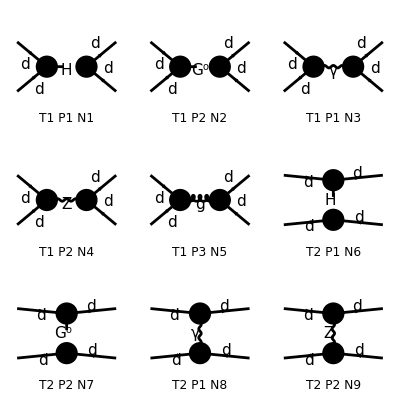

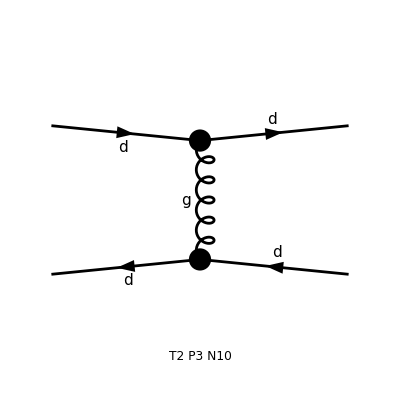

```mathematica
Process={F[4,{1}],-F[4,{1}]}-> {F[4,{1}],-F[4,{1}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},Model->"SMQCD"];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 5 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 10 Particles amplitudes

FeynAmpList(({F(4,{1}),-F(4,{1})}→{F(4,{1}),-F(4,{1})})→(F(4,{1,Col1}) | p1 | MD | {-Charge/3,(2 ColorCharge)/(√3)}
-F(4,{1,Col2}) | p2 | MD | {Charge/3,-(2 ColorCharge)/(√3)})→(F(4,{1,Col3}) | k1 | MD | {-Charge/3,(2 ColorCharge)/(√3)}
-F(4,{1,Col4}) | k2 | MD | {Charge/3,-(2 ColorCharge)/(√3)}),Model→{SMQCD},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],-v̄(p2,MD).(-(ⅈ EL MD IndexDelta(Col1,Col2) om_-)/(2 MW SW)-(ⅈ EL MD IndexDelta(Col1,Col2) om_+)/(2 MW SW)).u(p1,MD) ū(k1,MD).(-(ⅈ EL MD IndexDelta(Col3,Col4) om_-)/(2 MW SW)-(ⅈ EL MD IndexDelta(Col3,Col4) om_+)/(2 MW SW)).v(k2,MD) 1/((k1+k2)^2-MH2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==1,Particles==2,Number==2),Integral[],-v̄(p2,MD).((EL MD IndexDelta(Col1,Col2) om_+)/(2 MW SW)-(EL MD IndexDelta(Col1,Col2) om_-)/(2 MW SW)).u(p1,MD) ū(k1,MD).((EL MD IndexDelta(Col3,Col4) om_+)/(2 MW SW)-(EL MD IndexDelta(Col3,Col4) om_-)/(2 MW SW)).v(k2,MD) 1/((k1+k2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==3),Integral[],v̄(p2,MD).(1/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_-+1/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_+).u(p1,MD) ū(k1,MD).(1/3 ⅈ EL IndexDelta(Col3,Col4) ga(Lor2).om_-+1/3 ⅈ EL IndexDelta(Col3,Col4) ga(Lor2).om_+).v(k2,MD) g(Lor1,Lor2) 1/(k1+k2)^2 SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==4),Integral[],v̄(p2,MD).((ⅈ EL (SW2/3-1/2) IndexDelta(Col1,Col2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW IndexDelta(Col1,Col2) ga(Lor1).om_+)/(3 CW)).u(p1,MD) ū(k1,MD).((ⅈ EL (SW2/3-1/2) IndexDelta(Col3,Col4) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW IndexDelta(Col3,Col4) ga(Lor2).om_+)/(3 CW)).v(k2,MD) g(Lor1,Lor2) 1/((k1+k2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==3,Number==5),Integral[],v̄(p2,MD).(-ⅈ GS ga(Lor1).om_- SUNT(Glu5,Col2,Col1)-ⅈ GS ga(Lor1).om_+ SUNT(Glu5,Col2,Col1)).u(p1,MD) ū(k1,MD).(-ⅈ GS ga(Lor2).om_- SUNT(Glu5,Col3,Col4)-ⅈ GS ga(Lor2).om_+ SUNT(Glu5,Col3,Col4)).v(k2,MD) g(Lor1,Lor2) 1/(k1+k2)^2 SumOver(Glu5,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==6),Integral[],v̄(p2,MD).(-(ⅈ EL MD IndexDelta(Col2,Col4) om_-)/(2 MW SW)-(ⅈ EL MD IndexDelta(Col2,Col4) om_+)/(2 MW SW)).v(k2,MD) ū(k1,MD).(-(ⅈ EL MD IndexDelta(Col1,Col3) om_-)/(2 MW SW)-(ⅈ EL MD IndexDelta(Col1,Col3) om_+)/(2 MW SW)).u(p1,MD) 1/((k2-p2)^2-MH2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==2,Number==7),Integral[],v̄(p2,MD).((EL MD IndexDelta(Col2,Col4) om_+)/(2 MW SW)-(EL MD IndexDelta(Col2,Col4) om_-)/(2 MW SW)).v(k2,MD) ū(k1,MD).((EL MD IndexDelta(Col1,Col3) om_+)/(2 MW SW)-(EL MD IndexDelta(Col1,Col3) om_-)/(2 MW SW)).u(p1,MD) 1/((k2-p2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==2,Generic==2,Particles==1,Number==8),Integral[],-v̄(p2,MD).(1/3 ⅈ EL IndexDelta(Col2,Col4) ga(Lor2).om_-+1/3 ⅈ EL IndexDelta(Col2,Col4) ga(Lor2).om_+).v(k2,MD) ū(k1,MD).(1/3 ⅈ EL IndexDelta(Col1,Col3) ga(Lor1).om_-+1/3 ⅈ EL IndexDelta(Col1,Col3) ga(Lor1).om_+).u(p1,MD) g(Lor1,Lor2) 1/(k2-p2)^2 SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==2,Generic==2,Particles==2,Number==9),Integral[],-v̄(p2,MD).((ⅈ EL (SW2/3-1/2) IndexDelta(Col2,Col4) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW IndexDelta(Col2,Col4) ga(Lor2).om_+)/(3 CW)).v(k2,MD) ū(k1,MD).((ⅈ EL (SW2/3-1/2) IndexDelta(Col1,Col3) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW IndexDelta(Col1,Col3) ga(Lor1).om_+)/(3 CW)).u(p1,MD) g(Lor1,Lor2) 1/((k2-p2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==2,Generic==2,Particles==3,Number==10),Integral[],-v̄(p2,MD).(-ⅈ GS ga(Lor2).om_- SUNT(Glu5,Col2,Col4)-ⅈ GS ga(Lor2).om_+ SUNT(Glu5,Col2,Col4)).v(k2,MD) ū(k1,MD).(-ⅈ GS ga(Lor1).om_- SUNT(Glu5,Col3,Col1)-ⅈ GS ga(Lor1).om_+ SUNT(Glu5,Col3,Col1)).u(p1,MD) g(Lor1,Lor2) 1/(k2-p2)^2 SumOver(Glu5,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 100 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/avasquez/fc-pol-1.frm

running FORM...

ok

1/(108 CW2^2 MW2^2 SW2^2)π^2 (81/8 Alfa2 CW2^2 (12 (8 MD2^2-4 S MD2+S^2) (Den(S,MH2)-Den(S,MZ2))^2-8 (4 MD2^2-4 S MD2+S (S+U)) (Den(T,MH2)-Den(T,MZ2)) (Den(S,MH2)-Den(S,MZ2))+3 (32 MD2^2-4 (3 S+T+U) MD2+3 S^2+(T-U)^2+4 S U) (Den(T,MH2)-Den(T,MZ2))^2) MD2^2+6 (16 SW2^2 ((2 Alfa-3 Alfas) CW2 Den(S,0)+Alfa (2 SW2-3) Den(S,MZ2))^2 MW2^2+8 SW2 ((2 Alfa-3 Alfas) CW2 Den(S,0)+2 Alfa SW2 Den(S,MZ2)+9 Alfas CW2 Den(T,0)) (Alfa Den(S,MZ2) (3-2 SW2)^2+2 (2 Alfa-3 Alfas) CW2 SW2 Den(S,0)+18 Alfas CW2 SW2 Den(T,0)) MW2^2+3 Alfa CW2 ((Den(S,MH2)-Den(S,MZ2)) (MW2 (2 MD2-U) (8 Alfa Den(T,MZ2) SW2^2+24 Alfa CW2 Den(S,0) SW2+8 Alfa CW2 Den(T,0) SW2+96 Alfas CW2 Den(T,0) SW2-12 Alfa Den(T,MZ2) SW2+3 Alfa (8 SW2^2-12 SW2+9) Den(S,MZ2)+9 Alfa Den(T,MZ2))-3 Alfa (2 MD2-T) (8 CW2 MW2 SW2 Den(S,0)+4 MW2 SW2 (2 SW2-3) Den(S,MZ2)+3 CW2 MD2 (Den(T,MH2)+Den(T,MZ2)))+2 (2 MD2-S) (27 Alfa CW2 MD2 Den(S,MH2)+27 Alfa CW2 MD2 Den(S,MZ2)+4 MW2 SW2 (2 (Alfa+12 Alfas) CW2 Den(T,0)+Alfa (2 SW2-3) Den(T,MZ2))))-(Den(T,MH2)-Den(T,MZ2)) (-2 (2 MD2-T) (8 (Alfa+12 Alfas) CW2 MW2 SW2 Den(S,0)+4 Alfa MW2 SW2 (2 SW2-3) Den(S,MZ2)+27 Alfa CW2 MD2 (Den(T,MH2)+Den(T,MZ2)))+3 Alfa (2 MD2-S) (3 CW2 MD2 Den(S,MH2)+3 CW2 MD2 Den(S,MZ2)+4 MW2 SW2 (2 CW2 Den(T,0)+(2 SW2-3) Den(T,MZ2)))-MW2 (2 MD2-U) (8 (Alfa+12 Alfas) CW2 SW2 Den(S,0)+Alfa ((8 SW2^2-12 SW2+9) Den(S,MZ2)+24 CW2 SW2 Den(T,0)+3 (8 SW2^2-12 SW2+9) Den(T,MZ2)))))) MD2^2-2 (12 (2 MD2-S) SW2 ((2 Alfa-3 Alfas) CW2 Den(S,0)+Alfa (2 SW2-3) Den(S,MZ2)) (4 (2 Alfa-3 Alfas) CW2 SW2 Den(S,0)+Alfa (8 SW2^2-12 SW2+9) Den(S,MZ2)+36 Alfas CW2 SW2 Den(T,0)) MW2^2+(2 MD2-T) (9 CW2 (Alfa MD2 Den(S,MH2)+Alfa MD2 Den(S,MZ2)+4 Alfas MW2 SW2 Den(T,0)) (8 Alfa Den(T,MZ2) SW2^2+24 Alfa CW2 Den(S,0) SW2+8 Alfa CW2 Den(T,0) SW2+96 Alfas CW2 Den(T,0) SW2-12 Alfa Den(T,MZ2) SW2+3 Alfa (8 SW2^2-12 SW2+9) Den(S,MZ2)+9 Alfa Den(T,MZ2))+4 MW2 SW2 ((2 Alfa-3 Alfas) CW2 Den(T,0)+Alfa (2 SW2-3) Den(T,MZ2)) (8 (Alfa+12 Alfas) CW2 SW2 Den(S,0)+Alfa ((8 SW2^2-12 SW2+9) Den(S,MZ2)+24 CW2 SW2 Den(T,0)+3 (8 SW2^2-12 SW2+9) Den(T,MZ2)))) MW2-(2 MD2-U) (27 Alfa CW2 (Alfa MD2 Den(S,MH2)+Alfa MD2 Den(S,MZ2)+4 Alfas MW2 SW2 Den(T,0)) (8 CW2 MW2 SW2 Den(S,0)+4 MW2 SW2 (2 SW2-3) Den(S,MZ2)+3 CW2 MD2 (Den(T,MH2)+Den(T,MZ2)))+4 MW2 SW2 ((2 Alfa-3 Alfas) CW2 Den(T,0)+Alfa (2 SW2-3) Den(T,MZ2)) (8 (Alfa+12 Alfas) CW2 MW2 SW2 Den(S,0)+4 Alfa MW2 SW2 (2 SW2-3) Den(S,MZ2)+27 Alfa CW2 MD2 (Den(T,MH2)+Den(T,MZ2))))) MD2+24 MW2^2 SW2^2 (T-2 MD2)^2 ((2 Alfa-3 Alfas) CW2 Den(S,0)+Alfa (2 SW2-3) Den(S,MZ2))^2+243/2 CW2^2 (8 MD2^2-4 S MD2+S^2) (Alfa MD2 Den(S,MH2)+Alfa MD2 Den(S,MZ2)+4 Alfas MW2 SW2 Den(T,0))^2+24 MW2^2 (8 MD2^2-4 S MD2+S^2) SW2^2 ((2 Alfa-3 Alfas) CW2 Den(T,0)+Alfa (2 SW2-3) Den(T,MZ2))^2+243/2 CW2^2 (8 MD2^2-4 T MD2+T^2) (4 Alfas MW2 SW2 Den(S,0)+Alfa MD2 (Den(T,MH2)+Den(T,MZ2)))^2+36 CW2 MW2 (8 MD2^2-4 S MD2+S^2) SW2 (Alfa MD2 Den(S,MH2)+Alfa MD2 Den(S,MZ2)+4 Alfas MW2 SW2 Den(T,0)) ((2 Alfa-3 Alfas) CW2 Den(T,0)+Alfa (2 SW2-3) Den(T,MZ2))+18 CW2 MW2 (2 SW2 (8 MD2^2-4 T MD2+T^2) ((2 Alfa-3 Alfas) CW2 Den(S,0)+Alfa (2 SW2-3) Den(S,MZ2))-MD2 (2 MD2-S) (4 (2 Alfa-3 Alfas) CW2 SW2 Den(S,0)+Alfa (8 SW2^2-12 SW2+9) Den(S,MZ2)+36 Alfas CW2 SW2 Den(T,0))) (4 Alfas MW2 SW2 Den(S,0)+Alfa MD2 (Den(T,MH2)+Den(T,MZ2)))+4 MW2 SW2 (9 Alfas CW2 Den(S,0)+(2 Alfa-3 Alfas) CW2 Den(T,0)+2 Alfa SW2 Den(T,MZ2)) (4 MW2 (Alfa Den(S,MZ2) (3-2 SW2)^2+2 (2 Alfa-3 Alfas) CW2 SW2 Den(S,0)+18 Alfas CW2 SW2 Den(T,0)) MD2^2-(2 MD2-S) (8 (Alfa+12 Alfas) CW2 MW2 SW2 Den(S,0)+4 Alfa MW2 SW2 (2 SW2-3) Den(S,MZ2)+27 Alfa CW2 MD2 (Den(T,MH2)+Den(T,MZ2))) MD2+2 MW2 SW2 (U-2 MD2)^2 ((2 Alfa-3 Alfas) CW2 Den(S,0)+2 Alfa SW2 Den(S,MZ2)+9 Alfas CW2 Den(T,0)))+2 MW2 (Alfa Den(T,MZ2) (3-2 SW2)^2+18 Alfas CW2 SW2 Den(S,0)+2 (2 Alfa-3 Alfas) CW2 SW2 Den(T,0)) (16 MW2 SW2 ((Alfa+12 Alfas) CW2 Den(S,0)+Alfa (SW2 Den(S,MZ2)+3 CW2 Den(T,0)+3 SW2 Den(T,MZ2))) MD2^2-(2 MD2-S) (8 (Alfa+12 Alfas) CW2 MW2 SW2 Den(S,0)+4 Alfa MW2 SW2 (2 SW2-3) Den(S,MZ2)+27 Alfa CW2 MD2 (Den(T,MH2)+Den(T,MZ2))) MD2+MW2 (U-2 MD2)^2 (Alfa Den(S,MZ2) (3-2 SW2)^2+2 (2 Alfa-3 Alfas) CW2 SW2 Den(S,0)+18 Alfas CW2 SW2 Den(T,0)))+3 MW2^2 (U-2 MD2)^2 (4 (((2 Alfa-3 Alfas) CW2 Den(S,0)+2 Alfa SW2 Den(S,MZ2)+9 Alfas CW2 Den(T,0))^2+(9 Alfas CW2 Den(S,0)+(2 Alfa-3 Alfas) CW2 Den(T,0)+2 Alfa SW2 Den(T,MZ2))^2) SW2^2+(Alfa Den(S,MZ2) (3-2 SW2)^2+2 (2 Alfa-3 Alfas) CW2 SW2 Den(S,0)+18 Alfas CW2 SW2 Den(T,0))^2+(Alfa Den(T,MZ2) (3-2 SW2)^2+18 Alfas CW2 SW2 Den(S,0)+2 (2 Alfa-3 Alfas) CW2 SW2 Den(T,0))^2))

```mathematica
resFCdddd=square1//.{Alfa2->(ee^2/(4π))^2,Alfas2->(gs^2/(4π))^2,Alfa->(ee^2/(4π)),Alfas->(gs^2/(4π)),SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),MD2->0}//FullSimplify[#,S+T+U==0]&
```

1/(1728 cw^4 S^2 sw^4 T^2 (MZ2-T)^2 (MZ2+T+U)^2)(64 cw^4 sw^4 (MZ2-T)^2 (MZ2+T+U)^2 (ee^4 (3 T^4+6 T^3 U+11 T^2 U^2+8 T U^3+3 U^4)-24 ee^2 gs^2 T U^2 (T+U)+18 gs^4 (3 T^2+3 T U+U^2) (T^2+T U+3 U^2))-8 cw^2 ee^2 sw^2 T (MZ2-T) (T+U) (MZ2+T+U) (ee^2 (12 sw^2 (2 sw^2-3) T^2 U (3 MZ2+4 T)+4 T U^2 ((2 sw^2-3) sw^2 (9 MZ2+22 T)+9 T)+4 U^3 (MZ2 (14 sw^4-21 sw^2+9)+(32 sw^4-48 sw^2+9) T)+24 sw^2 (2 sw^2-3) T^4+3 (3-4 sw^2)^2 U^4)-12 gs^2 (8 sw^4-12 sw^2+9) U^2 (2 T (T+U)-MZ2 U))+ee^4 T^2 (T+U)^2 (4 U^2 (2 MZ2^2 ((2 sw^2-3) (22 sw^4-33 sw^2+72) sw^2+81)+36 MZ2 (3-2 sw^2)^2 sw^4 T+(4 (2 sw^2-3) (22 sw^4-33 sw^2+18) sw^2+81) T^2)+48 (3-2 sw^2)^2 sw^4 T^2 (MZ2^2+T^2)+48 (3-2 sw^2)^2 sw^4 T U (MZ2+T) (MZ2+2 T)+4 U^3 (2 MZ2 (56 sw^8-168 sw^6+270 sw^4-216 sw^2+81)+(8 (2 sw^2-3) (8 sw^4-12 sw^2+9) sw^2+81) T)+3 (8 sw^4-12 sw^2+9)^2 U^4))

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARdddd=Get["resANATARdddd.m"];
```

```mathematica
FullSimplify[resANATARdddd- 16 resFCdddd,{S+T+U==0,cw^2+sw^2==1}]
```

0

## dd -> tt

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
Addtt=GenerateAmplitude[{d,dbar}->{t,tbar},OutputName->"ddtt",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddtt.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/ddtt/ddtt_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {d, dbar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{d(p1),dbar(p2)}→{t(p3),tbar(p4)}},Total→3,Name→ddtt,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→S/2,p1.p3→1/2 (MT^2-T),p2.p3→1/2 (MT^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MT^2-T),1/(p2.p3)→2/(MT^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC1 GC2 Den(-p1-p2,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT),DiagramID(2)→1/4 ⅈ Den(-p1-p2,MZ) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT) ((GC34-GC13) (γ^iLor2 γ^5)_(Spin1 Spin3)+(GC13+GC34) (γ^iLor2)_(Spin1 Spin3)) ((GC26+5 GC33) (γ^iLor2)_(Spin2 Spin4)-(GC26-3 GC33) (γ^iLor2 γ^5)_(Spin2 Spin4)),DiagramID(3)→ⅈ GC10^2 Den(-p1-p2,0) T_Colour3Colour1^iGluon2 T_Colour2Colour4^iGluon2 (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) u_Spin1^Colour1(p1,0) (v̄)_Spin3^Colour3(p2,0) (ū)_Spin2^Colour2(p3,MT) v_Spin4^Colour4(p4,MT)}|>

```mathematica
AddttC=GenerateAmplitudeConjugate[{d,dbar}->{t,tbar},OutputName->"ddtt",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddtt.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/ddtt/ddtt_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {d, dbar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{d(p1),dbar(p2)}→{t(p3),tbar(p4)}},Total→3,Name→ddtt,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→S/2,p1.p3→1/2 (MT^2-T),p2.p3→1/2 (MT^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MT^2-T),1/(p2.p3)→2/(MT^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC1 GC2 Den(-p1-p2,0) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT),DiagramID(2)→-1/4 ⅈ Den(-p1-p2,MZ) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) ((GC13-GC34) (γ^5 γ^iLorC2)_(SpinC1 SpinC3)+(GC13+GC34) (γ^iLorC2)_(SpinC1 SpinC3)) ((GC26-3 GC33) (γ^5 γ^iLorC2)_(SpinC2 SpinC4)+(GC26+5 GC33) (γ^iLorC2)_(SpinC2 SpinC4)),DiagramID(3)→-ⅈ GC10^2 Den(-p1-p2,0) T_ColourC1ColourC3^iGluonC2 T_ColourC4ColourC2^iGluonC2 (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) ((ū)^†)_SpinC1^ColourC1(p1,0) (v^†)_SpinC3^ColourC3(p2,0) (u^†)_SpinC2^ColourC2(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)}|>

```mathematica
AmpSQddtt=GenerateAmplitudeSquare[Addtt,AddttC,Dimension->4,CasimirValues->True]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{d(p1),dbar(p2)}→{t(p3),tbar(p4)}},Name→ddtt,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→S/2,p1.p3→1/2 (MT^2-T),p2.p3→1/2 (MT^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MT^2-T),1/(p2.p3)→2/(MT^2-U),p4→p1+p2-p3},Amplitudes→1/36 (-1/(cw^2 sw2)16 ee^4 Den(-p1-p2,0) Den(-p1-p2,MZ) (9 cw^4 (MT^4-MT^2 (2 S+T+U)+U (S+T))-18 cw^2 sw2 (MT^4-MT^2 (2 S+T+U)+T (S+U))+sw2^2 (5 MT^4-5 MT^2 (2 S+T+U)-2 S T+7 S U+5 T U))-1/(cw^4 sw2^2)ee^4 (Den(-p1-p2,MZ))^2 (81 cw^8 (MT^2-U) (MT^2-S-T)+216 cw^6 MT^2 S sw2+18 cw^4 sw2^2 (9 MT^4-MT^2 (5 S+9 (T+U))+10 S T-S U+9 T U)+72 cw^2 sw2^3 (MT^4-MT^2 (T+U)+T (S+U))+5 sw2^4 (17 MT^4-MT^2 (25 S+17 (T+U))+4 S T+13 S U+17 T U))-64 (2 ee^4+9 gs^4) (Den(-p1-p2,0))^2 (2 MT^4-2 MT^2 (2 S+T+U)+S (T+U)+2 T U))|>

```mathematica
resANATARddtt=AmpSQddtt[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),Nc->3,-p1-p2->√S,(p1-p3)->√T,p3-p2->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/36 (-(16 ee^4 (9 cw^4 (MT^4-MT^2 (2 S+T+U)+U (S+T))-18 cw^2 sw^2 (MT^4-MT^2 (2 S+T+U)+T (S+U))+sw^4 (5 MT^4-5 MT^2 (2 S+T+U)-2 S T+7 S U+5 T U)))/(cw^2 S sw^2 (S-MZ^2))-1/(cw^4 sw^4 (S-MZ^2)^2)ee^4 (81 cw^8 (MT^2-U) (MT^2-S-T)+216 cw^6 MT^2 S sw^2+18 cw^4 sw^4 (9 MT^4-MT^2 (5 S+9 (T+U))+10 S T-S U+9 T U)+72 cw^2 sw^6 (MT^4-MT^2 (T+U)+T (S+U))+5 sw^8 (17 MT^4-MT^2 (25 S+17 (T+U))+4 S T+13 S U+17 T U))-(64 (2 ee^4+9 gs^4) (2 MT^4-2 MT^2 (2 S+T+U)+S (T+U)+2 T U))/S^2)

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARddtt.m",resANATARddtt];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SMQCD.mod

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 5 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 5 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 5 diagrams

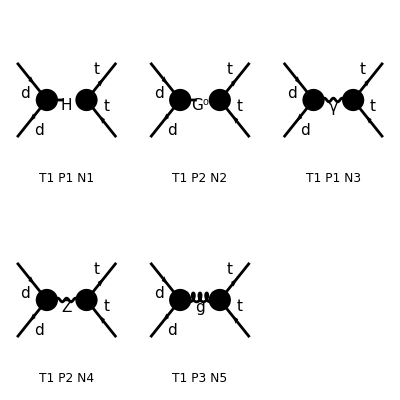

```mathematica
Process={F[4,{1}],-F[4,{1}]}-> {F[3,{3}],-F[3,{3}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},Model->"SMQCD"];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 5 Particles amplitudes

in total: 5 Particles amplitudes

FeynAmpList(({F(4,{1}),-F(4,{1})}→{F(3,{3}),-F(3,{3})})→(F(4,{1,Col1}) | p1 | MD | {-Charge/3,(2 ColorCharge)/(√3)}
-F(4,{1,Col2}) | p2 | MD | {Charge/3,-(2 ColorCharge)/(√3)})→(F(3,{3,Col3}) | k1 | MT | {(2 Charge)/3,(2 ColorCharge)/(√3)}
-F(3,{3,Col4}) | k2 | MT | {-(2 Charge)/3,-(2 ColorCharge)/(√3)}),Model→{SMQCD},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],-v̄(p2,MD).(-(ⅈ EL MD IndexDelta(Col1,Col2) om_-)/(2 MW SW)-(ⅈ EL MD IndexDelta(Col1,Col2) om_+)/(2 MW SW)).u(p1,MD) ū(k1,MT).(-(ⅈ EL MT IndexDelta(Col3,Col4) om_-)/(2 MW SW)-(ⅈ EL MT IndexDelta(Col3,Col4) om_+)/(2 MW SW)).v(k2,MT) 1/((k1+k2)^2-MH2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==1,Particles==2,Number==2),Integral[],-v̄(p2,MD).((EL MD IndexDelta(Col1,Col2) om_+)/(2 MW SW)-(EL MD IndexDelta(Col1,Col2) om_-)/(2 MW SW)).u(p1,MD) ū(k1,MT).((EL MT IndexDelta(Col3,Col4) om_-)/(2 MW SW)-(EL MT IndexDelta(Col3,Col4) om_+)/(2 MW SW)).v(k2,MT) 1/((k1+k2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==3),Integral[],v̄(p2,MD).(1/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_-+1/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_+).u(p1,MD) ū(k1,MT).(-2/3 ⅈ EL IndexDelta(Col3,Col4) ga(Lor2).om_--2/3 ⅈ EL IndexDelta(Col3,Col4) ga(Lor2).om_+).v(k2,MT) g(Lor1,Lor2) 1/(k1+k2)^2 SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==4),Integral[],v̄(p2,MD).((ⅈ EL (SW2/3-1/2) IndexDelta(Col1,Col2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW IndexDelta(Col1,Col2) ga(Lor1).om_+)/(3 CW)).u(p1,MD) ū(k1,MT).((ⅈ EL (1/2-(2 SW2)/3) IndexDelta(Col3,Col4) ga(Lor2).om_-)/(CW SW)-(2 ⅈ EL SW IndexDelta(Col3,Col4) ga(Lor2).om_+)/(3 CW)).v(k2,MT) g(Lor1,Lor2) 1/((k1+k2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==3,Number==5),Integral[],v̄(p2,MD).(-ⅈ GS ga(Lor1).om_- SUNT(Glu5,Col2,Col1)-ⅈ GS ga(Lor1).om_+ SUNT(Glu5,Col2,Col1)).u(p1,MD) ū(k1,MT).(-ⅈ GS ga(Lor2).om_- SUNT(Glu5,Col3,Col4)-ⅈ GS ga(Lor2).om_+ SUNT(Glu5,Col3,Col4)).v(k2,MT) g(Lor1,Lor2) 1/(k1+k2)^2 SumOver(Glu5,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 64 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/avasquez/fc-pol-1.frm

running FORM...

ok

1/(36 CW2^2 MW2^2 SW2^2)π^2 (64 CW2^2 MW2^2 SW2^2 (2 Alfa2+9 Alfas2) (Den(S,0))^2 (2 MD2^2+2 MD2 (2 MT2+S-T-U)+2 MT2^2+2 MT2 (S-T-U)+T^2+U^2)+Alfa2 ((Den(S,MZ2))^2 (81 CW2^2 MD2 MT2 S^2-162 CW2 MD2 MT2 MW2 (2 MD2+2 MT2-T-U)+MW2^2 (MD2^2 (256 SW2^4-576 SW2^3+648 SW2^2-324 SW2+81)+2 MD2 (MT2 (256 SW2^4-576 SW2^3+288 SW2^2+81)+2 S (64 SW2^3-144 SW2^2+90 SW2-27) SW2-128 SW2^4 T-128 SW2^4 U+288 SW2^3 T+288 SW2^3 U-180 SW2^2 T-468 SW2^2 U+324 SW2 U-81 U)+MT2^2 (256 SW2^4-576 SW2^3+648 SW2^2-324 SW2+81)+2 MT2 (4 S (32 SW2^3-72 SW2^2+72 SW2-27) SW2-128 SW2^4 (T+U)+288 SW2^3 (T+U)-36 SW2^2 (5 T+13 U)+324 SW2 U-81 U)+128 SW2^4 T^2+128 SW2^4 U^2-288 SW2^3 T^2-288 SW2^3 U^2+180 SW2^2 T^2+468 SW2^2 U^2-324 SW2 U^2+81 U^2))+81 CW2^2 MD2 MT2 (4 MD2-S) (4 MT2-S) (Den(S,MH2))^2-18 CW2 MD2 MT2 MW2 (32 SW2^2-36 SW2+9) (T-U) Den(S,MH2) Den(S,MZ2))-16 Alfa2 CW2 MW2 SW2 Den(S,0) (36 CW2 MD2 MT2 (T-U) Den(S,MH2)-MW2 Den(S,MZ2) (MD2^2 (32 SW2^2-36 SW2+9)+MD2 (2 MT2 (32 SW2^2-36 SW2+9)+S (32 SW2^2-36 SW2+9)-32 SW2^2 T-32 SW2^2 U+36 SW2 T+36 SW2 U-18 U)+MT2^2 (32 SW2^2-36 SW2+9)+MT2 (S (32 SW2^2-36 SW2+9)-32 SW2^2 (T+U)+36 SW2 (T+U)-18 U)+16 SW2^2 T^2+16 SW2^2 U^2-18 SW2 T^2-18 SW2 U^2+9 U^2)))

```mathematica
resFCddtt=square1//.{Alfa2->(ee^2/(4π))^2,Alfas2->(gs^2/(4π))^2,Alfa->(ee^2/(4π)),Alfas->(gs^2/(4π)),SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),MD2->0,MU2->0}//FullSimplify[#,S+T+U==2MT2]&
```

1/576 ((ee^4 (3 S^2 (8 sw^4-12 sw^2+9) (32 sw^4-24 sw^2+3)+2 S (4 sw^2-3) ((64 sw^6-96 sw^4+27) U+(16 sw^2 (4 sw^4-6 sw^2+9)-27) T)+(8 sw^4-12 sw^2+9) (32 sw^4-24 sw^2+9) (T-U)^2))/(4 cw^4 sw^4 (MZ2-S)^2)-(4 ee^4 (3 S^2 (32 sw^4-36 sw^2+9)+8 S sw^2 (8 sw^2-9) U+S (64 sw^4-72 sw^2+36) T+(32 sw^4-36 sw^2+9) (T-U)^2))/(cw^2 S sw^2 (MZ2-S))+(32 (2 ee^4+9 gs^4) (3 S^2+2 S (T+U)+(T-U)^2))/S^2)

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARddtt=Get["resANATARddtt.m"];
```

```mathematica
FullSimplify[resANATARddtt- 16 resFCddtt,{S+T+U==2MT2,cw^2+sw^2==1}]
```

0

## uu -> WW

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AuuWW=GenerateAmplitude[{u,ubar}->{Wbar,W},OutputName->"uuWW",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uuWW.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/uuWW/uuWW_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {u, ubar} -> {Wbar, W}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{u(p1),ubar(p2)}→{Wbar(p3),W(p4)}},Total→3,Name→uuWW,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→S/2,p1.p3→1/2 (MW^2-T),p2.p3→1/2 (MW^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MW^2-T),1/(p2.p3)→2/(MW^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC2 GC3 Den(-p1-p2,0) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0) ((γ^iLor2)_(Spin1 Spin3) (ε_iLor2(p4,MW) (ε_p1(p3,MW)+ε_p2(p3,MW)+ε_p4(p3,MW))-ε_iLor2(p3,MW) (ε_p1(p4,MW)+ε_p2(p4,MW)+ε_p3(p4,MW)))+ε_Lor2(p3,MW) ε_Lor2(p4,MW) ((γ·p3)_(Spin1 Spin3)-(γ·p4)_(Spin1 Spin3))),DiagramID(2)→1/2 ⅈ GC27 Den(-p1-p2,MZ) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0) (-(GC26-3 GC33) (γ^iLor2 γ^5)_(Spin1 Spin3) (ε_iLor2(p3,MW) (ε_p1(p4,MW)+ε_p2(p4,MW)+ε_p3(p4,MW))-ε_iLor2(p4,MW) (ε_p1(p3,MW)+ε_p2(p3,MW)+ε_p4(p3,MW)))+ε_Lor2(p3,MW) ε_Lor2(p4,MW) ((GC26-3 GC33) (((γ·p3)γ^5)_(Spin1 Spin3)-((γ·p4)γ^5)_(Spin1 Spin3))-((GC26+5 GC33) (γ·p3)_(Spin1 Spin3))+(GC26+5 GC33) (γ·p4)_(Spin1 Spin3))+(GC26+5 GC33) (γ^iLor2)_(Spin1 Spin3) (ε_iLor2(p3,MW) (ε_p1(p4,MW)+ε_p2(p4,MW)+ε_p3(p4,MW))-ε_iLor2(p4,MW) (ε_p1(p3,MW)+ε_p2(p3,MW)+ε_p4(p3,MW)))),DiagramID(3)→-1/4 ⅈ GC25^2 Den(p1-p4,0) ε_Lor2(p3,MW) ε_Lor4(p4,MW) ((γ^Lor2)_(iSpin1 Spin3)-(γ^Lor2 γ^5)_(iSpin1 Spin3)) ((γ^Lor4)_(iSpin2 Spin1)-(γ^Lor4 γ^5)_(iSpin2 Spin1)) (v̄)_Spin3^iColour2(p2,0) u_Spin1^iColour2(p1,0) (γ·(p1-p4))_(iSpin1 iSpin2)}|>

```mathematica
AuuWWC=GenerateAmplitudeConjugate[{u,ubar}->{Wbar,W},OutputName->"uuWW",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uuWW.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/uuWW/uuWW_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {u, ubar} -> {Wbar, W}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{u(p1),ubar(p2)}→{Wbar(p3),W(p4)}},Total→3,Name→uuWW,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→S/2,p1.p3→1/2 (MW^2-T),p2.p3→1/2 (MW^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MW^2-T),1/(p2.p3)→2/(MW^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC2 GC3 Den(-p1-p2,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0) ((γ^iLorC2)_(SpinC1 SpinC3) ((ε^†)_iLorC2^(p4,MW) ((ε^†)_p1^(p3,MW)+(ε^†)_p2^(p3,MW)+(ε^†)_p4^(p3,MW))-(ε^†)_iLorC2^(p3,MW) ((ε^†)_p1^(p4,MW)+(ε^†)_p2^(p4,MW)+(ε^†)_p3^(p4,MW)))+(ε^†)_LorC2^(p3,MW) (ε^†)_LorC2^(p4,MW) ((γ·p3)_(SpinC1 SpinC3)-(γ·p4)_(SpinC1 SpinC3))),DiagramID(2)→-1/2 ⅈ GC27 Den(-p1-p2,MZ) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0) ((GC26+5 GC33) (γ^iLorC2)_(SpinC1 SpinC3) ((ε^†)_iLorC2^(p3,MW) ((ε^†)_p1^(p4,MW)+(ε^†)_p2^(p4,MW)+(ε^†)_p3^(p4,MW))-(ε^†)_iLorC2^(p4,MW) ((ε^†)_p1^(p3,MW)+(ε^†)_p2^(p3,MW)+(ε^†)_p4^(p3,MW)))+(GC26-3 GC33) (γ^5 γ^iLorC2)_(SpinC1 SpinC3) ((ε^†)_iLorC2^(p3,MW) ((ε^†)_p1^(p4,MW)+(ε^†)_p2^(p4,MW)+(ε^†)_p3^(p4,MW))-(ε^†)_iLorC2^(p4,MW) ((ε^†)_p1^(p3,MW)+(ε^†)_p2^(p3,MW)+(ε^†)_p4^(p3,MW)))+(ε^†)_LorC2^(p3,MW) (ε^†)_LorC2^(p4,MW) (-(GC26-3 GC33) ((γ^5(γ·p3))_(SpinC1 SpinC3)-(γ^5(γ·p4))_(SpinC1 SpinC3))-((GC26+5 GC33) (γ·p3)_(SpinC1 SpinC3))+(GC26+5 GC33) (γ·p4)_(SpinC1 SpinC3))),DiagramID(3)→1/4 ⅈ GC25^2 Den(p1-p4,0) (ε^†)_LorC2^(p3,MW) (ε^†)_LorC4^(p4,MW) ((γ^5 γ^LorC2)_(iSpinC1 SpinC3)+(γ^LorC2)_(iSpinC1 SpinC3)) ((γ^5 γ^LorC4)_(iSpinC2 SpinC1)+(γ^LorC4)_(iSpinC2 SpinC1)) ((ū)^†)_SpinC1^iColourC2(p1,0) (v^†)_SpinC3^iColourC2(p2,0) ((γ·p1)_(iSpinC1 iSpinC2)-(γ·p4)_(iSpinC1 iSpinC2))}|>

```mathematica
AmpSQuuWW=GenerateAmplitudeSquare[AuuWW,AuuWWC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{u(p1),ubar(p2)}→{Wbar(p3),W(p4)}},Name→uuWW,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→S/2,p1.p3→1/2 (MW^2-T),p2.p3→1/2 (MW^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MW^2-T),1/(p2.p3)→2/(MW^2-U),p4→p1+p2-p3},Amplitudes→1/(144 MW^4 sw2^2)ee^4 Nc (32 sw2^2 (32 MW^8-8 (7 S+3 (T+U)) MW^6-4 (5 S^2+2 (T-U)^2) MW^4+2 (-6 (T+U) S^2+(T-U)^2 S+4 T U (T+U)) MW^2+S ((T+U)^3+S (T^2+6 U T+U^2))) (Den(-p1-p2,0))^2+8 sw2 ((3 cw^2-5 sw2) (32 MW^8-8 (7 S+3 (T+U)) MW^6-4 (5 S^2+2 (T-U)^2) MW^4+2 (-6 (T+U) S^2+(T-U)^2 S+4 T U (T+U)) MW^2+S ((T+U)^3+S (T^2+6 U T+U^2))) Den(-p1-p2,MZ)+12 (6 MW^8-(11 S+7 T+5 U) MW^6+(-3 S^2+2 T S+3 U S+T^2-U^2+6 T U) MW^4+(S^3-U S^2-(T^2+2 U T-2 U^2) S+T U (U-T)) MW^2+S T (S+T) U) Den(p3-p2,0)) Den(-p1-p2,0)+(9 cw^4-6 sw2 cw^2+17 sw2^2) (32 MW^8-8 (7 S+3 (T+U)) MW^6-4 (5 S^2+2 (T-U)^2) MW^4+2 (-6 (T+U) S^2+(T-U)^2 S+4 T U (T+U)) MW^2+S ((T+U)^3+S (T^2+6 U T+U^2))) (Den(-p1-p2,MZ))^2+36 (4 MW^8-2 (3 S+3 T+U) MW^6+(-S^2+2 (T+2 U) S+3 T^2-2 U^2+4 T U) MW^4+(S+T) (S^2-U S-T^2+2 U^2-3 T U) MW^2+T (S+T)^2 U) (Den(p3-p2,0))^2+24 (3 cw^2-sw2) (6 MW^8-(11 S+7 T+5 U) MW^6+(-3 S^2+2 T S+3 U S+T^2-U^2+6 T U) MW^4+(S^3-U S^2-(T^2+2 U T-2 U^2) S+T U (U-T)) MW^2+S T (S+T) U) Den(-p1-p2,MZ) Den(p3-p2,0))|>

```mathematica
resANATARuuWW=AmpSQuuWW[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),Nc->3,-p1-p2->√S,(p1-p3)->√T,p3-p2->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/(48 MW^4 sw^4)ee^4 (1/S 8 sw^2 (((3 cw^2-5 sw^2) (32 MW^8-8 MW^6 (7 S+3 (T+U))-4 MW^4 (5 S^2+2 (T-U)^2)+2 MW^2 (-6 S^2 (T+U)+S (T-U)^2+4 T U (T+U))+S (S (T^2+6 T U+U^2)+(T+U)^3)))/(S-MZ^2)+(12 (6 MW^8-MW^6 (11 S+7 T+5 U)+MW^4 (-3 S^2+2 S T+3 S U+T^2+6 T U-U^2)+MW^2 (S^3-S^2 U-S (T^2+2 T U-2 U^2)+T U (U-T))+S T U (S+T)))/U)+(24 (3 cw^2-sw^2) (6 MW^8-MW^6 (11 S+7 T+5 U)+MW^4 (-3 S^2+2 S T+3 S U+T^2+6 T U-U^2)+MW^2 (S^3-S^2 U-S (T^2+2 T U-2 U^2)+T U (U-T))+S T U (S+T)))/(U (S-MZ^2))+((9 cw^4-6 cw^2 sw^2+17 sw^4) (32 MW^8-8 MW^6 (7 S+3 (T+U))-4 MW^4 (5 S^2+2 (T-U)^2)+2 MW^2 (-6 S^2 (T+U)+S (T-U)^2+4 T U (T+U))+S (S (T^2+6 T U+U^2)+(T+U)^3)))/((S-MZ^2)^2)+(32 sw^4 (32 MW^8-8 MW^6 (7 S+3 (T+U))-4 MW^4 (5 S^2+2 (T-U)^2)+2 MW^2 (-6 S^2 (T+U)+S (T-U)^2+4 T U (T+U))+S (S (T^2+6 T U+U^2)+(T+U)^3)))/S^2+(36 (4 MW^8-2 MW^6 (3 S+3 T+U)+MW^4 (-S^2+2 S (T+2 U)+3 T^2+4 T U-2 U^2)+MW^2 (S+T) (S^2-S U-T^2-3 T U+2 U^2)+T U (S+T)^2))/U^2)

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARuuWW.m",resANATARuuWW];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 3 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 1 Particles insertion

in total: 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 3 diagrams

> Top. 2 aebf/cfde/ef.m, 1 diagram

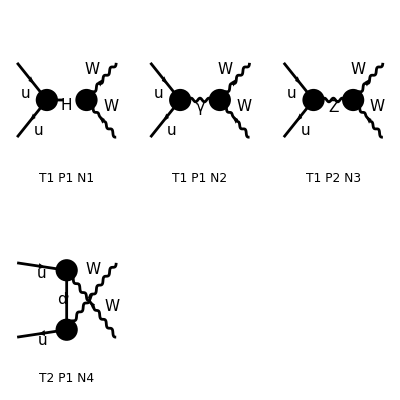

```mathematica
Process={F[3,{1}],-F[3,{1}]}-> {V[3],-V[3]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 1 Particles amplitude

in total: 4 Particles amplitudes

FeynAmpList(({F(3,{1}),-F(3,{1})}→{V(3),-V(3)})→(F(3,{1,Col1}) | p1 | MU | {(2 Charge)/3,(2 ColorCharge)/(√3)}
-F(3,{1,Col2}) | p2 | MU | {-(2 Charge)/3,-(2 ColorCharge)/(√3)})→(V(3) | k1 | MW | -Charge
-V(3) | k2 | MW | Charge),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],1/SW ⅈ EL MW 1/((k1+k2)^2-MH2) g(Lor1,Lor2) SumOver(Col1,3,External) SumOver(Col2,3,External) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,MU).(-(ⅈ EL MU om_- IndexDelta(Col1,Col2))/(2 MW SW)-(ⅈ EL MU om_+ IndexDelta(Col1,Col2))/(2 MW SW)).u(p1,MU)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==2),Integral[],ⅈ EL 1/(k1+k2)^2 g(Lor3,Lor4) SumOver(Col1,3,External) SumOver(Col2,3,External) (g(Lor1,Lor2) (k1-k2)(Lor4)+g(Lor1,Lor4) (-2 (k1)-k2)(Lor2)+g(Lor2,Lor4) (k1+2 (k2))(Lor1)) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,MU).(-2/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor3).om_--2/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor3).om_+).u(p1,MU)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==3),Integral[],-1/SW ⅈ CW EL 1/((k1+k2)^2-MZ2) g(Lor3,Lor4) SumOver(Col1,3,External) SumOver(Col2,3,External) (g(Lor1,Lor2) (k1-k2)(Lor4)+g(Lor1,Lor4) (-2 (k1)-k2)(Lor2)+g(Lor2,Lor4) (k1+2 (k2))(Lor1)) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,MU).((ⅈ EL (1/2-(2 SW2)/3) IndexDelta(Col1,Col2) ga(Lor3).om_-)/(CW SW)-(2 ⅈ EL SW IndexDelta(Col1,Col2) ga(Lor3).om_+)/(3 CW)).u(p1,MU)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==4),Integral[],SumOver(Col1,3,External) SumOver(Col2,3,External) 1/((p2-k1)^2-MD2) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,MU).(ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_-)/(√2 SW).(gs(k1-p2)+MD).(ⅈ EL ga(Lor2).om_-)/(√2 SW).u(p1,MU)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 100 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/avasquez/fc-pol-1.frm

running FORM...

ok

1/(12 MW2^2 SW2^2)Alfa2 π^2 (36 (Den(U,MD2))^2 MU2^4+288 MW2 (Den(U,MD2))^2 MU2^3-72 S (Den(U,MD2))^2 MU2^3-36 T (Den(U,MD2))^2 MU2^3-108 U (Den(U,MD2))^2 MU2^3+432 MW2 Den(S,MZ2) Den(U,MD2) MU2^3-72 S Den(S,MZ2) Den(U,MD2) MU2^3-432 MW2^2 (Den(S,MZ2))^2 MU2^2-36 S^2 (Den(S,MZ2))^2 MU2^2-512 MW2^2 SW2^2 (Den(S,MZ2))^2 MU2^2+128 S^2 SW2^2 (Den(S,MZ2))^2 MU2^2+512 MW2 S SW2^2 (Den(S,MZ2))^2 MU2^2+432 MW2 S (Den(S,MZ2))^2 MU2^2-1152 MW2^2 SW2 (Den(S,MZ2))^2 MU2^2-96 S^2 SW2 (Den(S,MZ2))^2 MU2^2-384 MW2 S SW2 (Den(S,MZ2))^2 MU2^2+1116 MW2^2 (Den(U,MD2))^2 MU2^2+108 U^2 (Den(U,MD2))^2 MU2^2-216 MW2 S (Den(U,MD2))^2 MU2^2-432 MW2 T (Den(U,MD2))^2 MU2^2+54 S T (Den(U,MD2))^2 MU2^2-432 MW2 U (Den(U,MD2))^2 MU2^2+126 S U (Den(U,MD2))^2 MU2^2+108 T U (Den(U,MD2))^2 MU2^2+2448 MW2^2 Den(S,MZ2) Den(U,MD2) MU2^2-72 S^2 Den(S,MZ2) Den(U,MD2) MU2^2-216 MW2 S Den(S,MZ2) Den(U,MD2) MU2^2-2496 MW2^2 SW2 Den(S,MZ2) Den(U,MD2) MU2^2+96 S^2 SW2 Den(S,MZ2) Den(U,MD2) MU2^2-96 MW2 S SW2 Den(S,MZ2) Den(U,MD2) MU2^2-504 MW2 T Den(S,MZ2) Den(U,MD2) MU2^2+108 S T Den(S,MZ2) Den(U,MD2) MU2^2+96 MW2 SW2 T Den(S,MZ2) Den(U,MD2) MU2^2-48 S SW2 T Den(S,MZ2) Den(U,MD2) MU2^2-360 MW2 U Den(S,MZ2) Den(U,MD2) MU2^2+36 S U Den(S,MZ2) Den(U,MD2) MU2^2-96 MW2 SW2 U Den(S,MZ2) Den(U,MD2) MU2^2+48 S SW2 U Den(S,MZ2) Den(U,MD2) MU2^2-18 (4 MU2-S) (12 MW2^2-4 S MW2+S^2) (Den(S,MH2))^2 MU2-2304 MW2^3 (Den(S,MZ2))^2 MU2-54 S^3 (Den(S,MZ2))^2 MU2+216 MW2 S^2 (Den(S,MZ2))^2 MU2-8192 MW2^3 SW2^2 (Den(S,MZ2))^2 MU2-256 S^3 SW2^2 (Den(S,MZ2))^2 MU2+2560 MW2 S^2 SW2^2 (Den(S,MZ2))^2 MU2-6144 MW2^2 S SW2^2 (Den(S,MZ2))^2 MU2-360 MW2^2 S (Den(S,MZ2))^2 MU2+6144 MW2^3 SW2 (Den(S,MZ2))^2 MU2+192 S^3 SW2 (Den(S,MZ2))^2 MU2-1920 MW2 S^2 SW2 (Den(S,MZ2))^2 MU2+6144 MW2^2 S SW2 (Den(S,MZ2))^2 MU2+512 MW2^2 SW2^2 T (Den(S,MZ2))^2 MU2-128 S^2 SW2^2 T (Den(S,MZ2))^2 MU2-512 MW2 S SW2^2 T (Den(S,MZ2))^2 MU2-288 MW2 S T (Den(S,MZ2))^2 MU2+1152 MW2^2 SW2 T (Den(S,MZ2))^2 MU2+96 S^2 SW2 T (Den(S,MZ2))^2 MU2+384 MW2 S SW2 T (Den(S,MZ2))^2 MU2+512 MW2^2 SW2^2 U (Den(S,MZ2))^2 MU2-128 S^2 SW2^2 U (Den(S,MZ2))^2 MU2-512 MW2 S SW2^2 U (Den(S,MZ2))^2 MU2-288 MW2 S U (Den(S,MZ2))^2 MU2+1152 MW2^2 SW2 U (Den(S,MZ2))^2 MU2+96 S^2 SW2 U (Den(S,MZ2))^2 MU2+384 MW2 S SW2 U (Den(S,MZ2))^2 MU2+1152 MW2^3 (Den(U,MD2))^2 MU2+9 S^3 (Den(U,MD2))^2 MU2-36 U^3 (Den(U,MD2))^2 MU2-72 MW2 S^2 (Den(U,MD2))^2 MU2+216 MW2 T^2 (Den(U,MD2))^2 MU2-18 S T^2 (Den(U,MD2))^2 MU2+216 MW2 U^2 (Den(U,MD2))^2 MU2-54 S U^2 (Den(U,MD2))^2 MU2-108 T U^2 (Den(U,MD2))^2 MU2-180 MW2^2 S (Den(U,MD2))^2 MU2-1368 MW2^2 T (Den(U,MD2))^2 MU2-27 S^2 T (Den(U,MD2))^2 MU2+342 MW2 S T (Den(U,MD2))^2 MU2-792 MW2^2 U (Den(U,MD2))^2 MU2+27 S^2 U (Den(U,MD2))^2 MU2-54 MW2 S U (Den(U,MD2))^2 MU2+432 MW2 T U (Den(U,MD2))^2 MU2-72 S T U (Den(U,MD2))^2 MU2+1008 MW2^3 Den(S,MZ2) Den(U,MD2) MU2+36 MW2 S^2 Den(S,MZ2) Den(U,MD2) MU2+180 MW2 T^2 Den(S,MZ2) Den(U,MD2) MU2-54 S T^2 Den(S,MZ2) Den(U,MD2) MU2-96 MW2 SW2 T^2 Den(S,MZ2) Den(U,MD2) MU2+48 S SW2 T^2 Den(S,MZ2) Den(U,MD2) MU2+36 MW2 U^2 Den(S,MZ2) Den(U,MD2) MU2+18 S U^2 Den(S,MZ2) Den(U,MD2) MU2+96 MW2 SW2 U^2 Den(S,MZ2) Den(U,MD2) MU2-48 S SW2 U^2 Den(S,MZ2) Den(U,MD2) MU2-864 MW2^2 S Den(S,MZ2) Den(U,MD2) MU2+24 S^3 SW2 Den(S,MZ2) Den(U,MD2) MU2-336 MW2 S^2 SW2 Den(S,MZ2) Den(U,MD2) MU2+1728 MW2^2 S SW2 Den(S,MZ2) Den(U,MD2) MU2-2376 MW2^2 T Den(S,MZ2) Den(U,MD2) MU2-54 S^2 T Den(S,MZ2) Den(U,MD2) MU2+576 MW2 S T Den(S,MZ2) Den(U,MD2) MU2+2496 MW2^2 SW2 T Den(S,MZ2) Den(U,MD2) MU2+72 S^2 SW2 T Den(S,MZ2) Den(U,MD2) MU2-816 MW2 S SW2 T Den(S,MZ2) Den(U,MD2) MU2-216 MW2^2 U Den(S,MZ2) Den(U,MD2) MU2+126 S^2 U Den(S,MZ2) Den(U,MD2) MU2-576 MW2 S U Den(S,MZ2) Den(U,MD2) MU2+192 MW2^2 SW2 U Den(S,MZ2) Den(U,MD2) MU2-168 S^2 SW2 U Den(S,MZ2) Den(U,MD2) MU2+1200 MW2 S SW2 U Den(S,MZ2) Den(U,MD2) MU2+216 MW2 T U Den(S,MZ2) Den(U,MD2) MU2-36 S T U Den(S,MZ2) Den(U,MD2) MU2-6 Den(S,MH2) (2 (12 MW2^2-S^2) (8 SW2-3) (T-U) Den(S,MZ2)+3 (-4 (S+3 T-3 U) MW2^2+2 (2 S^2+(T-U) S+(T-U)^2) MW2+4 MU2 (S-2 MW2)^2+S ((T-U)^2-S^2)) Den(U,MD2)) MU2-128 SW2^2 (60 MW2^4+4 (S-8 (T+U)) MW2^3-(15 S^2+8 (T+U) S-4 (T^2-U T+U^2)) MW2^2+2 S (3 S^2+3 (T+U) S-T^2-U^2) MW2+MU2^2 (4 MW2^2-4 S MW2-S^2)-S^2 (S+T) (S+U)+MU2 (64 MW2^3+(48 S-4 (T+U)) MW2^2+4 S (-5 S+T+U) MW2+S^2 (2 S+T+U))) (Den(S,0))^2-2736 MW2^4 (Den(S,MZ2))^2+36 S^4 (Den(S,MZ2))^2-216 MW2 S^3 (Den(S,MZ2))^2+684 MW2^2 S^2 (Den(S,MZ2))^2-7680 MW2^4 SW2^2 (Den(S,MZ2))^2+128 S^4 SW2^2 (Den(S,MZ2))^2-768 MW2 S^3 SW2^2 (Den(S,MZ2))^2+1920 MW2^2 S^2 SW2^2 (Den(S,MZ2))^2-512 MW2^3 S SW2^2 (Den(S,MZ2))^2-512 MW2^2 SW2^2 T^2 (Den(S,MZ2))^2+256 MW2 S SW2^2 T^2 (Den(S,MZ2))^2+72 MW2 S T^2 (Den(S,MZ2))^2-192 MW2 S SW2 T^2 (Den(S,MZ2))^2-512 MW2^2 SW2^2 U^2 (Den(S,MZ2))^2+256 MW2 S SW2^2 U^2 (Den(S,MZ2))^2+72 MW2 S U^2 (Den(S,MZ2))^2-192 MW2 S SW2 U^2 (Den(S,MZ2))^2-144 MW2^3 S (Den(S,MZ2))^2+7296 MW2^4 SW2 (Den(S,MZ2))^2-96 S^4 SW2 (Den(S,MZ2))^2+576 MW2 S^3 SW2 (Den(S,MZ2))^2-1824 MW2^2 S^2 SW2 (Den(S,MZ2))^2+384 MW2^3 S SW2 (Den(S,MZ2))^2+1152 MW2^3 T (Den(S,MZ2))^2+36 S^3 T (Den(S,MZ2))^2-216 MW2 S^2 T (Den(S,MZ2))^2+4096 MW2^3 SW2^2 T (Den(S,MZ2))^2+128 S^3 SW2^2 T (Den(S,MZ2))^2-768 MW2 S^2 SW2^2 T (Den(S,MZ2))^2+1024 MW2^2 S SW2^2 T (Den(S,MZ2))^2+576 MW2^2 S T (Den(S,MZ2))^2-3072 MW2^3 SW2 T (Den(S,MZ2))^2-96 S^3 SW2 T (Den(S,MZ2))^2+576 MW2 S^2 SW2 T (Den(S,MZ2))^2-1536 MW2^2 S SW2 T (Den(S,MZ2))^2+1152 MW2^3 U (Den(S,MZ2))^2+36 S^3 U (Den(S,MZ2))^2-216 MW2 S^2 U (Den(S,MZ2))^2+4096 MW2^3 SW2^2 U (Den(S,MZ2))^2+128 S^3 SW2^2 U (Den(S,MZ2))^2-768 MW2 S^2 SW2^2 U (Den(S,MZ2))^2+1024 MW2^2 S SW2^2 U (Den(S,MZ2))^2+576 MW2^2 S U (Den(S,MZ2))^2-3072 MW2^3 SW2 U (Den(S,MZ2))^2-96 S^3 SW2 U (Den(S,MZ2))^2+576 MW2 S^2 SW2 U (Den(S,MZ2))^2-1536 MW2^2 S SW2 U (Den(S,MZ2))^2+432 MW2^2 T U (Den(S,MZ2))^2+36 S^2 T U (Den(S,MZ2))^2+512 MW2^2 SW2^2 T U (Den(S,MZ2))^2+128 S^2 SW2^2 T U (Den(S,MZ2))^2-1152 MW2^2 SW2 T U (Den(S,MZ2))^2-96 S^2 SW2 T U (Den(S,MZ2))^2+144 MW2^4 (Den(U,MD2))^2+36 MW2 S^3 (Den(U,MD2))^2-36 MW2 T^3 (Den(U,MD2))^2-36 MW2 U^3 (Den(U,MD2))^2+36 T U^3 (Den(U,MD2))^2-180 MW2^2 S^2 (Den(U,MD2))^2+432 MW2^2 T^2 (Den(U,MD2))^2+9 S^2 T^2 (Den(U,MD2))^2-108 MW2 S T^2 (Den(U,MD2))^2-36 MW2^2 U^2 (Den(U,MD2))^2-18 S^2 U^2 (Den(U,MD2))^2+162 MW2 S U^2 (Den(U,MD2))^2-108 MW2 T U^2 (Den(U,MD2))^2+18 S T U^2 (Den(U,MD2))^2+72 MW2^3 S (Den(U,MD2))^2-864 MW2^3 T (Den(U,MD2))^2+9 S^3 T (Den(U,MD2))^2-54 MW2 S^2 T (Den(U,MD2))^2+396 MW2^2 S T (Den(U,MD2))^2-18 S^3 U (Den(U,MD2))^2+126 MW2 S^2 U (Den(U,MD2))^2-108 MW2 T^2 U (Den(U,MD2))^2+18 S T^2 U (Den(U,MD2))^2-288 MW2^2 S U (Den(U,MD2))^2+576 MW2^2 T U (Den(U,MD2))^2+9 S^2 T U (Den(U,MD2))^2-126 MW2 S T U (Den(U,MD2))^2-1872 MW2^4 Den(S,MZ2) Den(U,MD2)+18 S^4 Den(S,MZ2) Den(U,MD2)-90 MW2 S^3 Den(S,MZ2) Den(U,MD2)+324 MW2^2 S^2 Den(S,MZ2) Den(U,MD2)+432 MW2^2 T^2 Den(S,MZ2) Den(U,MD2)+18 S^2 T^2 Den(S,MZ2) Den(U,MD2)-144 MW2 S T^2 Den(S,MZ2) Den(U,MD2)-576 MW2^2 SW2 T^2 Den(S,MZ2) Den(U,MD2)-24 S^2 SW2 T^2 Den(S,MZ2) Den(U,MD2)+192 MW2 S SW2 T^2 Den(S,MZ2) Den(U,MD2)-576 MW2^2 U^2 Den(S,MZ2) Den(U,MD2)-36 S^2 U^2 Den(S,MZ2) Den(U,MD2)+324 MW2 S U^2 Den(S,MZ2) Den(U,MD2)+768 MW2^2 SW2 U^2 Den(S,MZ2) Den(U,MD2)+48 S^2 SW2 U^2 Den(S,MZ2) Den(U,MD2)-432 MW2 S SW2 U^2 Den(S,MZ2) Den(U,MD2)+72 MW2 T U^2 Den(S,MZ2) Den(U,MD2)-36 S T U^2 Den(S,MZ2) Den(U,MD2)-96 MW2 SW2 T U^2 Den(S,MZ2) Den(U,MD2)+48 S SW2 T U^2 Den(S,MZ2) Den(U,MD2)-216 MW2^3 S Den(S,MZ2) Den(U,MD2)+2496 MW2^4 SW2 Den(S,MZ2) Den(U,MD2)-24 S^4 SW2 Den(S,MZ2) Den(U,MD2)+120 MW2 S^3 SW2 Den(S,MZ2) Den(U,MD2)-432 MW2^2 S^2 SW2 Den(S,MZ2) Den(U,MD2)+288 MW2^3 S SW2 Den(S,MZ2) Den(U,MD2)-72 MW2^3 T Den(S,MZ2) Den(U,MD2)+36 S^3 T Den(S,MZ2) Den(U,MD2)-234 MW2 S^2 T Den(S,MZ2) Den(U,MD2)+936 MW2^2 S T Den(S,MZ2) Den(U,MD2)+96 MW2^3 SW2 T Den(S,MZ2) Den(U,MD2)-48 S^3 SW2 T Den(S,MZ2) Den(U,MD2)+312 MW2 S^2 SW2 T Den(S,MZ2) Den(U,MD2)-1248 MW2^2 S SW2 T Den(S,MZ2) Den(U,MD2)+1800 MW2^3 U Den(S,MZ2) Den(U,MD2)-18 S^3 U Den(S,MZ2) Den(U,MD2)+54 MW2 S^2 U Den(S,MZ2) Den(U,MD2)-72 MW2 T^2 U Den(S,MZ2) Den(U,MD2)+36 S T^2 U Den(S,MZ2) Den(U,MD2)+96 MW2 SW2 T^2 U Den(S,MZ2) Den(U,MD2)-48 S SW2 T^2 U Den(S,MZ2) Den(U,MD2)-360 MW2^2 S U Den(S,MZ2) Den(U,MD2)-2400 MW2^3 SW2 U Den(S,MZ2) Den(U,MD2)+24 S^3 SW2 U Den(S,MZ2) Den(U,MD2)-72 MW2 S^2 SW2 U Den(S,MZ2) Den(U,MD2)+480 MW2^2 S SW2 U Den(S,MZ2) Den(U,MD2)+288 MW2^2 T U Den(S,MZ2) Den(U,MD2)+18 S^2 T U Den(S,MZ2) Den(U,MD2)+36 MW2 S T U Den(S,MZ2) Den(U,MD2)-384 MW2^2 SW2 T U Den(S,MZ2) Den(U,MD2)-24 S^2 SW2 T U Den(S,MZ2) Den(U,MD2)-48 MW2 S SW2 T U Den(S,MZ2) Den(U,MD2)+8 SW2 Den(S,0) (12 MU2 (12 MW2^2-S^2) (T-U) Den(S,MH2)+4 (12 (40 SW2-19) MW2^4+4 (8 SW2-3) (S-8 (T+U)) MW2^3+((57-120 SW2) S^2-16 (4 SW2-3) (T+U) S+36 T U+32 SW2 (T^2-U T+U^2)) MW2^2+2 S (8 SW2-3) (3 S^2+3 (T+U) S-T^2-U^2) MW2+MU2^2 (4 (8 SW2+9) MW2^2-4 S (8 SW2-3) MW2+S^2 (3-8 SW2))-S^2 (8 SW2-3) (S+T) (S+U)+MU2 (64 (8 SW2-3) MW2^3+4 (48 S (2 SW2-1)-(8 SW2+9) (T+U)) MW2^2-4 S (8 SW2-3) (5 S-T-U) MW2+S^2 (8 SW2-3) (2 S+T+U))) Den(S,MZ2)+3 (-104 MW2^4-4 (3 S+T-25 U) MW2^3+2 (9 S^2+26 T S-10 U S+12 T^2-16 U^2+8 T U) MW2^2+(-5 S^3+(3 U-13 T) S^2+(-8 T^2+2 U T+18 U^2) S+4 T U (U-T)) MW2+S (S+T) (S^2+(T-U) S+2 (T-U) U)+2 MU2^2 (52 MW2^2+2 (S-T+U) MW2+S (-2 S+T-U))-MU2 (8 (9 S+13 T+U) MW2^2-2 (7 S^2+17 T S-25 U S+2 T^2-2 U^2) MW2+S (S^2+3 T S-7 U S+2 T^2-2 U^2))) Den(U,MD2)))

```mathematica
resFCuuWW=square1//.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),MD2->0,MU2->0}//FullSimplify[#,S+T+U==2MW2]&
```

-1/(192 MW2^2 S^2 sw^4 U^2 (MZ2-S)^2)ee^4 (MZ2^2 (12 S U (S+T)^2 (S^2 (10 sw^2+3)+12 S sw^2 T+2 sw^2 T^2)+U^4 (S^2 (928 sw^4+48 sw^2+18)+8 S (56 sw^2-3) sw^2 T-192 sw^4 T^2)+S U^3 (2 S^2 (512 sw^4+132 sw^2-9)+2 S (800 sw^4+48 sw^2-9) T+8 sw^2 (56 sw^2-9) T^2)+9 S^2 (S+T)^4+U^2 (S+T) (S^3 (64 sw^2 (5 sw^2+6)-9)+S^2 (704 sw^4+216 sw^2-9) T+8 S (28 sw^2+3) sw^2 T^2+96 sw^4 T^3)+16 S sw^2 (20 sw^2+3) U^5+96 sw^4 U^6)-6 MZ2 S (S+T+U) (U^3 (S^2 (88 sw^2+6)+S (28 sw^2-9) T-12 sw^2 T^2)+S U (S+T) (4 S^2 (5 sw^2+6)+3 S (8 sw^2+5) T+(4 sw^2+3) T^2)+3 S^2 (S+T)^3+U^2 (S^3 (84 sw^2+21)+S^2 (100 sw^2+9) T+28 S sw^2 T^2+12 sw^2 T^3)+6 U^4 (6 S sw^2+S-2 sw^2 T)+12 sw^2 U^5)+9 S^2 (S+T+U)^2 (S^4+2 S^3 (T+6 U)+S^2 (T+2 U) (T+8 U)+2 S U (T^2+T U+4 U^2)+3 U^2 (T-U)^2))

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARuuWW=Get["resANATARuuWW.m"];
```

```mathematica
FullSimplify[resANATARuuWW- 4 resFCuuWW,{S+T+U==2MW2,cw^2+sw^2==1}]
```

0

## uu -> ss

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
Auuss=GenerateAmplitude[{u,ubar}->{s,sbar},OutputName->"uuss",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uuss.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/uuss/uuss_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {u, ubar} -> {s, sbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{u(p1),ubar(p2)}→{s(p3),sbar(p4)}},Total→3,Name→uuss,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC1 GC2 Den(-p1-p2,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0) (ū)_Spin2^Colour4(p3,0) v_Spin4^Colour4(p4,0),DiagramID(2)→1/4 ⅈ Den(-p1-p2,MZ) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0) (ū)_Spin2^Colour4(p3,0) v_Spin4^Colour4(p4,0) ((GC34-GC13) (γ^iLor2 γ^5)_(Spin2 Spin4)+(GC13+GC34) (γ^iLor2)_(Spin2 Spin4)) ((GC26+5 GC33) (γ^iLor2)_(Spin1 Spin3)-(GC26-3 GC33) (γ^iLor2 γ^5)_(Spin1 Spin3)),DiagramID(3)→ⅈ GC10^2 Den(-p1-p2,0) T_Colour3Colour1^iGluon2 T_Colour2Colour4^iGluon2 (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) u_Spin1^Colour1(p1,0) (ū)_Spin2^Colour2(p3,0) (v̄)_Spin3^Colour3(p2,0) v_Spin4^Colour4(p4,0)}|>

```mathematica
AuussC=GenerateAmplitudeConjugate[{u,ubar}->{s,sbar},OutputName->"uuss",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_uuss.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/uuss/uuss_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {u, ubar} -> {s, sbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{u(p1),ubar(p2)}→{s(p3),sbar(p4)}},Total→3,Name→uuss,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC1 GC2 Den(-p1-p2,0) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0) (u^†)_SpinC2^ColourC4(p3,0) ((v̄)^†)_SpinC4^ColourC4(p4,0),DiagramID(2)→-1/4 ⅈ Den(-p1-p2,MZ) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0) (u^†)_SpinC2^ColourC4(p3,0) ((v̄)^†)_SpinC4^ColourC4(p4,0) ((GC13-GC34) (γ^5 γ^iLorC2)_(SpinC2 SpinC4)+(GC13+GC34) (γ^iLorC2)_(SpinC2 SpinC4)) ((GC26-3 GC33) (γ^5 γ^iLorC2)_(SpinC1 SpinC3)+(GC26+5 GC33) (γ^iLorC2)_(SpinC1 SpinC3)),DiagramID(3)→-ⅈ GC10^2 Den(-p1-p2,0) T_ColourC1ColourC3^iGluonC2 T_ColourC4ColourC2^iGluonC2 (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) ((ū)^†)_SpinC1^ColourC1(p1,0) (u^†)_SpinC2^ColourC2(p3,0) (v^†)_SpinC3^ColourC3(p2,0) ((v̄)^†)_SpinC4^ColourC4(p4,0)}|>

```mathematica
AmpSQuuss=GenerateAmplitudeSquare[Auuss,AuussC,Dimension->4,CasimirValues->True]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{u(p1),ubar(p2)}→{s(p3),sbar(p4)}},Name→uuss,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→1/36 (-(16 ee^4 Den(-p1-p2,0) Den(-p1-p2,MZ) (9 cw^4 U (S+T)-18 cw^2 sw2 T (S+U)+sw2^2 (-2 S T+7 S U+5 T U)))/(cw^2 sw2)-(ee^4 (Den(-p1-p2,MZ))^2 (81 cw^8 U (S+T)+18 cw^4 sw2^2 (10 S T-S U+9 T U)+72 cw^2 sw2^3 T (S+U)+5 sw2^4 (4 S T+13 S U+17 T U)))/(cw^4 sw2^2)-64 (2 ee^4+9 gs^4) (S (T+U)+2 T U) (Den(-p1-p2,0))^2)|>

```mathematica
resANATARuuss=AmpSQuuss[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),Nc->3,-p1-p2->√S,(p1-p3)->√T,p3-p2->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/36 (-(16 ee^4 (9 cw^4 U (S+T)-18 cw^2 sw^2 T (S+U)+sw^4 (-2 S T+7 S U+5 T U)))/(cw^2 S sw^2 (S-MZ^2))-(ee^4 (81 cw^8 U (S+T)+18 cw^4 sw^4 (10 S T-S U+9 T U)+72 cw^2 sw^6 T (S+U)+5 sw^8 (4 S T+13 S U+17 T U)))/(cw^4 sw^4 (S-MZ^2)^2)-(64 (2 ee^4+9 gs^4) (S (T+U)+2 T U))/S^2)

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARuuss.m",resANATARuuss];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SMQCD.mod

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 5 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 5 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 5 diagrams

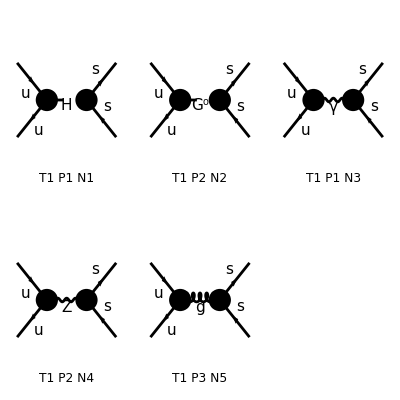

```mathematica
Process={F[3,{1}],-F[3,{1}]}-> {F[4,{2}],-F[4,{2}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},Model->"SMQCD"];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 5 Particles amplitudes

in total: 5 Particles amplitudes

FeynAmpList(({F(3,{1}),-F(3,{1})}→{F(4,{2}),-F(4,{2})})→(F(3,{1,Col1}) | p1 | MU | {(2 Charge)/3,(2 ColorCharge)/(√3)}
-F(3,{1,Col2}) | p2 | MU | {-(2 Charge)/3,-(2 ColorCharge)/(√3)})→(F(4,{2,Col3}) | k1 | MS | {-Charge/3,(2 ColorCharge)/(√3)}
-F(4,{2,Col4}) | k2 | MS | {Charge/3,-(2 ColorCharge)/(√3)}),Model→{SMQCD},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],-v̄(p2,MU).(-(ⅈ EL MU IndexDelta(Col1,Col2) om_-)/(2 MW SW)-(ⅈ EL MU IndexDelta(Col1,Col2) om_+)/(2 MW SW)).u(p1,MU) ū(k1,MS).(-(ⅈ EL MS IndexDelta(Col3,Col4) om_-)/(2 MW SW)-(ⅈ EL MS IndexDelta(Col3,Col4) om_+)/(2 MW SW)).v(k2,MS) 1/((k1+k2)^2-MH2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==1,Particles==2,Number==2),Integral[],-v̄(p2,MU).((EL MU IndexDelta(Col1,Col2) om_-)/(2 MW SW)-(EL MU IndexDelta(Col1,Col2) om_+)/(2 MW SW)).u(p1,MU) ū(k1,MS).((EL MS IndexDelta(Col3,Col4) om_+)/(2 MW SW)-(EL MS IndexDelta(Col3,Col4) om_-)/(2 MW SW)).v(k2,MS) 1/((k1+k2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==3),Integral[],v̄(p2,MU).(-2/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_--2/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_+).u(p1,MU) ū(k1,MS).(1/3 ⅈ EL IndexDelta(Col3,Col4) ga(Lor2).om_-+1/3 ⅈ EL IndexDelta(Col3,Col4) ga(Lor2).om_+).v(k2,MS) g(Lor1,Lor2) 1/(k1+k2)^2 SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==4),Integral[],v̄(p2,MU).((ⅈ EL (1/2-(2 SW2)/3) IndexDelta(Col1,Col2) ga(Lor1).om_-)/(CW SW)-(2 ⅈ EL SW IndexDelta(Col1,Col2) ga(Lor1).om_+)/(3 CW)).u(p1,MU) ū(k1,MS).((ⅈ EL (SW2/3-1/2) IndexDelta(Col3,Col4) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW IndexDelta(Col3,Col4) ga(Lor2).om_+)/(3 CW)).v(k2,MS) g(Lor1,Lor2) 1/((k1+k2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==3,Number==5),Integral[],v̄(p2,MU).(-ⅈ GS ga(Lor1).om_- SUNT(Glu5,Col2,Col1)-ⅈ GS ga(Lor1).om_+ SUNT(Glu5,Col2,Col1)).u(p1,MU) ū(k1,MS).(-ⅈ GS ga(Lor2).om_- SUNT(Glu5,Col3,Col4)-ⅈ GS ga(Lor2).om_+ SUNT(Glu5,Col3,Col4)).v(k2,MS) g(Lor1,Lor2) 1/(k1+k2)^2 SumOver(Glu5,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 64 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/avasquez/fc-pol-1.frm

running FORM...

ok

1/(36 CW2^2 MW2^2 SW2^2)π^2 (64 CW2^2 MW2^2 SW2^2 (2 Alfa2+9 Alfas2) (Den(S,0))^2 (2 MS2^2+2 MS2 (2 MU2+S-T-U)+2 MU2^2+2 MU2 (S-T-U)+T^2+U^2)+Alfa2 (81 CW2^2 MS2 MU2 (4 MS2-S) (4 MU2-S) (Den(S,MH2))^2+(Den(S,MZ2))^2 (81 CW2^2 MS2 MU2 S^2-162 CW2 MS2 MU2 MW2 (2 MS2+2 MU2-T-U)+MW2^2 (MS2^2 (256 SW2^4-576 SW2^3+648 SW2^2-324 SW2+81)+2 MS2 (MU2 (256 SW2^4-576 SW2^3+288 SW2^2+81)+2 S (64 SW2^3-144 SW2^2+90 SW2-27) SW2-128 SW2^4 T-128 SW2^4 U+288 SW2^3 T+288 SW2^3 U-180 SW2^2 T-468 SW2^2 U+324 SW2 U-81 U)+MU2^2 (256 SW2^4-576 SW2^3+648 SW2^2-324 SW2+81)+2 MU2 (4 S (32 SW2^3-72 SW2^2+72 SW2-27) SW2-128 SW2^4 (T+U)+288 SW2^3 (T+U)-36 SW2^2 (5 T+13 U)+324 SW2 U-81 U)+128 SW2^4 T^2+128 SW2^4 U^2-288 SW2^3 T^2-288 SW2^3 U^2+180 SW2^2 T^2+468 SW2^2 U^2-324 SW2 U^2+81 U^2))-18 CW2 MS2 MU2 MW2 (32 SW2^2-36 SW2+9) (T-U) Den(S,MH2) Den(S,MZ2))-16 Alfa2 CW2 MW2 SW2 Den(S,0) (36 CW2 MS2 MU2 (T-U) Den(S,MH2)-MW2 Den(S,MZ2) (MS2^2 (32 SW2^2-36 SW2+9)+MS2 (2 MU2 (32 SW2^2-36 SW2+9)+S (32 SW2^2-36 SW2+9)-32 SW2^2 T-32 SW2^2 U+36 SW2 T+36 SW2 U-18 U)+MU2^2 (32 SW2^2-36 SW2+9)+MU2 (S (32 SW2^2-36 SW2+9)-32 SW2^2 (T+U)+36 SW2 (T+U)-18 U)+16 SW2^2 T^2+16 SW2^2 U^2-18 SW2 T^2-18 SW2 U^2+9 U^2)))

```mathematica
resFCuuss=square1//.{Alfa2->(ee^2/(4π))^2,Alfas2->(gs^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),MS2->0,MU2->0}//FullSimplify[#,S+T+U==0]&
```

1/576 ((ee^4 (4 (32 sw^4-72 sw^2+45) sw^4 T^2+(4 (32 sw^6-72 sw^4+117 sw^2-81) sw^2+81) U^2))/(cw^4 sw^4 (MZ2+T+U)^2)-(16 ee^4 (2 (8 sw^2-9) sw^2 (T^2+U^2)+9 U^2))/(cw^2 S sw^2 (MZ2+T+U))+(64 (2 ee^4+9 gs^4) (T^2+U^2))/S^2)

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARuuss=Get["resANATARuuss.m"];
```

```mathematica
FullSimplify[resANATARuuss- 16 resFCuuss,{S+T+U==0,cw^2+sw^2==1}]
```

0

## tt -> tt

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
Atttt=GenerateAmplitude[{t,tbar}->{t,tbar},OutputName->"tttt",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tttt.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tttt/tttt_0

Computing amplitudes...

A total of 10 diagrams have been generated for the process {t, tbar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{t(p1),tbar(p2)}→{t(p3),tbar(p4)}},Total→10,Name→tttt,LoopOrder→0,Kinematics→{p1^2→MT^2,p1.p1→MT^2,1/(p1.p1)→1/MT^2,p2^2→MT^2,p2.p2→MT^2,1/(p2.p2)→1/MT^2,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→1/2 (S-2 MT^2),p1.p3→1/2 (2 MT^2-T),p2.p3→1/2 (2 MT^2-U),1/(p1.p2)→2/(S-2 MT^2),1/(p1.p3)→2/(2 MT^2-T),1/(p2.p3)→2/(2 MT^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→1/4 ⅈ Den(-p1-p2,MZ) ((GC47+GC49) 𝕀_Spin2Spin4+(GC47-GC49) (γ^5)_(Spin2 Spin4)) ((GC47+GC49) 𝕀_Spin3Spin1+(GC47-GC49) (γ^5)_(Spin3 Spin1)) u_Spin1^Colour3(p1,MT) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT) (v̄)_Spin3^Colour3(p2,MT),DiagramID(2)→-ⅈ GC48^2 Den(-p1-p2,MH) 𝕀_Spin2Spin4 𝕀_Spin3Spin1 u_Spin1^Colour3(p1,MT) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT) (v̄)_Spin3^Colour3(p2,MT),DiagramID(3)→ⅈ GC2^2 Den(-p1-p2,0) (γ^iLor2)_(Spin2 Spin4) (γ^iLor2)_(Spin3 Spin1) u_Spin1^Colour3(p1,MT) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT) (v̄)_Spin3^Colour3(p2,MT),DiagramID(4)→1/4 ⅈ Den(-p1-p2,MZ) ((GC26+5 GC33) (γ^iLor2)_(Spin2 Spin4)-(GC26-3 GC33) (γ^iLor2 γ^5)_(Spin2 Spin4)) ((GC26+5 GC33) (γ^iLor2)_(Spin3 Spin1)-(GC26-3 GC33) (γ^iLor2 γ^5)_(Spin3 Spin1)) u_Spin1^Colour3(p1,MT) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT) (v̄)_Spin3^Colour3(p2,MT),DiagramID(5)→ⅈ GC10^2 Den(-p1-p2,0) (γ^iLor2)_(Spin2 Spin4) (γ^iLor2)_(Spin3 Spin1) u_Spin1^Colour1(p1,MT) (ū)_Spin2^Colour2(p3,MT) v_Spin4^Colour4(p4,MT) (v̄)_Spin3^Colour3(p2,MT) T_Colour2Colour4^iGluon2 T_Colour3Colour1^iGluon2,DiagramID(6)→-1/4 ⅈ Den(p3-p1,MZ) ((GC47+GC49) 𝕀_Spin2Spin1+(GC47-GC49) (γ^5)_(Spin2 Spin1)) ((GC47+GC49) 𝕀_Spin3Spin4+(GC47-GC49) (γ^5)_(Spin3 Spin4)) u_Spin1^Colour2(p1,MT) (ū)_Spin2^Colour2(p3,MT) v_Spin4^Colour4(p4,MT) (v̄)_Spin3^Colour4(p2,MT),DiagramID(7)→ⅈ GC48^2 Den(p3-p1,MH) 𝕀_Spin2Spin1 𝕀_Spin3Spin4 u_Spin1^Colour2(p1,MT) (ū)_Spin2^Colour2(p3,MT) v_Spin4^Colour4(p4,MT) (v̄)_Spin3^Colour4(p2,MT),DiagramID(8)→-ⅈ GC2^2 Den(p3-p1,0) (γ^iLor2)_(Spin2 Spin1) (γ^iLor2)_(Spin3 Spin4) u_Spin1^Colour2(p1,MT) (ū)_Spin2^Colour2(p3,MT) v_Spin4^Colour4(p4,MT) (v̄)_Spin3^Colour4(p2,MT),DiagramID(9)→-1/4 ⅈ Den(p3-p1,MZ) ((GC26+5 GC33) (γ^iLor2)_(Spin2 Spin1)-(GC26-3 GC33) (γ^iLor2 γ^5)_(Spin2 Spin1)) ((GC26+5 GC33) (γ^iLor2)_(Spin3 Spin4)-(GC26-3 GC33) (γ^iLor2 γ^5)_(Spin3 Spin4)) u_Spin1^Colour2(p1,MT) (ū)_Spin2^Colour2(p3,MT) v_Spin4^Colour4(p4,MT) (v̄)_Spin3^Colour4(p2,MT),DiagramID(10)→-ⅈ GC10^2 Den(p3-p1,0) (γ^iLor2)_(Spin2 Spin1) (γ^iLor2)_(Spin3 Spin4) u_Spin1^Colour1(p1,MT) (ū)_Spin2^Colour2(p3,MT) v_Spin4^Colour4(p4,MT) (v̄)_Spin3^Colour3(p2,MT) T_Colour2Colour1^iGluon2 T_Colour3Colour4^iGluon2}|>

```mathematica
AttttC=GenerateAmplitudeConjugate[{t,tbar}->{t,tbar},OutputName->"tttt",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tttt.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tttt/tttt_0

Computing amplitudes...

A total of 10 diagrams have been generated for the process {t, tbar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{t(p1),tbar(p2)}→{t(p3),tbar(p4)}},Total→10,Name→tttt,LoopOrder→0,Kinematics→{p1^2→MT^2,p1.p1→MT^2,1/(p1.p1)→1/MT^2,p2^2→MT^2,p2.p2→MT^2,1/(p2.p2)→1/MT^2,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→1/2 (S-2 MT^2),p1.p3→1/2 (2 MT^2-T),p2.p3→1/2 (2 MT^2-U),1/(p1.p2)→2/(S-2 MT^2),1/(p1.p3)→2/(2 MT^2-T),1/(p2.p3)→2/(2 MT^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-1/4 ⅈ Den(-p1-p2,MZ) ((GC47+GC49) 𝕀_SpinC1SpinC3+(GC49-GC47) (γ^5)_(SpinC1 SpinC3)) ((GC47+GC49) 𝕀_SpinC4SpinC2+(GC49-GC47) (γ^5)_(SpinC4 SpinC2)) ((ū)^†)_SpinC1^ColourC3(p1,MT) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) (v^†)_SpinC3^ColourC3(p2,MT),DiagramID(2)→ⅈ GC48^2 Den(-p1-p2,MH) 𝕀_SpinC1SpinC3 𝕀_SpinC4SpinC2 ((ū)^†)_SpinC1^ColourC3(p1,MT) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) (v^†)_SpinC3^ColourC3(p2,MT),DiagramID(3)→-ⅈ GC2^2 Den(-p1-p2,0) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC4 SpinC2) ((ū)^†)_SpinC1^ColourC3(p1,MT) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) (v^†)_SpinC3^ColourC3(p2,MT),DiagramID(4)→-1/4 ⅈ Den(-p1-p2,MZ) ((GC26+5 GC33) (γ^iLorC2)_(SpinC1 SpinC3)+(GC26-3 GC33) (γ^5 γ^iLorC2)_(SpinC1 SpinC3)) ((GC26+5 GC33) (γ^iLorC2)_(SpinC4 SpinC2)+(GC26-3 GC33) (γ^5 γ^iLorC2)_(SpinC4 SpinC2)) ((ū)^†)_SpinC1^ColourC3(p1,MT) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) (v^†)_SpinC3^ColourC3(p2,MT),DiagramID(5)→-ⅈ GC10^2 Den(-p1-p2,0) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC4 SpinC2) ((ū)^†)_SpinC1^ColourC1(p1,MT) (u^†)_SpinC2^ColourC2(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) (v^†)_SpinC3^ColourC3(p2,MT) T_ColourC1ColourC3^iGluonC2 T_ColourC4ColourC2^iGluonC2,DiagramID(6)→1/4 ⅈ Den(p3-p1,MZ) ((GC47+GC49) 𝕀_SpinC1SpinC2+(GC49-GC47) (γ^5)_(SpinC1 SpinC2)) ((GC47+GC49) 𝕀_SpinC4SpinC3+(GC49-GC47) (γ^5)_(SpinC4 SpinC3)) ((ū)^†)_SpinC1^ColourC2(p1,MT) (u^†)_SpinC2^ColourC2(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) (v^†)_SpinC3^ColourC4(p2,MT),DiagramID(7)→-ⅈ GC48^2 Den(p3-p1,MH) 𝕀_SpinC1SpinC2 𝕀_SpinC4SpinC3 ((ū)^†)_SpinC1^ColourC2(p1,MT) (u^†)_SpinC2^ColourC2(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) (v^†)_SpinC3^ColourC4(p2,MT),DiagramID(8)→ⅈ GC2^2 Den(p3-p1,0) (γ^iLorC2)_(SpinC1 SpinC2) (γ^iLorC2)_(SpinC4 SpinC3) ((ū)^†)_SpinC1^ColourC2(p1,MT) (u^†)_SpinC2^ColourC2(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) (v^†)_SpinC3^ColourC4(p2,MT),DiagramID(9)→1/4 ⅈ Den(p3-p1,MZ) ((GC26+5 GC33) (γ^iLorC2)_(SpinC1 SpinC2)+(GC26-3 GC33) (γ^5 γ^iLorC2)_(SpinC1 SpinC2)) ((GC26+5 GC33) (γ^iLorC2)_(SpinC4 SpinC3)+(GC26-3 GC33) (γ^5 γ^iLorC2)_(SpinC4 SpinC3)) ((ū)^†)_SpinC1^ColourC2(p1,MT) (u^†)_SpinC2^ColourC2(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) (v^†)_SpinC3^ColourC4(p2,MT),DiagramID(10)→ⅈ GC10^2 Den(p3-p1,0) (γ^iLorC2)_(SpinC1 SpinC2) (γ^iLorC2)_(SpinC4 SpinC3) ((ū)^†)_SpinC1^ColourC1(p1,MT) (u^†)_SpinC2^ColourC2(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT) (v^†)_SpinC3^ColourC3(p2,MT) T_ColourC1ColourC2^iGluonC2 T_ColourC4ColourC3^iGluonC2}|>

```mathematica
AmpSQtttt=GenerateAmplitudeSquare[Atttt,AttttC,Dimension->4,CasimirValues->True]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{t(p1),tbar(p2)}→{t(p3),tbar(p4)}},Name→tttt,LoopOrder→0,Kinematics→{p1^2→MT^2,p1.p1→MT^2,1/(p1.p1)→1/MT^2,p2^2→MT^2,p2.p2→MT^2,1/(p2.p2)→1/MT^2,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→1/2 (S-2 MT^2),p1.p3→1/2 (2 MT^2-T),p2.p3→1/2 (2 MT^2-U),1/(p1.p2)→2/(S-2 MT^2),1/(p1.p3)→2/(2 MT^2-T),1/(p2.p3)→2/(2 MT^2-U),p4→p1+p2-p3},Amplitudes→(144 S (Den(-p1-p2,MZ))^2 MT^6)/vev^4+(144 S (Den(p3-p1,MH))^2 MT^6)/vev^4+(144 U (Den(p3-p1,MH))^2 MT^6)/vev^4+(144 T (Den(p3-p1,MZ))^2 MT^6)/vev^4+(48 S Den(-p1-p2,MZ) Den(p3-p1,MH) MT^6)/vev^4+(36 (4 MT^2-S) (T+U) (Den(-p1-p2,MH))^2 MT^4)/vev^4+26 ee^4 (Den(-p1-p2,MZ))^2 MT^4-(25 ee^4 sw2^2 (Den(-p1-p2,MZ))^2 MT^4)/cw^4-(20 ee^4 sw2 (Den(-p1-p2,MZ))^2 MT^4)/cw^2+(12 cw^2 ee^4 (Den(-p1-p2,MZ))^2 MT^4)/sw2-(9 cw^4 ee^4 (Den(-p1-p2,MZ))^2 MT^4)/sw2^2-(36 ee^2 S (Den(-p1-p2,MZ))^2 MT^4)/vev^2-(18 ee^2 S sw2 (Den(-p1-p2,MZ))^2 MT^4)/(cw^2 vev^2)-(18 cw^2 ee^2 S (Den(-p1-p2,MZ))^2 MT^4)/(sw2 vev^2)-(36 S T (Den(-p1-p2,MZ))^2 MT^4)/vev^4-(36 S U (Den(-p1-p2,MZ))^2 MT^4)/vev^4-(36 S T (Den(p3-p1,MH))^2 MT^4)/vev^4-(36 T U (Den(p3-p1,MH))^2 MT^4)/vev^4+26 ee^4 (Den(p3-p1,MZ))^2 MT^4-(25 ee^4 sw2^2 (Den(p3-p1,MZ))^2 MT^4)/cw^4-(20 ee^4 sw2 (Den(p3-p1,MZ))^2 MT^4)/cw^2+(12 cw^2 ee^4 (Den(p3-p1,MZ))^2 MT^4)/sw2-(9 cw^4 ee^4 (Den(p3-p1,MZ))^2 MT^4)/sw2^2-(36 ee^2 T (Den(p3-p1,MZ))^2 MT^4)/vev^2-(18 ee^2 sw2 T (Den(p3-p1,MZ))^2 MT^4)/(cw^2 vev^2)-(18 cw^2 ee^2 T (Den(p3-p1,MZ))^2 MT^4)/(sw2 vev^2)-(36 S T (Den(p3-p1,MZ))^2 MT^4)/vev^4-(36 T U (Den(p3-p1,MZ))^2 MT^4)/vev^4+(64 ee^2 S Den(-p1-p2,MZ) Den(p3-p1,0) MT^4)/(3 vev^2)+(64 gs^2 S Den(-p1-p2,MZ) Den(p3-p1,0) MT^4)/vev^2-(36 ee^2 S Den(-p1-p2,MZ) Den(p3-p1,MH) MT^4)/vev^2+(22 ee^2 S sw2 Den(-p1-p2,MZ) Den(p3-p1,MH) MT^4)/(cw^2 vev^2)-(28 ee^2 U Den(-p1-p2,MZ) Den(p3-p1,MH) MT^4)/vev^2-(2 ee^2 sw2 U Den(-p1-p2,MZ) Den(p3-p1,MH) MT^4)/(3 cw^2 vev^2)-(6 cw^2 ee^2 U Den(-p1-p2,MZ) Den(p3-p1,MH) MT^4)/(sw2 vev^2)+(6 cw^2 ee^2 S Den(-p1-p2,MZ) Den(p3-p1,MH) MT^4)/(sw2 vev^2)-(12 S T Den(-p1-p2,MZ) Den(p3-p1,MH) MT^4)/vev^4+(128 ee^2 S Den(p3-p1,0) Den(p3-p1,MH) MT^4)/vev^2-(128 ee^2 U Den(p3-p1,0) Den(p3-p1,MH) MT^4)/vev^2+52/3 ee^4 Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4-(50 ee^4 sw2^2 Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/(3 cw^4)-(40 ee^4 sw2 Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/(3 cw^2)+(8 cw^2 ee^4 Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/sw2-(6 cw^4 ee^4 Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/sw2^2-(28 ee^2 S Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/vev^2-(2 ee^2 S sw2 Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/(3 cw^2 vev^2)-(28 ee^2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/vev^2-(2 ee^2 sw2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/(3 cw^2 vev^2)-(6 cw^2 ee^2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/(sw2 vev^2)-(6 cw^2 ee^2 S Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/(sw2 vev^2)+(12 S T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^4)/vev^4-(60 ee^2 S Den(p3-p1,MH) Den(p3-p1,MZ) MT^4)/vev^2+(50 ee^2 S sw2 Den(p3-p1,MH) Den(p3-p1,MZ) MT^4)/(cw^2 vev^2)+(60 ee^2 U Den(p3-p1,MH) Den(p3-p1,MZ) MT^4)/vev^2-(50 ee^2 sw2 U Den(p3-p1,MH) Den(p3-p1,MZ) MT^4)/(cw^2 vev^2)-(18 cw^2 ee^2 U Den(p3-p1,MH) Den(p3-p1,MZ) MT^4)/(sw2 vev^2)+(18 cw^2 ee^2 S Den(p3-p1,MH) Den(p3-p1,MZ) MT^4)/(sw2 vev^2)+(119 ee^4 S sw2^2 (Den(-p1-p2,MZ))^2 MT^2)/(6 cw^4)+25 ee^4 S (Den(-p1-p2,MZ))^2 MT^2-(24 ee^4 S sw2 (Den(-p1-p2,MZ))^2 MT^2)/cw^2+13 ee^4 T (Den(-p1-p2,MZ))^2 MT^2+(221 ee^4 sw2^2 T (Den(-p1-p2,MZ))^2 MT^2)/(18 cw^4)+(4 ee^4 sw2 T (Den(-p1-p2,MZ))^2 MT^2)/(3 cw^2)+(9 cw^4 ee^4 T (Den(-p1-p2,MZ))^2 MT^2)/(2 sw2^2)+13 ee^4 U (Den(-p1-p2,MZ))^2 MT^2+(221 ee^4 sw2^2 U (Den(-p1-p2,MZ))^2 MT^2)/(18 cw^4)+(4 ee^4 sw2 U (Den(-p1-p2,MZ))^2 MT^2)/(3 cw^2)+(9 cw^4 ee^4 U (Den(-p1-p2,MZ))^2 MT^2)/(2 sw2^2)-(12 cw^2 ee^4 S (Den(-p1-p2,MZ))^2 MT^2)/sw2+(9 cw^4 ee^4 S (Den(-p1-p2,MZ))^2 MT^2)/(2 sw2^2)+256/9 ee^4 S (Den(p3-p1,0))^2 MT^2+32 gs^4 S (Den(p3-p1,0))^2 MT^2+256/3 ee^4 T (Den(p3-p1,0))^2 MT^2+96 gs^4 T (Den(p3-p1,0))^2 MT^2+256/9 ee^4 U (Den(p3-p1,0))^2 MT^2+32 gs^4 U (Den(p3-p1,0))^2 MT^2+(221 ee^4 S sw2^2 (Den(p3-p1,MZ))^2 MT^2)/(18 cw^4)+13 ee^4 S (Den(p3-p1,MZ))^2 MT^2+(4 ee^4 S sw2 (Den(p3-p1,MZ))^2 MT^2)/(3 cw^2)+25 ee^4 T (Den(p3-p1,MZ))^2 MT^2+(119 ee^4 sw2^2 T (Den(p3-p1,MZ))^2 MT^2)/(6 cw^4)-(24 ee^4 sw2 T (Den(p3-p1,MZ))^2 MT^2)/cw^2-(12 cw^2 ee^4 T (Den(p3-p1,MZ))^2 MT^2)/sw2+(9 cw^4 ee^4 T (Den(p3-p1,MZ))^2 MT^2)/(2 sw2^2)+13 ee^4 U (Den(p3-p1,MZ))^2 MT^2+(221 ee^4 sw2^2 U (Den(p3-p1,MZ))^2 MT^2)/(18 cw^4)+(4 ee^4 sw2 U (Den(p3-p1,MZ))^2 MT^2)/(3 cw^2)+(9 cw^4 ee^4 U (Den(p3-p1,MZ))^2 MT^2)/(2 sw2^2)+(9 cw^4 ee^4 S (Den(p3-p1,MZ))^2 MT^2)/(2 sw2^2)-16 ee^4 S Den(-p1-p2,MZ) Den(p3-p1,0) MT^2-48 ee^2 gs^2 S Den(-p1-p2,MZ) Den(p3-p1,0) MT^2+(88 ee^4 S sw2 Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/(9 cw^2)+(88 ee^2 gs^2 S sw2 Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/(3 cw^2)-16/3 ee^4 T Den(-p1-p2,MZ) Den(p3-p1,0) MT^2-16 ee^2 gs^2 T Den(-p1-p2,MZ) Den(p3-p1,0) MT^2+(136 ee^4 sw2 T Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/(9 cw^2)+(136 ee^2 gs^2 sw2 T Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/(3 cw^2)+(8 cw^2 ee^4 T Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/sw2+(24 cw^2 ee^2 gs^2 T Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/sw2+112/9 ee^4 U Den(-p1-p2,MZ) Den(p3-p1,0) MT^2+112/3 ee^2 gs^2 U Den(-p1-p2,MZ) Den(p3-p1,0) MT^2+(8 ee^4 sw2 U Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/(27 cw^2)+(8 ee^2 gs^2 sw2 U Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/(9 cw^2)+(8 cw^2 ee^4 U Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/(3 sw2)+(8 cw^2 ee^2 gs^2 U Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/sw2+(8 cw^2 ee^4 S Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/(3 sw2)+(8 cw^2 ee^2 gs^2 S Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/sw2-(32 ee^2 S T Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/(3 vev^2)-(32 gs^2 S T Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/vev^2-(32 ee^2 S U Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/(3 vev^2)-(32 gs^2 S U Den(-p1-p2,MZ) Den(p3-p1,0) MT^2)/vev^2+(8 ee^2 S T Den(-p1-p2,MZ) Den(p3-p1,MH) MT^2)/vev^2-(8 ee^2 S sw2 T Den(-p1-p2,MZ) Den(p3-p1,MH) MT^2)/(3 cw^2 vev^2)+(8 ee^2 T U Den(-p1-p2,MZ) Den(p3-p1,MH) MT^2)/vev^2-(8 ee^2 sw2 T U Den(-p1-p2,MZ) Den(p3-p1,MH) MT^2)/(3 cw^2 vev^2)+(91 ee^4 S sw2^2 Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/(9 cw^4)+22/3 ee^4 S Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2-(4 ee^4 S sw2 Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/cw^2+22/3 ee^4 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2+(91 ee^4 sw2^2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/(9 cw^4)-(4 ee^4 sw2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/cw^2-(4 cw^2 ee^4 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/sw2+(3 cw^4 ee^4 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/sw2^2-22/3 ee^4 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2+(173 ee^4 sw2^2 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/(27 cw^4)+(104 ee^4 sw2 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/(9 cw^2)+(3 cw^4 ee^4 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/sw2^2-(4 cw^2 ee^4 S Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/sw2+(3 cw^4 ee^4 S Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/sw2^2+(16 ee^2 S T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/vev^2-(16 ee^2 S sw2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/(3 cw^2 vev^2)+(8 ee^2 S U Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/vev^2-(8 ee^2 S sw2 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/(3 cw^2 vev^2)+(8 ee^2 T U Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/vev^2-(8 ee^2 sw2 T U Den(-p1-p2,MZ) Den(p3-p1,MZ) MT^2)/(3 cw^2 vev^2)-80/3 ee^4 S Den(p3-p1,0) Den(p3-p1,MZ) MT^2+(200 ee^4 S sw2 Den(p3-p1,0) Den(p3-p1,MZ) MT^2)/(9 cw^2)-80 ee^4 T Den(p3-p1,0) Den(p3-p1,MZ) MT^2+(200 ee^4 sw2 T Den(p3-p1,0) Den(p3-p1,MZ) MT^2)/(3 cw^2)+(24 cw^2 ee^4 T Den(p3-p1,0) Den(p3-p1,MZ) MT^2)/sw2-80/3 ee^4 U Den(p3-p1,0) Den(p3-p1,MZ) MT^2+(200 ee^4 sw2 U Den(p3-p1,0) Den(p3-p1,MZ) MT^2)/(9 cw^2)+(8 cw^2 ee^4 U Den(p3-p1,0) Den(p3-p1,MZ) MT^2)/sw2+(8 cw^2 ee^4 S Den(p3-p1,0) Den(p3-p1,MZ) MT^2)/sw2+1/(3 cw^2 sw2 vev^4)2 Den(-p1-p2,MH) (9 ee^2 MT^2 T vev^2 Den(p3-p1,MZ) cw^4-9 ee^2 MT^2 U vev^2 Den(p3-p1,MZ) cw^4+16 (ee^2+3 gs^2) sw2 (2 MT^2 (3 T+U)-S (T+U)) vev^2 Den(p3-p1,0) cw^2+18 MT^2 S sw2 T Den(p3-p1,MH) cw^2-72 MT^4 sw2 U Den(p3-p1,MH) cw^2-54 ee^2 MT^2 sw2 T vev^2 Den(p3-p1,MZ) cw^2+12 ee^2 S sw2 T vev^2 Den(p3-p1,MZ) cw^2-42 ee^2 MT^2 sw2 U vev^2 Den(p3-p1,MZ) cw^2+12 ee^2 S sw2 U vev^2 Den(p3-p1,MZ) cw^2+72 MT^4 sw2 T Den(p3-p1,MZ) cw^2-18 MT^2 S sw2 T Den(p3-p1,MZ) cw^2+3 ee^2 MT^2 (3 cw^2-5 sw2)^2 (T-U) vev^2 Den(-p1-p2,MZ)+33 ee^2 MT^2 sw2^2 T vev^2 Den(p3-p1,MZ)-4 ee^2 S sw2^2 T vev^2 Den(p3-p1,MZ)-ee^2 MT^2 sw2^2 U vev^2 Den(p3-p1,MZ)-4 ee^2 S sw2^2 U vev^2 Den(p3-p1,MZ)) MT^2-16/9 (8 ee^4+9 gs^4) (-2 (3 S+T+U) MT^2+2 T U+S (T+U)) (Den(-p1-p2,0))^2-(8 ee^4 S sw2^2 T (Den(-p1-p2,MZ))^2)/(9 cw^4)-8 ee^4 S T (Den(-p1-p2,MZ))^2+(16 ee^4 S sw2 T (Den(-p1-p2,MZ))^2)/(3 cw^2)-(257 ee^4 S sw2^2 U (Den(-p1-p2,MZ))^2)/(36 cw^4)-3/2 ee^4 S U (Den(-p1-p2,MZ))^2+(ee^4 S sw2 U (Den(-p1-p2,MZ))^2)/(3 cw^2)-19/2 ee^4 T U (Den(-p1-p2,MZ))^2-(289 ee^4 sw2^2 T U (Den(-p1-p2,MZ))^2)/(36 cw^4)+(17 ee^4 sw2 T U (Den(-p1-p2,MZ))^2)/(3 cw^2)+(3 cw^2 ee^4 T U (Den(-p1-p2,MZ))^2)/sw2-(9 cw^4 ee^4 T U (Den(-p1-p2,MZ))^2)/(4 sw2^2)+(3 cw^2 ee^4 S U (Den(-p1-p2,MZ))^2)/sw2-(9 cw^4 ee^4 S U (Den(-p1-p2,MZ))^2)/(4 sw2^2)-128/9 ee^4 S T (Den(p3-p1,0))^2-16 gs^4 S T (Den(p3-p1,0))^2-256/9 ee^4 S U (Den(p3-p1,0))^2-32 gs^4 S U (Den(p3-p1,0))^2-128/9 ee^4 T U (Den(p3-p1,0))^2-16 gs^4 T U (Den(p3-p1,0))^2-(8 ee^4 S sw2^2 T (Den(p3-p1,MZ))^2)/(9 cw^4)-8 ee^4 S T (Den(p3-p1,MZ))^2+(16 ee^4 S sw2 T (Den(p3-p1,MZ))^2)/(3 cw^2)-(289 ee^4 S sw2^2 U (Den(p3-p1,MZ))^2)/(36 cw^4)-19/2 ee^4 S U (Den(p3-p1,MZ))^2+(17 ee^4 S sw2 U (Den(p3-p1,MZ))^2)/(3 cw^2)-3/2 ee^4 T U (Den(p3-p1,MZ))^2-(257 ee^4 sw2^2 T U (Den(p3-p1,MZ))^2)/(36 cw^4)+(ee^4 sw2 T U (Den(p3-p1,MZ))^2)/(3 cw^2)+(3 cw^2 ee^4 T U (Den(p3-p1,MZ))^2)/sw2-(9 cw^4 ee^4 T U (Den(p3-p1,MZ))^2)/(4 sw2^2)+(3 cw^2 ee^4 S U (Den(p3-p1,MZ))^2)/sw2-(9 cw^4 ee^4 S U (Den(p3-p1,MZ))^2)/(4 sw2^2)+16/9 ee^4 S U Den(-p1-p2,MZ) Den(p3-p1,0)+16/3 ee^2 gs^2 S U Den(-p1-p2,MZ) Den(p3-p1,0)-(136 ee^4 S sw2 U Den(-p1-p2,MZ) Den(p3-p1,0))/(27 cw^2)-(136 ee^2 gs^2 S sw2 U Den(-p1-p2,MZ) Den(p3-p1,0))/(9 cw^2)+16/9 ee^4 T U Den(-p1-p2,MZ) Den(p3-p1,0)+16/3 ee^2 gs^2 T U Den(-p1-p2,MZ) Den(p3-p1,0)-(136 ee^4 sw2 T U Den(-p1-p2,MZ) Den(p3-p1,0))/(27 cw^2)-(136 ee^2 gs^2 sw2 T U Den(-p1-p2,MZ) Den(p3-p1,0))/(9 cw^2)-(8 cw^2 ee^4 T U Den(-p1-p2,MZ) Den(p3-p1,0))/(3 sw2)-(8 cw^2 ee^2 gs^2 T U Den(-p1-p2,MZ) Den(p3-p1,0))/sw2-(8 cw^2 ee^4 S U Den(-p1-p2,MZ) Den(p3-p1,0))/(3 sw2)-(8 cw^2 ee^2 gs^2 S U Den(-p1-p2,MZ) Den(p3-p1,0))/sw2-(257 ee^4 S sw2^2 U Den(-p1-p2,MZ) Den(p3-p1,MZ))/(54 cw^4)-ee^4 S U Den(-p1-p2,MZ) Den(p3-p1,MZ)+(2 ee^4 S sw2 U Den(-p1-p2,MZ) Den(p3-p1,MZ))/(9 cw^2)-ee^4 T U Den(-p1-p2,MZ) Den(p3-p1,MZ)-(257 ee^4 sw2^2 T U Den(-p1-p2,MZ) Den(p3-p1,MZ))/(54 cw^4)+(2 ee^4 sw2 T U Den(-p1-p2,MZ) Den(p3-p1,MZ))/(9 cw^2)+(2 cw^2 ee^4 T U Den(-p1-p2,MZ) Den(p3-p1,MZ))/sw2-(3 cw^4 ee^4 T U Den(-p1-p2,MZ) Den(p3-p1,MZ))/(2 sw2^2)+(2 cw^2 ee^4 S U Den(-p1-p2,MZ) Den(p3-p1,MZ))/sw2-(3 cw^4 ee^4 S U Den(-p1-p2,MZ) Den(p3-p1,MZ))/(2 sw2^2)+64/3 ee^4 S T Den(p3-p1,0) Den(p3-p1,MZ)-(64 ee^4 S sw2 T Den(p3-p1,0) Den(p3-p1,MZ))/(9 cw^2)+80/3 ee^4 S U Den(p3-p1,0) Den(p3-p1,MZ)-(200 ee^4 S sw2 U Den(p3-p1,0) Den(p3-p1,MZ))/(9 cw^2)+16/3 ee^4 T U Den(p3-p1,0) Den(p3-p1,MZ)-(136 ee^4 sw2 T U Den(p3-p1,0) Den(p3-p1,MZ))/(9 cw^2)-(8 cw^2 ee^4 T U Den(p3-p1,0) Den(p3-p1,MZ))/sw2-(8 cw^2 ee^4 S U Den(p3-p1,0) Den(p3-p1,MZ))/sw2+1/(27 cw^2 sw2 vev^2)8 Den(-p1-p2,0) (27 ee^4 MT^2 S vev^2 Den(p3-p1,MZ) cw^4+81 ee^2 gs^2 MT^2 S vev^2 Den(p3-p1,MZ) cw^4+9 ee^4 MT^2 T vev^2 Den(p3-p1,MZ) cw^4+27 ee^2 gs^2 MT^2 T vev^2 Den(p3-p1,MZ) cw^4+9 ee^4 MT^2 U vev^2 Den(p3-p1,MZ) cw^4+27 ee^2 gs^2 MT^2 U vev^2 Den(p3-p1,MZ) cw^4-9 ee^4 S U vev^2 Den(p3-p1,MZ) cw^4-27 ee^2 gs^2 S U vev^2 Den(p3-p1,MZ) cw^4-9 ee^4 T U vev^2 Den(p3-p1,MZ) cw^4-27 ee^2 gs^2 T U vev^2 Den(p3-p1,MZ) cw^4+432 ee^2 MT^4 sw2 (T-U) Den(-p1-p2,MH) cw^2+96 ee^4 MT^2 S sw2 vev^2 Den(p3-p1,0) cw^2-108 gs^4 MT^2 S sw2 vev^2 Den(p3-p1,0) cw^2+576 ee^2 gs^2 MT^2 S sw2 vev^2 Den(p3-p1,0) cw^2+96 ee^4 MT^2 sw2 T vev^2 Den(p3-p1,0) cw^2-108 gs^4 MT^2 sw2 T vev^2 Den(p3-p1,0) cw^2+576 ee^2 gs^2 MT^2 sw2 T vev^2 Den(p3-p1,0) cw^2-32 ee^4 MT^2 sw2 U vev^2 Den(p3-p1,0) cw^2+36 gs^4 MT^2 sw2 U vev^2 Den(p3-p1,0) cw^2-192 ee^2 gs^2 MT^2 sw2 U vev^2 Den(p3-p1,0) cw^2-32 ee^4 S sw2 U vev^2 Den(p3-p1,0) cw^2+36 gs^4 S sw2 U vev^2 Den(p3-p1,0) cw^2-192 ee^2 gs^2 S sw2 U vev^2 Den(p3-p1,0) cw^2-32 ee^4 sw2 T U vev^2 Den(p3-p1,0) cw^2+36 gs^4 sw2 T U vev^2 Den(p3-p1,0) cw^2-192 ee^2 gs^2 sw2 T U vev^2 Den(p3-p1,0) cw^2+216 ee^2 MT^4 S sw2 Den(p3-p1,MH) cw^2+648 gs^2 MT^4 S sw2 Den(p3-p1,MH) cw^2-36 ee^2 MT^2 S sw2 T Den(p3-p1,MH) cw^2-108 gs^2 MT^2 S sw2 T Den(p3-p1,MH) cw^2+72 ee^2 MT^4 sw2 U Den(p3-p1,MH) cw^2+216 gs^2 MT^4 sw2 U Den(p3-p1,MH) cw^2-36 ee^2 MT^2 sw2 T U Den(p3-p1,MH) cw^2-108 gs^2 MT^2 sw2 T U Den(p3-p1,MH) cw^2-18 ee^4 MT^2 S sw2 vev^2 Den(p3-p1,MZ) cw^2-54 ee^2 gs^2 MT^2 S sw2 vev^2 Den(p3-p1,MZ) cw^2-54 ee^4 MT^2 sw2 T vev^2 Den(p3-p1,MZ) cw^2-162 ee^2 gs^2 MT^2 sw2 T vev^2 Den(p3-p1,MZ) cw^2+42 ee^4 MT^2 sw2 U vev^2 Den(p3-p1,MZ) cw^2+126 ee^2 gs^2 MT^2 sw2 U vev^2 Den(p3-p1,MZ) cw^2+6 ee^4 S sw2 U vev^2 Den(p3-p1,MZ) cw^2+18 ee^2 gs^2 S sw2 U vev^2 Den(p3-p1,MZ) cw^2+6 ee^4 sw2 T U vev^2 Den(p3-p1,MZ) cw^2+18 ee^2 gs^2 sw2 T U vev^2 Den(p3-p1,MZ) cw^2+72 ee^2 MT^4 sw2 T Den(p3-p1,MZ) cw^2+216 gs^2 MT^4 sw2 T Den(p3-p1,MZ) cw^2-36 ee^2 MT^2 S sw2 T Den(p3-p1,MZ) cw^2-108 gs^2 MT^2 S sw2 T Den(p3-p1,MZ) cw^2-36 ee^2 MT^2 sw2 T U Den(p3-p1,MZ) cw^2-108 gs^2 MT^2 sw2 T U Den(p3-p1,MZ) cw^2+3 ee^4 (9 (MT^2 (3 S+T+U)-(S+T) U) cw^4-6 sw2 (5 (3 S+T+U) MT^2-5 T U-S (4 T+U)) cw^2+sw2^2 (25 (3 S+T+U) MT^2-8 S T-17 S U-25 T U)) vev^2 Den(-p1-p2,MZ)+51 ee^4 MT^2 S sw2^2 vev^2 Den(p3-p1,MZ)+153 ee^2 gs^2 MT^2 S sw2^2 vev^2 Den(p3-p1,MZ)+33 ee^4 MT^2 sw2^2 T vev^2 Den(p3-p1,MZ)+99 ee^2 gs^2 MT^2 sw2^2 T vev^2 Den(p3-p1,MZ)+ee^4 MT^2 sw2^2 U vev^2 Den(p3-p1,MZ)+3 ee^2 gs^2 MT^2 sw2^2 U vev^2 Den(p3-p1,MZ)-17 ee^4 S sw2^2 U vev^2 Den(p3-p1,MZ)-51 ee^2 gs^2 S sw2^2 U vev^2 Den(p3-p1,MZ)-17 ee^4 sw2^2 T U vev^2 Den(p3-p1,MZ)-51 ee^2 gs^2 sw2^2 T U vev^2 Den(p3-p1,MZ))|>

```mathematica
resANATARtttt=AmpSQtttt[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),Nc->3,-p1-p2->√S,(-p1-p2)^2->S,p1-p3->√T,p3-p1->√T,p3-p2->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2};
```

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARtttt.m",resANATARtttt];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SMQCD.mod

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 5 Particles insertions

> Top. 3: 5 Particles insertions

> Top. 4: 0 Particles insertions

in total: 10 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 5 diagrams

> Top. 2 aebf/cedf/ef.m, 5 diagrams

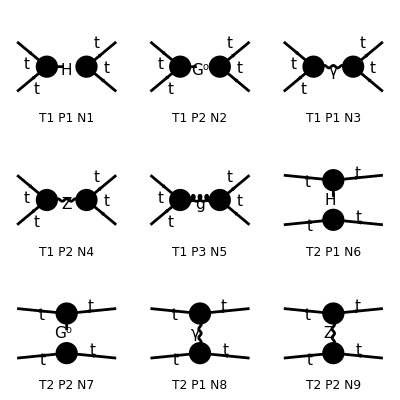

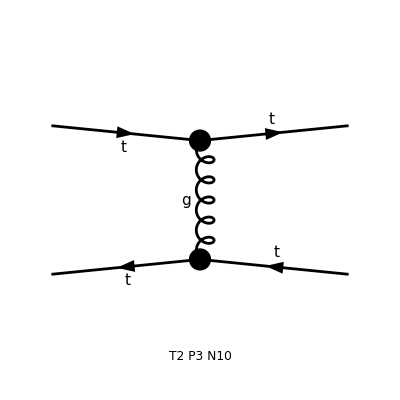

```mathematica
Process={F[3,{3}],-F[3,{3}]}-> {F[3,{3}],-F[3,{3}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles},Model->"SMQCD"];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify;
```

creating amplitudes at level(s) {Particles}

> Top. 1: 5 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 10 Particles amplitudes

FeynAmpList(({F(3,{3}),-F(3,{3})}→{F(3,{3}),-F(3,{3})})→(F(3,{3,Col1}) | p1 | MT | {(2 Charge)/3,(2 ColorCharge)/(√3)}
-F(3,{3,Col2}) | p2 | MT | {-(2 Charge)/3,-(2 ColorCharge)/(√3)})→(F(3,{3,Col3}) | k1 | MT | {(2 Charge)/3,(2 ColorCharge)/(√3)}
-F(3,{3,Col4}) | k2 | MT | {-(2 Charge)/3,-(2 ColorCharge)/(√3)}),Model→{SMQCD},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],-v̄(p2,MT).(-(ⅈ EL MT IndexDelta(Col1,Col2) om_-)/(2 MW SW)-(ⅈ EL MT IndexDelta(Col1,Col2) om_+)/(2 MW SW)).u(p1,MT) ū(k1,MT).(-(ⅈ EL MT IndexDelta(Col3,Col4) om_-)/(2 MW SW)-(ⅈ EL MT IndexDelta(Col3,Col4) om_+)/(2 MW SW)).v(k2,MT) 1/((k1+k2)^2-MH2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==1,Particles==2,Number==2),Integral[],-v̄(p2,MT).((EL MT IndexDelta(Col1,Col2) om_-)/(2 MW SW)-(EL MT IndexDelta(Col1,Col2) om_+)/(2 MW SW)).u(p1,MT) ū(k1,MT).((EL MT IndexDelta(Col3,Col4) om_-)/(2 MW SW)-(EL MT IndexDelta(Col3,Col4) om_+)/(2 MW SW)).v(k2,MT) 1/((k1+k2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==3),Integral[],v̄(p2,MT).(-2/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_--2/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_+).u(p1,MT) ū(k1,MT).(-2/3 ⅈ EL IndexDelta(Col3,Col4) ga(Lor2).om_--2/3 ⅈ EL IndexDelta(Col3,Col4) ga(Lor2).om_+).v(k2,MT) g(Lor1,Lor2) 1/(k1+k2)^2 SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==4),Integral[],v̄(p2,MT).((ⅈ EL (1/2-(2 SW2)/3) IndexDelta(Col1,Col2) ga(Lor1).om_-)/(CW SW)-(2 ⅈ EL SW IndexDelta(Col1,Col2) ga(Lor1).om_+)/(3 CW)).u(p1,MT) ū(k1,MT).((ⅈ EL (1/2-(2 SW2)/3) IndexDelta(Col3,Col4) ga(Lor2).om_-)/(CW SW)-(2 ⅈ EL SW IndexDelta(Col3,Col4) ga(Lor2).om_+)/(3 CW)).v(k2,MT) g(Lor1,Lor2) 1/((k1+k2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==3,Number==5),Integral[],v̄(p2,MT).(-ⅈ GS ga(Lor1).om_- SUNT(Glu5,Col2,Col1)-ⅈ GS ga(Lor1).om_+ SUNT(Glu5,Col2,Col1)).u(p1,MT) ū(k1,MT).(-ⅈ GS ga(Lor2).om_- SUNT(Glu5,Col3,Col4)-ⅈ GS ga(Lor2).om_+ SUNT(Glu5,Col3,Col4)).v(k2,MT) g(Lor1,Lor2) 1/(k1+k2)^2 SumOver(Glu5,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==6),Integral[],v̄(p2,MT).(-(ⅈ EL MT IndexDelta(Col2,Col4) om_-)/(2 MW SW)-(ⅈ EL MT IndexDelta(Col2,Col4) om_+)/(2 MW SW)).v(k2,MT) ū(k1,MT).(-(ⅈ EL MT IndexDelta(Col1,Col3) om_-)/(2 MW SW)-(ⅈ EL MT IndexDelta(Col1,Col3) om_+)/(2 MW SW)).u(p1,MT) 1/((k2-p2)^2-MH2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==2,Number==7),Integral[],v̄(p2,MT).((EL MT IndexDelta(Col2,Col4) om_-)/(2 MW SW)-(EL MT IndexDelta(Col2,Col4) om_+)/(2 MW SW)).v(k2,MT) ū(k1,MT).((EL MT IndexDelta(Col1,Col3) om_-)/(2 MW SW)-(EL MT IndexDelta(Col1,Col3) om_+)/(2 MW SW)).u(p1,MT) 1/((k2-p2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==2,Generic==2,Particles==1,Number==8),Integral[],-v̄(p2,MT).(-2/3 ⅈ EL IndexDelta(Col2,Col4) ga(Lor2).om_--2/3 ⅈ EL IndexDelta(Col2,Col4) ga(Lor2).om_+).v(k2,MT) ū(k1,MT).(-2/3 ⅈ EL IndexDelta(Col1,Col3) ga(Lor1).om_--2/3 ⅈ EL IndexDelta(Col1,Col3) ga(Lor1).om_+).u(p1,MT) g(Lor1,Lor2) 1/(k2-p2)^2 SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==2,Generic==2,Particles==2,Number==9),Integral[],-v̄(p2,MT).((ⅈ EL (1/2-(2 SW2)/3) IndexDelta(Col2,Col4) ga(Lor2).om_-)/(CW SW)-(2 ⅈ EL SW IndexDelta(Col2,Col4) ga(Lor2).om_+)/(3 CW)).v(k2,MT) ū(k1,MT).((ⅈ EL (1/2-(2 SW2)/3) IndexDelta(Col1,Col3) ga(Lor1).om_-)/(CW SW)-(2 ⅈ EL SW IndexDelta(Col1,Col3) ga(Lor1).om_+)/(3 CW)).u(p1,MT) g(Lor1,Lor2) 1/((k2-p2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)),FeynAmp(GraphID(Topology==2,Generic==2,Particles==3,Number==10),Integral[],-v̄(p2,MT).(-ⅈ GS ga(Lor2).om_- SUNT(Glu5,Col2,Col4)-ⅈ GS ga(Lor2).om_+ SUNT(Glu5,Col2,Col4)).v(k2,MT) ū(k1,MT).(-ⅈ GS ga(Lor1).om_- SUNT(Glu5,Col3,Col1)-ⅈ GS ga(Lor1).om_+ SUNT(Glu5,Col3,Col1)).u(p1,MT) g(Lor1,Lor2) 1/(k2-p2)^2 SumOver(Glu5,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Col4,3,External)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 100 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/avasquez/fc-pol-1.frm

running FORM...

ok

```mathematica
resFCtttt=square1/.{Alfa2->(ee^2/(4π))^2,Alfa->(ee^2/(4π)),Alfas->(gs^2/(4π)),Alfas2->(gs^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y)}//Simplify
```

(972 S^2 (8 MT2^2-4 S MT2+S^2) (MH2-T)^2 (MZ2-T)^2 (MT2 (MH2+MZ2-2 S) T ee^2+4 gs^2 MW2 (MH2-S) (S-MZ2) sw^2)^2 cw^4+972 (MH2-S)^2 (MZ2-S)^2 T^2 (8 MT2^2-4 T MT2+T^2) (MT2 S (MH2+MZ2-2 T) ee^2+4 gs^2 MW2 sw^2 (MH2-T) (T-MZ2))^2 cw^4+81 ee^4 MT2^2 (MH2-MZ2)^2 S^2 T^2 (3 (MH2-S)^2 (32 MT2^2-4 (3 S+T+U) MT2+3 S^2+(T-U)^2+4 S U) (MZ2-S)^2+12 (8 MT2^2-4 S MT2+S^2) (MH2-T)^2 (MZ2-T)^2+8 (MH2-S) (S-MZ2) (MH2-T) (MZ2-T) (4 MT2^2-4 S MT2+S (S+U))) cw^4+288 MW2 (MH2-S) (MZ2-S) S^2 (8 MT2^2-4 S MT2+S^2) sw^2 (MH2-T)^2 (MZ2-T) (4 gs^2 MW2 (MH2-S) (MZ2-S) sw^2-ee^2 MT2 (MH2+MZ2-2 S) T) ((8 ee^2-3 gs^2) (MZ2-T) cw^2+2 ee^2 (3-4 sw^2) T) cw^2+144 MW2 (MH2-S)^2 (MZ2-S) (MH2-T) (MZ2-T) T (MT2 S (MH2+MZ2-2 T) ee^2+4 gs^2 MW2 sw^2 (MH2-T) (T-MZ2)) (MT2 (2 MT2-S) (S (-32 sw^4+24 sw^2-9) T ee^2+4 cw^2 (MZ2-S) sw^2 (8 T ee^2+gs^2 (9 S-3 T)))-2 sw^2 ((8 ee^2-3 gs^2) (MZ2-S) cw^2+2 ee^2 S (3-4 sw^2)) T (8 MT2^2-4 T MT2+T^2)) cw^2+192 MW2^2 (MH2-S)^2 sw^4 ((8 ee^2-3 gs^2) (MZ2-S) cw^2+2 ee^2 S (3-4 sw^2))^2 (MH2-T)^2 (MZ2-T)^2 T^2 (T-2 MT2)^2+192 MW2^2 (MH2-S)^2 (MZ2-S)^2 S^2 (8 MT2^2-4 S MT2+S^2) sw^4 (MH2-T)^2 ((8 ee^2-3 gs^2) (MZ2-T) cw^2+2 ee^2 (3-4 sw^2) T)^2+24 MW2^2 (MH2-S)^2 (MH2-T)^2 (4 ((MZ2-S)^2 (cw^2 (8 ee^2 S-3 gs^2 (S-3 T)) (MZ2-T)-8 ee^2 S sw^2 T)^2+(MZ2-T)^2 (cw^2 (MZ2-S) (8 T ee^2+gs^2 (9 S-3 T))-8 ee^2 S sw^2 T)^2) sw^4+(MZ2-S)^2 (2 cw^2 (8 ee^2 S-3 gs^2 (S-3 T)) (T-MZ2) sw^2+ee^2 S (3-4 sw^2)^2 T)^2+(MZ2-T)^2 (ee^2 S (3-4 sw^2)^2 T-2 cw^2 (MZ2-S) sw^2 (8 T ee^2+gs^2 (9 S-3 T)))^2) (U-2 MT2)^2+48 MT2^2 (16 MW2^2 (MH2-S)^2 ((8 ee^2-3 gs^2) (MZ2-S) cw^2+2 ee^2 S (3-4 sw^2))^2 (MH2-T)^2 (MZ2-T)^2 T^2 sw^4+8 MW2^2 (MH2-S)^2 (MH2-T)^2 (MZ2-T)^2 (cw^2 (MZ2-S) (8 T ee^2+gs^2 (9 S-3 T))-8 ee^2 S sw^2 T) (2 cw^2 (MZ2-S) sw^2 (8 T ee^2+gs^2 (9 S-3 T))-ee^2 S (3-4 sw^2)^2 T) sw^2+3 cw^2 ee^2 (MH2-MZ2) S T ((MH2-T) (MZ2-T) (3 (MH2-S) (2 MT2-T) T (3 MT2 (MZ2-S) S (MH2+MZ2-2 T) cw^2+32 MW2 (MZ2-S) sw^2 (MZ2-T) (T-MH2) cw^2-8 MW2 S sw^2 (4 sw^2-3) (MH2-T) (T-MZ2)) ee^2-2 (2 MT2-S) S (MH2-T) (27 cw^2 MT2 (MH2-S) (MZ2-T) T ee^2+27 cw^2 MT2 (MZ2-S) (MZ2-T) T ee^2-8 MW2 (MH2-S) (MZ2-S) sw^2 (4 (ee^2+3 gs^2) (MZ2-T) cw^2+ee^2 (3-4 sw^2) T))+MW2 (MH2-S) (MH2-T) (S (32 sw^4-24 sw^2+9) T (-4 MZ2+S+3 T) ee^2+32 cw^2 (MZ2-S) sw^2 (MZ2-T) ((S+3 T) ee^2+3 gs^2 S)) (2 MT2-U))-(MH2-S) (MZ2-S) (-3 (2 MT2-S) S (MH2-T) (3 MT2 (MH2-S) (MZ2-T) T cw^2+3 MT2 (MZ2-S) (MZ2-T) T cw^2-8 MW2 (MH2-S) (MZ2-S) sw^2 (4 (MZ2-T) cw^2+(3-4 sw^2) T)) ee^2+2 (MH2-S) (2 MT2-T) T (27 cw^2 MT2 (MZ2-S) S (MH2+MZ2-2 T) ee^2-8 MW2 S sw^2 (4 sw^2-3) (MH2-T) (T-MZ2) ee^2+32 cw^2 (ee^2+3 gs^2) MW2 (MZ2-S) sw^2 (MZ2-T) (T-MH2))-MW2 (MH2-S) (MH2-T) (S (96 cw^2 (MZ2-S) sw^2 (MZ2-T)-(32 sw^4-24 sw^2+9) (4 MZ2-3 S-T) T) ee^2+32 cw^2 (ee^2+3 gs^2) (MZ2-S) sw^2 (MZ2-T) T) (2 MT2-U))))-16 MT2 (MH2-S) (MH2-T) (12 MW2^2 (MH2-S) (2 MT2-S) sw^2 ((8 ee^2-3 gs^2) (MZ2-S) cw^2+2 ee^2 S (3-4 sw^2)) (MH2-T) T (S (-32 sw^4+24 sw^2-9) T ee^2+4 cw^2 (MZ2-S) sw^2 (8 T ee^2+gs^2 (9 S-3 T))) (MZ2-T)^2+MW2 S (MH2-T) (2 MT2-T) (9 (MZ2-T) (4 gs^2 MW2 (MH2-S) (MZ2-S) sw^2-ee^2 MT2 (MH2+MZ2-2 S) T) (S (32 sw^4-24 sw^2+9) T (-4 MZ2+S+3 T) ee^2+32 cw^2 (MZ2-S) sw^2 (MZ2-T) ((S+3 T) ee^2+3 gs^2 S)) cw^2+4 MW2 (MH2-S) (MZ2-S) sw^2 ((8 ee^2-3 gs^2) (MZ2-T) cw^2+2 ee^2 (3-4 sw^2) T) (S (96 cw^2 (MZ2-S) sw^2 (MZ2-T)-(32 sw^4-24 sw^2+9) (4 MZ2-3 S-T) T) ee^2+32 cw^2 (ee^2+3 gs^2) (MZ2-S) sw^2 (MZ2-T) T))+S T (27 cw^2 (MZ2-T) (4 gs^2 MW2 (MH2-S) (MZ2-S) sw^2-ee^2 MT2 (MH2+MZ2-2 S) T) (3 MT2 (MZ2-S) S (MH2+MZ2-2 T) cw^2+32 MW2 (MZ2-S) sw^2 (MZ2-T) (T-MH2) cw^2-8 MW2 S sw^2 (4 sw^2-3) (MH2-T) (T-MZ2)) ee^2+4 MW2 (MH2-S) (MZ2-S) sw^2 ((8 ee^2-3 gs^2) (MZ2-T) cw^2+2 ee^2 (3-4 sw^2) T) (27 cw^2 MT2 (MZ2-S) S (MH2+MZ2-2 T) ee^2-8 MW2 S sw^2 (4 sw^2-3) (MH2-T) (T-MZ2) ee^2+32 cw^2 (ee^2+3 gs^2) MW2 (MZ2-S) sw^2 (MZ2-T) (T-MH2))) (2 MT2-U))+32 MW2 (MH2-S)^2 (MZ2-S) sw^2 (MH2-T) (cw^2 (8 ee^2 S-3 gs^2 (S-3 T)) (MZ2-T)-8 ee^2 S sw^2 T) (4 MW2 (MH2-T) (S (48 cw^2 (MZ2-S) sw^2 (MZ2-T)-(3-4 sw^2)^2 (4 MZ2-3 S-T) T) ee^2+16 cw^2 (ee^2+3 gs^2) (MZ2-S) sw^2 (MZ2-T) T) MT2^2+(2 MT2-S) T (27 cw^2 MT2 (MZ2-S) S (MH2+MZ2-2 T) ee^2-8 MW2 S sw^2 (4 sw^2-3) (MH2-T) (T-MZ2) ee^2+32 cw^2 (ee^2+3 gs^2) MW2 (MZ2-S) sw^2 (MZ2-T) (T-MH2)) MT2+2 MW2 sw^2 (MH2-T) (MZ2-T) (cw^2 (MZ2-S) (8 T ee^2+gs^2 (9 S-3 T))-8 ee^2 S sw^2 T) (U-2 MT2)^2)+16 MW2 (MH2-S)^2 (MZ2-S) (MH2-T) (2 cw^2 sw^2 (8 ee^2 S-3 gs^2 (S-3 T)) (MZ2-T)-ee^2 S (3-4 sw^2)^2 T) (8 MT2^2 MW2 (MH2-T) (MZ2-T) (cw^2 (MZ2-S) (8 T ee^2+gs^2 (9 S-3 T))-8 ee^2 S sw^2 T) sw^2+MW2 (MH2-T) (MZ2-T) (2 cw^2 (MZ2-S) sw^2 (8 T ee^2+gs^2 (9 S-3 T))-ee^2 S (3-4 sw^2)^2 T) (U-2 MT2)^2+MT2 (2 MT2-S) T (27 cw^2 MT2 (MZ2-S) S (MH2+MZ2-2 T) ee^2-8 MW2 S sw^2 (4 sw^2-3) (MH2-T) (T-MZ2) ee^2+32 cw^2 (ee^2+3 gs^2) MW2 (MZ2-S) sw^2 (MZ2-T) (T-MH2))))/(13824 cw^4 MW2^2 (MH2-S)^2 (MZ2-S)^2 S^2 sw^4 (MH2-T)^2 (MZ2-T)^2 T^2)

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARtttt=Get["resANATARtttt.m"];
```

```mathematica
FullSimplify[resANATARtttt- 16 resFCtttt,{S+T+U==4MT2,cw^2+sw^2==1}]
```

0

## tt -> WW

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AttWW=GenerateAmplitude[{t,tbar}->{Wbar,W},OutputName->"ttWW",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttWW.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/ttWW/ttWW_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {t, tbar} -> {Wbar, W}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{t(p1),tbar(p2)}→{Wbar(p3),W(p4)}},Total→4,Name→ttWW,LoopOrder→0,Kinematics→{p1^2→MT^2,p1.p1→MT^2,1/(p1.p1)→1/MT^2,p2^2→MT^2,p2.p2→MT^2,1/(p2.p2)→1/MT^2,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→1/2 (S-2 MT^2),p1.p3→1/2 (MT^2+MW^2-T),p2.p3→1/2 (MT^2+MW^2-U),1/(p1.p2)→2/(S-2 MT^2),1/(p1.p3)→2/(MT^2+MW^2-T),1/(p2.p3)→2/(MT^2+MW^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC48 GC61 𝕀_Spin3Spin1 Den(-p1-p2,MH) ε_Lor2(p3,MW) ε_Lor2(p4,MW) (v̄)_Spin3^Colour3(p2,MT) u_Spin1^Colour3(p1,MT),DiagramID(2)→-ⅈ GC2 GC3 Den(-p1-p2,0) (v̄)_Spin3^Colour3(p2,MT) u_Spin1^Colour3(p1,MT) ((γ^iLor2)_(Spin1 Spin3) (ε_iLor2(p4,MW) (ε_p1(p3,MW)+ε_p2(p3,MW)+ε_p4(p3,MW))-ε_iLor2(p3,MW) (ε_p1(p4,MW)+ε_p2(p4,MW)+ε_p3(p4,MW)))+ε_Lor2(p3,MW) ε_Lor2(p4,MW) ((γ·p3)_(Spin1 Spin3)-(γ·p4)_(Spin1 Spin3))),DiagramID(3)→1/2 ⅈ GC27 Den(-p1-p2,MZ) (v̄)_Spin3^Colour3(p2,MT) u_Spin1^Colour3(p1,MT) (-(GC26-3 GC33) (γ^iLor2 γ^5)_(Spin1 Spin3) (ε_iLor2(p3,MW) (ε_p1(p4,MW)+ε_p2(p4,MW)+ε_p3(p4,MW))-ε_iLor2(p4,MW) (ε_p1(p3,MW)+ε_p2(p3,MW)+ε_p4(p3,MW)))+ε_Lor2(p3,MW) ε_Lor2(p4,MW) ((GC26-3 GC33) (((γ·p3)γ^5)_(Spin1 Spin3)-((γ·p4)γ^5)_(Spin1 Spin3))-((GC26+5 GC33) (γ·p3)_(Spin1 Spin3))+(GC26+5 GC33) (γ·p4)_(Spin1 Spin3))+(GC26+5 GC33) (γ^iLor2)_(Spin1 Spin3) (ε_iLor2(p3,MW) (ε_p1(p4,MW)+ε_p2(p4,MW)+ε_p3(p4,MW))-ε_iLor2(p4,MW) (ε_p1(p3,MW)+ε_p2(p3,MW)+ε_p4(p3,MW)))),DiagramID(4)→-1/4 ⅈ GC25^2 Den(p1-p4,MB) ε_Lor2(p3,MW) ε_Lor4(p4,MW) ((γ^Lor2)_(iSpin1 Spin3)-(γ^Lor2 γ^5)_(iSpin1 Spin3)) ((γ^Lor4)_(iSpin2 Spin1)-(γ^Lor4 γ^5)_(iSpin2 Spin1)) (v̄)_Spin3^iColour2(p2,MT) u_Spin1^iColour2(p1,MT) (MB 𝕀_iSpin1iSpin2+(γ·(p1-p4))_(iSpin1 iSpin2))}|>

```mathematica
AttWWC=GenerateAmplitudeConjugate[{t,tbar}->{Wbar,W},OutputName->"ttWW",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttWW.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/ttWW/ttWW_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {t, tbar} -> {Wbar, W}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{t(p1),tbar(p2)}→{Wbar(p3),W(p4)}},Total→4,Name→ttWW,LoopOrder→0,Kinematics→{p1^2→MT^2,p1.p1→MT^2,1/(p1.p1)→1/MT^2,p2^2→MT^2,p2.p2→MT^2,1/(p2.p2)→1/MT^2,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→1/2 (S-2 MT^2),p1.p3→1/2 (MT^2+MW^2-T),p2.p3→1/2 (MT^2+MW^2-U),1/(p1.p2)→2/(S-2 MT^2),1/(p1.p3)→2/(MT^2+MW^2-T),1/(p2.p3)→2/(MT^2+MW^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC48 GC61 𝕀_SpinC1SpinC3 Den(-p1-p2,MH) (ε^†)_LorC2^(p3,MW) (ε^†)_LorC2^(p4,MW) ((ū)^†)_SpinC1^ColourC3(p1,MT) (v^†)_SpinC3^ColourC3(p2,MT),DiagramID(2)→ⅈ GC2 GC3 Den(-p1-p2,0) ((ū)^†)_SpinC1^ColourC3(p1,MT) (v^†)_SpinC3^ColourC3(p2,MT) ((γ^iLorC2)_(SpinC1 SpinC3) ((ε^†)_iLorC2^(p4,MW) ((ε^†)_p1^(p3,MW)+(ε^†)_p2^(p3,MW)+(ε^†)_p4^(p3,MW))-(ε^†)_iLorC2^(p3,MW) ((ε^†)_p1^(p4,MW)+(ε^†)_p2^(p4,MW)+(ε^†)_p3^(p4,MW)))+(ε^†)_LorC2^(p3,MW) (ε^†)_LorC2^(p4,MW) ((γ·p3)_(SpinC1 SpinC3)-(γ·p4)_(SpinC1 SpinC3))),DiagramID(3)→-1/2 ⅈ GC27 Den(-p1-p2,MZ) ((ū)^†)_SpinC1^ColourC3(p1,MT) (v^†)_SpinC3^ColourC3(p2,MT) ((GC26+5 GC33) (γ^iLorC2)_(SpinC1 SpinC3) ((ε^†)_iLorC2^(p3,MW) ((ε^†)_p1^(p4,MW)+(ε^†)_p2^(p4,MW)+(ε^†)_p3^(p4,MW))-(ε^†)_iLorC2^(p4,MW) ((ε^†)_p1^(p3,MW)+(ε^†)_p2^(p3,MW)+(ε^†)_p4^(p3,MW)))+(GC26-3 GC33) (γ^5 γ^iLorC2)_(SpinC1 SpinC3) ((ε^†)_iLorC2^(p3,MW) ((ε^†)_p1^(p4,MW)+(ε^†)_p2^(p4,MW)+(ε^†)_p3^(p4,MW))-(ε^†)_iLorC2^(p4,MW) ((ε^†)_p1^(p3,MW)+(ε^†)_p2^(p3,MW)+(ε^†)_p4^(p3,MW)))+(ε^†)_LorC2^(p3,MW) (ε^†)_LorC2^(p4,MW) (-(GC26-3 GC33) ((γ^5(γ·p3))_(SpinC1 SpinC3)-(γ^5(γ·p4))_(SpinC1 SpinC3))-((GC26+5 GC33) (γ·p3)_(SpinC1 SpinC3))+(GC26+5 GC33) (γ·p4)_(SpinC1 SpinC3))),DiagramID(4)→1/4 ⅈ GC25^2 Den(p1-p4,MB) (ε^†)_LorC2^(p3,MW) (ε^†)_LorC4^(p4,MW) ((γ^5 γ^LorC2)_(iSpinC1 SpinC3)+(γ^LorC2)_(iSpinC1 SpinC3)) ((γ^5 γ^LorC4)_(iSpinC2 SpinC1)+(γ^LorC4)_(iSpinC2 SpinC1)) ((ū)^†)_SpinC1^iColourC2(p1,MT) (v^†)_SpinC3^iColourC2(p2,MT) (MB 𝕀_iSpinC2iSpinC1+(γ·p1)_(iSpinC1 iSpinC2)-(γ·p4)_(iSpinC1 iSpinC2))}|>

```mathematica
AmpSQttWW=GenerateAmplitudeSquare[AttWW,AttWWC,Dimension->4]//AmplitudesSimplify;
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

```mathematica
resANATARttWW=AmpSQttWW[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),Nc->3,-p1-p2->√S,(-p1-p2)^2->S,p1-p3->√T,p3-p2->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/(48 MW^4 sw^4)ee^4 ((144 sw^4 MT^8)/((S-MZ^2)^2)+(288 cw^2 sw^2 MT^8)/((S-MZ^2)^2)-(96 sw^2 MT^8)/((S-MZ^2) (U-MB^2))+(288 cw^2 MT^8)/((S-MZ^2) (U-MB^2))+(144 cw^4 MT^8)/((S-MZ^2)^2)+(108 MT^8)/((U-MB^2)^2)+(672 MW^2 sw^4 MT^6)/((S-MZ^2)^2)-(280 S sw^4 MT^6)/((S-MZ^2)^2)-(576 cw^2 MW^2 sw^2 MT^6)/((S-MZ^2)^2)-(240 cw^2 S sw^2 MT^6)/((S-MZ^2)^2)-(216 sw^4 T MT^6)/((S-MZ^2)^2)-(432 cw^2 sw^2 T MT^6)/((S-MZ^2)^2)-(216 cw^4 T MT^6)/((S-MZ^2)^2)-(216 sw^4 U MT^6)/((S-MZ^2)^2)-(432 cw^2 sw^2 U MT^6)/((S-MZ^2)^2)-(216 cw^4 U MT^6)/((S-MZ^2)^2)-(720 MW^2 sw^2 MT^6)/((S-MZ^2) (U-MB^2))+(120 S sw^2 MT^6)/((S-MZ^2) (U-MB^2))+(144 sw^2 T MT^6)/((S-MZ^2) (U-MB^2))-(432 cw^2 T MT^6)/((S-MZ^2) (U-MB^2))+(144 sw^2 U MT^6)/((S-MZ^2) (U-MB^2))-(432 cw^2 U MT^6)/((S-MZ^2) (U-MB^2))+(432 cw^2 MW^2 MT^6)/((S-MZ^2) (U-MB^2))-(360 cw^2 S MT^6)/((S-MZ^2) (U-MB^2))+(288 cw^4 MW^2 MT^6)/((S-MZ^2)^2)-(216 cw^4 S MT^6)/((S-MZ^2)^2)-(144 S MT^6)/((U-MB^2)^2)-(216 T MT^6)/((U-MB^2)^2)-(144 U MT^6)/((U-MB^2)^2)+(512 MW^4 sw^4 MT^4)/((S-MZ^2)^2)+(136 S^2 sw^4 MT^4)/((S-MZ^2)^2)-(432 MW^2 S sw^4 MT^4)/((S-MZ^2)^2)-(1536 cw^2 MW^4 sw^2 MT^4)/((S-MZ^2)^2)-(48 cw^2 S^2 sw^2 MT^4)/((S-MZ^2)^2)-(864 cw^2 MW^2 S sw^2 MT^4)/((S-MZ^2)^2)+(108 sw^4 T^2 MT^4)/((S-MZ^2)^2)+(216 cw^2 sw^2 T^2 MT^4)/((S-MZ^2)^2)+(108 cw^4 T^2 MT^4)/((S-MZ^2)^2)+(108 sw^4 U^2 MT^4)/((S-MZ^2)^2)+(216 cw^2 sw^2 U^2 MT^4)/((S-MZ^2)^2)+(108 cw^4 U^2 MT^4)/((S-MZ^2)^2)-(536 MW^2 sw^4 T MT^4)/((S-MZ^2)^2)+(348 S sw^4 T MT^4)/((S-MZ^2)^2)+(528 cw^2 MW^2 sw^2 T MT^4)/((S-MZ^2)^2)+(216 cw^2 S sw^2 T MT^4)/((S-MZ^2)^2)-(216 cw^4 MW^2 T MT^4)/((S-MZ^2)^2)+(252 cw^4 S T MT^4)/((S-MZ^2)^2)-(536 MW^2 sw^4 U MT^4)/((S-MZ^2)^2)+(348 S sw^4 U MT^4)/((S-MZ^2)^2)+(528 cw^2 MW^2 sw^2 U MT^4)/((S-MZ^2)^2)+(216 cw^2 S sw^2 U MT^4)/((S-MZ^2)^2)+(216 sw^4 T U MT^4)/((S-MZ^2)^2)+(432 cw^2 sw^2 T U MT^4)/((S-MZ^2)^2)+(216 cw^4 T U MT^4)/((S-MZ^2)^2)-(216 cw^4 MW^2 U MT^4)/((S-MZ^2)^2)+(252 cw^4 S U MT^4)/((S-MZ^2)^2)-(528 MW^4 sw^2 MT^4)/((S-MZ^2) (U-MB^2))-(24 S^2 sw^2 MT^4)/((S-MZ^2) (U-MB^2))+(552 MW^2 S sw^2 MT^4)/((S-MZ^2) (U-MB^2))-(72 sw^2 T^2 MT^4)/((S-MZ^2) (U-MB^2))+(216 cw^2 T^2 MT^4)/((S-MZ^2) (U-MB^2))-(72 sw^2 U^2 MT^4)/((S-MZ^2) (U-MB^2))+(216 cw^2 U^2 MT^4)/((S-MZ^2) (U-MB^2))+(552 MW^2 sw^2 T MT^4)/((S-MZ^2) (U-MB^2))-(120 S sw^2 T MT^4)/((S-MZ^2) (U-MB^2))-(504 cw^2 MW^2 T MT^4)/((S-MZ^2) (U-MB^2))+(360 cw^2 S T MT^4)/((S-MZ^2) (U-MB^2))+(888 MW^2 sw^2 U MT^4)/((S-MZ^2) (U-MB^2))-(144 S sw^2 U MT^4)/((S-MZ^2) (U-MB^2))-(144 sw^2 T U MT^4)/((S-MZ^2) (U-MB^2))+(432 cw^2 T U MT^4)/((S-MZ^2) (U-MB^2))-(360 cw^2 MW^2 U MT^4)/((S-MZ^2) (U-MB^2))+(432 cw^2 S U MT^4)/((S-MZ^2) (U-MB^2))+(432 cw^2 MW^4 MT^4)/((S-MZ^2) (U-MB^2))+(72 cw^2 S^2 MT^4)/((S-MZ^2) (U-MB^2))-(504 cw^2 MW^2 S MT^4)/((S-MZ^2) (U-MB^2))+(72 cw^4 S^2 MT^4)/((S-MZ^2)^2)-(432 cw^4 MW^2 S MT^4)/((S-MZ^2)^2)-(180 MW^4 MT^4)/((U-MB^2)^2)+(36 S^2 MT^4)/((U-MB^2)^2)+(144 T^2 MT^4)/((U-MB^2)^2)+(36 U^2 MT^4)/((U-MB^2)^2)+(36 MW^2 S MT^4)/((U-MB^2)^2)-(180 MW^2 T MT^4)/((U-MB^2)^2)+(180 S T MT^4)/((U-MB^2)^2)+(108 MW^2 U MT^4)/((U-MB^2)^2)+(180 S U MT^4)/((U-MB^2)^2)+(252 T U MT^4)/((U-MB^2)^2)+(1392 MW^6 sw^4 MT^2)/((S-MZ^2)^2)+(608 MW^2 S^2 sw^4 MT^2)/((S-MZ^2)^2)-(768 MW^4 S sw^4 MT^2)/((S-MZ^2)^2)-(18 sw^4 T^3 MT^2)/((S-MZ^2)^2)-(36 cw^2 sw^2 T^3 MT^2)/((S-MZ^2)^2)-(18 cw^4 T^3 MT^2)/((S-MZ^2)^2)-(18 sw^4 U^3 MT^2)/((S-MZ^2)^2)-(36 cw^2 sw^2 U^3 MT^2)/((S-MZ^2)^2)-(18 cw^4 U^3 MT^2)/((S-MZ^2)^2)+(864 cw^2 MW^6 sw^2 MT^2)/((S-MZ^2)^2)-(384 cw^2 MW^2 S^2 sw^2 MT^2)/((S-MZ^2)^2)+(2304 cw^2 MW^4 S sw^2 MT^2)/((S-MZ^2)^2)+(100 MW^2 sw^4 T^2 MT^2)/((S-MZ^2)^2)-(138 S sw^4 T^2 MT^2)/((S-MZ^2)^2)-(120 cw^2 MW^2 sw^2 T^2 MT^2)/((S-MZ^2)^2)-(36 cw^2 S sw^2 T^2 MT^2)/((S-MZ^2)^2)+(36 cw^4 MW^2 T^2 MT^2)/((S-MZ^2)^2)-(90 cw^4 S T^2 MT^2)/((S-MZ^2)^2)+(100 MW^2 sw^4 U^2 MT^2)/((S-MZ^2)^2)-(138 S sw^4 U^2 MT^2)/((S-MZ^2)^2)-(120 cw^2 MW^2 sw^2 U^2 MT^2)/((S-MZ^2)^2)-(36 cw^2 S sw^2 U^2 MT^2)/((S-MZ^2)^2)-(54 sw^4 T U^2 MT^2)/((S-MZ^2)^2)-(108 cw^2 sw^2 T U^2 MT^2)/((S-MZ^2)^2)-(54 cw^4 T U^2 MT^2)/((S-MZ^2)^2)+(36 cw^4 MW^2 U^2 MT^2)/((S-MZ^2)^2)-(90 cw^4 S U^2 MT^2)/((S-MZ^2)^2)-(256 MW^4 sw^4 T MT^2)/((S-MZ^2)^2)-(136 S^2 sw^4 T MT^2)/((S-MZ^2)^2)+(216 MW^2 S sw^4 T MT^2)/((S-MZ^2)^2)+(768 cw^2 MW^4 sw^2 T MT^2)/((S-MZ^2)^2)+(48 cw^2 S^2 sw^2 T MT^2)/((S-MZ^2)^2)+(432 cw^2 MW^2 S sw^2 T MT^2)/((S-MZ^2)^2)-(72 cw^4 S^2 T MT^2)/((S-MZ^2)^2)+(216 cw^4 MW^2 S T MT^2)/((S-MZ^2)^2)-(256 MW^4 sw^4 U MT^2)/((S-MZ^2)^2)-(136 S^2 sw^4 U MT^2)/((S-MZ^2)^2)+(216 MW^2 S sw^4 U MT^2)/((S-MZ^2)^2)+(768 cw^2 MW^4 sw^2 U MT^2)/((S-MZ^2)^2)+(48 cw^2 S^2 sw^2 U MT^2)/((S-MZ^2)^2)+(432 cw^2 MW^2 S sw^2 U MT^2)/((S-MZ^2)^2)-(54 sw^4 T^2 U MT^2)/((S-MZ^2)^2)-(108 cw^2 sw^2 T^2 U MT^2)/((S-MZ^2)^2)-(54 cw^4 T^2 U MT^2)/((S-MZ^2)^2)-(72 MW^2 sw^4 T U MT^2)/((S-MZ^2)^2)-(276 S sw^4 T U MT^2)/((S-MZ^2)^2)-(144 cw^2 MW^2 sw^2 T U MT^2)/((S-MZ^2)^2)-(72 cw^2 S sw^2 T U MT^2)/((S-MZ^2)^2)-(72 cw^4 MW^2 T U MT^2)/((S-MZ^2)^2)-(180 cw^4 S T U MT^2)/((S-MZ^2)^2)-(72 cw^4 S^2 U MT^2)/((S-MZ^2)^2)+(216 cw^4 MW^2 S U MT^2)/((S-MZ^2)^2)-(18 (4 MT^2-S) (4 MT^4-4 (T+U) MT^2+8 MW^4+(T+U)^2) MT^2)/((S-MH^2)^2)-(12 ((3 (8 MT^6-2 (S+5 T+3 U) MT^4+(-4 (T-U) MW^2+5 T^2+U^2+3 S T+S U+2 T U) MT^2-8 MW^4 (T-U)+2 MW^2 (S+2 T) (T-U)-T (S+T-U) (T+U)))/(U-MB^2)-((3 cw^2-5 sw^2) (T-U) (8 MW^4+2 (T+U) MW^2-2 MT^2 (2 MW^2+S)+S (T+U)))/(S-MZ^2)) MT^2)/(S-MH^2)+(12 sw^2 T^3 MT^2)/((S-MZ^2) (U-MB^2))-(36 cw^2 T^3 MT^2)/((S-MZ^2) (U-MB^2))+(12 sw^2 U^3 MT^2)/((S-MZ^2) (U-MB^2))-(36 cw^2 U^3 MT^2)/((S-MZ^2) (U-MB^2))+(816 MW^6 sw^2 MT^2)/((S-MZ^2) (U-MB^2))-(288 MW^2 S^2 sw^2 MT^2)/((S-MZ^2) (U-MB^2))+(576 MW^4 S sw^2 MT^2)/((S-MZ^2) (U-MB^2))-(108 MW^2 sw^2 T^2 MT^2)/((S-MZ^2) (U-MB^2))+(36 S sw^2 T^2 MT^2)/((S-MZ^2) (U-MB^2))+(180 cw^2 MW^2 T^2 MT^2)/((S-MZ^2) (U-MB^2))-(108 cw^2 S T^2 MT^2)/((S-MZ^2) (U-MB^2))-(252 MW^2 sw^2 U^2 MT^2)/((S-MZ^2) (U-MB^2))+(36 S sw^2 U^2 MT^2)/((S-MZ^2) (U-MB^2))+(36 sw^2 T U^2 MT^2)/((S-MZ^2) (U-MB^2))-(108 cw^2 T U^2 MT^2)/((S-MZ^2) (U-MB^2))+(36 cw^2 MW^2 U^2 MT^2)/((S-MZ^2) (U-MB^2))-(108 cw^2 S U^2 MT^2)/((S-MZ^2) (U-MB^2))-(72 MW^4 sw^2 T MT^2)/((S-MZ^2) (U-MB^2))+(24 S^2 sw^2 T MT^2)/((S-MZ^2) (U-MB^2))-(516 MW^2 S sw^2 T MT^2)/((S-MZ^2) (U-MB^2))-(648 cw^2 MW^4 T MT^2)/((S-MZ^2) (U-MB^2))-(72 cw^2 S^2 T MT^2)/((S-MZ^2) (U-MB^2))+(540 cw^2 MW^2 S T MT^2)/((S-MZ^2) (U-MB^2))+(744 MW^4 sw^2 U MT^2)/((S-MZ^2) (U-MB^2))+(24 S^2 sw^2 U MT^2)/((S-MZ^2) (U-MB^2))-(60 MW^2 S sw^2 U MT^2)/((S-MZ^2) (U-MB^2))+(36 sw^2 T^2 U MT^2)/((S-MZ^2) (U-MB^2))-(108 cw^2 T^2 U MT^2)/((S-MZ^2) (U-MB^2))-(360 MW^2 sw^2 T U MT^2)/((S-MZ^2) (U-MB^2))+(96 S sw^2 T U MT^2)/((S-MZ^2) (U-MB^2))+(216 cw^2 MW^2 T U MT^2)/((S-MZ^2) (U-MB^2))-(288 cw^2 S T U MT^2)/((S-MZ^2) (U-MB^2))-(216 cw^2 MW^4 U MT^2)/((S-MZ^2) (U-MB^2))-(72 cw^2 S^2 U MT^2)/((S-MZ^2) (U-MB^2))+(36 cw^2 MW^2 S U MT^2)/((S-MZ^2) (U-MB^2))+(1584 cw^2 MW^6 MT^2)/((S-MZ^2) (U-MB^2))+(288 cw^2 MW^4 S MT^2)/((S-MZ^2) (U-MB^2))+(1008 cw^4 MW^6 MT^2)/((S-MZ^2)^2)+(288 cw^4 MW^2 S^2 MT^2)/((S-MZ^2)^2)+(216 MW^6 MT^2)/((U-MB^2)^2)-(36 T^3 MT^2)/((U-MB^2)^2)-(108 MW^2 S^2 MT^2)/((U-MB^2)^2)+(180 MW^2 T^2 MT^2)/((U-MB^2)^2)-(72 S T^2 MT^2)/((U-MB^2)^2)-(108 MW^2 U^2 MT^2)/((U-MB^2)^2)-(36 S U^2 MT^2)/((U-MB^2)^2)-(36 T U^2 MT^2)/((U-MB^2)^2)+(108 MW^4 S MT^2)/((U-MB^2)^2)-(36 MW^4 T MT^2)/((U-MB^2)^2)-(36 S^2 T MT^2)/((U-MB^2)^2)+(72 MW^2 S T MT^2)/((U-MB^2)^2)-(36 MW^4 U MT^2)/((U-MB^2)^2)-(36 S^2 U MT^2)/((U-MB^2)^2)-(144 T^2 U MT^2)/((U-MB^2)^2)+(72 MW^2 T U MT^2)/((U-MB^2)^2)-(180 S T U MT^2)/((U-MB^2)^2)+(544 MW^8 sw^4)/((S-MZ^2)^2)-(340 MW^4 S^2 sw^4)/((S-MZ^2)^2)-(952 MW^6 S sw^4)/((S-MZ^2)^2)+(17 S sw^4 T^3)/((S-MZ^2)^2)-(6 cw^2 S sw^2 T^3)/((S-MZ^2)^2)+(9 cw^4 S T^3)/((S-MZ^2)^2)+(17 S sw^4 U^3)/((S-MZ^2)^2)-(6 cw^2 S sw^2 U^3)/((S-MZ^2)^2)+(9 cw^4 S U^3)/((S-MZ^2)^2)-(192 cw^2 MW^8 sw^2)/((S-MZ^2)^2)+(120 cw^2 MW^4 S^2 sw^2)/((S-MZ^2)^2)+(336 cw^2 MW^6 S sw^2)/((S-MZ^2)^2)-(136 MW^4 sw^4 T^2)/((S-MZ^2)^2)+(17 S^2 sw^4 T^2)/((S-MZ^2)^2)+(34 MW^2 S sw^4 T^2)/((S-MZ^2)^2)+(48 cw^2 MW^4 sw^2 T^2)/((S-MZ^2)^2)-(6 cw^2 S^2 sw^2 T^2)/((S-MZ^2)^2)-(12 cw^2 MW^2 S sw^2 T^2)/((S-MZ^2)^2)-(72 cw^4 MW^4 T^2)/((S-MZ^2)^2)+(9 cw^4 S^2 T^2)/((S-MZ^2)^2)+(18 cw^4 MW^2 S T^2)/((S-MZ^2)^2)-(136 MW^4 sw^4 U^2)/((S-MZ^2)^2)+(17 S^2 sw^4 U^2)/((S-MZ^2)^2)+(34 MW^2 S sw^4 U^2)/((S-MZ^2)^2)+(48 cw^2 MW^4 sw^2 U^2)/((S-MZ^2)^2)-(6 cw^2 S^2 sw^2 U^2)/((S-MZ^2)^2)-(12 cw^2 MW^2 S sw^2 U^2)/((S-MZ^2)^2)+(136 MW^2 sw^4 T U^2)/((S-MZ^2)^2)+(51 S sw^4 T U^2)/((S-MZ^2)^2)-(48 cw^2 MW^2 sw^2 T U^2)/((S-MZ^2)^2)-(18 cw^2 S sw^2 T U^2)/((S-MZ^2)^2)+(72 cw^4 MW^2 T U^2)/((S-MZ^2)^2)+(27 cw^4 S T U^2)/((S-MZ^2)^2)-(72 cw^4 MW^4 U^2)/((S-MZ^2)^2)+(9 cw^4 S^2 U^2)/((S-MZ^2)^2)+(18 cw^4 MW^2 S U^2)/((S-MZ^2)^2)-(408 MW^6 sw^4 T)/((S-MZ^2)^2)-(204 MW^2 S^2 sw^4 T)/((S-MZ^2)^2)+(144 cw^2 MW^6 sw^2 T)/((S-MZ^2)^2)+(72 cw^2 MW^2 S^2 sw^2 T)/((S-MZ^2)^2)-(216 cw^4 MW^6 T)/((S-MZ^2)^2)-(108 cw^4 MW^2 S^2 T)/((S-MZ^2)^2)-(408 MW^6 sw^4 U)/((S-MZ^2)^2)-(204 MW^2 S^2 sw^4 U)/((S-MZ^2)^2)+(144 cw^2 MW^6 sw^2 U)/((S-MZ^2)^2)+(72 cw^2 MW^2 S^2 sw^2 U)/((S-MZ^2)^2)+(136 MW^2 sw^4 T^2 U)/((S-MZ^2)^2)+(51 S sw^4 T^2 U)/((S-MZ^2)^2)-(48 cw^2 MW^2 sw^2 T^2 U)/((S-MZ^2)^2)-(18 cw^2 S sw^2 T^2 U)/((S-MZ^2)^2)+(72 cw^4 MW^2 T^2 U)/((S-MZ^2)^2)+(27 cw^4 S T^2 U)/((S-MZ^2)^2)+(272 MW^4 sw^4 T U)/((S-MZ^2)^2)+(102 S^2 sw^4 T U)/((S-MZ^2)^2)-(68 MW^2 S sw^4 T U)/((S-MZ^2)^2)-(96 cw^2 MW^4 sw^2 T U)/((S-MZ^2)^2)-(36 cw^2 S^2 sw^2 T U)/((S-MZ^2)^2)+(24 cw^2 MW^2 S sw^2 T U)/((S-MZ^2)^2)+(144 cw^4 MW^4 T U)/((S-MZ^2)^2)+(54 cw^4 S^2 T U)/((S-MZ^2)^2)-(36 cw^4 MW^2 S T U)/((S-MZ^2)^2)-(216 cw^4 MW^6 U)/((S-MZ^2)^2)-(108 cw^4 MW^2 S^2 U)/((S-MZ^2)^2)+1/S^2 32 sw^4 (32 MW^8-8 (7 S+3 (T+U)) MW^6-4 (5 S^2+2 (T-U)^2) MW^4+2 (-6 (T+U) S^2+(T-U)^2 S+4 T U (T+U)) MW^2+8 MT^6 (6 MW^2-S)+S ((T+U)^3+S (T^2+6 U T+U^2))+4 MT^4 (16 MW^4-10 (T+U) MW^2+S (2 S+3 (T+U)))+2 MT^2 (24 MW^6-16 (3 S+T+U) MW^4+4 (5 S^2+T^2+U^2) MW^2-S (T+U) (4 S+3 (T+U))))+1/S 8 sw^2 ((12 (T-U) (8 MW^4+2 (T+U) MW^2-2 MT^2 (2 MW^2+S)+S (T+U)) MT^2)/(S-MH^2)+1/(S-MZ^2)(3 cw^2-5 sw^2) (32 MW^8-8 (7 S+3 (T+U)) MW^6-4 (5 S^2+2 (T-U)^2) MW^4+2 (-6 (T+U) S^2+(T-U)^2 S+4 T U (T+U)) MW^2+8 MT^6 (6 MW^2-S)+S ((T+U)^3+S (T^2+6 U T+U^2))+4 MT^4 (16 MW^4-10 (T+U) MW^2+S (2 S+3 (T+U)))+2 MT^2 (24 MW^6-16 (3 S+T+U) MW^4+4 (5 S^2+T^2+U^2) MW^2-S (T+U) (4 S+3 (T+U))))+1/(U-MB^2)6 (8 MT^8+2 (12 MW^2-5 S-6 (T+U)) MT^6+2 (10 MW^4-(11 S+11 T+13 U) MW^2+S^2+3 (T+U)^2+S (5 T+6 U)) MT^4+(16 MW^6-2 (3 S+6 T+10 U) MW^4+2 (3 S^2+(11 T+U) S+3 (T+U)^2) MW^2-(T+U)^3-2 S^2 (T+U)-S (3 T^2+8 U T+3 U^2)) MT^2+2 (6 MW^8-(11 S+7 T+5 U) MW^6+(-3 S^2+2 T S+3 U S+T^2-U^2+6 T U) MW^4+(S^3-U S^2-(T^2+2 U T-2 U^2) S+T U (U-T)) MW^2+S T (S+T) U)))-(144 MW^8 sw^2)/((S-MZ^2) (U-MB^2))-(24 MW^2 S^3 sw^2)/((S-MZ^2) (U-MB^2))+(72 MW^4 S^2 sw^2)/((S-MZ^2) (U-MB^2))+(264 MW^6 S sw^2)/((S-MZ^2) (U-MB^2))-(24 MW^4 sw^2 T^2)/((S-MZ^2) (U-MB^2))+(24 MW^2 S sw^2 T^2)/((S-MZ^2) (U-MB^2))+(72 cw^2 MW^4 T^2)/((S-MZ^2) (U-MB^2))-(72 cw^2 MW^2 S T^2)/((S-MZ^2) (U-MB^2))+(24 MW^4 sw^2 U^2)/((S-MZ^2) (U-MB^2))-(48 MW^2 S sw^2 U^2)/((S-MZ^2) (U-MB^2))-(24 MW^2 sw^2 T U^2)/((S-MZ^2) (U-MB^2))+(72 cw^2 MW^2 T U^2)/((S-MZ^2) (U-MB^2))-(72 cw^2 MW^4 U^2)/((S-MZ^2) (U-MB^2))+(144 cw^2 MW^2 S U^2)/((S-MZ^2) (U-MB^2))+(168 MW^6 sw^2 T)/((S-MZ^2) (U-MB^2))-(48 MW^4 S sw^2 T)/((S-MZ^2) (U-MB^2))-(504 cw^2 MW^6 T)/((S-MZ^2) (U-MB^2))+(144 cw^2 MW^4 S T)/((S-MZ^2) (U-MB^2))+(120 MW^6 sw^2 U)/((S-MZ^2) (U-MB^2))+(24 MW^2 S^2 sw^2 U)/((S-MZ^2) (U-MB^2))-(72 MW^4 S sw^2 U)/((S-MZ^2) (U-MB^2))+(24 MW^2 sw^2 T^2 U)/((S-MZ^2) (U-MB^2))-(24 S sw^2 T^2 U)/((S-MZ^2) (U-MB^2))-(72 cw^2 MW^2 T^2 U)/((S-MZ^2) (U-MB^2))+(72 cw^2 S T^2 U)/((S-MZ^2) (U-MB^2))-(144 MW^4 sw^2 T U)/((S-MZ^2) (U-MB^2))-(24 S^2 sw^2 T U)/((S-MZ^2) (U-MB^2))+(48 MW^2 S sw^2 T U)/((S-MZ^2) (U-MB^2))+(432 cw^2 MW^4 T U)/((S-MZ^2) (U-MB^2))+(72 cw^2 S^2 T U)/((S-MZ^2) (U-MB^2))-(144 cw^2 MW^2 S T U)/((S-MZ^2) (U-MB^2))-(360 cw^2 MW^6 U)/((S-MZ^2) (U-MB^2))-(72 cw^2 MW^2 S^2 U)/((S-MZ^2) (U-MB^2))+(216 cw^2 MW^4 S U)/((S-MZ^2) (U-MB^2))+(432 cw^2 MW^8)/((S-MZ^2) (U-MB^2))+(72 cw^2 MW^2 S^3)/((S-MZ^2) (U-MB^2))-(216 cw^2 MW^4 S^2)/((S-MZ^2) (U-MB^2))-(792 cw^2 MW^6 S)/((S-MZ^2) (U-MB^2))+(288 cw^4 MW^8)/((S-MZ^2)^2)-(180 cw^4 MW^4 S^2)/((S-MZ^2)^2)-(504 cw^4 MW^6 S)/((S-MZ^2)^2)+(144 MW^8)/((U-MB^2)^2)+(36 MW^2 S^3)/((U-MB^2)^2)-(36 MW^2 T^3)/((U-MB^2)^2)-(36 MW^4 S^2)/((U-MB^2)^2)+(108 MW^4 T^2)/((U-MB^2)^2)-(36 MW^2 S T^2)/((U-MB^2)^2)-(72 MW^4 U^2)/((U-MB^2)^2)+(72 MW^2 S U^2)/((U-MB^2)^2)+(72 MW^2 T U^2)/((U-MB^2)^2)-(216 MW^6 S)/((U-MB^2)^2)-(216 MW^6 T)/((U-MB^2)^2)+(36 MW^2 S^2 T)/((U-MB^2)^2)+(72 MW^4 S T)/((U-MB^2)^2)-(72 MW^6 U)/((U-MB^2)^2)+(36 T^3 U)/((U-MB^2)^2)-(36 MW^2 S^2 U)/((U-MB^2)^2)-(108 MW^2 T^2 U)/((U-MB^2)^2)+(72 S T^2 U)/((U-MB^2)^2)+(144 MW^4 S U)/((U-MB^2)^2)+(144 MW^4 T U)/((U-MB^2)^2)+(36 S^2 T U)/((U-MB^2)^2)-(144 MW^2 S T U)/((U-MB^2)^2))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARttWW.m",resANATARttWW];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 3 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 1 Particles insertion

in total: 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 3 diagrams

> Top. 2 aebf/cfde/ef.m, 1 diagram

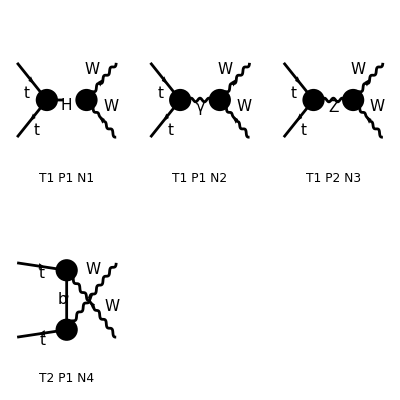

```mathematica
Process={F[3,{3}],-F[3,{3}]}-> {V[3],-V[3]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 1 Particles amplitude

in total: 4 Particles amplitudes

FeynAmpList(({F(3,{3}),-F(3,{3})}→{V(3),-V(3)})→(F(3,{3,Col1}) | p1 | MT | {(2 Charge)/3,(2 ColorCharge)/(√3)}
-F(3,{3,Col2}) | p2 | MT | {-(2 Charge)/3,-(2 ColorCharge)/(√3)})→(V(3) | k1 | MW | -Charge
-V(3) | k2 | MW | Charge),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],1/SW ⅈ EL MW 1/((k1+k2)^2-MH2) g(Lor1,Lor2) SumOver(Col1,3,External) SumOver(Col2,3,External) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,MT).(-(ⅈ EL MT om_- IndexDelta(Col1,Col2))/(2 MW SW)-(ⅈ EL MT om_+ IndexDelta(Col1,Col2))/(2 MW SW)).u(p1,MT)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==2),Integral[],ⅈ EL 1/(k1+k2)^2 g(Lor3,Lor4) SumOver(Col1,3,External) SumOver(Col2,3,External) (g(Lor1,Lor2) (k1-k2)(Lor4)+g(Lor1,Lor4) (-2 (k1)-k2)(Lor2)+g(Lor2,Lor4) (k1+2 (k2))(Lor1)) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,MT).(-2/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor3).om_--2/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor3).om_+).u(p1,MT)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==3),Integral[],-1/SW ⅈ CW EL 1/((k1+k2)^2-MZ2) g(Lor3,Lor4) SumOver(Col1,3,External) SumOver(Col2,3,External) (g(Lor1,Lor2) (k1-k2)(Lor4)+g(Lor1,Lor4) (-2 (k1)-k2)(Lor2)+g(Lor2,Lor4) (k1+2 (k2))(Lor1)) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,MT).((ⅈ EL (1/2-(2 SW2)/3) IndexDelta(Col1,Col2) ga(Lor3).om_-)/(CW SW)-(2 ⅈ EL SW IndexDelta(Col1,Col2) ga(Lor3).om_+)/(3 CW)).u(p1,MT)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==4),Integral[],SumOver(Col1,3,External) SumOver(Col2,3,External) 1/((p2-k1)^2-MB2) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,MT).(ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_-)/(√2 SW).(gs(k1-p2)+MB).(ⅈ EL ga(Lor2).om_-)/(√2 SW).u(p1,MT)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 100 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/avasquez/fc-pol-1.frm

running FORM...

ok

1/(12 MW2^2 SW2^2)Alfa2 π^2 (36 (Den(U,MB2))^2 MT2^4+288 MW2 (Den(U,MB2))^2 MT2^3-72 S (Den(U,MB2))^2 MT2^3-36 T (Den(U,MB2))^2 MT2^3-108 U (Den(U,MB2))^2 MT2^3+432 MW2 Den(S,MZ2) Den(U,MB2) MT2^3-72 S Den(S,MZ2) Den(U,MB2) MT2^3-432 MW2^2 (Den(S,MZ2))^2 MT2^2-36 S^2 (Den(S,MZ2))^2 MT2^2-512 MW2^2 SW2^2 (Den(S,MZ2))^2 MT2^2+128 S^2 SW2^2 (Den(S,MZ2))^2 MT2^2+512 MW2 S SW2^2 (Den(S,MZ2))^2 MT2^2+432 MW2 S (Den(S,MZ2))^2 MT2^2-1152 MW2^2 SW2 (Den(S,MZ2))^2 MT2^2-96 S^2 SW2 (Den(S,MZ2))^2 MT2^2-384 MW2 S SW2 (Den(S,MZ2))^2 MT2^2+1116 MW2^2 (Den(U,MB2))^2 MT2^2+108 U^2 (Den(U,MB2))^2 MT2^2-216 MW2 S (Den(U,MB2))^2 MT2^2-432 MW2 T (Den(U,MB2))^2 MT2^2+54 S T (Den(U,MB2))^2 MT2^2-432 MW2 U (Den(U,MB2))^2 MT2^2+126 S U (Den(U,MB2))^2 MT2^2+108 T U (Den(U,MB2))^2 MT2^2+2448 MW2^2 Den(S,MZ2) Den(U,MB2) MT2^2-72 S^2 Den(S,MZ2) Den(U,MB2) MT2^2-216 MW2 S Den(S,MZ2) Den(U,MB2) MT2^2-2496 MW2^2 SW2 Den(S,MZ2) Den(U,MB2) MT2^2+96 S^2 SW2 Den(S,MZ2) Den(U,MB2) MT2^2-96 MW2 S SW2 Den(S,MZ2) Den(U,MB2) MT2^2-504 MW2 T Den(S,MZ2) Den(U,MB2) MT2^2+108 S T Den(S,MZ2) Den(U,MB2) MT2^2+96 MW2 SW2 T Den(S,MZ2) Den(U,MB2) MT2^2-48 S SW2 T Den(S,MZ2) Den(U,MB2) MT2^2-360 MW2 U Den(S,MZ2) Den(U,MB2) MT2^2+36 S U Den(S,MZ2) Den(U,MB2) MT2^2-96 MW2 SW2 U Den(S,MZ2) Den(U,MB2) MT2^2+48 S SW2 U Den(S,MZ2) Den(U,MB2) MT2^2-18 (4 MT2-S) (12 MW2^2-4 S MW2+S^2) (Den(S,MH2))^2 MT2-2304 MW2^3 (Den(S,MZ2))^2 MT2-54 S^3 (Den(S,MZ2))^2 MT2+216 MW2 S^2 (Den(S,MZ2))^2 MT2-8192 MW2^3 SW2^2 (Den(S,MZ2))^2 MT2-256 S^3 SW2^2 (Den(S,MZ2))^2 MT2+2560 MW2 S^2 SW2^2 (Den(S,MZ2))^2 MT2-6144 MW2^2 S SW2^2 (Den(S,MZ2))^2 MT2-360 MW2^2 S (Den(S,MZ2))^2 MT2+6144 MW2^3 SW2 (Den(S,MZ2))^2 MT2+192 S^3 SW2 (Den(S,MZ2))^2 MT2-1920 MW2 S^2 SW2 (Den(S,MZ2))^2 MT2+6144 MW2^2 S SW2 (Den(S,MZ2))^2 MT2+512 MW2^2 SW2^2 T (Den(S,MZ2))^2 MT2-128 S^2 SW2^2 T (Den(S,MZ2))^2 MT2-512 MW2 S SW2^2 T (Den(S,MZ2))^2 MT2-288 MW2 S T (Den(S,MZ2))^2 MT2+1152 MW2^2 SW2 T (Den(S,MZ2))^2 MT2+96 S^2 SW2 T (Den(S,MZ2))^2 MT2+384 MW2 S SW2 T (Den(S,MZ2))^2 MT2+512 MW2^2 SW2^2 U (Den(S,MZ2))^2 MT2-128 S^2 SW2^2 U (Den(S,MZ2))^2 MT2-512 MW2 S SW2^2 U (Den(S,MZ2))^2 MT2-288 MW2 S U (Den(S,MZ2))^2 MT2+1152 MW2^2 SW2 U (Den(S,MZ2))^2 MT2+96 S^2 SW2 U (Den(S,MZ2))^2 MT2+384 MW2 S SW2 U (Den(S,MZ2))^2 MT2+1152 MW2^3 (Den(U,MB2))^2 MT2+9 S^3 (Den(U,MB2))^2 MT2-36 U^3 (Den(U,MB2))^2 MT2-72 MW2 S^2 (Den(U,MB2))^2 MT2+216 MW2 T^2 (Den(U,MB2))^2 MT2-18 S T^2 (Den(U,MB2))^2 MT2+216 MW2 U^2 (Den(U,MB2))^2 MT2-54 S U^2 (Den(U,MB2))^2 MT2-108 T U^2 (Den(U,MB2))^2 MT2-180 MW2^2 S (Den(U,MB2))^2 MT2-1368 MW2^2 T (Den(U,MB2))^2 MT2-27 S^2 T (Den(U,MB2))^2 MT2+342 MW2 S T (Den(U,MB2))^2 MT2-792 MW2^2 U (Den(U,MB2))^2 MT2+27 S^2 U (Den(U,MB2))^2 MT2-54 MW2 S U (Den(U,MB2))^2 MT2+432 MW2 T U (Den(U,MB2))^2 MT2-72 S T U (Den(U,MB2))^2 MT2+1008 MW2^3 Den(S,MZ2) Den(U,MB2) MT2+36 MW2 S^2 Den(S,MZ2) Den(U,MB2) MT2+180 MW2 T^2 Den(S,MZ2) Den(U,MB2) MT2-54 S T^2 Den(S,MZ2) Den(U,MB2) MT2-96 MW2 SW2 T^2 Den(S,MZ2) Den(U,MB2) MT2+48 S SW2 T^2 Den(S,MZ2) Den(U,MB2) MT2+36 MW2 U^2 Den(S,MZ2) Den(U,MB2) MT2+18 S U^2 Den(S,MZ2) Den(U,MB2) MT2+96 MW2 SW2 U^2 Den(S,MZ2) Den(U,MB2) MT2-48 S SW2 U^2 Den(S,MZ2) Den(U,MB2) MT2-864 MW2^2 S Den(S,MZ2) Den(U,MB2) MT2+24 S^3 SW2 Den(S,MZ2) Den(U,MB2) MT2-336 MW2 S^2 SW2 Den(S,MZ2) Den(U,MB2) MT2+1728 MW2^2 S SW2 Den(S,MZ2) Den(U,MB2) MT2-2376 MW2^2 T Den(S,MZ2) Den(U,MB2) MT2-54 S^2 T Den(S,MZ2) Den(U,MB2) MT2+576 MW2 S T Den(S,MZ2) Den(U,MB2) MT2+2496 MW2^2 SW2 T Den(S,MZ2) Den(U,MB2) MT2+72 S^2 SW2 T Den(S,MZ2) Den(U,MB2) MT2-816 MW2 S SW2 T Den(S,MZ2) Den(U,MB2) MT2-216 MW2^2 U Den(S,MZ2) Den(U,MB2) MT2+126 S^2 U Den(S,MZ2) Den(U,MB2) MT2-576 MW2 S U Den(S,MZ2) Den(U,MB2) MT2+192 MW2^2 SW2 U Den(S,MZ2) Den(U,MB2) MT2-168 S^2 SW2 U Den(S,MZ2) Den(U,MB2) MT2+1200 MW2 S SW2 U Den(S,MZ2) Den(U,MB2) MT2+216 MW2 T U Den(S,MZ2) Den(U,MB2) MT2-36 S T U Den(S,MZ2) Den(U,MB2) MT2-6 Den(S,MH2) (2 (12 MW2^2-S^2) (8 SW2-3) (T-U) Den(S,MZ2)+3 (-4 (S+3 T-3 U) MW2^2+2 (2 S^2+(T-U) S+(T-U)^2) MW2+4 MT2 (S-2 MW2)^2+S ((T-U)^2-S^2)) Den(U,MB2)) MT2-128 SW2^2 (60 MW2^4+4 (S-8 (T+U)) MW2^3-(15 S^2+8 (T+U) S-4 (T^2-U T+U^2)) MW2^2+2 S (3 S^2+3 (T+U) S-T^2-U^2) MW2+MT2^2 (4 MW2^2-4 S MW2-S^2)-S^2 (S+T) (S+U)+MT2 (64 MW2^3+(48 S-4 (T+U)) MW2^2+4 S (-5 S+T+U) MW2+S^2 (2 S+T+U))) (Den(S,0))^2-2736 MW2^4 (Den(S,MZ2))^2+36 S^4 (Den(S,MZ2))^2-216 MW2 S^3 (Den(S,MZ2))^2+684 MW2^2 S^2 (Den(S,MZ2))^2-7680 MW2^4 SW2^2 (Den(S,MZ2))^2+128 S^4 SW2^2 (Den(S,MZ2))^2-768 MW2 S^3 SW2^2 (Den(S,MZ2))^2+1920 MW2^2 S^2 SW2^2 (Den(S,MZ2))^2-512 MW2^3 S SW2^2 (Den(S,MZ2))^2-512 MW2^2 SW2^2 T^2 (Den(S,MZ2))^2+256 MW2 S SW2^2 T^2 (Den(S,MZ2))^2+72 MW2 S T^2 (Den(S,MZ2))^2-192 MW2 S SW2 T^2 (Den(S,MZ2))^2-512 MW2^2 SW2^2 U^2 (Den(S,MZ2))^2+256 MW2 S SW2^2 U^2 (Den(S,MZ2))^2+72 MW2 S U^2 (Den(S,MZ2))^2-192 MW2 S SW2 U^2 (Den(S,MZ2))^2-144 MW2^3 S (Den(S,MZ2))^2+7296 MW2^4 SW2 (Den(S,MZ2))^2-96 S^4 SW2 (Den(S,MZ2))^2+576 MW2 S^3 SW2 (Den(S,MZ2))^2-1824 MW2^2 S^2 SW2 (Den(S,MZ2))^2+384 MW2^3 S SW2 (Den(S,MZ2))^2+1152 MW2^3 T (Den(S,MZ2))^2+36 S^3 T (Den(S,MZ2))^2-216 MW2 S^2 T (Den(S,MZ2))^2+4096 MW2^3 SW2^2 T (Den(S,MZ2))^2+128 S^3 SW2^2 T (Den(S,MZ2))^2-768 MW2 S^2 SW2^2 T (Den(S,MZ2))^2+1024 MW2^2 S SW2^2 T (Den(S,MZ2))^2+576 MW2^2 S T (Den(S,MZ2))^2-3072 MW2^3 SW2 T (Den(S,MZ2))^2-96 S^3 SW2 T (Den(S,MZ2))^2+576 MW2 S^2 SW2 T (Den(S,MZ2))^2-1536 MW2^2 S SW2 T (Den(S,MZ2))^2+1152 MW2^3 U (Den(S,MZ2))^2+36 S^3 U (Den(S,MZ2))^2-216 MW2 S^2 U (Den(S,MZ2))^2+4096 MW2^3 SW2^2 U (Den(S,MZ2))^2+128 S^3 SW2^2 U (Den(S,MZ2))^2-768 MW2 S^2 SW2^2 U (Den(S,MZ2))^2+1024 MW2^2 S SW2^2 U (Den(S,MZ2))^2+576 MW2^2 S U (Den(S,MZ2))^2-3072 MW2^3 SW2 U (Den(S,MZ2))^2-96 S^3 SW2 U (Den(S,MZ2))^2+576 MW2 S^2 SW2 U (Den(S,MZ2))^2-1536 MW2^2 S SW2 U (Den(S,MZ2))^2+432 MW2^2 T U (Den(S,MZ2))^2+36 S^2 T U (Den(S,MZ2))^2+512 MW2^2 SW2^2 T U (Den(S,MZ2))^2+128 S^2 SW2^2 T U (Den(S,MZ2))^2-1152 MW2^2 SW2 T U (Den(S,MZ2))^2-96 S^2 SW2 T U (Den(S,MZ2))^2+144 MW2^4 (Den(U,MB2))^2+36 MW2 S^3 (Den(U,MB2))^2-36 MW2 T^3 (Den(U,MB2))^2-36 MW2 U^3 (Den(U,MB2))^2+36 T U^3 (Den(U,MB2))^2-180 MW2^2 S^2 (Den(U,MB2))^2+432 MW2^2 T^2 (Den(U,MB2))^2+9 S^2 T^2 (Den(U,MB2))^2-108 MW2 S T^2 (Den(U,MB2))^2-36 MW2^2 U^2 (Den(U,MB2))^2-18 S^2 U^2 (Den(U,MB2))^2+162 MW2 S U^2 (Den(U,MB2))^2-108 MW2 T U^2 (Den(U,MB2))^2+18 S T U^2 (Den(U,MB2))^2+72 MW2^3 S (Den(U,MB2))^2-864 MW2^3 T (Den(U,MB2))^2+9 S^3 T (Den(U,MB2))^2-54 MW2 S^2 T (Den(U,MB2))^2+396 MW2^2 S T (Den(U,MB2))^2-18 S^3 U (Den(U,MB2))^2+126 MW2 S^2 U (Den(U,MB2))^2-108 MW2 T^2 U (Den(U,MB2))^2+18 S T^2 U (Den(U,MB2))^2-288 MW2^2 S U (Den(U,MB2))^2+576 MW2^2 T U (Den(U,MB2))^2+9 S^2 T U (Den(U,MB2))^2-126 MW2 S T U (Den(U,MB2))^2-1872 MW2^4 Den(S,MZ2) Den(U,MB2)+18 S^4 Den(S,MZ2) Den(U,MB2)-90 MW2 S^3 Den(S,MZ2) Den(U,MB2)+324 MW2^2 S^2 Den(S,MZ2) Den(U,MB2)+432 MW2^2 T^2 Den(S,MZ2) Den(U,MB2)+18 S^2 T^2 Den(S,MZ2) Den(U,MB2)-144 MW2 S T^2 Den(S,MZ2) Den(U,MB2)-576 MW2^2 SW2 T^2 Den(S,MZ2) Den(U,MB2)-24 S^2 SW2 T^2 Den(S,MZ2) Den(U,MB2)+192 MW2 S SW2 T^2 Den(S,MZ2) Den(U,MB2)-576 MW2^2 U^2 Den(S,MZ2) Den(U,MB2)-36 S^2 U^2 Den(S,MZ2) Den(U,MB2)+324 MW2 S U^2 Den(S,MZ2) Den(U,MB2)+768 MW2^2 SW2 U^2 Den(S,MZ2) Den(U,MB2)+48 S^2 SW2 U^2 Den(S,MZ2) Den(U,MB2)-432 MW2 S SW2 U^2 Den(S,MZ2) Den(U,MB2)+72 MW2 T U^2 Den(S,MZ2) Den(U,MB2)-36 S T U^2 Den(S,MZ2) Den(U,MB2)-96 MW2 SW2 T U^2 Den(S,MZ2) Den(U,MB2)+48 S SW2 T U^2 Den(S,MZ2) Den(U,MB2)-216 MW2^3 S Den(S,MZ2) Den(U,MB2)+2496 MW2^4 SW2 Den(S,MZ2) Den(U,MB2)-24 S^4 SW2 Den(S,MZ2) Den(U,MB2)+120 MW2 S^3 SW2 Den(S,MZ2) Den(U,MB2)-432 MW2^2 S^2 SW2 Den(S,MZ2) Den(U,MB2)+288 MW2^3 S SW2 Den(S,MZ2) Den(U,MB2)-72 MW2^3 T Den(S,MZ2) Den(U,MB2)+36 S^3 T Den(S,MZ2) Den(U,MB2)-234 MW2 S^2 T Den(S,MZ2) Den(U,MB2)+936 MW2^2 S T Den(S,MZ2) Den(U,MB2)+96 MW2^3 SW2 T Den(S,MZ2) Den(U,MB2)-48 S^3 SW2 T Den(S,MZ2) Den(U,MB2)+312 MW2 S^2 SW2 T Den(S,MZ2) Den(U,MB2)-1248 MW2^2 S SW2 T Den(S,MZ2) Den(U,MB2)+1800 MW2^3 U Den(S,MZ2) Den(U,MB2)-18 S^3 U Den(S,MZ2) Den(U,MB2)+54 MW2 S^2 U Den(S,MZ2) Den(U,MB2)-72 MW2 T^2 U Den(S,MZ2) Den(U,MB2)+36 S T^2 U Den(S,MZ2) Den(U,MB2)+96 MW2 SW2 T^2 U Den(S,MZ2) Den(U,MB2)-48 S SW2 T^2 U Den(S,MZ2) Den(U,MB2)-360 MW2^2 S U Den(S,MZ2) Den(U,MB2)-2400 MW2^3 SW2 U Den(S,MZ2) Den(U,MB2)+24 S^3 SW2 U Den(S,MZ2) Den(U,MB2)-72 MW2 S^2 SW2 U Den(S,MZ2) Den(U,MB2)+480 MW2^2 S SW2 U Den(S,MZ2) Den(U,MB2)+288 MW2^2 T U Den(S,MZ2) Den(U,MB2)+18 S^2 T U Den(S,MZ2) Den(U,MB2)+36 MW2 S T U Den(S,MZ2) Den(U,MB2)-384 MW2^2 SW2 T U Den(S,MZ2) Den(U,MB2)-24 S^2 SW2 T U Den(S,MZ2) Den(U,MB2)-48 MW2 S SW2 T U Den(S,MZ2) Den(U,MB2)+8 SW2 Den(S,0) (12 MT2 (12 MW2^2-S^2) (T-U) Den(S,MH2)+4 (12 (40 SW2-19) MW2^4+4 (8 SW2-3) (S-8 (T+U)) MW2^3+((57-120 SW2) S^2-16 (4 SW2-3) (T+U) S+36 T U+32 SW2 (T^2-U T+U^2)) MW2^2+2 S (8 SW2-3) (3 S^2+3 (T+U) S-T^2-U^2) MW2+MT2^2 (4 (8 SW2+9) MW2^2-4 S (8 SW2-3) MW2+S^2 (3-8 SW2))-S^2 (8 SW2-3) (S+T) (S+U)+MT2 (64 (8 SW2-3) MW2^3+4 (48 S (2 SW2-1)-(8 SW2+9) (T+U)) MW2^2-4 S (8 SW2-3) (5 S-T-U) MW2+S^2 (8 SW2-3) (2 S+T+U))) Den(S,MZ2)+3 (-104 MW2^4-4 (3 S+T-25 U) MW2^3+2 (9 S^2+26 T S-10 U S+12 T^2-16 U^2+8 T U) MW2^2+(-5 S^3+(3 U-13 T) S^2+(-8 T^2+2 U T+18 U^2) S+4 T U (U-T)) MW2+S (S+T) (S^2+(T-U) S+2 (T-U) U)+2 MT2^2 (52 MW2^2+2 (S-T+U) MW2+S (-2 S+T-U))-MT2 (8 (9 S+13 T+U) MW2^2-2 (7 S^2+17 T S-25 U S+2 T^2-2 U^2) MW2+S (S^2+3 T S-7 U S+2 T^2-2 U^2))) Den(U,MB2)))

```mathematica
resFCttWW=square1/.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y)};
```

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARttWW=Get["resANATARttWW.m"];
```

```mathematica
FullSimplify[resANATARttWW- 4 resFCttWW,{S+T+U==2MW2+2MT2,cw^2+sw^2==1}]
```

0

## tt -> ZZ

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AttZZ=GenerateAmplitude[{t,tbar}->{Z,Z},OutputName->"ttZZ",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttZZ.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/ttZZ/ttZZ_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {t, tbar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{t(p1),tbar(p2)}→{Z(p3),Z(p4)}},Total→3,Name→ttZZ,LoopOrder→0,Kinematics→{p1^2→MT^2,p1.p1→MT^2,1/(p1.p1)→1/MT^2,p2^2→MT^2,p2.p2→MT^2,1/(p2.p2)→1/MT^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MT^2),p1.p3→1/2 (MT^2+MZ^2-T),p2.p3→1/2 (MT^2+MZ^2-U),1/(p1.p2)→2/(S-2 MT^2),1/(p1.p3)→2/(MT^2+MZ^2-T),1/(p2.p3)→2/(MT^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC48 GC70 𝕀_Spin3Spin1 Den(-p1-p2,MH) ε_Lor4(p3,MZ) ε_Lor4(p4,MZ) (v̄)_Spin3^Colour3(p2,MT) u_Spin1^Colour3(p1,MT),DiagramID(2)→-1/4 ⅈ Den(p1-p3,MT) ε_Lor2(p3,MZ) ε_Lor4(p4,MZ) (v̄)_Spin3^iColour2(p2,MT) u_Spin1^iColour2(p1,MT) ((GC26+5 GC33) (γ^Lor4)_(iSpin1 Spin3)-(GC26-3 GC33) (γ^Lor4 γ^5)_(iSpin1 Spin3)) ((GC26+5 GC33) (γ^Lor2)_(iSpin2 Spin1)-(GC26-3 GC33) (γ^Lor2 γ^5)_(iSpin2 Spin1)) (MT 𝕀_iSpin1iSpin2+(γ·(p1-p3))_(iSpin1 iSpin2)),DiagramID(3)→-1/4 ⅈ Den(p1-p4,MT) ε_Lor2(p3,MZ) ε_Lor4(p4,MZ) (v̄)_Spin3^iColour2(p2,MT) u_Spin1^iColour2(p1,MT) ((GC26+5 GC33) (γ^Lor2)_(iSpin1 Spin3)-(GC26-3 GC33) (γ^Lor2 γ^5)_(iSpin1 Spin3)) ((GC26+5 GC33) (γ^Lor4)_(iSpin2 Spin1)-(GC26-3 GC33) (γ^Lor4 γ^5)_(iSpin2 Spin1)) (MT 𝕀_iSpin1iSpin2+(γ·(p1-p4))_(iSpin1 iSpin2))}|>

```mathematica
AttZZC=GenerateAmplitudeConjugate[{t,tbar}->{Z,Z},OutputName->"ttZZ",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ttZZ.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/ttZZ/ttZZ_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {t, tbar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{t(p1),tbar(p2)}→{Z(p3),Z(p4)}},Total→3,Name→ttZZ,LoopOrder→0,Kinematics→{p1^2→MT^2,p1.p1→MT^2,1/(p1.p1)→1/MT^2,p2^2→MT^2,p2.p2→MT^2,1/(p2.p2)→1/MT^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MT^2),p1.p3→1/2 (MT^2+MZ^2-T),p2.p3→1/2 (MT^2+MZ^2-U),1/(p1.p2)→2/(S-2 MT^2),1/(p1.p3)→2/(MT^2+MZ^2-T),1/(p2.p3)→2/(MT^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC48 GC70 𝕀_SpinC1SpinC3 Den(-p1-p2,MH) (ε^†)_LorC4^(p3,MZ) (ε^†)_LorC4^(p4,MZ) ((ū)^†)_SpinC1^ColourC3(p1,MT) (v^†)_SpinC3^ColourC3(p2,MT),DiagramID(2)→1/4 ⅈ Den(p1-p3,MT) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC4^(p4,MZ) ((ū)^†)_SpinC1^iColourC2(p1,MT) (v^†)_SpinC3^iColourC2(p2,MT) ((GC26-3 GC33) (γ^5 γ^LorC4)_(iSpinC1 SpinC3)+(GC26+5 GC33) (γ^LorC4)_(iSpinC1 SpinC3)) ((GC26-3 GC33) (γ^5 γ^LorC2)_(iSpinC2 SpinC1)+(GC26+5 GC33) (γ^LorC2)_(iSpinC2 SpinC1)) (MT 𝕀_iSpinC2iSpinC1+(γ·p1)_(iSpinC1 iSpinC2)-(γ·p3)_(iSpinC1 iSpinC2)),DiagramID(3)→1/4 ⅈ Den(p1-p4,MT) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC4^(p4,MZ) ((ū)^†)_SpinC1^iColourC2(p1,MT) (v^†)_SpinC3^iColourC2(p2,MT) ((GC26-3 GC33) (γ^5 γ^LorC2)_(iSpinC1 SpinC3)+(GC26+5 GC33) (γ^LorC2)_(iSpinC1 SpinC3)) ((GC26-3 GC33) (γ^5 γ^LorC4)_(iSpinC2 SpinC1)+(GC26+5 GC33) (γ^LorC4)_(iSpinC2 SpinC1)) (MT 𝕀_iSpinC2iSpinC1+(γ·p1)_(iSpinC1 iSpinC2)-(γ·p4)_(iSpinC1 iSpinC2))}|>

```mathematica
AmpSQttZZ=GenerateAmplitudeSquare[AttZZ,AttZZC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{t(p1),tbar(p2)}→{Z(p3),Z(p4)}},Name→ttZZ,LoopOrder→0,Kinematics→{p1^2→MT^2,p1.p1→MT^2,1/(p1.p1)→1/MT^2,p2^2→MT^2,p2.p2→MT^2,1/(p2.p2)→1/MT^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MT^2),p1.p3→1/2 (MT^2+MZ^2-T),p2.p3→1/2 (MT^2+MZ^2-U),1/(p1.p2)→2/(S-2 MT^2),1/(p1.p3)→2/(MT^2+MZ^2-T),1/(p2.p3)→2/(MT^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→1/(1296 cw^4 MZ^4 sw2^2)ee^4 Nc (-162 MT^2 (4 MT^2-S) (4 MT^4-4 (T+U) MT^2+8 MZ^4+(T+U)^2) (Den(-p1-p2,MH))^2 (cw^2+sw2)^4-18 MT^2 Den(-p1-p2,MH) ((9 (8 MT^6-2 (S+5 T+3 U) MT^4+(-8 (T-U) MZ^2+5 T^2+U^2+3 S T+S U+2 T U) MT^2-T (S+T-U) (T+U)+2 MZ^2 (T-U) (S+3 T+U)) cw^4+6 sw2 (24 MT^6-2 (3 S+11 T+13 U) MT^4+(64 MZ^4+8 (T-U) MZ^2+3 T^2+7 U^2+9 S T+3 S U+14 T U) MT^2-16 MZ^4 S+T (-3 S+T-U) (T+U)-2 MZ^2 (T-U) (S+3 T+U)) cw^2+sw2^2 (72 MT^6-2 (9 S+53 T+19 U) MT^4+(-128 MZ^4-136 (T-U) MZ^2+69 T^2+U^2+2 T U+9 S (3 T+U)) MT^2+32 MZ^4 S-T (9 S+17 (T-U)) (T+U)+34 MZ^2 (T-U) (S+3 T+U))) Den(p1-p3,MT)+(9 (8 MT^6-2 (S+5 T+3 U) MT^4+(-4 (T-U) MZ^2+5 T^2+U^2+3 S T+S U+2 T U) MT^2-8 MZ^4 (T-U)+2 MZ^2 (S+2 T) (T-U)-T (S+T-U) (T+U)) cw^4+6 sw2 (24 MT^6-2 (3 S+11 T+13 U) MT^4+(64 MZ^4+4 (T-U) MZ^2+3 T^2+7 U^2+S T+11 S U+14 T U) MT^2-2 MZ^2 (S+2 T) (T-U)-8 MZ^4 (2 S-T+U)+(T+U) (T^2+S T-U T-4 S U)) cw^2+sw2^2 (72 MT^6-2 (9 S+53 T+19 U) MT^4+(-128 MZ^4-68 (T-U) MZ^2+69 T^2+U^2+43 S T-7 S U+2 T U) MT^2+34 MZ^2 (S+2 T) (T-U)-(S (17 T-8 U)+17 T (T-U)) (T+U)+8 MZ^4 (4 S+17 (U-T)))) Den(p3-p2,MT)) (cw^2+sw2)^2+(81 (3 MT^8+(4 MZ^2-4 S-6 T-4 U) MT^6+(-5 MZ^4-(5 S+T+5 U) MZ^2+S^2+4 T^2+U^2+8 S T+2 S U+7 T U) MT^4+(-2 MZ^6+(7 S+3 T+7 U) MZ^4+(S^2+2 U S+(T-U)^2) MZ^2-T (2 S^2+5 T S+3 U S+T^2+U^2+4 T U)) MT^2+T^2 (S+T) (S+U)+2 MZ^6 (S+T+U)-MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)+MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^8-108 sw2 (3 MT^8-2 (4 MZ^2+2 S+3 T+2 U) MT^6+(-5 MZ^4+(19 S-T+19 U) MZ^2+S^2+4 T^2+U^2+8 S T+2 S U+7 T U) MT^4-(14 MZ^6-(13 S+21 T+13 U) MZ^4+(5 S^2+12 T S+10 U S-7 T^2+5 U^2+14 T U) MZ^2+T (2 S^2+5 T S+3 U S+T^2+U^2+4 T U)) MT^2+T^2 (S+T) (S+U)+2 MZ^6 (S+T+U)-MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)+MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^6-18 sw2^2 (23 MT^8+(92 MZ^2-20 S-30 T-36 U) MT^6+(303 MZ^4-(129 S+29 T+161 U) MZ^2-3 S^2+4 T^2+13 U^2+24 S T+10 S U+43 T U) MT^4+(46 MZ^6+(-41 S+187 T-41 U) MZ^4+(17 S^2+72 T S+66 U S-23 T^2+49 U^2+78 T U) MZ^2+T (6 S^2-(T+7 U) S+3 T^2-13 U^2-4 T U)) MT^2-3 (2 (S+T+U) MZ^6-(2 S^2+4 (T+U) S+T^2+2 U^2+4 T U) MZ^4+T (-T^2+U T+2 U^2+S (T+2 U)) MZ^2+T^2 (S+T) (S+U))) cw^4+12 sw2^3 (29 MT^8+(256 MZ^2-28 S-42 T-44 U) MT^6+(293 MZ^4-(451 S+31 T+483 U) MZ^2-S^2+12 T^2+15 U^2+40 S T+14 S U+57 T U) MT^4+(198 MZ^6-(105 S+41 T+105 U) MZ^4+(97 S^2+228 T S+226 U S-99 T^2+129 U^2+230 T U) MZ^2+T (2 S^2-11 T S-13 U S+T^2-15 U^2-12 T U)) MT^2-T^2 (S+T) (S+U)-2 MZ^6 (S+T+U)+MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)-MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^2+sw2^4 (707 MT^8+2 (74 MZ^2-482 S-723 T-466 U) MT^6+(-1861 MZ^4+(347 S-193 T+411 U) MZ^2+257 S^2+996 T^2+225 U^2+1960 S T+482 S U+1671 T U) MT^4-(1266 MZ^6-(2175 S+1387 T+2175 U) MZ^4+(119 S^2+816 T S+302 U S-633 T^2+183 U^2+1330 T U) MZ^2+T (514 S^2+1253 T S+739 U S+257 T^2+225 U^2+996 T U)) MT^2+257 (2 (S+T+U) MZ^6-(2 S^2+4 (T+U) S+T^2+2 U^2+4 T U) MZ^4+T (-T^2+U T+2 U^2+S (T+2 U)) MZ^2+T^2 (S+T) (S+U)))) (Den(p1-p3,MT))^2+(81 (3 MT^8-2 (2 S+3 T+2 U) MT^6+(-5 MZ^4+(S-5 T+3 U) MZ^2+S^2+4 T^2+U^2+7 T U+5 S (T+U)) MT^4+(6 MZ^6+(3 S-T-U) MZ^4+(-3 S^2+2 T S+5 T^2-3 U^2+2 T U) MZ^2-(S+T) (T^2+4 U T+U^2+S (T+U))) MT^2+4 MZ^8+T (S+T)^2 U-2 MZ^6 (3 S+3 T+U)+MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (-S^2+2 (T+2 U) S+3 T^2-2 U^2+4 T U)) cw^8-108 sw2 (3 MT^8+2 (6 MZ^2-2 S-3 T-2 U) MT^6+(43 MZ^4-(11 S+17 T+9 U) MZ^2+S^2+4 T^2+U^2+7 T U+5 S (T+U)) MT^4+(18 MZ^6+(-27 S-31 T+5 U) MZ^4+(3 S^2+14 T S+11 T^2+3 U^2+2 T U) MZ^2-(S+T) (T^2+4 U T+U^2+S (T+U))) MT^2+4 MZ^8+T (S+T)^2 U-2 MZ^6 (3 S+3 T+U)+MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (-S^2+2 (T+2 U) S+3 T^2-2 U^2+4 T U)) cw^6-18 sw2^2 (23 MT^8-2 (20 MZ^2+10 S+15 T+18 U) MT^6+(591 MZ^4+(69 S+55 T+31 U) MZ^2-3 S^2+4 T^2+13 U^2+S T+33 S U+43 T U) MT^4+(454 MZ^6-(101 S+89 T+17 U) MZ^4-(43 S^2+78 T S+35 T^2+11 U^2+6 T U) MZ^2+(S+T) (3 T^2-4 U T-13 U^2+3 S (T+U))) MT^2-3 (4 MZ^8-2 (3 S+3 T+U) MZ^6+(-S^2+2 T S+4 U S+3 T^2-2 U^2+4 T U) MZ^4+(S+T) (S^2-U S-T^2+2 U^2-3 T U) MZ^2+T (S+T)^2 U)) cw^4+12 sw2^3 (29 MT^8-2 (98 MZ^2+14 S+21 T+22 U) MT^6+(-43 MZ^4+(227 S+201 T+193 U) MZ^2-S^2+12 T^2+15 U^2+11 S T+43 S U+57 T U) MT^4+(310 MZ^6+(295 S+299 T-97 U) MZ^4-(127 S^2+230 T S+103 T^2+95 U^2+2 T U) MZ^2+(S+T) (T^2-12 U T-15 U^2+S (T+U))) MT^2-4 MZ^8-T (S+T)^2 U+2 MZ^6 (3 S+3 T+U)-MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (S^2-2 (T+2 U) S-3 T^2+2 U^2-4 T U)) cw^2+sw2^4 (707 MT^8+2 (376 MZ^2-482 S-723 T-466 U) MT^6+(251 MZ^4+(-559 S-2037 T+19 U) MZ^2+257 S^2+996 T^2+225 U^2+1253 S T+1189 S U+1671 T U) MT^4+(1270 MZ^6+(-725 S-1753 T+119 U) MZ^4+(-331 S^2+1330 T S+1661 T^2-395 U^2+514 T U) MZ^2-(S+T) (257 T^2+996 U T+225 U^2+257 S (T+U))) MT^2+257 (4 MZ^8-2 (3 S+3 T+U) MZ^6+(-S^2+2 T S+4 U S+3 T^2-2 U^2+4 T U) MZ^4+(S+T) (S^2-U S-T^2+2 U^2-3 T U) MZ^2+T (S+T)^2 U))) (Den(p3-p2,MT))^2-2 (81 (3 MT^8-(4 MZ^2+S+3 T+U) MT^6+(-25 MZ^4+(-3 S+7 T+5 U) MZ^2+T (S+T-3 U)) MT^4+(-2 MZ^6+(23 S+13 T+7 U) MZ^4+(S^2-5 T^2-U^2-6 T U) MZ^2+T U (S+3 T+U)) MT^2+2 MZ^6 T-T^2 (S+T) U+MZ^2 T (S+T) (-S+T+3 U)-MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^8+108 sw2 (13 MT^8+(4 MZ^2-3 S-17 T-11 U) MT^6+(MZ^4+(-3 S-13 T+U) MZ^2+9 T^2+2 U^2+5 S T+2 S U+7 T U) MT^4+(2 MZ^6-(11 S+5 (3 T+U)) MZ^4-(S^2-2 (2 T+U) S-9 T^2+U^2-4 T U) MZ^2+T (-2 T^2-2 S T-3 U T+U^2-3 S U)) MT^2-2 MZ^6 T+MZ^2 T (S+T) (S-T-3 U)+T^2 (S+T) U+MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^6+18 sw2^2 (105 MT^8-(12 MZ^2+11 S+113 T+91 U) MT^6+(5 MZ^4+(91 S+57 T-21 U) MZ^2+39 T^2+20 U^2+15 S T+4 S U+31 T U) MT^4-(6 MZ^6+(67 S-131 T-25 U) MZ^4+(-3 S^2+72 T S+28 U S+55 T^2+7 U^2-26 T U) MZ^2+T (4 T^2+4 S T-9 U T-7 U^2+S U)) MT^2+6 MZ^6 T-3 T^2 (S+T) U+3 MZ^2 T (S+T) (-S+T+3 U)-3 MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^4+12 sw2^3 (109 MT^8+(4 MZ^2-43 S-153 T-67 U) MT^6+(-367 MZ^4+(-175 S-121 T+109 U) MZ^2+93 T^2+6 U^2+65 S T+22 S U+15 T U) MT^4+(2 MZ^6+(269 S-131 T+15 U) MZ^4-(S^2-124 T S-54 U S-97 T^2+21 U^2+64 T U) MZ^2-T (22 T^2+22 S T+3 U T-21 U^2+23 S U)) MT^2-2 MZ^6 T+MZ^2 T (S+T) (S-T-3 U)+T^2 (S+T) U+MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^2+sw2^4 (67 MT^8+(-1028 MZ^2-49 S+141 T+239 U) MT^6-(4921 MZ^4+(235 S-2207 T-877 U) MZ^2+231 T^2+72 U^2+55 S T+104 S U+915 T U) MT^4+(-514 MZ^6+(4967 S+3637 T+1695 U) MZ^4+(257 S^2-8 (46 T+21 U) S-1589 T^2-153 U^2-1342 T U) MZ^2+T (104 T^2+104 S T+771 U T+153 U^2+361 S U)) MT^2+257 (2 T MZ^6-(4 S^2+3 T S+4 U S+3 T^2+2 T U) MZ^4+T (S+T) (-S+T+3 U) MZ^2-T^2 (S+T) U))) Den(p1-p3,MT) Den(p3-p2,MT))|>

```mathematica
resANATARttZZ=AmpSQttZZ[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),Nc->3,-p1-p2->√S,(-p1-p2)^2->S,p1-p3->√T,p3-p2->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/(432 cw^4 MZ^4 sw^4)ee^4 (-(162 MT^2 (4 MT^2-S) (4 MT^4-4 (T+U) MT^2+8 MZ^4+(T+U)^2) (cw^2+sw^2)^4)/((S-MH^2)^2)-1/(S-MH^2)18 MT^2 (1/(U-MT^2)(9 (8 MT^6-2 (S+5 T+3 U) MT^4+(-4 (T-U) MZ^2+5 T^2+U^2+3 S T+S U+2 T U) MT^2-8 MZ^4 (T-U)+2 MZ^2 (S+2 T) (T-U)-T (S+T-U) (T+U)) cw^4+6 sw^2 (24 MT^6-2 (3 S+11 T+13 U) MT^4+(64 MZ^4+4 (T-U) MZ^2+3 T^2+7 U^2+S T+11 S U+14 T U) MT^2-2 MZ^2 (S+2 T) (T-U)-8 MZ^4 (2 S-T+U)+(T+U) (T^2+S T-U T-4 S U)) cw^2+sw^4 (72 MT^6-2 (9 S+53 T+19 U) MT^4+(-128 MZ^4-68 (T-U) MZ^2+69 T^2+U^2+43 S T-7 S U+2 T U) MT^2+34 MZ^2 (S+2 T) (T-U)-(S (17 T-8 U)+17 T (T-U)) (T+U)+8 MZ^4 (4 S+17 (U-T))))+1/(T-MT^2)(9 (8 MT^6-2 (S+5 T+3 U) MT^4+(-8 (T-U) MZ^2+5 T^2+U^2+3 S T+S U+2 T U) MT^2-T (S+T-U) (T+U)+2 MZ^2 (T-U) (S+3 T+U)) cw^4+6 sw^2 (24 MT^6-2 (3 S+11 T+13 U) MT^4+(64 MZ^4+8 (T-U) MZ^2+3 T^2+7 U^2+9 S T+3 S U+14 T U) MT^2-16 MZ^4 S+T (-3 S+T-U) (T+U)-2 MZ^2 (T-U) (S+3 T+U)) cw^2+sw^4 (72 MT^6-2 (9 S+53 T+19 U) MT^4+(-128 MZ^4-136 (T-U) MZ^2+69 T^2+U^2+2 T U+9 S (3 T+U)) MT^2+32 MZ^4 S-T (9 S+17 (T-U)) (T+U)+34 MZ^2 (T-U) (S+3 T+U)))) (cw^2+sw^2)^2+1/((U-MT^2)^2)(81 (3 MT^8-2 (2 S+3 T+2 U) MT^6+(-5 MZ^4+(S-5 T+3 U) MZ^2+S^2+4 T^2+U^2+7 T U+5 S (T+U)) MT^4+(6 MZ^6+(3 S-T-U) MZ^4+(-3 S^2+2 T S+5 T^2-3 U^2+2 T U) MZ^2-(S+T) (T^2+4 U T+U^2+S (T+U))) MT^2+4 MZ^8+T (S+T)^2 U-2 MZ^6 (3 S+3 T+U)+MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (-S^2+2 (T+2 U) S+3 T^2-2 U^2+4 T U)) cw^8-108 sw^2 (3 MT^8+2 (6 MZ^2-2 S-3 T-2 U) MT^6+(43 MZ^4-(11 S+17 T+9 U) MZ^2+S^2+4 T^2+U^2+7 T U+5 S (T+U)) MT^4+(18 MZ^6+(-27 S-31 T+5 U) MZ^4+(3 S^2+14 T S+11 T^2+3 U^2+2 T U) MZ^2-(S+T) (T^2+4 U T+U^2+S (T+U))) MT^2+4 MZ^8+T (S+T)^2 U-2 MZ^6 (3 S+3 T+U)+MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (-S^2+2 (T+2 U) S+3 T^2-2 U^2+4 T U)) cw^6-18 sw^4 (23 MT^8-2 (20 MZ^2+10 S+15 T+18 U) MT^6+(591 MZ^4+(69 S+55 T+31 U) MZ^2-3 S^2+4 T^2+13 U^2+S T+33 S U+43 T U) MT^4+(454 MZ^6-(101 S+89 T+17 U) MZ^4-(43 S^2+78 T S+35 T^2+11 U^2+6 T U) MZ^2+(S+T) (3 T^2-4 U T-13 U^2+3 S (T+U))) MT^2-3 (4 MZ^8-2 (3 S+3 T+U) MZ^6+(-S^2+2 T S+4 U S+3 T^2-2 U^2+4 T U) MZ^4+(S+T) (S^2-U S-T^2+2 U^2-3 T U) MZ^2+T (S+T)^2 U)) cw^4+12 sw^6 (29 MT^8-2 (98 MZ^2+14 S+21 T+22 U) MT^6+(-43 MZ^4+(227 S+201 T+193 U) MZ^2-S^2+12 T^2+15 U^2+11 S T+43 S U+57 T U) MT^4+(310 MZ^6+(295 S+299 T-97 U) MZ^4-(127 S^2+230 T S+103 T^2+95 U^2+2 T U) MZ^2+(S+T) (T^2-12 U T-15 U^2+S (T+U))) MT^2-4 MZ^8-T (S+T)^2 U+2 MZ^6 (3 S+3 T+U)-MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (S^2-2 (T+2 U) S-3 T^2+2 U^2-4 T U)) cw^2+sw^8 (707 MT^8+2 (376 MZ^2-482 S-723 T-466 U) MT^6+(251 MZ^4+(-559 S-2037 T+19 U) MZ^2+257 S^2+996 T^2+225 U^2+1253 S T+1189 S U+1671 T U) MT^4+(1270 MZ^6+(-725 S-1753 T+119 U) MZ^4+(-331 S^2+1330 T S+1661 T^2-395 U^2+514 T U) MZ^2-(S+T) (257 T^2+996 U T+225 U^2+257 S (T+U))) MT^2+257 (4 MZ^8-2 (3 S+3 T+U) MZ^6+(-S^2+2 T S+4 U S+3 T^2-2 U^2+4 T U) MZ^4+(S+T) (S^2-U S-T^2+2 U^2-3 T U) MZ^2+T (S+T)^2 U)))+1/((T-MT^2)^2)(81 (3 MT^8+(4 MZ^2-4 S-6 T-4 U) MT^6+(-5 MZ^4-(5 S+T+5 U) MZ^2+S^2+4 T^2+U^2+8 S T+2 S U+7 T U) MT^4+(-2 MZ^6+(7 S+3 T+7 U) MZ^4+(S^2+2 U S+(T-U)^2) MZ^2-T (2 S^2+5 T S+3 U S+T^2+U^2+4 T U)) MT^2+T^2 (S+T) (S+U)+2 MZ^6 (S+T+U)-MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)+MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^8-108 sw^2 (3 MT^8-2 (4 MZ^2+2 S+3 T+2 U) MT^6+(-5 MZ^4+(19 S-T+19 U) MZ^2+S^2+4 T^2+U^2+8 S T+2 S U+7 T U) MT^4-(14 MZ^6-(13 S+21 T+13 U) MZ^4+(5 S^2+12 T S+10 U S-7 T^2+5 U^2+14 T U) MZ^2+T (2 S^2+5 T S+3 U S+T^2+U^2+4 T U)) MT^2+T^2 (S+T) (S+U)+2 MZ^6 (S+T+U)-MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)+MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^6-18 sw^4 (23 MT^8+(92 MZ^2-20 S-30 T-36 U) MT^6+(303 MZ^4-(129 S+29 T+161 U) MZ^2-3 S^2+4 T^2+13 U^2+24 S T+10 S U+43 T U) MT^4+(46 MZ^6+(-41 S+187 T-41 U) MZ^4+(17 S^2+72 T S+66 U S-23 T^2+49 U^2+78 T U) MZ^2+T (6 S^2-(T+7 U) S+3 T^2-13 U^2-4 T U)) MT^2-3 (2 (S+T+U) MZ^6-(2 S^2+4 (T+U) S+T^2+2 U^2+4 T U) MZ^4+T (-T^2+U T+2 U^2+S (T+2 U)) MZ^2+T^2 (S+T) (S+U))) cw^4+12 sw^6 (29 MT^8+(256 MZ^2-28 S-42 T-44 U) MT^6+(293 MZ^4-(451 S+31 T+483 U) MZ^2-S^2+12 T^2+15 U^2+40 S T+14 S U+57 T U) MT^4+(198 MZ^6-(105 S+41 T+105 U) MZ^4+(97 S^2+228 T S+226 U S-99 T^2+129 U^2+230 T U) MZ^2+T (2 S^2-11 T S-13 U S+T^2-15 U^2-12 T U)) MT^2-T^2 (S+T) (S+U)-2 MZ^6 (S+T+U)+MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)-MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^2+sw^8 (707 MT^8+2 (74 MZ^2-482 S-723 T-466 U) MT^6+(-1861 MZ^4+(347 S-193 T+411 U) MZ^2+257 S^2+996 T^2+225 U^2+1960 S T+482 S U+1671 T U) MT^4-(1266 MZ^6-(2175 S+1387 T+2175 U) MZ^4+(119 S^2+816 T S+302 U S-633 T^2+183 U^2+1330 T U) MZ^2+T (514 S^2+1253 T S+739 U S+257 T^2+225 U^2+996 T U)) MT^2+257 (2 (S+T+U) MZ^6-(2 S^2+4 (T+U) S+T^2+2 U^2+4 T U) MZ^4+T (-T^2+U T+2 U^2+S (T+2 U)) MZ^2+T^2 (S+T) (S+U))))-1/((T-MT^2) (U-MT^2))2 (81 (3 MT^8-(4 MZ^2+S+3 T+U) MT^6+(-25 MZ^4+(-3 S+7 T+5 U) MZ^2+T (S+T-3 U)) MT^4+(-2 MZ^6+(23 S+13 T+7 U) MZ^4+(S^2-5 T^2-U^2-6 T U) MZ^2+T U (S+3 T+U)) MT^2+2 MZ^6 T-T^2 (S+T) U+MZ^2 T (S+T) (-S+T+3 U)-MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^8+108 sw^2 (13 MT^8+(4 MZ^2-3 S-17 T-11 U) MT^6+(MZ^4+(-3 S-13 T+U) MZ^2+9 T^2+2 U^2+5 S T+2 S U+7 T U) MT^4+(2 MZ^6-(11 S+5 (3 T+U)) MZ^4-(S^2-2 (2 T+U) S-9 T^2+U^2-4 T U) MZ^2+T (-2 T^2-2 S T-3 U T+U^2-3 S U)) MT^2-2 MZ^6 T+MZ^2 T (S+T) (S-T-3 U)+T^2 (S+T) U+MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^6+18 sw^4 (105 MT^8-(12 MZ^2+11 S+113 T+91 U) MT^6+(5 MZ^4+(91 S+57 T-21 U) MZ^2+39 T^2+20 U^2+15 S T+4 S U+31 T U) MT^4-(6 MZ^6+(67 S-131 T-25 U) MZ^4+(-3 S^2+72 T S+28 U S+55 T^2+7 U^2-26 T U) MZ^2+T (4 T^2+4 S T-9 U T-7 U^2+S U)) MT^2+6 MZ^6 T-3 T^2 (S+T) U+3 MZ^2 T (S+T) (-S+T+3 U)-3 MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^4+12 sw^6 (109 MT^8+(4 MZ^2-43 S-153 T-67 U) MT^6+(-367 MZ^4+(-175 S-121 T+109 U) MZ^2+93 T^2+6 U^2+65 S T+22 S U+15 T U) MT^4+(2 MZ^6+(269 S-131 T+15 U) MZ^4-(S^2-124 T S-54 U S-97 T^2+21 U^2+64 T U) MZ^2-T (22 T^2+22 S T+3 U T-21 U^2+23 S U)) MT^2-2 MZ^6 T+MZ^2 T (S+T) (S-T-3 U)+T^2 (S+T) U+MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^2+sw^8 (67 MT^8+(-1028 MZ^2-49 S+141 T+239 U) MT^6-(4921 MZ^4+(235 S-2207 T-877 U) MZ^2+231 T^2+72 U^2+55 S T+104 S U+915 T U) MT^4+(-514 MZ^6+(4967 S+3637 T+1695 U) MZ^4+(257 S^2-8 (46 T+21 U) S-1589 T^2-153 U^2-1342 T U) MZ^2+T (104 T^2+104 S T+771 U T+153 U^2+361 S U)) MT^2+257 (2 T MZ^6-(4 S^2+3 T S+4 U S+3 T^2+2 T U) MZ^4+T (S+T) (-S+T+3 U) MZ^2-T^2 (S+T) U))))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARttZZ.m",resANATARttZZ];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 3 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 1 diagram

> Top. 2 aebf/cedf/ef.m, 1 diagram

> Top. 3 aebf/cfde/ef.m, 1 diagram

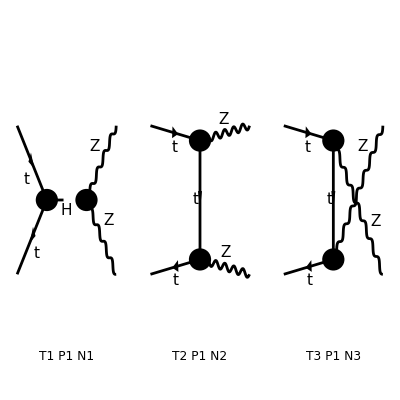

```mathematica
Process={F[3,{3}],-F[3,{3}]}-> {V[2],V[2]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

FeynAmpList(({F(3,{3}),-F(3,{3})}→{V(2),V(2)})→(F(3,{3,Col1}) | p1 | MT | {(2 Charge)/3,(2 ColorCharge)/(√3)}
-F(3,{3,Col2}) | p2 | MT | {-(2 Charge)/3,-(2 ColorCharge)/(√3)})→(V(2) | k1 | MZ | {}
V(2) | k2 | MZ | {}),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],1/(CW2 SW)ⅈ EL MW 1/((k1+k2)^2-MH2) g(Lor1,Lor2) SumOver(Col1,3,External) SumOver(Col2,3,External) Conjugate[ep](V(2),k1,Lor1) Conjugate[ep](V(2),k2,Lor2) v̄(p2,MT).(-(ⅈ EL MT om_- IndexDelta(Col1,Col2))/(2 MW SW)-(ⅈ EL MT om_+ IndexDelta(Col1,Col2))/(2 MW SW)).u(p1,MT)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==2),Integral[],SumOver(Col1,3,External) SumOver(Col2,3,External) 1/((p2-k2)^2-MT2) Conjugate[ep](V(2),k1,Lor1) Conjugate[ep](V(2),k2,Lor2) v̄(p2,MT).((ⅈ EL (1/2-(2 SW2)/3) IndexDelta(Col1,Col2) ga(Lor2).om_-)/(CW SW)-(2 ⅈ EL SW IndexDelta(Col1,Col2) ga(Lor2).om_+)/(3 CW)).(gs(k2-p2)+MT).((ⅈ EL (1/2-(2 SW2)/3) ga(Lor1).om_-)/(CW SW)-(2 ⅈ EL SW ga(Lor1).om_+)/(3 CW)).u(p1,MT)),FeynAmp(GraphID(Topology==3,Generic==1,Particles==1,Number==3),Integral[],SumOver(Col1,3,External) SumOver(Col2,3,External) 1/((p2-k1)^2-MT2) Conjugate[ep](V(2),k1,Lor1) Conjugate[ep](V(2),k2,Lor2) v̄(p2,MT).((ⅈ EL (1/2-(2 SW2)/3) IndexDelta(Col1,Col2) ga(Lor1).om_-)/(CW SW)-(2 ⅈ EL SW IndexDelta(Col1,Col2) ga(Lor1).om_+)/(3 CW)).(gs(k1-p2)+MT).((ⅈ EL (1/2-(2 SW2)/3) ga(Lor2).om_-)/(CW SW)-(2 ⅈ EL SW ga(Lor2).om_+)/(3 CW)).u(p1,MT)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 144 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/avasquez/fc-pol-1.frm

running FORM...

ok

1/(432 CW2^2 MZ2^2 SW2^2)Alfa2 π^2 (-648 MT2 (4 MT2-S) (12 MZ2^2-4 S MZ2+S^2) (Den(S,MH2))^2+36 MT2 ((9 S^3-((3-8 SW2)^2 T-9 U) (T-U) S+4 MT2 (4 (64 SW2^2-48 SW2-9) MZ2^2+36 S MZ2-8 SW2 (4 SW2-3) (T-U) MZ2-9 S^2+4 S SW2 (4 SW2-3) (T-U))-4 MZ2^2 (S (64 SW2^2-48 SW2-9)+(128 SW2^2-96 SW2+27) (T-U))-2 MZ2 (18 S^2-(3-8 SW2)^2 (T-U) S+(T-U) (9 T-(3-8 SW2)^2 U))) Den(T,MT2)+(9 S^3-(T-U) (9 T-(3-8 SW2)^2 U) S+4 MT2 (4 (64 SW2^2-48 SW2-9) MZ2^2+36 S MZ2+8 SW2 (4 SW2-3) (T-U) MZ2-9 S^2-4 S SW2 (4 SW2-3) (T-U))-4 MZ2^2 (S (64 SW2^2-48 SW2-9)-(128 SW2^2-96 SW2+27) (T-U))-2 MZ2 (18 S^2+(3-8 SW2)^2 (T-U) S+((3-8 SW2)^2 T-9 U) (T-U))) Den(U,MT2)) Den(S,MH2)+(4 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) MT2^4+4 (-2 S (256 SW2^4-384 SW2^3+720 SW2^2-432 SW2+81)+8 MZ2 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81)-(512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (3 T+U)) MT2^3+2 (2 (5632 SW2^4-8448 SW2^3+21024 SW2^2-13392 SW2+2511) MZ2^2+4 (S (512 SW2^4-768 SW2^3-1008 SW2^2+972 SW2-243)+(-5632 SW2^4+8448 SW2^3-8784 SW2^2+4212 SW2-729) T+(-512 SW2^4+768 SW2^3-1584 SW2^2+972 SW2-243) U) MZ2+S (2560 SW2^4-3840 SW2^3+6624 SW2^2-3888 SW2+729) T+S (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) U+6 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) T (T+U)) MT2^2+(128 (128 SW2^4-192 SW2^3+540 SW2^2-351 SW2+81) MZ2^3-4 (3 S (512 SW2^4-768 SW2^3+1248 SW2^2-720 SW2+135)+2 (9728 SW2^4-14592 SW2^3+16992 SW2^2-8640 SW2+1863) T+2 (4096 SW2^4-6144 SW2^3+6336 SW2^2-3024 SW2+567) U) MZ2^2-2 (4 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) S^2+((-512 SW2^4+768 SW2^3-8352 SW2^2+6048 SW2-1377) T+(512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) U) S-2 ((8704 SW2^4-13056 SW2^3+13248 SW2^2-6264 SW2+1053) T^2+6 (512 SW2^4-768 SW2^3+1104 SW2^2-612 SW2+135) U T+(512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) U^2)) MZ2+S^3 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81)-S^2 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (T-U)-4 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) T^2 (T+3 U)-4 S T ((1024 SW2^4-1536 SW2^3+2304 SW2^2-1296 SW2+243) T+(512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) U)) MT2+(512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (16 MZ2^4+8 (S-3 (3 T+U)) MZ2^3+4 (-5 S^2+7 T S-4 U S+12 T^2+U^2+14 T U) MZ2^2+2 (2 S^3+4 U S^2+(-3 T^2-3 U T+2 U^2) S-2 T (3 T^2+4 U T+U^2)) MZ2+T (-S^3+(T-U) S^2+2 T (T+U) S+4 T^2 U))) (Den(T,MT2))^2+(4 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) MT2^4+4 (-2 S (256 SW2^4-384 SW2^3+720 SW2^2-432 SW2+81)+8 MZ2 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81)-(512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (T+3 U)) MT2^3+2 (2 (5632 SW2^4-8448 SW2^3+21024 SW2^2-13392 SW2+2511) MZ2^2+4 (S (512 SW2^4-768 SW2^3-1008 SW2^2+972 SW2-243)+(-2048 SW2^4+3072 SW2^3-4176 SW2^2+2268 SW2-486) T-2 (2048 SW2^4-3072 SW2^3+3096 SW2^2-1458 SW2+243) U) MZ2+3 (S (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) T+S (512 SW2^4-768 SW2^3+1632 SW2^2-1008 SW2+189) U+2 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) U (T+U))) MT2^2+(128 (128 SW2^4-192 SW2^3+540 SW2^2-351 SW2+81) MZ2^3-4 (3 S (512 SW2^4-768 SW2^3+1248 SW2^2-720 SW2+135)+2 (10240 SW2^4-15360 SW2^3+16704 SW2^2-8208 SW2+1539) T+2 (3584 SW2^4-5376 SW2^3+6624 SW2^2-3456 SW2+891) U) MZ2^2-2 (4 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) S^2+((9728 SW2^4-14592 SW2^3+8928 SW2^2-2592 SW2+243) U-19 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) T) S-4 (3 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) T^2+2 (1024 SW2^4-1536 SW2^3+2088 SW2^2-1134 SW2+243) U T+(2560 SW2^4-3840 SW2^3+3600 SW2^2-1620 SW2+243) U^2)) MZ2+S^3 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81)-3 S^2 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (T-U)-4 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) U^2 (3 T+U)-2 S ((512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) T^2+4 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) U T+(512 SW2^4-768 SW2^3+2016 SW2^2-1296 SW2+243) U^2)) MT2+(512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (16 MZ2^4+8 (S-12 T) MZ2^3-4 (5 S^2-11 T S+8 U S-12 T^2+U^2-16 T U) MZ2^2+2 (2 S^3+(7 U-3 T) S^2+(-6 T^2-7 U T+9 U^2) S-2 (T+U)^3) MZ2+4 T U^3+S^3 (T-2 U)+2 S T U (T+U)+S^2 (T^2+U T-2 U^2))) (Den(U,MT2))^2-2 (4 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) MT2^4+4 (S (-512 SW2^4+768 SW2^3-2016 SW2^2+1296 SW2-243)+16 MZ2 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81)-2 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (T+U)) MT2^3+4 (3 (6656 SW2^4-9984 SW2^3+8928 SW2^2-3888 SW2+837) MZ2^2-(24 S (128 SW2^4-192 SW2^3+324 SW2^2-189 SW2+54)+(512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (23 T+17 U)) MZ2+81 S^2+4 S (256 SW2^4-384 SW2^3+720 SW2^2-432 SW2+81) T+S (512 SW2^4-768 SW2^3+2016 SW2^2-1296 SW2+243) U+(512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (T^2+4 U T+U^2)) MT2^2+(32 (1024 SW2^4-1536 SW2^3+1872 SW2^2-972 SW2+243) MZ2^3-4 (3 S (2560 SW2^4-3840 SW2^3+1056 SW2^2+288 SW2-27)+2 (5888 SW2^4-8832 SW2^3+11088 SW2^2-5832 SW2+1215) T+2 (1792 SW2^4-2688 SW2^3+4176 SW2^2-2376 SW2+567) U) MZ2^2+2 (32 SW2 (64 SW2^3-96 SW2^2+27) S^2+4 (1792 SW2^4-2688 SW2^3+3672 SW2^2-1998 SW2+405) T S+8 (128 SW2^4-192 SW2^3+540 SW2^2-351 SW2+81) U S+(6656 SW2^4-9984 SW2^3+12672 SW2^2-6696 SW2+1215) T^2+(512 SW2^4-768 SW2^3+2304 SW2^2-1512 SW2+243) U^2+2 (12800 SW2^4-19200 SW2^3+20160 SW2^2-9720 SW2+1863) T U) MZ2+S^3 (512 SW2^4-768 SW2^3+1440 SW2^2-864 SW2+81)-2 S^2 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (T-U)-8 (512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) T U (T+U)-S ((2560 SW2^4-3840 SW2^3+4896 SW2^2-2592 SW2+405) T^2+6 (512 SW2^4-768 SW2^3+1440 SW2^2-864 SW2+189) U T+(512 SW2^4-768 SW2^3+1440 SW2^2-864 SW2+81) U^2)) MT2-(512 SW2^4-768 SW2^3+864 SW2^2-432 SW2+81) (32 MZ2^4+4 (2 S+T-9 U) MZ2^3+2 (2 S^2-6 T S+8 U S-7 T^2+9 U^2-16 T U) MZ2^2+(3 (T-U) S^2+(7 T^2+6 U T-5 U^2) S+2 (T^3+10 U T^2+7 U^2 T-2 U^3)) MZ2-4 T^2 U^2-S T (T+U)^2+S^3 U+S^2 (U^2-T^2))) Den(T,MT2) Den(U,MT2))

```mathematica
resFCttZZ=square1/.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y)}
```

1/(6912 cw^4 MZ2^2 sw^4)ee^4 (-(648 MT2 (4 MT2-S) (12 MZ2^2-4 S MZ2+S^2))/(S-MH2)^2+1/(S-MH2)36 MT2 (1/(U-MT2)(9 S^3-(T-U) (9 T-(3-8 sw^2)^2 U) S+4 MT2 (4 (64 sw^4-48 sw^2-9) MZ2^2+36 S MZ2+8 sw^2 (4 sw^2-3) (T-U) MZ2-9 S^2-4 S sw^2 (4 sw^2-3) (T-U))-4 MZ2^2 (S (64 sw^4-48 sw^2-9)-(128 sw^4-96 sw^2+27) (T-U))-2 MZ2 (18 S^2+(3-8 sw^2)^2 (T-U) S+((3-8 sw^2)^2 T-9 U) (T-U)))+1/(T-MT2)(9 S^3-((3-8 sw^2)^2 T-9 U) (T-U) S+4 MT2 (4 (64 sw^4-48 sw^2-9) MZ2^2+36 S MZ2-8 sw^2 (4 sw^2-3) (T-U) MZ2-9 S^2+4 S sw^2 (4 sw^2-3) (T-U))-4 MZ2^2 (S (64 sw^4-48 sw^2-9)+(128 sw^4-96 sw^2+27) (T-U))-2 MZ2 (18 S^2-(3-8 sw^2)^2 (T-U) S+(T-U) (9 T-(3-8 sw^2)^2 U))))+1/(T-MT2)^2(4 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) MT2^4+4 (-2 S (256 sw^8-384 sw^6+720 sw^4-432 sw^2+81)+8 MZ2 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81)-(512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (3 T+U)) MT2^3+2 (2 (5632 sw^8-8448 sw^6+21024 sw^4-13392 sw^2+2511) MZ2^2+4 (S (512 sw^8-768 sw^6-1008 sw^4+972 sw^2-243)+(-5632 sw^8+8448 sw^6-8784 sw^4+4212 sw^2-729) T+(-512 sw^8+768 sw^6-1584 sw^4+972 sw^2-243) U) MZ2+S (2560 sw^8-3840 sw^6+6624 sw^4-3888 sw^2+729) T+S (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) U+6 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) T (T+U)) MT2^2+(128 (128 sw^8-192 sw^6+540 sw^4-351 sw^2+81) MZ2^3-4 (3 S (512 sw^8-768 sw^6+1248 sw^4-720 sw^2+135)+2 (9728 sw^8-14592 sw^6+16992 sw^4-8640 sw^2+1863) T+2 (4096 sw^8-6144 sw^6+6336 sw^4-3024 sw^2+567) U) MZ2^2-2 (4 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) S^2+((-512 sw^8+768 sw^6-8352 sw^4+6048 sw^2-1377) T+(512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) U) S-2 ((8704 sw^8-13056 sw^6+13248 sw^4-6264 sw^2+1053) T^2+6 (512 sw^8-768 sw^6+1104 sw^4-612 sw^2+135) U T+(512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) U^2)) MZ2+S^3 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81)-S^2 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (T-U)-4 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) T^2 (T+3 U)-4 S T ((1024 sw^8-1536 sw^6+2304 sw^4-1296 sw^2+243) T+(512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) U)) MT2+(512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (16 MZ2^4+8 (S-3 (3 T+U)) MZ2^3+4 (-5 S^2+7 T S-4 U S+12 T^2+U^2+14 T U) MZ2^2+2 (2 S^3+4 U S^2+(-3 T^2-3 U T+2 U^2) S-2 T (3 T^2+4 U T+U^2)) MZ2+T (-S^3+(T-U) S^2+2 T (T+U) S+4 T^2 U)))+1/(U-MT2)^2(4 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) MT2^4+4 (-2 S (256 sw^8-384 sw^6+720 sw^4-432 sw^2+81)+8 MZ2 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81)-(512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (T+3 U)) MT2^3+2 (2 (5632 sw^8-8448 sw^6+21024 sw^4-13392 sw^2+2511) MZ2^2+4 (S (512 sw^8-768 sw^6-1008 sw^4+972 sw^2-243)+(-2048 sw^8+3072 sw^6-4176 sw^4+2268 sw^2-486) T-2 (2048 sw^8-3072 sw^6+3096 sw^4-1458 sw^2+243) U) MZ2+3 (S (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) T+S (512 sw^8-768 sw^6+1632 sw^4-1008 sw^2+189) U+2 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) U (T+U))) MT2^2+(128 (128 sw^8-192 sw^6+540 sw^4-351 sw^2+81) MZ2^3-4 (3 S (512 sw^8-768 sw^6+1248 sw^4-720 sw^2+135)+2 (10240 sw^8-15360 sw^6+16704 sw^4-8208 sw^2+1539) T+2 (3584 sw^8-5376 sw^6+6624 sw^4-3456 sw^2+891) U) MZ2^2-2 (4 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) S^2+((9728 sw^8-14592 sw^6+8928 sw^4-2592 sw^2+243) U-19 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) T) S-4 (3 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) T^2+2 (1024 sw^8-1536 sw^6+2088 sw^4-1134 sw^2+243) U T+(2560 sw^8-3840 sw^6+3600 sw^4-1620 sw^2+243) U^2)) MZ2+S^3 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81)-3 S^2 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (T-U)-4 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) U^2 (3 T+U)-2 S ((512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) T^2+4 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) U T+(512 sw^8-768 sw^6+2016 sw^4-1296 sw^2+243) U^2)) MT2+(512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (16 MZ2^4+8 (S-12 T) MZ2^3-4 (5 S^2-11 T S+8 U S-12 T^2+U^2-16 T U) MZ2^2+2 (2 S^3+(7 U-3 T) S^2+(-6 T^2-7 U T+9 U^2) S-2 (T+U)^3) MZ2+4 T U^3+S^3 (T-2 U)+2 S T U (T+U)+S^2 (T^2+U T-2 U^2)))-1/((T-MT2) (U-MT2))2 (4 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) MT2^4+4 (S (-512 sw^8+768 sw^6-2016 sw^4+1296 sw^2-243)+16 MZ2 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81)-2 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (T+U)) MT2^3+4 (3 (6656 sw^8-9984 sw^6+8928 sw^4-3888 sw^2+837) MZ2^2-(24 S (128 sw^8-192 sw^6+324 sw^4-189 sw^2+54)+(512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (23 T+17 U)) MZ2+81 S^2+4 S (256 sw^8-384 sw^6+720 sw^4-432 sw^2+81) T+S (512 sw^8-768 sw^6+2016 sw^4-1296 sw^2+243) U+(512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (T^2+4 U T+U^2)) MT2^2+(32 (1024 sw^8-1536 sw^6+1872 sw^4-972 sw^2+243) MZ2^3-4 (3 S (2560 sw^8-3840 sw^6+1056 sw^4+288 sw^2-27)+2 (5888 sw^8-8832 sw^6+11088 sw^4-5832 sw^2+1215) T+2 (1792 sw^8-2688 sw^6+4176 sw^4-2376 sw^2+567) U) MZ2^2+2 (32 S^2 (64 sw^6-96 sw^4+27) sw^2+(6656 sw^8-9984 sw^6+12672 sw^4-6696 sw^2+1215) T^2+(512 sw^8-768 sw^6+2304 sw^4-1512 sw^2+243) U^2+4 S (1792 sw^8-2688 sw^6+3672 sw^4-1998 sw^2+405) T+8 S (128 sw^8-192 sw^6+540 sw^4-351 sw^2+81) U+2 (12800 sw^8-19200 sw^6+20160 sw^4-9720 sw^2+1863) T U) MZ2+S^3 (512 sw^8-768 sw^6+1440 sw^4-864 sw^2+81)-2 S^2 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (T-U)-8 (512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) T U (T+U)-S ((2560 sw^8-3840 sw^6+4896 sw^4-2592 sw^2+405) T^2+6 (512 sw^8-768 sw^6+1440 sw^4-864 sw^2+189) U T+(512 sw^8-768 sw^6+1440 sw^4-864 sw^2+81) U^2)) MT2-(512 sw^8-768 sw^6+864 sw^4-432 sw^2+81) (32 MZ2^4+4 (2 S+T-9 U) MZ2^3+2 (2 S^2-6 T S+8 U S-7 T^2+9 U^2-16 T U) MZ2^2+(3 (T-U) S^2+(7 T^2+6 U T-5 U^2) S+2 (T^3+10 U T^2+7 U^2 T-2 U^3)) MZ2-4 T^2 U^2-S T (T+U)^2+S^3 U+S^2 (U^2-T^2))))

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARttZZ=Get["resANATARttZZ.m"];
```

```mathematica
FullSimplify[resANATARttZZ- 4 resFCttZZ,{S+T+U==2MZ2+2MT2,cw^2+sw^2==1}]
```

0

# Lepton and Weak boson Processes

## τ τ ->τ τ

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
Atatatata=GenerateAmplitude[{ta,tabar}->{ta,tabar},OutputName->"tatatata",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tatatata.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tatatata/tatatata_0

Computing amplitudes...

A total of 8 diagrams have been generated for the process {ta, tabar} -> {ta, tabar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{ta(p1),tabar(p2)}→{ta(p3),tabar(p4)}},Total→8,Name→tatatata,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MTA^2,p3.p3→MTA^2,1/(p3.p3)→1/MTA^2,p4^2→MTA^2,p4.p4→MTA^2,1/(p4.p4)→1/MTA^2,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (2 MTA^2-T),p2.p3→1/2 (2 MTA^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(2 MTA^2-T),1/(p2.p3)→2/(2 MTA^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→1/4 ⅈ Den(-p1-p2,MZ) (ū)_Spin2(p3,MTA) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) v_Spin4(p4,MTA) ((GC54-GC52) (γ^5)_(Spin1 Spin3)+(GC52+GC54) 𝕀_Spin3Spin1) ((GC54-GC52) (γ^5)_(Spin2 Spin4)+(GC52+GC54) 𝕀_Spin2Spin4),DiagramID(2)→-ⅈ GC53^2 𝕀_Spin3Spin1 𝕀_Spin2Spin4 Den(-p1-p2,MH) (ū)_Spin2(p3,MTA) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) v_Spin4(p4,MTA),DiagramID(3)→ⅈ GC3^2 Den(-p1-p2,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) (ū)_Spin2(p3,MTA) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) v_Spin4(p4,MTA),DiagramID(4)→1/4 ⅈ Den(-p1-p2,MZ) (ū)_Spin2(p3,MTA) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) v_Spin4(p4,MTA) ((GC35-GC15) (γ^iLor2 γ^5)_(Spin1 Spin3)+(GC15+GC35) (γ^iLor2)_(Spin1 Spin3)) ((GC35-GC15) (γ^iLor2 γ^5)_(Spin2 Spin4)+(GC15+GC35) (γ^iLor2)_(Spin2 Spin4)),DiagramID(5)→-1/4 ⅈ Den(p3-p1,MZ) (ū)_Spin2(p3,MTA) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) v_Spin4(p4,MTA) ((GC54-GC52) (γ^5)_(Spin1 Spin2)+(GC52+GC54) 𝕀_Spin2Spin1) ((GC54-GC52) (γ^5)_(Spin3 Spin4)+(GC52+GC54) 𝕀_Spin3Spin4),DiagramID(6)→ⅈ GC53^2 𝕀_Spin2Spin1 𝕀_Spin3Spin4 Den(p3-p1,MH) (ū)_Spin2(p3,MTA) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) v_Spin4(p4,MTA),DiagramID(7)→-ⅈ GC3^2 Den(p3-p1,0) (γ^iLor2)_(Spin1 Spin2) (γ^iLor2)_(Spin3 Spin4) (ū)_Spin2(p3,MTA) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) v_Spin4(p4,MTA),DiagramID(8)→-1/4 ⅈ Den(p3-p1,MZ) (ū)_Spin2(p3,MTA) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) v_Spin4(p4,MTA) ((GC35-GC15) (γ^iLor2 γ^5)_(Spin1 Spin2)+(GC15+GC35) (γ^iLor2)_(Spin1 Spin2)) ((GC35-GC15) (γ^iLor2 γ^5)_(Spin3 Spin4)+(GC15+GC35) (γ^iLor2)_(Spin3 Spin4))}|>

```mathematica
AtatatataC=GenerateAmplitudeConjugate[{ta,tabar}->{ta,tabar},OutputName->"tatatata",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tatatata.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tatatata/tatatata_0

Computing amplitudes...

A total of 8 diagrams have been generated for the process {ta, tabar} -> {ta, tabar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{ta(p1),tabar(p2)}→{ta(p3),tabar(p4)}},Total→8,Name→tatatata,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MTA^2,p3.p3→MTA^2,1/(p3.p3)→1/MTA^2,p4^2→MTA^2,p4.p4→MTA^2,1/(p4.p4)→1/MTA^2,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (2 MTA^2-T),p2.p3→1/2 (2 MTA^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(2 MTA^2-T),1/(p2.p3)→2/(2 MTA^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-1/4 ⅈ Den(-p1-p2,MZ) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) (u^†)_SpinC2(p3,MTA) ((v̄)^†)_SpinC4(p4,MTA) ((GC52-GC54) (γ^5)_(SpinC1 SpinC3)+(GC52+GC54) 𝕀_SpinC1SpinC3) ((GC52-GC54) (γ^5)_(SpinC2 SpinC4)+(GC52+GC54) 𝕀_SpinC4SpinC2),DiagramID(2)→ⅈ GC53^2 𝕀_SpinC1SpinC3 𝕀_SpinC4SpinC2 Den(-p1-p2,MH) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) (u^†)_SpinC2(p3,MTA) ((v̄)^†)_SpinC4(p4,MTA),DiagramID(3)→-ⅈ GC3^2 Den(-p1-p2,0) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) (u^†)_SpinC2(p3,MTA) ((v̄)^†)_SpinC4(p4,MTA),DiagramID(4)→-1/4 ⅈ Den(-p1-p2,MZ) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) (u^†)_SpinC2(p3,MTA) ((v̄)^†)_SpinC4(p4,MTA) ((GC15-GC35) (γ^5 γ^iLorC2)_(SpinC1 SpinC3)+(GC15+GC35) (γ^iLorC2)_(SpinC1 SpinC3)) ((GC15-GC35) (γ^5 γ^iLorC2)_(SpinC2 SpinC4)+(GC15+GC35) (γ^iLorC2)_(SpinC2 SpinC4)),DiagramID(5)→1/4 ⅈ Den(p3-p1,MZ) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) (u^†)_SpinC2(p3,MTA) ((v̄)^†)_SpinC4(p4,MTA) ((GC52-GC54) (γ^5)_(SpinC1 SpinC2)+(GC52+GC54) 𝕀_SpinC1SpinC2) ((GC52-GC54) (γ^5)_(SpinC3 SpinC4)+(GC52+GC54) 𝕀_SpinC4SpinC3),DiagramID(6)→-ⅈ GC53^2 𝕀_SpinC1SpinC2 𝕀_SpinC4SpinC3 Den(p3-p1,MH) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) (u^†)_SpinC2(p3,MTA) ((v̄)^†)_SpinC4(p4,MTA),DiagramID(7)→ⅈ GC3^2 Den(p3-p1,0) (γ^iLorC2)_(SpinC1 SpinC2) (γ^iLorC2)_(SpinC3 SpinC4) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) (u^†)_SpinC2(p3,MTA) ((v̄)^†)_SpinC4(p4,MTA),DiagramID(8)→1/4 ⅈ Den(p3-p1,MZ) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) (u^†)_SpinC2(p3,MTA) ((v̄)^†)_SpinC4(p4,MTA) ((GC15-GC35) (γ^5 γ^iLorC2)_(SpinC1 SpinC2)+(GC15+GC35) (γ^iLorC2)_(SpinC1 SpinC2)) ((GC15-GC35) (γ^5 γ^iLorC2)_(SpinC3 SpinC4)+(GC15+GC35) (γ^iLorC2)_(SpinC3 SpinC4))}|>

```mathematica
AmpSQtatatata=GenerateAmplitudeSquare[Atatatata,AtatatataC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{ta(p1),tabar(p2)}→{ta(p3),tabar(p4)}},Name→tatatata,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MTA^2,p3.p3→MTA^2,1/(p3.p3)→1/MTA^2,p4^2→MTA^2,p4.p4→MTA^2,1/(p4.p4)→1/MTA^2,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (2 MTA^2-T),p2.p3→1/2 (2 MTA^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(2 MTA^2-T),1/(p2.p3)→2/(2 MTA^2-U),p4→p1+p2-p3},Amplitudes→(16 S (Den(-p1-p2,MZ))^2 MTA^6)/vev^4+(16 S (Den(p3-p1,MH))^2 MTA^6)/vev^4+(16 U (Den(p3-p1,MH))^2 MTA^6)/vev^4+(16 T (Den(p3-p1,MZ))^2 MTA^6)/vev^4+(16 S Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^6)/vev^4+(4 (4 MTA^2-S) (T+U) (Den(-p1-p2,MH))^2 MTA^4)/vev^4+2 ee^4 (Den(-p1-p2,MZ))^2 MTA^4-(9 ee^4 sw2^2 (Den(-p1-p2,MZ))^2 MTA^4)/cw^4-(12 ee^4 sw2 (Den(-p1-p2,MZ))^2 MTA^4)/cw^2+(4 cw^2 ee^4 (Den(-p1-p2,MZ))^2 MTA^4)/sw2-(cw^4 ee^4 (Den(-p1-p2,MZ))^2 MTA^4)/sw2^2-(4 ee^2 S (Den(-p1-p2,MZ))^2 MTA^4)/vev^2-(2 ee^2 S sw2 (Den(-p1-p2,MZ))^2 MTA^4)/(cw^2 vev^2)-(2 cw^2 ee^2 S (Den(-p1-p2,MZ))^2 MTA^4)/(sw2 vev^2)-(4 S T (Den(-p1-p2,MZ))^2 MTA^4)/vev^4-(4 S U (Den(-p1-p2,MZ))^2 MTA^4)/vev^4-(4 S T (Den(p3-p1,MH))^2 MTA^4)/vev^4-(4 T U (Den(p3-p1,MH))^2 MTA^4)/vev^4+2 ee^4 (Den(p3-p1,MZ))^2 MTA^4-(9 ee^4 sw2^2 (Den(p3-p1,MZ))^2 MTA^4)/cw^4-(12 ee^4 sw2 (Den(p3-p1,MZ))^2 MTA^4)/cw^2+(4 cw^2 ee^4 (Den(p3-p1,MZ))^2 MTA^4)/sw2-(cw^4 ee^4 (Den(p3-p1,MZ))^2 MTA^4)/sw2^2-(4 ee^2 T (Den(p3-p1,MZ))^2 MTA^4)/vev^2-(2 ee^2 sw2 T (Den(p3-p1,MZ))^2 MTA^4)/(cw^2 vev^2)-(2 cw^2 ee^2 T (Den(p3-p1,MZ))^2 MTA^4)/(sw2 vev^2)-(4 S T (Den(p3-p1,MZ))^2 MTA^4)/vev^4-(4 T U (Den(p3-p1,MZ))^2 MTA^4)/vev^4+(16 ee^2 S Den(-p1-p2,MZ) Den(p3-p1,0) MTA^4)/vev^2-(20 ee^2 S Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^4)/vev^2+(26 ee^2 S sw2 Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^4)/(cw^2 vev^2)-(12 ee^2 U Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^4)/vev^2+(6 ee^2 sw2 U Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^4)/(cw^2 vev^2)-(2 cw^2 ee^2 U Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^4)/(sw2 vev^2)+(2 cw^2 ee^2 S Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^4)/(sw2 vev^2)-(4 S T Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^4)/vev^4+(32 ee^2 S Den(p3-p1,0) Den(p3-p1,MH) MTA^4)/vev^2-(32 ee^2 U Den(p3-p1,0) Den(p3-p1,MH) MTA^4)/vev^2+4 ee^4 Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4-(18 ee^4 sw2^2 Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/cw^4-(24 ee^4 sw2 Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/cw^2+(8 cw^2 ee^4 Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/sw2-(2 cw^4 ee^4 Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/sw2^2-(12 ee^2 S Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/vev^2+(6 ee^2 S sw2 Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/(cw^2 vev^2)-(12 ee^2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/vev^2+(6 ee^2 sw2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/(cw^2 vev^2)-(2 cw^2 ee^2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/(sw2 vev^2)-(2 cw^2 ee^2 S Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/(sw2 vev^2)+(4 S T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^4)/vev^4-(12 ee^2 S Den(p3-p1,MH) Den(p3-p1,MZ) MTA^4)/vev^2+(18 ee^2 S sw2 Den(p3-p1,MH) Den(p3-p1,MZ) MTA^4)/(cw^2 vev^2)+(12 ee^2 U Den(p3-p1,MH) Den(p3-p1,MZ) MTA^4)/vev^2-(18 ee^2 sw2 U Den(p3-p1,MH) Den(p3-p1,MZ) MTA^4)/(cw^2 vev^2)-(2 cw^2 ee^2 U Den(p3-p1,MH) Den(p3-p1,MZ) MTA^4)/(sw2 vev^2)+(2 cw^2 ee^2 S Den(p3-p1,MH) Den(p3-p1,MZ) MTA^4)/(sw2 vev^2)+(35 ee^4 S sw2^2 (Den(-p1-p2,MZ))^2 MTA^2)/(2 cw^4)+10 ee^4 S (Den(-p1-p2,MZ))^2 MTA^2-(17 ee^4 S sw2 (Den(-p1-p2,MZ))^2 MTA^2)/cw^2+4 ee^4 T (Den(-p1-p2,MZ))^2 MTA^2+(15 ee^4 sw2^2 T (Den(-p1-p2,MZ))^2 MTA^2)/(2 cw^4)-(3 ee^4 sw2 T (Den(-p1-p2,MZ))^2 MTA^2)/cw^2-(cw^2 ee^4 T (Den(-p1-p2,MZ))^2 MTA^2)/sw2+(cw^4 ee^4 T (Den(-p1-p2,MZ))^2 MTA^2)/(2 sw2^2)+4 ee^4 U (Den(-p1-p2,MZ))^2 MTA^2+(15 ee^4 sw2^2 U (Den(-p1-p2,MZ))^2 MTA^2)/(2 cw^4)-(3 ee^4 sw2 U (Den(-p1-p2,MZ))^2 MTA^2)/cw^2-(cw^2 ee^4 U (Den(-p1-p2,MZ))^2 MTA^2)/sw2+(cw^4 ee^4 U (Den(-p1-p2,MZ))^2 MTA^2)/(2 sw2^2)-(3 cw^2 ee^4 S (Den(-p1-p2,MZ))^2 MTA^2)/sw2+(cw^4 ee^4 S (Den(-p1-p2,MZ))^2 MTA^2)/(2 sw2^2)+16 ee^4 S (Den(p3-p1,0))^2 MTA^2+48 ee^4 T (Den(p3-p1,0))^2 MTA^2+16 ee^4 U (Den(p3-p1,0))^2 MTA^2+(15 ee^4 S sw2^2 (Den(p3-p1,MZ))^2 MTA^2)/(2 cw^4)+4 ee^4 S (Den(p3-p1,MZ))^2 MTA^2-(3 ee^4 S sw2 (Den(p3-p1,MZ))^2 MTA^2)/cw^2+10 ee^4 T (Den(p3-p1,MZ))^2 MTA^2+(35 ee^4 sw2^2 T (Den(p3-p1,MZ))^2 MTA^2)/(2 cw^4)-(17 ee^4 sw2 T (Den(p3-p1,MZ))^2 MTA^2)/cw^2-(3 cw^2 ee^4 T (Den(p3-p1,MZ))^2 MTA^2)/sw2+(cw^4 ee^4 T (Den(p3-p1,MZ))^2 MTA^2)/(2 sw2^2)+4 ee^4 U (Den(p3-p1,MZ))^2 MTA^2+(15 ee^4 sw2^2 U (Den(p3-p1,MZ))^2 MTA^2)/(2 cw^4)-(3 ee^4 sw2 U (Den(p3-p1,MZ))^2 MTA^2)/cw^2-(cw^2 ee^4 U (Den(p3-p1,MZ))^2 MTA^2)/sw2+(cw^4 ee^4 U (Den(p3-p1,MZ))^2 MTA^2)/(2 sw2^2)-(cw^2 ee^4 S (Den(p3-p1,MZ))^2 MTA^2)/sw2+(cw^4 ee^4 S (Den(p3-p1,MZ))^2 MTA^2)/(2 sw2^2)-20 ee^4 S Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2+(26 ee^4 S sw2 Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2)/cw^2-12 ee^4 T Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2+(30 ee^4 sw2 T Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2)/cw^2+(6 cw^2 ee^4 T Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2)/sw2+12 ee^4 U Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2-(6 ee^4 sw2 U Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2)/cw^2+(2 cw^2 ee^4 U Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2)/sw2+(2 cw^2 ee^4 S Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2)/sw2-(8 ee^2 S T Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2)/vev^2-(8 ee^2 S U Den(-p1-p2,MZ) Den(p3-p1,0) MTA^2)/vev^2+(4 ee^2 S T Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^2)/vev^2-(4 ee^2 S sw2 T Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^2)/(cw^2 vev^2)+(4 ee^2 T U Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^2)/vev^2-(4 ee^2 sw2 T U Den(-p1-p2,MZ) Den(p3-p1,MH) MTA^2)/(cw^2 vev^2)+(21 ee^4 S sw2^2 Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/cw^4+10 ee^4 S Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2-(12 ee^4 S sw2 Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/cw^2+10 ee^4 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2+(21 ee^4 sw2^2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/cw^4-(12 ee^4 sw2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/cw^2-(4 cw^2 ee^4 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/sw2+(cw^4 ee^4 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/sw2^2-4 ee^4 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2+(3 ee^4 sw2^2 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/cw^4+(18 ee^4 sw2 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/cw^2-(2 cw^2 ee^4 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/sw2+(cw^4 ee^4 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/sw2^2-(4 cw^2 ee^4 S Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/sw2+(cw^4 ee^4 S Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/sw2^2+(8 ee^2 S T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/vev^2-(8 ee^2 S sw2 T Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/(cw^2 vev^2)+(4 ee^2 S U Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/vev^2-(4 ee^2 S sw2 U Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/(cw^2 vev^2)+(4 ee^2 T U Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/vev^2-(4 ee^2 sw2 T U Den(-p1-p2,MZ) Den(p3-p1,MZ) MTA^2)/(cw^2 vev^2)-12 ee^4 S Den(p3-p1,0) Den(p3-p1,MZ) MTA^2+(18 ee^4 S sw2 Den(p3-p1,0) Den(p3-p1,MZ) MTA^2)/cw^2-36 ee^4 T Den(p3-p1,0) Den(p3-p1,MZ) MTA^2+(54 ee^4 sw2 T Den(p3-p1,0) Den(p3-p1,MZ) MTA^2)/cw^2+(6 cw^2 ee^4 T Den(p3-p1,0) Den(p3-p1,MZ) MTA^2)/sw2-12 ee^4 U Den(p3-p1,0) Den(p3-p1,MZ) MTA^2+(18 ee^4 sw2 U Den(p3-p1,0) Den(p3-p1,MZ) MTA^2)/cw^2+(2 cw^2 ee^4 U Den(p3-p1,0) Den(p3-p1,MZ) MTA^2)/sw2+(2 cw^2 ee^4 S Den(p3-p1,0) Den(p3-p1,MZ) MTA^2)/sw2+1/(cw^2 sw2 vev^4)2 Den(-p1-p2,MH) (ee^2 MTA^2 T vev^2 Den(p3-p1,MZ) cw^4-ee^2 MTA^2 U vev^2 Den(p3-p1,MZ) cw^4+4 ee^2 sw2 (2 MTA^2 (3 T+U)-S (T+U)) vev^2 Den(p3-p1,0) cw^2+2 MTA^2 S sw2 T Den(p3-p1,MH) cw^2-8 MTA^4 sw2 U Den(p3-p1,MH) cw^2-10 ee^2 MTA^2 sw2 T vev^2 Den(p3-p1,MZ) cw^2+2 ee^2 S sw2 T vev^2 Den(p3-p1,MZ) cw^2-6 ee^2 MTA^2 sw2 U vev^2 Den(p3-p1,MZ) cw^2+2 ee^2 S sw2 U vev^2 Den(p3-p1,MZ) cw^2+8 MTA^4 sw2 T Den(p3-p1,MZ) cw^2-2 MTA^2 S sw2 T Den(p3-p1,MZ) cw^2+ee^2 MTA^2 (cw^2-3 sw2)^2 (T-U) vev^2 Den(-p1-p2,MZ)+13 ee^2 MTA^2 sw2^2 T vev^2 Den(p3-p1,MZ)-2 ee^2 S sw2^2 T vev^2 Den(p3-p1,MZ)+3 ee^2 MTA^2 sw2^2 U vev^2 Den(p3-p1,MZ)-2 ee^2 S sw2^2 U vev^2 Den(p3-p1,MZ)) MTA^2+8 ee^4 (2 (3 S+T+U) MTA^2-2 T U-S (T+U)) (Den(-p1-p2,0))^2-(2 ee^4 S sw2^2 T (Den(-p1-p2,MZ))^2)/cw^4-2 ee^4 S T (Den(-p1-p2,MZ))^2+(4 ee^4 S sw2 T (Den(-p1-p2,MZ))^2)/cw^2-(17 ee^4 S sw2^2 U (Den(-p1-p2,MZ))^2)/(4 cw^4)-3/2 ee^4 S U (Den(-p1-p2,MZ))^2+(ee^4 S sw2 U (Den(-p1-p2,MZ))^2)/cw^2-7/2 ee^4 T U (Den(-p1-p2,MZ))^2-(25 ee^4 sw2^2 T U (Den(-p1-p2,MZ))^2)/(4 cw^4)+(5 ee^4 sw2 T U (Den(-p1-p2,MZ))^2)/cw^2+(cw^2 ee^4 T U (Den(-p1-p2,MZ))^2)/sw2-(cw^4 ee^4 T U (Den(-p1-p2,MZ))^2)/(4 sw2^2)+(cw^2 ee^4 S U (Den(-p1-p2,MZ))^2)/sw2-(cw^4 ee^4 S U (Den(-p1-p2,MZ))^2)/(4 sw2^2)-8 ee^4 S T (Den(p3-p1,0))^2-16 ee^4 S U (Den(p3-p1,0))^2-8 ee^4 T U (Den(p3-p1,0))^2-(2 ee^4 S sw2^2 T (Den(p3-p1,MZ))^2)/cw^4-2 ee^4 S T (Den(p3-p1,MZ))^2+(4 ee^4 S sw2 T (Den(p3-p1,MZ))^2)/cw^2-(25 ee^4 S sw2^2 U (Den(p3-p1,MZ))^2)/(4 cw^4)-7/2 ee^4 S U (Den(p3-p1,MZ))^2+(5 ee^4 S sw2 U (Den(p3-p1,MZ))^2)/cw^2-3/2 ee^4 T U (Den(p3-p1,MZ))^2-(17 ee^4 sw2^2 T U (Den(p3-p1,MZ))^2)/(4 cw^4)+(ee^4 sw2 T U (Den(p3-p1,MZ))^2)/cw^2+(cw^2 ee^4 T U (Den(p3-p1,MZ))^2)/sw2-(cw^4 ee^4 T U (Den(p3-p1,MZ))^2)/(4 sw2^2)+(cw^2 ee^4 S U (Den(p3-p1,MZ))^2)/sw2-(cw^4 ee^4 S U (Den(p3-p1,MZ))^2)/(4 sw2^2)+4 ee^4 S U Den(-p1-p2,MZ) Den(p3-p1,0)-(10 ee^4 S sw2 U Den(-p1-p2,MZ) Den(p3-p1,0))/cw^2+4 ee^4 T U Den(-p1-p2,MZ) Den(p3-p1,0)-(10 ee^4 sw2 T U Den(-p1-p2,MZ) Den(p3-p1,0))/cw^2-(2 cw^2 ee^4 T U Den(-p1-p2,MZ) Den(p3-p1,0))/sw2-(2 cw^2 ee^4 S U Den(-p1-p2,MZ) Den(p3-p1,0))/sw2-(17 ee^4 S sw2^2 U Den(-p1-p2,MZ) Den(p3-p1,MZ))/(2 cw^4)-3 ee^4 S U Den(-p1-p2,MZ) Den(p3-p1,MZ)+(2 ee^4 S sw2 U Den(-p1-p2,MZ) Den(p3-p1,MZ))/cw^2-3 ee^4 T U Den(-p1-p2,MZ) Den(p3-p1,MZ)-(17 ee^4 sw2^2 T U Den(-p1-p2,MZ) Den(p3-p1,MZ))/(2 cw^4)+(2 ee^4 sw2 T U Den(-p1-p2,MZ) Den(p3-p1,MZ))/cw^2+(2 cw^2 ee^4 T U Den(-p1-p2,MZ) Den(p3-p1,MZ))/sw2-(cw^4 ee^4 T U Den(-p1-p2,MZ) Den(p3-p1,MZ))/(2 sw2^2)+(2 cw^2 ee^4 S U Den(-p1-p2,MZ) Den(p3-p1,MZ))/sw2-(cw^4 ee^4 S U Den(-p1-p2,MZ) Den(p3-p1,MZ))/(2 sw2^2)+8 ee^4 S T Den(p3-p1,0) Den(p3-p1,MZ)-(8 ee^4 S sw2 T Den(p3-p1,0) Den(p3-p1,MZ))/cw^2+12 ee^4 S U Den(p3-p1,0) Den(p3-p1,MZ)-(18 ee^4 S sw2 U Den(p3-p1,0) Den(p3-p1,MZ))/cw^2+4 ee^4 T U Den(p3-p1,0) Den(p3-p1,MZ)-(10 ee^4 sw2 T U Den(p3-p1,0) Den(p3-p1,MZ))/cw^2-(2 cw^2 ee^4 T U Den(p3-p1,0) Den(p3-p1,MZ))/sw2-(2 cw^2 ee^4 S U Den(p3-p1,0) Den(p3-p1,MZ))/sw2+1/(cw^2 sw2 vev^2)2 ee^2 Den(-p1-p2,0) (3 ee^2 MTA^2 S vev^2 Den(p3-p1,MZ) cw^4+ee^2 MTA^2 T vev^2 Den(p3-p1,MZ) cw^4+ee^2 MTA^2 U vev^2 Den(p3-p1,MZ) cw^4-ee^2 S U vev^2 Den(p3-p1,MZ) cw^4-ee^2 T U vev^2 Den(p3-p1,MZ) cw^4+16 MTA^4 sw2 (T-U) Den(-p1-p2,MH) cw^2+24 ee^2 MTA^2 S sw2 vev^2 Den(p3-p1,0) cw^2+24 ee^2 MTA^2 sw2 T vev^2 Den(p3-p1,0) cw^2-8 ee^2 MTA^2 sw2 U vev^2 Den(p3-p1,0) cw^2-8 ee^2 S sw2 U vev^2 Den(p3-p1,0) cw^2-8 ee^2 sw2 T U vev^2 Den(p3-p1,0) cw^2+24 MTA^4 S sw2 Den(p3-p1,MH) cw^2-4 MTA^2 S sw2 T Den(p3-p1,MH) cw^2+8 MTA^4 sw2 U Den(p3-p1,MH) cw^2-4 MTA^2 sw2 T U Den(p3-p1,MH) cw^2-6 ee^2 MTA^2 S sw2 vev^2 Den(p3-p1,MZ) cw^2-10 ee^2 MTA^2 sw2 T vev^2 Den(p3-p1,MZ) cw^2+6 ee^2 MTA^2 sw2 U vev^2 Den(p3-p1,MZ) cw^2+2 ee^2 S sw2 U vev^2 Den(p3-p1,MZ) cw^2+2 ee^2 sw2 T U vev^2 Den(p3-p1,MZ) cw^2+8 MTA^4 sw2 T Den(p3-p1,MZ) cw^2-4 MTA^2 S sw2 T Den(p3-p1,MZ) cw^2-4 MTA^2 sw2 T U Den(p3-p1,MZ) cw^2+ee^2 ((MTA^2 (3 S+T+U)-(S+T) U) cw^4+2 sw2 (-3 (3 S+T+U) MTA^2+2 S T+S U+3 T U) cw^2+sw2^2 (9 (3 S+T+U) MTA^2-4 S T-5 S U-9 T U)) vev^2 Den(-p1-p2,MZ)+15 ee^2 MTA^2 S sw2^2 vev^2 Den(p3-p1,MZ)+13 ee^2 MTA^2 sw2^2 T vev^2 Den(p3-p1,MZ)-3 ee^2 MTA^2 sw2^2 U vev^2 Den(p3-p1,MZ)-5 ee^2 S sw2^2 U vev^2 Den(p3-p1,MZ)-5 ee^2 sw2^2 T U vev^2 Den(p3-p1,MZ))|>

```mathematica
resANATARtatatata=AmpSQtatatata[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(p1-p3)->√T,(p3-p1)->√T,(p3-p2)->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}//Simplify
```

1/8 ee^4 ((8 (S (1/((MZ^2-S)^2)+1/((MZ^2-S) (MH^2-T))+1/((MH^2-T)^2))+(1/((MH^2-S)^2)+1/((MH^2-S) (MZ^2-T))+1/((MZ^2-T)^2)) T+(1/((MH^2-S)^2)+1/((S-MH^2) (MH^2-T))+1/((MH^2-T)^2)) U) MTA^6)/(MW^4 sw^4)+2 (-(4 (-2 MZ^2+S+T)^2 cw^4)/((MZ^2-S)^2 sw^4 (MZ^2-T)^2)+(2 (-2 MZ^2+S+T) (((-16 MW^2 sw^2+S+T) MZ^2-2 S T+8 MW^2 sw^2 (S+T)) MH^4+(-((S+T-2 U) MZ^4)+2 (S+T) (8 MW^2 sw^2-U) MZ^2-8 MW^2 sw^2 (S+T)^2+S T (S+T+2 U)) MH^2+S T (S^2+(8 MW^2 sw^2-2 T-U) S+T (8 MW^2 sw^2+T-U))+MZ^4 (S^2-U S+T (T-U))-MZ^2 (S^3-U S^2+2 T (8 MW^2 sw^2-U) S+T^2 (T-U))) cw^2)/(MW^2 (MH^2-S) (MZ^2-S)^2 sw^4 (MH^2-T) (MZ^2-T)^2)+(S T)/(MW^4 (MH^2-S) sw^4 (MH^2-T))-(S T)/(MW^4 (MZ^2-S) sw^4 (MH^2-T))-(12 T)/(MW^2 (MZ^2-S) sw^2 (MZ^2-T))+(20 T)/(MW^2 (S-MH^2) sw^2 (MZ^2-T))+(S T)/(MW^4 (MZ^2-S) sw^4 (MZ^2-T))+(S T)/(MW^4 (S-MH^2) sw^4 (MZ^2-T))+(12 T)/(MW^2 (MZ^2-S) (S-MH^2) sw^2)+(32 T)/(MW^2 S (S-MH^2) sw^2)-(S T)/(MW^4 sw^4 (MH^2-T)^2)-(4 T)/(MW^2 sw^2 (MZ^2-T)^2)-(S T)/(MW^4 sw^4 (MZ^2-T)^2)-(S T)/(MW^4 (MH^2-S)^2 sw^4)-(S T)/(MW^4 (MZ^2-S)^2 sw^4)-(T U)/(MW^4 sw^4 (MH^2-T)^2)-(T U)/(MW^4 sw^4 (MZ^2-T)^2)-(12 U)/(MW^2 (MZ^2-S) sw^2 (MH^2-T))+(12 U)/(MW^2 (S-MH^2) sw^2 (MZ^2-T))+(16 U)/(MW^2 (S-MH^2) sw^2 T)-(32 U)/(MW^2 sw^2 T (T-MH^2))+(16 U)/(MW^2 S sw^2 (T-MH^2))+(12 U)/(MW^2 sw^2 (T-MH^2) (T-MZ^2))+(32 U)/(MW^2 (MH^2-S) S sw^2)+(12 U)/(MW^2 (S-MH^2) (S-MZ^2) sw^2)-(S U)/(MW^4 (MH^2-S)^2 sw^4)-(S U)/(MW^4 (MZ^2-S)^2 sw^4)-(20 S)/(MW^2 (MZ^2-S) sw^2 (MH^2-T))+16/((MZ^2-S) (MZ^2-T))-(12 S)/(MW^2 (MZ^2-S) sw^2 (MZ^2-T))+(16 S)/(MW^2 (S-MZ^2) sw^2 T)+(32 S)/(MW^2 sw^2 T (T-MH^2))+48/(MW^2 sw^2 (T-MH^2))+(16 T)/(MW^2 S sw^2 (T-MZ^2))+(12 S)/(MW^2 sw^2 (MH^2-T) (T-MZ^2))+8/((MZ^2-S)^2)-(4 S)/(MW^2 (MZ^2-S)^2 sw^2)+48/(MW^2 (S-MH^2) sw^2)+8/((MZ^2-T)^2)+1/((MZ^2-S)^2 (MZ^2-T)^2 cw^2)2 (1/(MW^2 (MH^2-S) (MH^2-T))(S (MZ^2-T) ((2 MZ^2-3 S+T) MH^4+(22 MZ^4-(33 S+28 T+3 U) MZ^2+12 S^2-T^2+28 S T+3 S U) MH^2-22 MZ^4 S-S (9 S^2+16 T S+3 T (4 T+U))+MZ^2 (31 S^2+15 T S+T (13 T+3 U)))+(MZ^2-S) ((2 MZ^2+S-3 T) T MH^4+(2 (11 T-6 U) MZ^4+(-33 T^2-2 S T+18 U T+9 S U) MZ^2+T (-S^2+2 T S-9 U S+12 T^2-6 T U)) MH^2+MZ^2 (-9 U S^2+T (2 T-3 U) S+T^2 (31 T-15 U))+MZ^4 (-22 T^2+6 U T+6 S U)+T ((T+9 U) S^2-3 T (T+U) S+9 T^2 (U-T))))-24 sw^2 (-2 MZ^2+S+T)^2)-(36 sw^4 (-2 MZ^2+S+T)^2)/((MZ^2-S)^2 (MZ^2-T)^2 cw^4)) MTA^4+4 (((-2 MZ^2+S+T)^2 (T+U) cw^4)/((MZ^2-S)^2 sw^4 (MZ^2-T)^2)+(S^3 ((cw^2+2 sw^2) T-4 MZ^2 sw^2) cw^2)/((MZ^2-S)^2 sw^4 (MZ^2-T)^2 T)-(2 (2 MZ^2-S-T) (2 (6 T+U) MZ^4-2 (4 T^2+S (6 T+U)) MZ^2+T (S (9 T+U)-T (T+U))) cw^2)/((MZ^2-S)^2 sw^2 (MZ^2-T)^2 T)+(32 (T+U))/S^2+(4 ((U cw^2)/(sw^2 (T-MZ^2))+(U cw^2)/((S-MZ^2) sw^2)+(6 U)/(MZ^2-S)-(8 U)/T+T (((1/(T-MZ^2)+1/(S-MZ^2)) cw^2)/sw^2+((1/(MZ^2-T)+1/(MH^2-T)) U)/(MW^2 sw^2)+6/(MZ^2-S)+(sw^2 (13/(T-MZ^2)+9/(S-MZ^2)))/cw^2)+48+(9 sw^2 U)/((S-MZ^2) cw^2)+(3 sw^2 U)/((MZ^2-T) cw^2)))/S+2 (48 (1/(MZ^2-T)+1/(MZ^2-S))+4 (-3/(MZ^2 S-S T)-3/(MZ^2 T-S T)+1/((MZ^2-S)^2)-1/((MZ^2-S) (MZ^2-T))+1/((MZ^2-T)^2)) U+(16 U)/T^2+((12 U)/(MZ^2-T)+96)/T+T (((MH^2+MZ^2-2 T) (2 MZ^2-2 S+U))/(MW^2 (MZ^2-S) sw^2 (MH^2-T) (MZ^2-T))+10/((MZ^2-S) (MZ^2-T))+20/(MZ^2 S-S T)+4/((MZ^2-S)^2)+10/((MZ^2-T)^2)))+(2 S^2 (((T-2 MZ^2) cw^6)/sw^4-(2 (-3 MZ^4+T MZ^2+T^2) cw^4)/(sw^2 T)+((MZ^2-S) (MZ^2-T) ((3 T+2 U) MH^2+T (MZ^2-2 (2 T+U))))/(MW^2 (MH^2-S) (MH^2-T))))/((MZ^2-S)^2 (MZ^2-T)^2 cw^2)+1/((MZ^2-S)^2 (MZ^2-T)^2 T cw^2)2 (((MZ^2-S) (MH^2+MZ^2-2 T) (MZ^2-T) T^2 U)/(MW^2 (T-MH^2))-sw^2 (12 (14 T+U) MZ^6-2 (3 S (42 T+5 U)+T (110 T+9 U)) MZ^4+2 ((42 T+9 U) S^2+T (145 T+18 U) S+3 T^2 (11 T+U)) MZ^2+T (-((67 T+15 U) S^2)-12 T (6 T+U) S+3 T^2 (T+U))))+(sw^4 (4 (23 T+9 U) MZ^4-4 (9 T (2 T+U)+S (28 T+9 U)) MZ^2+15 T^2 (T+U)+6 S T (7 T+U)+5 S^2 (7 T+3 U)))/((MZ^2-S)^2 (MZ^2-T)^2 cw^4)+1/((MZ^2-S)^2 sw^4 (MZ^2-T)^2 T^2 cw^4)S (T^4 cw^8-4 MZ^2 T^3 cw^8+4 MZ^4 T^2 cw^8-6 sw^2 T^4 cw^6+16 MZ^2 sw^2 T^3 cw^6-4 MZ^4 sw^2 T^2 cw^6-8 MZ^6 sw^2 T cw^6+32 MZ^8 sw^4 cw^4+32 MZ^4 S^2 sw^4 cw^4-64 MZ^6 S sw^4 cw^4+20 sw^4 T^4 cw^4-20 MZ^2 sw^4 T^3 cw^4-20 S sw^4 T^3 cw^4-24 MZ^4 sw^4 T^2 cw^4+16 S^2 sw^4 T^2 cw^4+28 MZ^2 S sw^4 T^2 cw^4-40 MZ^2 S^2 sw^4 T cw^4+40 MZ^4 S sw^4 T cw^4-34 sw^6 T^4 cw^2+40 MZ^2 sw^6 T^3 cw^2+28 S sw^6 T^3 cw^2+76 MZ^4 sw^6 T^2 cw^2+30 S^2 sw^6 T^2 cw^2-140 MZ^2 S sw^6 T^2 cw^2-88 MZ^6 sw^6 T cw^2-36 MZ^2 S^2 sw^6 T cw^2+124 MZ^4 S sw^6 T cw^2-1/(MW^2 (MH^2-S) (MH^2-T))2 (S-MZ^2) sw^2 (MZ^2-T) T (((2 MZ^2 (T+U)-T U) MH^4+(2 (T+U) MZ^4-(4 S (T+U)+T (2 T+3 U)) MZ^2+T (T (U-T)+S (T+2 U))) MH^2+T (-2 (T+U) MZ^4+(T^2+3 S T+U T+4 S U) MZ^2-2 S T U)) cw^2+sw^2 T (-((2 T+U) MH^4)+(T (3 T+U)-MZ^2 (2 T+U)) MH^2+MZ^2 T (T+U))) cw^2+35 sw^8 T^4-112 MZ^2 sw^8 T^3+42 S sw^8 T^3+92 MZ^4 sw^8 T^2+15 S^2 sw^8 T^2-72 MZ^2 S sw^8 T^2)) MTA^2-1/(cw^4 (MZ^2-S)^2 S^2 sw^4 (MZ^2-T)^2 T^2)2 (S^2 T^2 (S+T) (-2 MZ^2+S+T)^2 U cw^8+4 S sw^2 T (S+T) (-4 (S+T) MZ^6+(6 S^2+8 T S+6 T^2) MZ^4-2 (S+T)^3 MZ^2+S T (S+T)^2) U cw^6+2 sw^4 (16 ((T+2 U) S^3+3 T U S^2+T^2 (T+3 U) S+2 T^3 U) MZ^8-16 (2 (T+2 U) S^4+T (T+8 U) S^3+T^2 (T+10 U) S^2+2 T^3 (T+4 U) S+4 T^4 U) MZ^6+8 (2 (T+2 U) S^5+T (4 T+15 U) S^4+T^2 (T+25 U) S^3+T^3 (4 T+25 U) S^2+T^4 (2 T+15 U) S+4 T^5 U) MZ^4-4 S T (2 (2 T+5 U) S^4+T (2 T+25 U) S^3+2 T^2 (T+17 U) S^2+T^3 (4 T+25 U) S+10 T^4 U) MZ^2+S^2 T^2 ((4 T+15 U) S^3+33 T U S^2+T^2 (4 T+33 U) S+15 T^3 U)) cw^4-4 S sw^6 T (4 ((2 T+7 U) S^2+2 T (T+5 U) S+7 T^2 U) MZ^6-2 ((8 T+23 U) S^3+T (4 T+45 U) S^2+T^2 (8 T+45 U) S+23 T^3 U) MZ^4+2 (S+T) ((4 T+9 U) S^3+23 T U S^2+T^2 (4 T+23 U) S+9 T^3 U) MZ^2-S T ((4 T+13 U) S^3+27 T U S^2+T^2 (4 T+27 U) S+13 T^3 U)) cw^2+S^2 sw^8 T^2 (4 (4 S T+19 U T+19 S U) MZ^4-4 ((4 T+21 U) S^2+2 T (2 T+17 U) S+21 T^2 U) MZ^2+25 T^3 U+51 S^2 T U+S^3 (8 T+25 U)+S T^2 (8 T+51 U))))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARtatatata.m",resANATARtatatata];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 4 Particles insertions

> Top. 4: 0 Particles insertions

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 4 diagrams

> Top. 2 aebf/cedf/ef.m, 4 diagrams

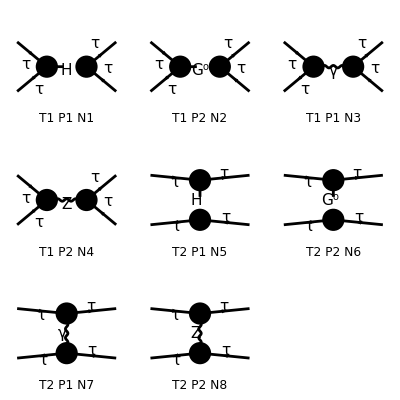

```mathematica
Process={F[2,{3}],-F[2,{3}]}-> {F[2,{3}],-F[2,{3}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1,GaugeTerms->False]//.Subexpr[]//.Abbr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 4 Particles amplitudes

in total: 8 Particles amplitudes

FeynAmpList(({F(2,{3}),-F(2,{3})}→{F(2,{3}),-F(2,{3})})→(F(2,{3}) | p1 | ML | {-Charge,LeptonNumber}
-F(2,{3}) | p2 | ML | {Charge,-LeptonNumber})→(F(2,{3}) | k1 | ML | {-Charge,LeptonNumber}
-F(2,{3}) | k2 | ML | {Charge,-LeptonNumber}),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],-v̄(p2,ML).(-(ⅈ EL ML om_-)/(2 MW SW)-(ⅈ EL ML om_+)/(2 MW SW)).u(p1,ML) ū(k1,ML).(-(ⅈ EL ML om_-)/(2 MW SW)-(ⅈ EL ML om_+)/(2 MW SW)).v(k2,ML) 1/((k1+k2)^2-MH2)),FeynAmp(GraphID(Topology==1,Generic==1,Particles==2,Number==2),Integral[],-v̄(p2,ML).((EL ML om_+)/(2 MW SW)-(EL ML om_-)/(2 MW SW)).u(p1,ML) ū(k1,ML).((EL ML om_+)/(2 MW SW)-(EL ML om_-)/(2 MW SW)).v(k2,ML) 1/((k1+k2)^2-MZ2)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==3),Integral[],v̄(p2,ML).(ⅈ EL ga(Lor1).om_-+ⅈ EL ga(Lor1).om_+).u(p1,ML) ū(k1,ML).(ⅈ EL ga(Lor2).om_-+ⅈ EL ga(Lor2).om_+).v(k2,ML) g(Lor1,Lor2) 1/(k1+k2)^2),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==4),Integral[],v̄(p2,ML).((ⅈ EL (SW2-1/2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW ga(Lor1).om_+)/CW).u(p1,ML) ū(k1,ML).((ⅈ EL (SW2-1/2) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW ga(Lor2).om_+)/CW).v(k2,ML) g(Lor1,Lor2) 1/((k1+k2)^2-MZ2)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==5),Integral[],v̄(p2,ML).(-(ⅈ EL ML om_-)/(2 MW SW)-(ⅈ EL ML om_+)/(2 MW SW)).v(k2,ML) ū(k1,ML).(-(ⅈ EL ML om_-)/(2 MW SW)-(ⅈ EL ML om_+)/(2 MW SW)).u(p1,ML) 1/((k2-p2)^2-MH2)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==2,Number==6),Integral[],v̄(p2,ML).((EL ML om_+)/(2 MW SW)-(EL ML om_-)/(2 MW SW)).v(k2,ML) ū(k1,ML).((EL ML om_+)/(2 MW SW)-(EL ML om_-)/(2 MW SW)).u(p1,ML) 1/((k2-p2)^2-MZ2)),FeynAmp(GraphID(Topology==2,Generic==2,Particles==1,Number==7),Integral[],-v̄(p2,ML).(ⅈ EL ga(Lor2).om_-+ⅈ EL ga(Lor2).om_+).v(k2,ML) ū(k1,ML).(ⅈ EL ga(Lor1).om_-+ⅈ EL ga(Lor1).om_+).u(p1,ML) g(Lor1,Lor2) 1/(k2-p2)^2),FeynAmp(GraphID(Topology==2,Generic==2,Particles==2,Number==8),Integral[],-v̄(p2,ML).((ⅈ EL (SW2-1/2) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW ga(Lor2).om_+)/CW).v(k2,ML) ū(k1,ML).((ⅈ EL (SW2-1/2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW ga(Lor1).om_+)/CW).u(p1,ML) g(Lor1,Lor2) 1/((k2-p2)^2-MZ2)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 100 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-1.frm

running FORM...

ok

1/(16 CW2^2 MW2^2 SW2^2)Alfa2 π^2 (1/2 CW2^2 ((24 ML2^2-4 (T+U) ML2+(T-U)^2) (Den(T,MH2)-Den(T,MZ2))^2+(8 ML2^2-4 S ML2+S^2) (2 Den(S,MH2)-2 Den(S,MZ2)-Den(T,MH2)+Den(T,MZ2))^2) ML2^2+CW2 (CW2 S (-4 ML2+S+2 U) (Den(T,MH2)-Den(T,MZ2)) (-2 Den(S,MH2)+2 Den(S,MZ2)+Den(T,MH2)-Den(T,MZ2))+4 MW2 (2 ML2-U) (2 Den(S,MH2)-2 Den(S,MZ2)-Den(T,MH2)+Den(T,MZ2)) (8 Den(T,MZ2) SW2^2+8 CW2 Den(S,0) SW2+8 CW2 Den(T,0) SW2-4 Den(T,MZ2) SW2+(8 SW2^2-4 SW2+1) Den(S,MZ2)+Den(T,MZ2))+12 (Den(T,MH2)-Den(T,MZ2)) (MW2 (2 ML2-U) (8 Den(T,MZ2) SW2^2+8 CW2 Den(S,0) SW2+8 CW2 Den(T,0) SW2-4 Den(T,MZ2) SW2+(8 SW2^2-4 SW2+1) Den(S,MZ2)+Den(T,MZ2))+(2 ML2-T) (8 CW2 MW2 SW2 Den(S,0)+4 MW2 SW2 (2 SW2-1) Den(S,MZ2)+CW2 ML2 (Den(T,MH2)+Den(T,MZ2))))) ML2^2+8 (CW2 ML2 (Den(S,MH2)+Den(S,MZ2))+8 CW2 MW2 SW2 Den(T,0)+4 MW2 SW2 (2 SW2-1) Den(T,MZ2)) (CW2 ML2 (2 ML2-S) (2 Den(S,MH2)-2 Den(S,MZ2)-Den(T,MH2)+Den(T,MZ2))-MW2 (2 ML2-T) (8 Den(T,MZ2) SW2^2+8 CW2 Den(S,0) SW2+8 CW2 Den(T,0) SW2-4 Den(T,MZ2) SW2+(8 SW2^2-4 SW2+1) Den(S,MZ2)+Den(T,MZ2))) ML2-4 (8 CW2 MW2 SW2 Den(S,0)+4 MW2 SW2 (2 SW2-1) Den(S,MZ2)+CW2 ML2 (Den(T,MH2)+Den(T,MZ2))) (CW2 ML2 (2 ML2-T) (2 Den(S,MH2)-2 Den(S,MZ2)-Den(T,MH2)+Den(T,MZ2))-2 (2 ML2-U) (CW2 ML2 (Den(S,MH2)+Den(S,MZ2))+8 CW2 MW2 SW2 Den(T,0)+4 MW2 SW2 (2 SW2-1) Den(T,MZ2))+8 MW2 (2 ML2-S) SW2 (CW2 Den(S,0)+CW2 Den(T,0)+SW2 (Den(S,MZ2)+Den(T,MZ2)))) ML2+8 MW2 ((Den(S,MZ2)+Den(T,MZ2)) (1-2 SW2)^2+4 CW2 SW2 (Den(S,0)+Den(T,0))) (16 ML2 MW2 SW2 (CW2 Den(S,0)+CW2 Den(T,0)+SW2 (Den(S,MZ2)+Den(T,MZ2)))-(2 ML2-S) (8 CW2 MW2 SW2 Den(S,0)+4 MW2 SW2 (2 SW2-1) Den(S,MZ2)+CW2 ML2 (Den(T,MH2)+Den(T,MZ2)))) ML2+2 (8 ML2^2-4 T ML2+T^2) (8 CW2 MW2 SW2 Den(S,0)+4 MW2 SW2 (2 SW2-1) Den(S,MZ2)+CW2 ML2 (Den(T,MH2)+Den(T,MZ2)))^2+2 (8 ML2^2-4 S ML2+S^2) (CW2 ML2 Den(S,MH2)+CW2 ML2 Den(S,MZ2)+4 MW2 SW2 (2 CW2 Den(T,0)+(2 SW2-1) Den(T,MZ2)))^2+4 MW2^2 (U-2 ML2)^2 (((Den(S,MZ2)+Den(T,MZ2)) (1-2 SW2)^2+4 CW2 SW2 (Den(S,0)+Den(T,0)))^2+16 SW2^2 (CW2 Den(S,0)+CW2 Den(T,0)+SW2 (Den(S,MZ2)+Den(T,MZ2)))^2))

```mathematica
resFCtatatata=square1//.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),ML2->MTA^2}
```

1/(256 cw^4 MW2^2 sw^4)ee^4 (cw^2 (S (1/(T-MH2)-1/(T-MZ2)) (2/(S-MZ2)+1/(T-MH2)-1/(T-MZ2)-2/(S-MH2)) (-4 MTA^2+S+2 U) cw^2+12 (1/(T-MH2)-1/(T-MZ2)) ((2 MTA^2-T) (cw^2 (1/(T-MZ2)+1/(T-MH2)) MTA^2+(8 cw^2 MW2 sw^2)/S+(4 MW2 sw^2 (2 sw^2-1))/(S-MZ2))+MW2 ((8 sw^4)/(T-MZ2)+(8 cw^2 sw^2)/S+(8 cw^2 sw^2)/T-(4 sw^2)/(T-MZ2)+(8 sw^4-4 sw^2+1)/(S-MZ2)+1/(T-MZ2)) (2 MTA^2-U))+4 MW2 (-2/(S-MZ2)-1/(T-MH2)+1/(T-MZ2)+2/(S-MH2)) ((8 sw^4)/(T-MZ2)+(8 cw^2 sw^2)/S+(8 cw^2 sw^2)/T-(4 sw^2)/(T-MZ2)+(8 sw^4-4 sw^2+1)/(S-MZ2)+1/(T-MZ2)) (2 MTA^2-U)) MTA^4+1/2 cw^4 ((24 MTA^4-4 (T+U) MTA^2+(T-U)^2) (1/(T-MH2)-1/(T-MZ2))^2+(8 MTA^4-4 S MTA^2+S^2) (-2/(S-MZ2)-1/(T-MH2)+1/(T-MZ2)+2/(S-MH2))^2) MTA^4+8 (cw^2 (1/(S-MZ2)+1/(S-MH2)) MTA^2+(8 cw^2 MW2 sw^2)/T+(4 MW2 sw^2 (2 sw^2-1))/(T-MZ2)) (cw^2 MTA^2 (2 MTA^2-S) (-2/(S-MZ2)-1/(T-MH2)+1/(T-MZ2)+2/(S-MH2))-MW2 (2 MTA^2-T) ((8 sw^4)/(T-MZ2)+(8 cw^2 sw^2)/S+(8 cw^2 sw^2)/T-(4 sw^2)/(T-MZ2)+(8 sw^4-4 sw^2+1)/(S-MZ2)+1/(T-MZ2))) MTA^2+8 MW2 (4 cw^2 (1/T+1/S) sw^2+(1-2 sw^2)^2 (1/(T-MZ2)+1/(S-MZ2))) (16 MTA^2 MW2 sw^2 (cw^2/S+cw^2/T+sw^2 (1/(T-MZ2)+1/(S-MZ2)))-(2 MTA^2-S) (cw^2 (1/(T-MZ2)+1/(T-MH2)) MTA^2+(8 cw^2 MW2 sw^2)/S+(4 MW2 sw^2 (2 sw^2-1))/(S-MZ2))) MTA^2-4 (cw^2 (1/(T-MZ2)+1/(T-MH2)) MTA^2+(8 cw^2 MW2 sw^2)/S+(4 MW2 sw^2 (2 sw^2-1))/(S-MZ2)) (cw^2 (2 MTA^2-T) (-2/(S-MZ2)-1/(T-MH2)+1/(T-MZ2)+2/(S-MH2)) MTA^2+8 MW2 (2 MTA^2-S) sw^2 (cw^2/S+cw^2/T+sw^2 (1/(T-MZ2)+1/(S-MZ2)))-2 (cw^2 (1/(S-MZ2)+1/(S-MH2)) MTA^2+(8 cw^2 MW2 sw^2)/T+(4 MW2 sw^2 (2 sw^2-1))/(T-MZ2)) (2 MTA^2-U)) MTA^2+2 (8 MTA^4-4 T MTA^2+T^2) (cw^2 (1/(T-MZ2)+1/(T-MH2)) MTA^2+(8 cw^2 MW2 sw^2)/S+(4 MW2 sw^2 (2 sw^2-1))/(S-MZ2))^2+2 (8 MTA^4-4 S MTA^2+S^2) ((cw^2 MTA^2)/(S-MH2)+(cw^2 MTA^2)/(S-MZ2)+4 MW2 sw^2 ((2 cw^2)/T+(2 sw^2-1)/(T-MZ2)))^2+4 MW2^2 (16 (cw^2/S+cw^2/T+sw^2 (1/(T-MZ2)+1/(S-MZ2)))^2 sw^4+(4 cw^2 (1/T+1/S) sw^2+(1-2 sw^2)^2 (1/(T-MZ2)+1/(S-MZ2)))^2) (U-2 MTA^2)^2)

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARtatatata=Get["resANATARtatatata.m"];
```

```mathematica
FullSimplify[resANATARtatatata-16resFCtatatata,{S+T+U==4 MTA^2,cw^2+sw^2==1}]
```

0

## e + e - -> e + e -

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
Aeeee=GenerateAmplitude[{e,ebar}->{e,ebar},OutputName->"eeee",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eeee.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/eeee/eeee_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {e, ebar} -> {e, ebar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{e(p1),ebar(p2)}→{e(p3),ebar(p4)}},Total→4,Name→eeee,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC3^2 Den(-p1-p2,0) (ū)_Spin2(p3,0) (v̄)_Spin3(p2,0) u_Spin1(p1,0) v_Spin4(p4,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4),DiagramID(2)→1/4 ⅈ Den(-p1-p2,MZ) (ū)_Spin2(p3,0) (v̄)_Spin3(p2,0) u_Spin1(p1,0) v_Spin4(p4,0) ((GC35-GC15) (γ^iLor2 γ^5)_(Spin1 Spin3)+(GC15+GC35) (γ^iLor2)_(Spin1 Spin3)) ((GC35-GC15) (γ^iLor2 γ^5)_(Spin2 Spin4)+(GC15+GC35) (γ^iLor2)_(Spin2 Spin4)),DiagramID(3)→-ⅈ GC3^2 Den(p3-p1,0) (ū)_Spin2(p3,0) (v̄)_Spin3(p2,0) u_Spin1(p1,0) v_Spin4(p4,0) (γ^iLor2)_(Spin1 Spin2) (γ^iLor2)_(Spin3 Spin4),DiagramID(4)→-1/4 ⅈ Den(p3-p1,MZ) (ū)_Spin2(p3,0) (v̄)_Spin3(p2,0) u_Spin1(p1,0) v_Spin4(p4,0) ((GC35-GC15) (γ^iLor2 γ^5)_(Spin1 Spin2)+(GC15+GC35) (γ^iLor2)_(Spin1 Spin2)) ((GC35-GC15) (γ^iLor2 γ^5)_(Spin3 Spin4)+(GC15+GC35) (γ^iLor2)_(Spin3 Spin4))}|>

```mathematica
AeeeeC=GenerateAmplitudeConjugate[{e,ebar}->{e,ebar},OutputName->"eeee",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eeee.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/eeee/eeee_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {e, ebar} -> {e, ebar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{e(p1),ebar(p2)}→{e(p3),ebar(p4)}},Total→4,Name→eeee,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC3^2 Den(-p1-p2,0) ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4),DiagramID(2)→-1/4 ⅈ Den(-p1-p2,MZ) ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((GC15-GC35) (γ^5 γ^iLorC2)_(SpinC1 SpinC3)+(GC15+GC35) (γ^iLorC2)_(SpinC1 SpinC3)) ((GC15-GC35) (γ^5 γ^iLorC2)_(SpinC2 SpinC4)+(GC15+GC35) (γ^iLorC2)_(SpinC2 SpinC4)),DiagramID(3)→ⅈ GC3^2 Den(p3-p1,0) ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) (γ^iLorC2)_(SpinC1 SpinC2) (γ^iLorC2)_(SpinC3 SpinC4),DiagramID(4)→1/4 ⅈ Den(p3-p1,MZ) ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((GC15-GC35) (γ^5 γ^iLorC2)_(SpinC1 SpinC2)+(GC15+GC35) (γ^iLorC2)_(SpinC1 SpinC2)) ((GC15-GC35) (γ^5 γ^iLorC2)_(SpinC3 SpinC4)+(GC15+GC35) (γ^iLorC2)_(SpinC3 SpinC4))}|>

```mathematica
AmpSQeeee=GenerateAmplitudeSquare[Aeeee,AeeeeC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{e(p1),ebar(p2)}→{e(p3),ebar(p4)}},Name→eeee,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→-1/(4 cw^4 sw2^2)ee^4 (S U (Den(p3-p1,MZ))^2 cw^8+T U (Den(p3-p1,MZ))^2 cw^8-4 S sw2 U (Den(p3-p1,MZ))^2 cw^6-4 sw2 T U (Den(p3-p1,MZ))^2 cw^6+8 S sw2 U Den(p3-p1,0) Den(p3-p1,MZ) cw^6+8 sw2 T U Den(p3-p1,0) Den(p3-p1,MZ) cw^6+32 sw2^2 (2 T U+S (T+U)) (Den(-p1-p2,0))^2 cw^4+32 S sw2^2 T (Den(p3-p1,0))^2 cw^4+64 S sw2^2 U (Den(p3-p1,0))^2 cw^4+32 sw2^2 T U (Den(p3-p1,0))^2 cw^4+8 S sw2^2 T (Den(p3-p1,MZ))^2 cw^4+14 S sw2^2 U (Den(p3-p1,MZ))^2 cw^4+6 sw2^2 T U (Den(p3-p1,MZ))^2 cw^4-32 S sw2^2 T Den(p3-p1,0) Den(p3-p1,MZ) cw^4-48 S sw2^2 U Den(p3-p1,0) Den(p3-p1,MZ) cw^4-16 sw2^2 T U Den(p3-p1,0) Den(p3-p1,MZ) cw^4-16 S sw2^3 T (Den(p3-p1,MZ))^2 cw^2-20 S sw2^3 U (Den(p3-p1,MZ))^2 cw^2-4 sw2^3 T U (Den(p3-p1,MZ))^2 cw^2+32 S sw2^3 T Den(p3-p1,0) Den(p3-p1,MZ) cw^2+72 S sw2^3 U Den(p3-p1,0) Den(p3-p1,MZ) cw^2+40 sw2^3 T U Den(p3-p1,0) Den(p3-p1,MZ) cw^2+8 sw2 Den(-p1-p2,0) (((S+T) U cw^4-2 sw2 (3 T U+S (2 T+U)) cw^2+sw2^2 (4 S T+9 U T+5 S U)) Den(-p1-p2,MZ)+(S+T) U (8 sw2 Den(p3-p1,0) cw^2+(cw^4-2 sw2 cw^2+5 sw2^2) Den(p3-p1,MZ))) cw^2+((S+T) U cw^8-4 sw2 (S+T) U cw^6+2 sw2^2 (4 S T+7 U T+3 S U) cw^4-4 sw2^3 (5 T U+S (4 T+U)) cw^2+sw2^4 (8 S T+25 U T+17 S U)) (Den(-p1-p2,MZ))^2+8 S sw2^4 T (Den(p3-p1,MZ))^2+25 S sw2^4 U (Den(p3-p1,MZ))^2+17 sw2^4 T U (Den(p3-p1,MZ))^2+2 (S+T) U Den(-p1-p2,MZ) (4 sw2 (cw^4-2 sw2 cw^2+5 sw2^2) Den(p3-p1,0) cw^2+(cw^8-4 sw2 cw^6+6 sw2^2 cw^4-4 sw2^3 cw^2+17 sw2^4) Den(p3-p1,MZ)))|>

```mathematica
resANATAReeee=AmpSQeeee[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(p1-p3)->√T,(p3-p1)->√T,(p3-p2)->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}//Simplify
```

-1/(4 cw^4 sw^4 (MZ^2-S)^2 (MZ^2-T)^2)ee^4 (cw^8 U (S+T) (-2 MZ^2+S+T)^2+(4 cw^6 sw^2 U (S+T) (-4 MZ^6 (S+T)+MZ^4 (6 S^2+8 S T+6 T^2)-2 MZ^2 (S+T)^3+S T (S+T)^2))/(S T)+1/(S^2 T^2)2 cw^4 sw^4 (16 MZ^8 (S^3 (T+2 U)+3 S^2 T U+S T^2 (T+3 U)+2 T^3 U)-16 MZ^6 (2 S^4 (T+2 U)+S^3 T (T+8 U)+S^2 T^2 (T+10 U)+2 S T^3 (T+4 U)+4 T^4 U)+8 MZ^4 (2 S^5 (T+2 U)+S^4 T (4 T+15 U)+S^3 T^2 (T+25 U)+S^2 T^3 (4 T+25 U)+S T^4 (2 T+15 U)+4 T^5 U)-4 MZ^2 S T (2 S^4 (2 T+5 U)+S^3 T (2 T+25 U)+2 S^2 T^2 (T+17 U)+S T^3 (4 T+25 U)+10 T^4 U)+S^2 T^2 (S^3 (4 T+15 U)+33 S^2 T U+S T^2 (4 T+33 U)+15 T^3 U))-1/(S T)4 cw^2 sw^6 (4 MZ^6 (S^2 (2 T+7 U)+2 S T (T+5 U)+7 T^2 U)-2 MZ^4 (S^3 (8 T+23 U)+S^2 T (4 T+45 U)+S T^2 (8 T+45 U)+23 T^3 U)+2 MZ^2 (S+T) (S^3 (4 T+9 U)+23 S^2 T U+S T^2 (4 T+23 U)+9 T^3 U)-S T (S^3 (4 T+13 U)+27 S^2 T U+S T^2 (4 T+27 U)+13 T^3 U))+sw^8 (4 MZ^4 (4 S T+19 S U+19 T U)-4 MZ^2 (S^2 (4 T+21 U)+2 S T (2 T+17 U)+21 T^2 U)+S^3 (8 T+25 U)+51 S^2 T U+S T^2 (8 T+51 U)+25 T^3 U))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATAReeee.m",resANATAReeee];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 4 Particles insertions

> Top. 4: 0 Particles insertions

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 4 diagrams

> Top. 2 aebf/cedf/ef.m, 4 diagrams

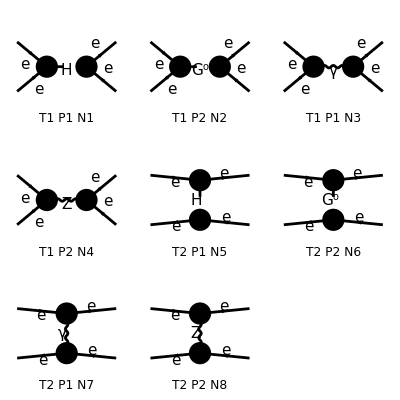

```mathematica
Process={F[2,{1}],-F[2,{1}]}-> {F[2,{1}],-F[2,{1}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1,GaugeTerms->False]//.Subexpr[]//.Abbr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 4 Particles amplitudes

in total: 8 Particles amplitudes

FeynAmpList(({F(2,{1}),-F(2,{1})}→{F(2,{1}),-F(2,{1})})→(F(2,{1}) | p1 | ME | {-Charge,LeptonNumber}
-F(2,{1}) | p2 | ME | {Charge,-LeptonNumber})→(F(2,{1}) | k1 | ME | {-Charge,LeptonNumber}
-F(2,{1}) | k2 | ME | {Charge,-LeptonNumber}),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],-v̄(p2,ME).(-(ⅈ EL ME om_-)/(2 MW SW)-(ⅈ EL ME om_+)/(2 MW SW)).u(p1,ME) ū(k1,ME).(-(ⅈ EL ME om_-)/(2 MW SW)-(ⅈ EL ME om_+)/(2 MW SW)).v(k2,ME) 1/((k1+k2)^2-MH2)),FeynAmp(GraphID(Topology==1,Generic==1,Particles==2,Number==2),Integral[],-v̄(p2,ME).((EL ME om_+)/(2 MW SW)-(EL ME om_-)/(2 MW SW)).u(p1,ME) ū(k1,ME).((EL ME om_+)/(2 MW SW)-(EL ME om_-)/(2 MW SW)).v(k2,ME) 1/((k1+k2)^2-MZ2)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==3),Integral[],v̄(p2,ME).(ⅈ EL ga(Lor1).om_-+ⅈ EL ga(Lor1).om_+).u(p1,ME) ū(k1,ME).(ⅈ EL ga(Lor2).om_-+ⅈ EL ga(Lor2).om_+).v(k2,ME) g(Lor1,Lor2) 1/(k1+k2)^2),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==4),Integral[],v̄(p2,ME).((ⅈ EL (SW2-1/2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW ga(Lor1).om_+)/CW).u(p1,ME) ū(k1,ME).((ⅈ EL (SW2-1/2) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW ga(Lor2).om_+)/CW).v(k2,ME) g(Lor1,Lor2) 1/((k1+k2)^2-MZ2)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==5),Integral[],v̄(p2,ME).(-(ⅈ EL ME om_-)/(2 MW SW)-(ⅈ EL ME om_+)/(2 MW SW)).v(k2,ME) ū(k1,ME).(-(ⅈ EL ME om_-)/(2 MW SW)-(ⅈ EL ME om_+)/(2 MW SW)).u(p1,ME) 1/((k2-p2)^2-MH2)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==2,Number==6),Integral[],v̄(p2,ME).((EL ME om_+)/(2 MW SW)-(EL ME om_-)/(2 MW SW)).v(k2,ME) ū(k1,ME).((EL ME om_+)/(2 MW SW)-(EL ME om_-)/(2 MW SW)).u(p1,ME) 1/((k2-p2)^2-MZ2)),FeynAmp(GraphID(Topology==2,Generic==2,Particles==1,Number==7),Integral[],-v̄(p2,ME).(ⅈ EL ga(Lor2).om_-+ⅈ EL ga(Lor2).om_+).v(k2,ME) ū(k1,ME).(ⅈ EL ga(Lor1).om_-+ⅈ EL ga(Lor1).om_+).u(p1,ME) g(Lor1,Lor2) 1/(k2-p2)^2),FeynAmp(GraphID(Topology==2,Generic==2,Particles==2,Number==8),Integral[],-v̄(p2,ME).((ⅈ EL (SW2-1/2) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW ga(Lor2).om_+)/CW).v(k2,ME) ū(k1,ME).((ⅈ EL (SW2-1/2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW ga(Lor1).om_+)/CW).u(p1,ME) g(Lor1,Lor2) 1/((k2-p2)^2-MZ2)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 100 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-1.frm

running FORM...

ok

1/(16 CW2^2 MW2^2 SW2^2)Alfa2 π^2 (1/2 CW2^2 ((24 ME2^2-4 (T+U) ME2+(T-U)^2) (Den(T,MH2)-Den(T,MZ2))^2+(8 ME2^2-4 S ME2+S^2) (2 Den(S,MH2)-2 Den(S,MZ2)-Den(T,MH2)+Den(T,MZ2))^2) ME2^2+CW2 (CW2 S (-4 ME2+S+2 U) (Den(T,MH2)-Den(T,MZ2)) (-2 Den(S,MH2)+2 Den(S,MZ2)+Den(T,MH2)-Den(T,MZ2))+4 MW2 (2 ME2-U) (2 Den(S,MH2)-2 Den(S,MZ2)-Den(T,MH2)+Den(T,MZ2)) (8 Den(T,MZ2) SW2^2+8 CW2 Den(S,0) SW2+8 CW2 Den(T,0) SW2-4 Den(T,MZ2) SW2+(8 SW2^2-4 SW2+1) Den(S,MZ2)+Den(T,MZ2))+12 (Den(T,MH2)-Den(T,MZ2)) (MW2 (2 ME2-U) (8 Den(T,MZ2) SW2^2+8 CW2 Den(S,0) SW2+8 CW2 Den(T,0) SW2-4 Den(T,MZ2) SW2+(8 SW2^2-4 SW2+1) Den(S,MZ2)+Den(T,MZ2))+(2 ME2-T) (8 CW2 MW2 SW2 Den(S,0)+4 MW2 SW2 (2 SW2-1) Den(S,MZ2)+CW2 ME2 (Den(T,MH2)+Den(T,MZ2))))) ME2^2+8 (CW2 ME2 (Den(S,MH2)+Den(S,MZ2))+8 CW2 MW2 SW2 Den(T,0)+4 MW2 SW2 (2 SW2-1) Den(T,MZ2)) (CW2 ME2 (2 ME2-S) (2 Den(S,MH2)-2 Den(S,MZ2)-Den(T,MH2)+Den(T,MZ2))-MW2 (2 ME2-T) (8 Den(T,MZ2) SW2^2+8 CW2 Den(S,0) SW2+8 CW2 Den(T,0) SW2-4 Den(T,MZ2) SW2+(8 SW2^2-4 SW2+1) Den(S,MZ2)+Den(T,MZ2))) ME2-4 (8 CW2 MW2 SW2 Den(S,0)+4 MW2 SW2 (2 SW2-1) Den(S,MZ2)+CW2 ME2 (Den(T,MH2)+Den(T,MZ2))) (CW2 ME2 (2 ME2-T) (2 Den(S,MH2)-2 Den(S,MZ2)-Den(T,MH2)+Den(T,MZ2))-2 (2 ME2-U) (CW2 ME2 (Den(S,MH2)+Den(S,MZ2))+8 CW2 MW2 SW2 Den(T,0)+4 MW2 SW2 (2 SW2-1) Den(T,MZ2))+8 MW2 (2 ME2-S) SW2 (CW2 Den(S,0)+CW2 Den(T,0)+SW2 (Den(S,MZ2)+Den(T,MZ2)))) ME2+8 MW2 ((Den(S,MZ2)+Den(T,MZ2)) (1-2 SW2)^2+4 CW2 SW2 (Den(S,0)+Den(T,0))) (16 ME2 MW2 SW2 (CW2 Den(S,0)+CW2 Den(T,0)+SW2 (Den(S,MZ2)+Den(T,MZ2)))-(2 ME2-S) (8 CW2 MW2 SW2 Den(S,0)+4 MW2 SW2 (2 SW2-1) Den(S,MZ2)+CW2 ME2 (Den(T,MH2)+Den(T,MZ2)))) ME2+2 (8 ME2^2-4 T ME2+T^2) (8 CW2 MW2 SW2 Den(S,0)+4 MW2 SW2 (2 SW2-1) Den(S,MZ2)+CW2 ME2 (Den(T,MH2)+Den(T,MZ2)))^2+2 (8 ME2^2-4 S ME2+S^2) (CW2 ME2 Den(S,MH2)+CW2 ME2 Den(S,MZ2)+4 MW2 SW2 (2 CW2 Den(T,0)+(2 SW2-1) Den(T,MZ2)))^2+4 MW2^2 (U-2 ME2)^2 (((Den(S,MZ2)+Den(T,MZ2)) (1-2 SW2)^2+4 CW2 SW2 (Den(S,0)+Den(T,0)))^2+16 SW2^2 (CW2 Den(S,0)+CW2 Den(T,0)+SW2 (Den(S,MZ2)+Den(T,MZ2)))^2))

```mathematica
resFCeeee=square1//.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),ML2->MTA^2,ME2->0}//Simplify[#,S+T+U==0]&
```

(ee^4 (8 S^2 sw^4 ((2 cw^2)/T+(1-2 sw^2)/(MZ2-T))^2+8 sw^4 T^2 ((2 cw^2)/S+(1-2 sw^2)/(MZ2+T+U))^2+U^2 ((4 cw^2 sw^2 (1/S+1/T)+(1-2 sw^2)^2 (1/(S-MZ2)+1/(T-MZ2)))^2+16 sw^4 (cw^2 (1/S+1/T)+sw^2 (1/(S-MZ2)+1/(T-MZ2)))^2)))/(64 cw^4 sw^4)

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATAReeee=Get["resANATAReeee.m"];
```

```mathematica
FullSimplify[resANATAReeee-16resFCeeee,{S+T+U==0,cw^2+sw^2==1}]
```

0

## ee -> v_e v_e

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
Aeevevebar=GenerateAmplitude[{e,ebar}->{ve,vebar},OutputName->"eevevebar",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eevevebar.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/eevevebar/eevevebar_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {e, ebar} -> {ve, vebar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{e(p1),ebar(p2)}→{ve(p3),vebar(p4)}},Total→2,Name→eevevebar,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→{DiagramID(1)→1/4 ⅈ GC16 Den(-p1-p2,MZ) (ū)_Spin2(p3,0) (v̄)_Spin3(p2,0) u_Spin1(p1,0) v_Spin4(p4,0) ((γ^iLor2)_(Spin2 Spin4)-(γ^iLor2 γ^5)_(Spin2 Spin4)) ((GC35-GC15) (γ^iLor2 γ^5)_(Spin1 Spin3)+(GC15+GC35) (γ^iLor2)_(Spin1 Spin3)),DiagramID(2)→-1/4 ⅈ GC25^2 Den(p3-p1,MW) (ū)_Spin2(p3,0) (v̄)_Spin3(p2,0) u_Spin1(p1,0) v_Spin4(p4,0) ((γ^iLor2)_(Spin1 Spin2)-(γ^iLor2 γ^5)_(Spin1 Spin2)) ((γ^iLor2)_(Spin3 Spin4)-(γ^iLor2 γ^5)_(Spin3 Spin4))}|>

```mathematica
AeevevebarC=GenerateAmplitudeConjugate[{e,ebar}->{ve,vebar},OutputName->"eevevebar",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eevevebar.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/eevevebar/eevevebar_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {e, ebar} -> {ve, vebar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{e(p1),ebar(p2)}→{ve(p3),vebar(p4)}},Total→2,Name→eevevebar,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-1/4 ⅈ GC16 Den(-p1-p2,MZ) ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((γ^5 γ^iLorC2)_(SpinC2 SpinC4)+(γ^iLorC2)_(SpinC2 SpinC4)) ((GC15-GC35) (γ^5 γ^iLorC2)_(SpinC1 SpinC3)+(GC15+GC35) (γ^iLorC2)_(SpinC1 SpinC3)),DiagramID(2)→1/4 ⅈ GC25^2 Den(p3-p1,MW) ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((γ^5 γ^iLorC2)_(SpinC1 SpinC2)+(γ^iLorC2)_(SpinC1 SpinC2)) ((γ^5 γ^iLorC2)_(SpinC3 SpinC4)+(γ^iLorC2)_(SpinC3 SpinC4))}|>

```mathematica
AmpSQeeveve=GenerateAmplitudeSquare[Aeevevebar,AeevevebarC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{e(p1),ebar(p2)}→{ve(p3),vebar(p4)}},Name→eevevebar,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→-1/(4 cw^4 sw2^2)ee^4 (4 cw^4 U (S+T) (Den(p3-p1,MW))^2-4 cw^2 U (cw^4-sw2^2) (S+T) Den(p3-p1,MW) Den(-p1-p2,MZ)+(cw^2+sw2)^2 (Den(-p1-p2,MZ))^2 (S (cw^4 U-2 cw^2 sw2 U+sw2^2 (4 T+U))+T U (cw^4-2 cw^2 sw2+5 sw2^2)))|>

```mathematica
resANATAReeveve=AmpSQeeveve[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(p3-p1)->√T,(p3-p2)->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

-(ee^4 ((4 cw^4 U (S+T))/((T-MW^2)^2)-(4 cw^2 U (cw^4-sw^4) (S+T))/((T-MW^2) (S-MZ^2))+((cw^2+sw^2)^2 (S (cw^4 U-2 cw^2 sw^2 U+sw^4 (4 T+U))+T U (cw^4-2 cw^2 sw^2+5 sw^4)))/((S-MZ^2)^2)))/(4 cw^4 sw^4)

```mathematica
SetDirectory[$AnatarPath];
Save["resANATAReeveve.m",resANATAReeveve];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 2 Particles insertions

> Top. 4: 0 Particles insertions

in total: 3 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 1 diagram

> Top. 2 aebf/cedf/ef.m, 2 diagrams

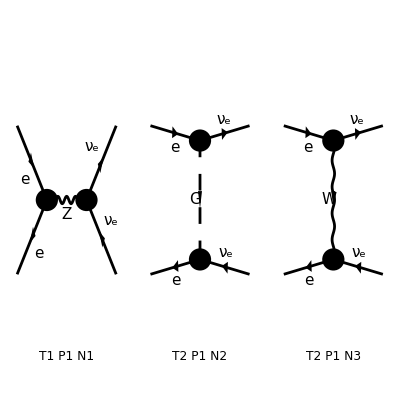

```mathematica
Process={F[2,{1}],-F[2,{1}]}-> {F[1,{1}],-F[1,{1}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1,GaugeTerms->False]//.Subexpr[]//.Abbr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 2 Particles amplitudes

in total: 3 Particles amplitudes

FeynAmpList(({F(2,{1}),-F(2,{1})}→{F(1,{1}),-F(1,{1})})→(F(2,{1}) | p1 | ME | {-Charge,LeptonNumber}
-F(2,{1}) | p2 | ME | {Charge,-LeptonNumber})→(F(1,{1}) | k1 | 0 | {0,LeptonNumber}
-F(1,{1}) | k2 | 0 | {0,-LeptonNumber}),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],1/((k1+k2)^2-MZ2) g(Lor1,Lor2) ū(k1,0).(ⅈ EL ga(Lor2).om_-)/(2 CW SW).v(k2,0) v̄(p2,ME).((ⅈ EL (SW2-1/2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW ga(Lor1).om_+)/CW).u(p1,ME)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==2),Integral[],1/((k2-p2)^2-MW2) v̄(p2,ME).(-(ⅈ EL ME om_-)/(√2 MW SW)).v(k2,0) ū(k1,0).(-(ⅈ EL ME om_+)/(√2 MW SW)).u(p1,ME)),FeynAmp(GraphID(Topology==2,Generic==2,Particles==1,Number==3),Integral[],g(Lor1,Lor2) 1/((k2-p2)^2-MW2) ū(k1,0).(ⅈ EL ga(Lor1).om_-)/(√2 SW).u(p1,ME) (-v̄(p2,ME).(ⅈ EL ga(Lor2).om_-)/(√2 SW).v(k2,0))))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 4 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-1.frm

running FORM...

ok

1/(4 CW2^2 MW2^2 SW2^2)π^2 Alfa2 (MW2^2 (ME2-U)^2 ((1-2 SW2) Den(S,MZ2)-2 CW2 Den(T,MW2))^2+(ME2-T)^2 (CW2 ME2 Den(T,MW2)+2 MW2 SW2 Den(S,MZ2))^2+2 ME2 MW2 S (2 CW2 Den(T,MW2)+(2 SW2-1) Den(S,MZ2)) (CW2 ME2 Den(T,MW2)+2 MW2 SW2 Den(S,MZ2)))

```mathematica
resFCeeveve=square1//.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),ME2->0}//FullSimplify[#,S+T+U==0]&
```

(ee^4 (U^2 ((2 cw^2)/(MW2-T)+(2 sw^2-1)/(MZ2+T+U))^2+(4 sw^4 T^2)/(MZ2+T+U)^2))/(64 cw^4 sw^4)

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATAReeveve=Get["resANATAReeveve.m"];
```

```mathematica
FullSimplify[resANATAReeveve-16resFCeeveve,{S+T+U==0,cw^2+sw^2==1}]
```

0

## e + e - -> t t~

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
Aeett=GenerateAmplitude[{e,ebar}->{t,tbar},OutputName->"eett",Dimension->4]
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eett.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/eett/eett_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {e, ebar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{e(p1),ebar(p2)}→{t(p3),tbar(p4)}},Total→2,Name→eett,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→S/2,p1.p3→1/2 (MT^2-T),p2.p3→1/2 (MT^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MT^2-T),1/(p2.p3)→2/(MT^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC2 GC3 Den(-p1-p2,0) (v̄)_Spin3(p2,0) u_Spin1(p1,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT),DiagramID(2)→(-1/4 ⅈ GC15 GC26+(3 ⅈ GC15 GC33)/4-(ⅈ GC26 GC35)/4+(3 ⅈ GC33 GC35)/4) Den(-p1-p2,MZ) (v̄)_Spin3(p2,0) u_Spin1(p1,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2 γ^5)_(Spin2 Spin4) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT)+(-1/4 ⅈ GC15 GC26-(5 ⅈ GC15 GC33)/4+(ⅈ GC26 GC35)/4+(5 ⅈ GC33 GC35)/4) Den(-p1-p2,MZ) (v̄)_Spin3(p2,0) u_Spin1(p1,0) (γ^iLor2)_(Spin2 Spin4) (γ^iLor2 γ^5)_(Spin1 Spin3) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT)+((ⅈ GC15 GC26)/4-(3 ⅈ GC15 GC33)/4-(ⅈ GC26 GC35)/4+(3 ⅈ GC33 GC35)/4) Den(-p1-p2,MZ) (v̄)_Spin3(p2,0) u_Spin1(p1,0) (γ^iLor2 γ^5)_(Spin1 Spin3) (γ^iLor2 γ^5)_(Spin2 Spin4) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT)+((ⅈ GC15 GC26)/4+(5 ⅈ GC15 GC33)/4+(ⅈ GC26 GC35)/4+(5 ⅈ GC33 GC35)/4) Den(-p1-p2,MZ) (v̄)_Spin3(p2,0) u_Spin1(p1,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) (ū)_Spin2^Colour4(p3,MT) v_Spin4^Colour4(p4,MT)}|>

```mathematica
AeettC=GenerateAmplitudeConjugate[{e,ebar}->{t,tbar},OutputName->"eett",Dimension->4]
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eett.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/eett/eett_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {e, ebar} -> {t, tbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{e(p1),ebar(p2)}→{t(p3),tbar(p4)}},Total→2,Name→eett,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→S/2,p1.p3→1/2 (MT^2-T),p2.p3→1/2 (MT^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MT^2-T),1/(p2.p3)→2/(MT^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC2 GC3 Den(-p1-p2,0) ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT),DiagramID(2)→Den(-p1-p2,MZ) (γ^5 γ^iLorC2)_(SpinC1 SpinC3) (γ^5 γ^iLorC2)_(SpinC2 SpinC4) (-1/4 ⅈ GC15 GC26 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)+3/4 ⅈ GC15 GC33 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)+1/4 ⅈ GC26 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)-3/4 ⅈ GC33 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT))+Den(-p1-p2,MZ) (γ^iLorC2)_(SpinC1 SpinC3) (γ^5 γ^iLorC2)_(SpinC2 SpinC4) (-1/4 ⅈ GC15 GC26 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)+3/4 ⅈ GC15 GC33 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)-1/4 ⅈ GC26 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)+3/4 ⅈ GC33 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT))+Den(-p1-p2,MZ) (γ^iLorC2)_(SpinC2 SpinC4) (γ^5 γ^iLorC2)_(SpinC1 SpinC3) (-1/4 ⅈ GC15 GC26 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)-5/4 ⅈ GC15 GC33 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)+1/4 ⅈ GC26 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)+5/4 ⅈ GC33 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT))+Den(-p1-p2,MZ) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) (-1/4 ⅈ GC15 GC26 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)-5/4 ⅈ GC15 GC33 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)-1/4 ⅈ GC26 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT)-5/4 ⅈ GC33 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MT) ((v̄)^†)_SpinC4^ColourC4(p4,MT))}|>

```mathematica
AmpSQeett=GenerateAmplitudeSquare[Aeett,AeettC,Dimension->4,CasimirValues->True]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{e(p1),ebar(p2)}→{t(p3),tbar(p4)}},Name→eett,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MT^2,p3.p3→MT^2,1/(p3.p3)→1/MT^2,p4^2→MT^2,p4.p4→MT^2,1/(p4.p4)→1/MT^2,p1.p2→S/2,p1.p3→1/2 (MT^2-T),p2.p3→1/2 (MT^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MT^2-T),1/(p2.p3)→2/(MT^2-U),p4→p1+p2-p3},Amplitudes→-1/(12 cw^4 sw2^2)ee^4 (128 cw^4 sw2^2 (Den(-p1-p2,0))^2 (2 MT^4-2 MT^2 (2 S+T+U)+S (T+U)+2 T U)+16 cw^2 sw2 Den(-p1-p2,0) Den(-p1-p2,MZ) (3 cw^4 (MT^4-MT^2 (2 S+T+U)+U (S+T))-2 cw^2 sw2 (7 MT^4-7 MT^2 (2 S+T+U)+5 S T+2 S U+7 T U)+3 sw2^2 (5 MT^4-5 MT^2 (2 S+T+U)+2 S T+3 S U+5 T U))+(Den(-p1-p2,MZ))^2 (9 cw^8 (MT^2-U) (MT^2-S-T)-24 cw^6 sw2 (MT^4-MT^2 (2 S+T+U)+U (S+T))+2 cw^4 sw2^2 (37 MT^4-MT^2 (65 S+37 (T+U))+26 S T+11 S U+37 T U)-8 cw^2 sw2^3 (8 MT^4-MT^2 (25 S+8 (T+U))+7 S T+S U+8 T U)+5 sw2^4 (17 MT^4-MT^2 (25 S+17 (T+U))+4 S T+13 S U+17 T U)))|>

```mathematica
resANATAReett=AmpSQeett[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(p3-p1)->√U,(p3-p2)->√T,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

-1/(12 cw^4 sw^4)ee^4 ((128 cw^4 sw^4 (2 MT^4-2 MT^2 (2 S+T+U)+S (T+U)+2 T U))/S^2+(16 cw^2 sw^2 (3 cw^4 (MT^4-MT^2 (2 S+T+U)+U (S+T))-2 cw^2 sw^2 (7 MT^4-7 MT^2 (2 S+T+U)+5 S T+2 S U+7 T U)+3 sw^4 (5 MT^4-5 MT^2 (2 S+T+U)+2 S T+3 S U+5 T U)))/(S (S-MZ^2))+1/((S-MZ^2)^2)(9 cw^8 (MT^2-U) (MT^2-S-T)-24 cw^6 sw^2 (MT^4-MT^2 (2 S+T+U)+U (S+T))+2 cw^4 sw^4 (37 MT^4-MT^2 (65 S+37 (T+U))+26 S T+11 S U+37 T U)-8 cw^2 sw^6 (8 MT^4-MT^2 (25 S+8 (T+U))+7 S T+S U+8 T U)+5 sw^8 (17 MT^4-MT^2 (25 S+17 (T+U))+4 S T+13 S U+17 T U)))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATAReett.m",resANATAReett];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 4 diagrams

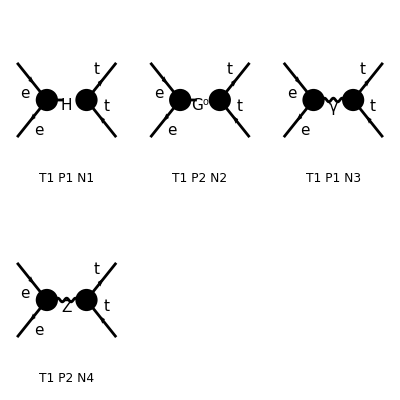

```mathematica
Process={F[2,{1}],-F[2,{1}]}-> {F[3,{3}],-F[3,{3}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 64 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

1/(12 CW2^2 MW2^2 SW2^2)π^2 Alfa2 (9 CW2^2 ME2 MT2 ((12 ME2 MT2-4 ME2 S-2 MT2 S+S^2) (Den(S,MH2))^2+(4 ME2 MT2+S (S-2 MT2)) (Den(S,MZ2))^2)+6 CW2 ME2 MT2 (Den(S,MH2)+Den(S,MZ2)) (3 CW2 MT2 (2 ME2-S) Den(S,MH2)+Den(S,MZ2) (3 CW2 MT2 (S-2 ME2)+MW2 (-3 ME2-3 MT2-16 SW2^2 T+16 SW2^2 U+10 SW2 T-10 SW2 U+3 U))-16 CW2 MW2 SW2 (T-U) Den(S,0))-2 MT2 MW2 (3 CW2 ME2 (Den(S,MH2)-Den(S,MZ2)) (16 CW2 SW2 (T-U) Den(S,0)+Den(S,MZ2) (-3 ME2-3 MT2+16 SW2^2 T-16 SW2^2 U-10 SW2 T+10 SW2 U+3 T))+16 MW2 SW2^2 (2 ME2-S) (CW2 Den(S,0)+SW2 Den(S,MZ2)) (4 CW2 Den(S,0)+(4 SW2-3) Den(S,MZ2)))+4 MW2^2 SW2^2 (ME2+MT2-T)^2 (4 (2 CW2 Den(S,0)+(2 SW2-1) Den(S,MZ2))^2+(4 CW2 Den(S,0)+(4 SW2-3) Den(S,MZ2))^2)+MW2^2 (ME2+MT2-U)^2 (64 SW2^2 (CW2 Den(S,0)+SW2 Den(S,MZ2))^2+(8 CW2 SW2 Den(S,0)+(8 SW2^2-10 SW2+3) Den(S,MZ2))^2)+64 ME2 MW2^2 SW2^2 (2 CW2 Den(S,0)+(2 SW2-1) Den(S,MZ2)) (CW2 (2 MT2+S) Den(S,0)+(MT2 (2 SW2-3)+S SW2) Den(S,MZ2))+4 MW2^2 SW2 (8 CW2 SW2 Den(S,0)+(8 SW2^2-10 SW2+3) Den(S,MZ2)) (4 CW2 S (ME2+MT2) Den(S,0)+Den(S,MZ2) (10 ME2 MT2+ME2 S (4 SW2-3)+2 MT2 S (2 SW2-1))))

```mathematica
resFCeett=square1//.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),ME2->0}//FullSimplify[#,S+T+U==2MT2]&
```

1/(192 cw^4 S^2 sw^4 (MZ2-S)^2)ee^4 (4 sw^4 (MT2-T)^2 (4 (2 cw^2 (MZ2-S)-2 S sw^2+S)^2+(4 cw^2 (MZ2-S)+S (3-4 sw^2))^2)+(MT2-U)^2 (64 sw^4 (cw^2 MZ2-S (cw^2+sw^2))^2+(8 cw^2 sw^2 (MZ2-S)+S (-8 sw^4+10 sw^2-3))^2)+32 MT2 S sw^4 (cw^2 (MZ2-S)-S sw^2) (4 cw^2 (MZ2-S)+S (3-4 sw^2))+8 MT2 S sw^2 (2 cw^2 (MZ2-S)-2 S sw^2+S) (8 cw^2 sw^2 (MZ2-S)+S (-8 sw^4+10 sw^2-3)))

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATAReett=Get["resANATAReett.m"];
```

```mathematica
FullSimplify[1/16 resANATAReett-resFCeett,{S+T+U==2MT2,cw^2+sw^2==1}]
```

0

## e+ e- -> b b~

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
Aeebb=GenerateAmplitude[{e,ebar}->{b,bbar},OutputName->"eebb",Dimension->4]
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebb.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/eebb/eebb_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {e, ebar} -> {b, bbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{e(p1),ebar(p2)}→{b(p3),bbar(p4)}},Total→2,Name→eebb,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MB^2,p3.p3→MB^2,1/(p3.p3)→1/MB^2,p4^2→MB^2,p4.p4→MB^2,1/(p4.p4)→1/MB^2,p1.p2→S/2,p1.p3→1/2 (MB^2-T),p2.p3→1/2 (MB^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MB^2-T),1/(p2.p3)→2/(MB^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC1 GC3 Den(-p1-p2,0) (v̄)_Spin3(p2,0) u_Spin1(p1,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) (ū)_Spin2^Colour4(p3,MB) v_Spin4^Colour4(p4,MB),DiagramID(2)→(-1/4 ⅈ GC13 GC15-(ⅈ GC13 GC35)/4+(ⅈ GC15 GC34)/4+(ⅈ GC34 GC35)/4) Den(-p1-p2,MZ) (v̄)_Spin3(p2,0) u_Spin1(p1,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2 γ^5)_(Spin2 Spin4) (ū)_Spin2^Colour4(p3,MB) v_Spin4^Colour4(p4,MB)+(-1/4 ⅈ GC13 GC15+(ⅈ GC13 GC35)/4-(ⅈ GC15 GC34)/4+(ⅈ GC34 GC35)/4) Den(-p1-p2,MZ) (v̄)_Spin3(p2,0) u_Spin1(p1,0) (γ^iLor2)_(Spin2 Spin4) (γ^iLor2 γ^5)_(Spin1 Spin3) (ū)_Spin2^Colour4(p3,MB) v_Spin4^Colour4(p4,MB)+((ⅈ GC13 GC15)/4-(ⅈ GC13 GC35)/4-(ⅈ GC15 GC34)/4+(ⅈ GC34 GC35)/4) Den(-p1-p2,MZ) (v̄)_Spin3(p2,0) u_Spin1(p1,0) (γ^iLor2 γ^5)_(Spin1 Spin3) (γ^iLor2 γ^5)_(Spin2 Spin4) (ū)_Spin2^Colour4(p3,MB) v_Spin4^Colour4(p4,MB)+((ⅈ GC13 GC15)/4+(ⅈ GC13 GC35)/4+(ⅈ GC15 GC34)/4+(ⅈ GC34 GC35)/4) Den(-p1-p2,MZ) (v̄)_Spin3(p2,0) u_Spin1(p1,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) (ū)_Spin2^Colour4(p3,MB) v_Spin4^Colour4(p4,MB)}|>

```mathematica
AeebbC=GenerateAmplitudeConjugate[{e,ebar}->{b,bbar},OutputName->"eebb",Dimension->4]
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_eebb.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/eebb/eebb_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {e, ebar} -> {b, bbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{e(p1),ebar(p2)}→{b(p3),bbar(p4)}},Total→2,Name→eebb,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MB^2,p3.p3→MB^2,1/(p3.p3)→1/MB^2,p4^2→MB^2,p4.p4→MB^2,1/(p4.p4)→1/MB^2,p1.p2→S/2,p1.p3→1/2 (MB^2-T),p2.p3→1/2 (MB^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MB^2-T),1/(p2.p3)→2/(MB^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC1 GC3 Den(-p1-p2,0) ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB),DiagramID(2)→Den(-p1-p2,MZ) (γ^5 γ^iLorC2)_(SpinC1 SpinC3) (γ^5 γ^iLorC2)_(SpinC2 SpinC4) (-1/4 ⅈ GC13 GC15 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)+1/4 ⅈ GC13 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)+1/4 ⅈ GC15 GC34 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)-1/4 ⅈ GC34 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB))+Den(-p1-p2,MZ) (γ^iLorC2)_(SpinC1 SpinC3) (γ^5 γ^iLorC2)_(SpinC2 SpinC4) (-1/4 ⅈ GC13 GC15 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)-1/4 ⅈ GC13 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)+1/4 ⅈ GC15 GC34 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)+1/4 ⅈ GC34 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB))+Den(-p1-p2,MZ) (γ^iLorC2)_(SpinC2 SpinC4) (γ^5 γ^iLorC2)_(SpinC1 SpinC3) (-1/4 ⅈ GC13 GC15 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)+1/4 ⅈ GC13 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)-1/4 ⅈ GC15 GC34 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)+1/4 ⅈ GC34 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB))+Den(-p1-p2,MZ) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) (-1/4 ⅈ GC13 GC15 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)-1/4 ⅈ GC13 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)-1/4 ⅈ GC15 GC34 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB)-1/4 ⅈ GC34 GC35 ((ū)^†)_SpinC1(p1,0) (v^†)_SpinC3(p2,0) (u^†)_SpinC2^ColourC4(p3,MB) ((v̄)^†)_SpinC4^ColourC4(p4,MB))}|>

```mathematica
AmpSQeebb=GenerateAmplitudeSquare[Aeebb,AeebbC,Dimension->4,CasimirValues->True]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{e(p1),ebar(p2)}→{b(p3),bbar(p4)}},Name→eebb,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→MB^2,p3.p3→MB^2,1/(p3.p3)→1/MB^2,p4^2→MB^2,p4.p4→MB^2,1/(p4.p4)→1/MB^2,p1.p2→S/2,p1.p3→1/2 (MB^2-T),p2.p3→1/2 (MB^2-U),1/(p1.p2)→2/S,1/(p1.p3)→2/(MB^2-T),1/(p2.p3)→2/(MB^2-U),p4→p1+p2-p3},Amplitudes→-1/(12 cw^4 sw2^2)ee^4 (32 cw^4 sw2^2 (Den(-p1-p2,0))^2 (2 MB^4-2 MB^2 (2 S+T+U)+S (T+U)+2 T U)+8 cw^2 sw2 Den(-p1-p2,0) Den(-p1-p2,MZ) (3 cw^4 (MB^4-MB^2 (2 S+T+U)+U (S+T))-2 cw^2 sw2 (5 MB^4-5 MB^2 (2 S+T+U)+4 S T+S U+5 T U)+3 sw2^2 (MB^4-MB^2 (2 S+T+U)+U (S+T)))+(Den(-p1-p2,MZ))^2 (9 cw^8 (MB^2-U) (MB^2-S-T)-12 cw^6 sw2 (MB^4-MB^2 (2 S+T+U)+U (S+T))+2 cw^4 sw2^2 (19 MB^4-MB^2 (29 S+19 (T+U))+20 S T-S U+19 T U)+4 cw^2 sw2^3 (5 MB^4+MB^2 (8 S-5 (T+U))+4 S T+S U+5 T U)+sw2^4 (25 MB^4-5 MB^2 (S+5 (T+U))+8 S T+17 S U+25 T U)))|>

```mathematica
resANATAReebb=AmpSQeebb[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(p3-p1)->√U,(p3-p2)->√T,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

-1/(12 cw^4 sw^4)ee^4 ((32 cw^4 sw^4 (2 MB^4-2 MB^2 (2 S+T+U)+S (T+U)+2 T U))/S^2+(8 cw^2 sw^2 (3 cw^4 (MB^4-MB^2 (2 S+T+U)+U (S+T))-2 cw^2 sw^2 (5 MB^4-5 MB^2 (2 S+T+U)+4 S T+S U+5 T U)+3 sw^4 (MB^4-MB^2 (2 S+T+U)+U (S+T))))/(S (S-MZ^2))+1/((S-MZ^2)^2)(9 cw^8 (MB^2-U) (MB^2-S-T)-12 cw^6 sw^2 (MB^4-MB^2 (2 S+T+U)+U (S+T))+2 cw^4 sw^4 (19 MB^4-MB^2 (29 S+19 (T+U))+20 S T-S U+19 T U)+4 cw^2 sw^6 (5 MB^4+MB^2 (8 S-5 (T+U))+4 S T+S U+5 T U)+sw^8 (25 MB^4-5 MB^2 (S+5 (T+U))+8 S T+17 S U+25 T U)))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATAReebb.m",resANATAReebb];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 4 diagrams

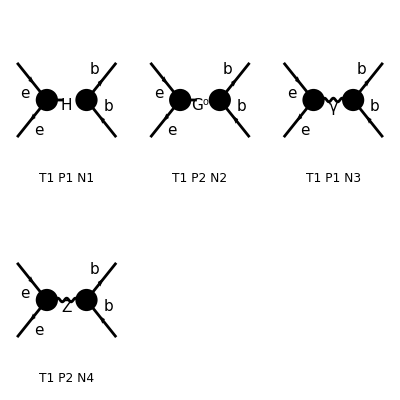

```mathematica
Process={F[2,{1}],-F[2,{1}]}-> {F[4,{3}],-F[4,{3}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//FullSimplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

FeynAmpList(({F(2,{1}),-F(2,{1})}→{F(4,{3}),-F(4,{3})})→(F(2,{1}) | p1 | ME | {-Charge,LeptonNumber}
-F(2,{1}) | p2 | ME | {Charge,-LeptonNumber})→(F(4,{3,Col3}) | k1 | MB | {-Charge/3,(2 ColorCharge)/(√3)}
-F(4,{3,Col4}) | k2 | MB | {Charge/3,-(2 ColorCharge)/(√3)}),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],1/((k1+k2)^2-MH2) SumOver(Col3,3,External) SumOver(Col4,3,External) (-v̄(p2,ME).(-(ⅈ EL ME om_-)/(2 MW SW)-(ⅈ EL ME om_+)/(2 MW SW)).u(p1,ME)) ū(k1,MB).(-(ⅈ EL MB om_- IndexDelta(Col3,Col4))/(2 MW SW)-(ⅈ EL MB om_+ IndexDelta(Col3,Col4))/(2 MW SW)).v(k2,MB)),FeynAmp(GraphID(Topology==1,Generic==1,Particles==2,Number==2),Integral[],1/((k1+k2)^2-MZ2) SumOver(Col3,3,External) SumOver(Col4,3,External) (-v̄(p2,ME).((EL ME om_+)/(2 MW SW)-(EL ME om_-)/(2 MW SW)).u(p1,ME)) ū(k1,MB).((EL MB om_+ IndexDelta(Col3,Col4))/(2 MW SW)-(EL MB om_- IndexDelta(Col3,Col4))/(2 MW SW)).v(k2,MB)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==3),Integral[],1/(k1+k2)^2 g(Lor1,Lor2) SumOver(Col3,3,External) SumOver(Col4,3,External) v̄(p2,ME).(ⅈ EL ga(Lor1).om_-+ⅈ EL ga(Lor1).om_+).u(p1,ME) ū(k1,MB).(1/3 ⅈ EL IndexDelta(Col3,Col4) ga(Lor2).om_-+1/3 ⅈ EL IndexDelta(Col3,Col4) ga(Lor2).om_+).v(k2,MB)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==4),Integral[],1/((k1+k2)^2-MZ2) g(Lor1,Lor2) SumOver(Col3,3,External) SumOver(Col4,3,External) v̄(p2,ME).((ⅈ EL (SW2-1/2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW ga(Lor1).om_+)/CW).u(p1,ME) ū(k1,MB).((ⅈ EL (SW2/3-1/2) IndexDelta(Col3,Col4) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW IndexDelta(Col3,Col4) ga(Lor2).om_+)/(3 CW)).v(k2,MB)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 64 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

1/(12 CW2^2 MW2^2 SW2^2)π^2 Alfa2 (2 MB2 ME2 (9 CW2^2 ME2 (2 MB2-S) (Den(S,MH2))^2+(Den(S,MZ2))^2 (9 CW2^2 ME2 (S-2 MB2)+9 CW2 MW2 (-2 MB2-2 ME2+T+U)+16 MW2^2 SW2^2 (4 (SW2-2) SW2+3))+64 CW2^2 MW2^2 SW2^2 (Den(S,0))^2+16 CW2 MW2 SW2 Den(S,0) (3 CW2 (T-U) Den(S,MH2)+MW2 (3-8 CW2 SW2) Den(S,MZ2))-3 CW2 MW2 (16 CW2 SW2-3) (T-U) Den(S,MH2) Den(S,MZ2))+9 CW2^2 MB2 ME2 ((-2 S (2 MB2+ME2)+12 MB2 ME2+S^2) (Den(S,MH2))^2+(4 MB2 ME2+S (S-2 ME2)) (Den(S,MZ2))^2)+4 MW2^2 SW2^2 (MB2+ME2-T)^2 ((2 CW2 Den(S,0)+(2 SW2-3) Den(S,MZ2))^2+(2 CW2 Den(S,0)+(2 SW2-1) Den(S,MZ2))^2)+MW2^2 (MB2+ME2-U)^2 (16 SW2^2 (CW2 Den(S,0)+SW2 Den(S,MZ2))^2+(4 CW2 SW2 Den(S,0)+(4 (SW2-2) SW2+3) Den(S,MZ2))^2)+4 MW2^2 SW2 (2 CW2 Den(S,0)+(2 SW2-3) Den(S,MZ2)) (4 CW2 S SW2 (MB2+ME2) Den(S,0)+Den(S,MZ2) (4 S SW2^2 (MB2+ME2)+8 ME2 SW2 (MB2-S)+3 ME2 (S-2 MB2)))-4 MW2^2 SW2 (2 CW2 Den(S,0)+(2 SW2-1) Den(S,MZ2)) (4 ME2 SW2 (2 MB2-S) (CW2 Den(S,0)+SW2 Den(S,MZ2))+MB2 (2 ME2-S) (4 CW2 SW2 Den(S,0)+(4 (SW2-2) SW2+3) Den(S,MZ2))))

```mathematica
resFCeebb=square1//.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),ME2->0}//FullSimplify[#,S+T+U==2MB2]&
```

1/(192 cw^4 S^2 sw^4 (MZ2-S)^2)ee^4 (4 MB2 S sw^2 (2 cw^2 (MZ2-S)-2 S sw^2+S) (4 cw^2 MZ2 sw^2+S (-4 sw^2 (cw^2+sw^2-2)-3))+4 sw^4 (MB2-T)^2 ((2 cw^2 (MZ2-S)-2 S sw^2+S)^2+(2 cw^2 (MZ2-S)+S (3-2 sw^2))^2)+(MB2-U)^2 ((4 cw^2 MZ2 sw^2+S (-4 sw^2 (cw^2+sw^2-2)-3))^2+16 sw^4 (cw^2 MZ2-S (cw^2+sw^2))^2)+16 S sw^2 (2 cw^2 (MZ2-S)+S (3-2 sw^2)) (cw^2 MB2 sw^2 (MZ2-S)-MB2 S sw^4))

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATAReebb=Get["resANATAReebb.m"];
```

```mathematica
FullSimplify[1/16 resANATAReebb-resFCeebb,{S+T+U==2MB2,cw^2+sw^2==1}]
```

0

## d d~ -> e+ e-

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
Addee=GenerateAmplitude[{d,dbar}->{e,ebar},OutputName->"ddee",Dimension->4]
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddee.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/ddee/ddee_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {d, dbar} -> {e, ebar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{d(p1),dbar(p2)}→{e(p3),ebar(p4)}},Total→2,Name→ddee,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC1 GC3 Den(-p1-p2,0) (ū)_Spin2(p3,0) v_Spin4(p4,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0),DiagramID(2)→(-1/4 ⅈ GC13 GC15+(ⅈ GC13 GC35)/4-(ⅈ GC15 GC34)/4+(ⅈ GC34 GC35)/4) Den(-p1-p2,MZ) (ū)_Spin2(p3,0) v_Spin4(p4,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2 γ^5)_(Spin2 Spin4) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0)+(-1/4 ⅈ GC13 GC15-(ⅈ GC13 GC35)/4+(ⅈ GC15 GC34)/4+(ⅈ GC34 GC35)/4) Den(-p1-p2,MZ) (ū)_Spin2(p3,0) v_Spin4(p4,0) (γ^iLor2)_(Spin2 Spin4) (γ^iLor2 γ^5)_(Spin1 Spin3) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0)+((ⅈ GC13 GC15)/4-(ⅈ GC13 GC35)/4-(ⅈ GC15 GC34)/4+(ⅈ GC34 GC35)/4) Den(-p1-p2,MZ) (ū)_Spin2(p3,0) v_Spin4(p4,0) (γ^iLor2 γ^5)_(Spin1 Spin3) (γ^iLor2 γ^5)_(Spin2 Spin4) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0)+((ⅈ GC13 GC15)/4+(ⅈ GC13 GC35)/4+(ⅈ GC15 GC34)/4+(ⅈ GC34 GC35)/4) Den(-p1-p2,MZ) (ū)_Spin2(p3,0) v_Spin4(p4,0) (γ^iLor2)_(Spin1 Spin3) (γ^iLor2)_(Spin2 Spin4) (v̄)_Spin3^Colour3(p2,0) u_Spin1^Colour3(p1,0)}|>

```mathematica
AddeeC=GenerateAmplitudeConjugate[{d,dbar}->{e,ebar},OutputName->"ddee",Dimension->4]
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ddee.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/ddee/ddee_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {d, dbar} -> {e, ebar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{d(p1),dbar(p2)}→{e(p3),ebar(p4)}},Total→2,Name→ddee,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC1 GC3 Den(-p1-p2,0) (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0),DiagramID(2)→Den(-p1-p2,MZ) (γ^5 γ^iLorC2)_(SpinC1 SpinC3) (γ^5 γ^iLorC2)_(SpinC2 SpinC4) (-1/4 ⅈ GC13 GC15 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)+1/4 ⅈ GC13 GC35 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)+1/4 ⅈ GC15 GC34 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)-1/4 ⅈ GC34 GC35 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0))+Den(-p1-p2,MZ) (γ^iLorC2)_(SpinC2 SpinC4) (γ^5 γ^iLorC2)_(SpinC1 SpinC3) (-1/4 ⅈ GC13 GC15 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)-1/4 ⅈ GC13 GC35 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)+1/4 ⅈ GC15 GC34 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)+1/4 ⅈ GC34 GC35 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0))+Den(-p1-p2,MZ) (γ^iLorC2)_(SpinC1 SpinC3) (γ^5 γ^iLorC2)_(SpinC2 SpinC4) (-1/4 ⅈ GC13 GC15 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)+1/4 ⅈ GC13 GC35 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)-1/4 ⅈ GC15 GC34 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)+1/4 ⅈ GC34 GC35 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0))+Den(-p1-p2,MZ) (γ^iLorC2)_(SpinC1 SpinC3) (γ^iLorC2)_(SpinC2 SpinC4) (-1/4 ⅈ GC13 GC15 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)-1/4 ⅈ GC13 GC35 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)-1/4 ⅈ GC15 GC34 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0)-1/4 ⅈ GC34 GC35 (u^†)_SpinC2(p3,0) ((v̄)^†)_SpinC4(p4,0) ((ū)^†)_SpinC1^ColourC3(p1,0) (v^†)_SpinC3^ColourC3(p2,0))}|>

```mathematica
AmpSQddee=GenerateAmplitudeSquare[Addee,AddeeC,Dimension->4,CasimirValues->True]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{d(p1),dbar(p2)}→{e(p3),ebar(p4)}},Name→ddee,LoopOrder→0,Kinematics→{p1^2→0,p1.p1→0,p2^2→0,p2.p2→0,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→S/2,p1.p3→-T/2,p2.p3→-U/2,1/(p1.p2)→2/S,1/(p1.p3)→-2/T,1/(p2.p3)→-2/U,p4→p1+p2-p3},Amplitudes→-1/(12 cw^4 sw2^2)ee^4 (32 cw^4 sw2^2 (S (T+U)+2 T U) (Den(-p1-p2,0))^2+8 cw^2 sw2 Den(-p1-p2,0) Den(-p1-p2,MZ) (3 cw^4 U (S+T)-2 cw^2 sw2 (S (4 T+U)+5 T U)+3 sw2^2 U (S+T))+(Den(-p1-p2,MZ))^2 (9 cw^8 U (S+T)-12 cw^6 sw2 U (S+T)+2 cw^4 sw2^2 (20 S T-S U+19 T U)+4 cw^2 sw2^3 (S (4 T+U)+5 T U)+sw2^4 (8 S T+17 S U+25 T U)))|>

```mathematica
resANATARddee=AmpSQddee[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(p3-p1)->√U,(p3-p2)->√T,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

-(ee^4 ((32 cw^4 sw^4 (S (T+U)+2 T U))/S^2+(8 cw^2 sw^2 (3 cw^4 U (S+T)-2 cw^2 sw^2 (S (4 T+U)+5 T U)+3 sw^4 U (S+T)))/(S (S-MZ^2))+(9 cw^8 U (S+T)-12 cw^6 sw^2 U (S+T)+2 cw^4 sw^4 (20 S T-S U+19 T U)+4 cw^2 sw^6 (S (4 T+U)+5 T U)+sw^8 (8 S T+17 S U+25 T U))/((S-MZ^2)^2)))/(12 cw^4 sw^4)

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARddee.m",resANATARddee];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 4 diagrams

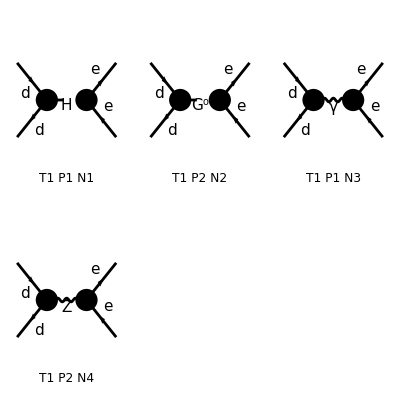

```mathematica
Process={F[4,{1}],-F[4,{1}]}-> {F[2,{1}],-F[2,{1}]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//FullSimplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

FeynAmpList(({F(4,{1}),-F(4,{1})}→{F(2,{1}),-F(2,{1})})→(F(4,{1,Col1}) | p1 | MD | {-Charge/3,(2 ColorCharge)/(√3)}
-F(4,{1,Col2}) | p2 | MD | {Charge/3,-(2 ColorCharge)/(√3)})→(F(2,{1}) | k1 | ME | {-Charge,LeptonNumber}
-F(2,{1}) | k2 | ME | {Charge,-LeptonNumber}),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],1/((k1+k2)^2-MH2) SumOver(Col1,3,External) SumOver(Col2,3,External) ū(k1,ME).(-(ⅈ EL ME om_-)/(2 MW SW)-(ⅈ EL ME om_+)/(2 MW SW)).v(k2,ME) (-v̄(p2,MD).(-(ⅈ EL MD om_- IndexDelta(Col1,Col2))/(2 MW SW)-(ⅈ EL MD om_+ IndexDelta(Col1,Col2))/(2 MW SW)).u(p1,MD))),FeynAmp(GraphID(Topology==1,Generic==1,Particles==2,Number==2),Integral[],1/((k1+k2)^2-MZ2) SumOver(Col1,3,External) SumOver(Col2,3,External) ū(k1,ME).((EL ME om_+)/(2 MW SW)-(EL ME om_-)/(2 MW SW)).v(k2,ME) (-v̄(p2,MD).((EL MD om_+ IndexDelta(Col1,Col2))/(2 MW SW)-(EL MD om_- IndexDelta(Col1,Col2))/(2 MW SW)).u(p1,MD))),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==3),Integral[],1/(k1+k2)^2 g(Lor1,Lor2) SumOver(Col1,3,External) SumOver(Col2,3,External) ū(k1,ME).(ⅈ EL ga(Lor2).om_-+ⅈ EL ga(Lor2).om_+).v(k2,ME) v̄(p2,MD).(1/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_-+1/3 ⅈ EL IndexDelta(Col1,Col2) ga(Lor1).om_+).u(p1,MD)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==4),Integral[],1/((k1+k2)^2-MZ2) g(Lor1,Lor2) SumOver(Col1,3,External) SumOver(Col2,3,External) ū(k1,ME).((ⅈ EL (SW2-1/2) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW ga(Lor2).om_+)/CW).v(k2,ME) v̄(p2,MD).((ⅈ EL (SW2/3-1/2) IndexDelta(Col1,Col2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW IndexDelta(Col1,Col2) ga(Lor1).om_+)/(3 CW)).u(p1,MD)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 64 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-2.frm

running FORM...

ok

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

1/(12 CW2^2 MW2^2 SW2^2)π^2 Alfa2 (9 CW2^2 MD2 ME2 ((-2 S (2 MD2+ME2)+12 MD2 ME2+S^2) (Den(S,MH2))^2+(4 MD2 ME2+S (S-2 ME2)) (Den(S,MZ2))^2)+2 MD2 (3 CW2 ME2 (Den(S,MH2)+Den(S,MZ2)) (3 CW2 ME2 (2 MD2-S) Den(S,MH2)+Den(S,MZ2) (3 CW2 ME2 (S-2 MD2)+8 CW2 MW2 SW2 (U-T)-3 MW2 (MD2+ME2-T))+8 CW2 MW2 SW2 (T-U) Den(S,0))+8 MW2^2 SW2^2 (2 CW2 Den(S,0)+(2 SW2-3) Den(S,MZ2)) (Den(S,MZ2) (S SW2-2 CW2 ME2)+CW2 (2 ME2+S) Den(S,0)))-2 ME2 MW2 (8 MW2 SW2^2 (2 MD2-S) (CW2 Den(S,0)+SW2 Den(S,MZ2)) (2 CW2 Den(S,0)+(2 SW2-1) Den(S,MZ2))-3 CW2 MD2 (Den(S,MH2)-Den(S,MZ2)) (Den(S,MZ2) (8 CW2 SW2 (U-T)+3 MD2+3 ME2-3 U)+8 CW2 SW2 (T-U) Den(S,0)))+4 MW2^2 SW2^2 (MD2+ME2-T)^2 ((2 CW2 Den(S,0)+(2 SW2-3) Den(S,MZ2))^2+(2 CW2 Den(S,0)+(2 SW2-1) Den(S,MZ2))^2)+MW2^2 (MD2+ME2-U)^2 (16 SW2^2 (CW2 Den(S,0)+SW2 Den(S,MZ2))^2+(4 CW2 SW2 Den(S,0)+(4 (SW2-2) SW2+3) Den(S,MZ2))^2)+4 MW2^2 SW2 (4 CW2 SW2 Den(S,0)+(4 (SW2-2) SW2+3) Den(S,MZ2)) (2 CW2 S (MD2+ME2) Den(S,0)+Den(S,MZ2) (2 S SW2 (MD2+ME2)+8 MD2 ME2-MD2 S-3 ME2 S)))

```mathematica
resFCddee=square1//.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),ME2->0,MD2->0}//FullSimplify[#,S+T+U==0]&
```

(ee^4 (4 sw^4 T^2 ((2 cw^2 (MZ2+T+U)-2 S sw^2+S)^2+(2 cw^2 (MZ2+T+U)+S (3-2 sw^2))^2)+U^2 (16 sw^4 (S sw^2-cw^2 (MZ2+T+U))^2+(4 cw^2 sw^2 (MZ2+T+U)+(4 sw^4-8 sw^2+3) (T+U))^2)))/(192 cw^4 S^2 sw^4 (MZ2+T+U)^2)

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARddee=Get["resANATARddee.m"];
```

```mathematica
FullSimplify[1/16 resANATARddee-resFCddee,{S+T+U==0,cw^2+sw^2==1}]
```

0

## τ τ -> WW

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AtataWW=GenerateAmplitude[{ta,tabar}->{Wbar,W},OutputName->"tataWW",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tataWW.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tataWW/tataWW_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {ta, tabar} -> {Wbar, W}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{ta(p1),tabar(p2)}→{Wbar(p3),W(p4)}},Total→4,Name→tataWW,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2+MW^2-T),p2.p3→1/2 (MTA^2+MW^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2+MW^2-T),1/(p2.p3)→2/(MTA^2+MW^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC53 GC61 𝕀_Spin3Spin1 Den(-p1-p2,MH) ε_Lor2(p3,MW) ε_Lor2(p4,MW) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA),DiagramID(2)→-ⅈ GC3^2 Den(-p1-p2,0) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) ((γ^iLor2)_(Spin1 Spin3) (ε_iLor2(p4,MW) (ε_p1(p3,MW)+ε_p2(p3,MW)+ε_p4(p3,MW))-ε_iLor2(p3,MW) (ε_p1(p4,MW)+ε_p2(p4,MW)+ε_p3(p4,MW)))+ε_Lor2(p3,MW) ε_Lor2(p4,MW) ((γ·p3)_(Spin1 Spin3)-(γ·p4)_(Spin1 Spin3))),DiagramID(3)→1/2 ⅈ GC27 Den(-p1-p2,MZ) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) (-(GC15-GC35) (γ^iLor2 γ^5)_(Spin1 Spin3) (ε_iLor2(p3,MW) (ε_p1(p4,MW)+ε_p2(p4,MW)+ε_p3(p4,MW))-ε_iLor2(p4,MW) (ε_p1(p3,MW)+ε_p2(p3,MW)+ε_p4(p3,MW)))+ε_Lor2(p3,MW) ε_Lor2(p4,MW) ((GC15-GC35) (((γ·p3)γ^5)_(Spin1 Spin3)-((γ·p4)γ^5)_(Spin1 Spin3))-((GC15+GC35) (γ·p3)_(Spin1 Spin3))+(GC15+GC35) (γ·p4)_(Spin1 Spin3))+(GC15+GC35) (γ^iLor2)_(Spin1 Spin3) (ε_iLor2(p3,MW) (ε_p1(p4,MW)+ε_p2(p4,MW)+ε_p3(p4,MW))-ε_iLor2(p4,MW) (ε_p1(p3,MW)+ε_p2(p3,MW)+ε_p4(p3,MW)))),DiagramID(4)→-1/4 ⅈ GC25^2 Den(p1-p3,0) ε_Lor2(p3,MW) ε_Lor4(p4,MW) ((γ^Lor4)_(iSpin1 Spin3)-(γ^Lor4 γ^5)_(iSpin1 Spin3)) ((γ^Lor2)_(iSpin2 Spin1)-(γ^Lor2 γ^5)_(iSpin2 Spin1)) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) (γ·(p1-p3))_(iSpin1 iSpin2)}|>

```mathematica
AtataWWC=GenerateAmplitudeConjugate[{ta,tabar}->{Wbar,W},OutputName->"tataWW",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tataWW.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tataWW/tataWW_0

Computing amplitudes...

A total of 4 diagrams have been generated for the process {ta, tabar} -> {Wbar, W}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{ta(p1),tabar(p2)}→{Wbar(p3),W(p4)}},Total→4,Name→tataWW,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2+MW^2-T),p2.p3→1/2 (MTA^2+MW^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2+MW^2-T),1/(p2.p3)→2/(MTA^2+MW^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC53 GC61 𝕀_SpinC1SpinC3 Den(-p1-p2,MH) (ε^†)_LorC2^(p3,MW) (ε^†)_LorC2^(p4,MW) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA),DiagramID(2)→ⅈ GC3^2 Den(-p1-p2,0) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) ((γ^iLorC2)_(SpinC1 SpinC3) ((ε^†)_iLorC2^(p4,MW) ((ε^†)_p1^(p3,MW)+(ε^†)_p2^(p3,MW)+(ε^†)_p4^(p3,MW))-(ε^†)_iLorC2^(p3,MW) ((ε^†)_p1^(p4,MW)+(ε^†)_p2^(p4,MW)+(ε^†)_p3^(p4,MW)))+(ε^†)_LorC2^(p3,MW) (ε^†)_LorC2^(p4,MW) ((γ·p3)_(SpinC1 SpinC3)-(γ·p4)_(SpinC1 SpinC3))),DiagramID(3)→-1/2 ⅈ GC27 Den(-p1-p2,MZ) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) ((GC15+GC35) (γ^iLorC2)_(SpinC1 SpinC3) ((ε^†)_iLorC2^(p3,MW) ((ε^†)_p1^(p4,MW)+(ε^†)_p2^(p4,MW)+(ε^†)_p3^(p4,MW))-(ε^†)_iLorC2^(p4,MW) ((ε^†)_p1^(p3,MW)+(ε^†)_p2^(p3,MW)+(ε^†)_p4^(p3,MW)))+(GC15-GC35) (γ^5 γ^iLorC2)_(SpinC1 SpinC3) ((ε^†)_iLorC2^(p3,MW) ((ε^†)_p1^(p4,MW)+(ε^†)_p2^(p4,MW)+(ε^†)_p3^(p4,MW))-(ε^†)_iLorC2^(p4,MW) ((ε^†)_p1^(p3,MW)+(ε^†)_p2^(p3,MW)+(ε^†)_p4^(p3,MW)))+(ε^†)_LorC2^(p3,MW) (ε^†)_LorC2^(p4,MW) (-(GC15-GC35) ((γ^5(γ·p3))_(SpinC1 SpinC3)-(γ^5(γ·p4))_(SpinC1 SpinC3))-((GC15+GC35) (γ·p3)_(SpinC1 SpinC3))+(GC15+GC35) (γ·p4)_(SpinC1 SpinC3))),DiagramID(4)→1/4 ⅈ GC25^2 Den(p1-p3,0) (ε^†)_LorC2^(p3,MW) (ε^†)_LorC4^(p4,MW) ((γ^5 γ^LorC4)_(iSpinC1 SpinC3)+(γ^LorC4)_(iSpinC1 SpinC3)) ((γ^5 γ^LorC2)_(iSpinC2 SpinC1)+(γ^LorC2)_(iSpinC2 SpinC1)) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) ((γ·p1)_(iSpinC1 iSpinC2)-(γ·p3)_(iSpinC1 iSpinC2))}|>

```mathematica
AmpSQtataWW=GenerateAmplitudeSquare[AtataWW,AtataWWC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{ta(p1),tabar(p2)}→{Wbar(p3),W(p4)}},Name→tataWW,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2+MW^2-T),p2.p3→1/2 (MTA^2+MW^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2+MW^2-T),1/(p2.p3)→2/(MTA^2+MW^2-U),p4→p1+p2-p3},Amplitudes→1/(16 MW^4 sw2^2)ee^4 (16 cw^4 (Den(-p1-p2,MZ))^2 MTA^8+16 sw2^2 (Den(-p1-p2,MZ))^2 MTA^8+32 cw^2 sw2 (Den(-p1-p2,MZ))^2 MTA^8+12 (Den(p1-p3,0))^2 MTA^8+32 cw^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^8-32 sw2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^8+32 cw^4 MW^2 (Den(-p1-p2,MZ))^2 MTA^6+224 MW^2 sw2^2 (Den(-p1-p2,MZ))^2 MTA^6-56 S sw2^2 (Den(-p1-p2,MZ))^2 MTA^6-24 cw^4 S (Den(-p1-p2,MZ))^2 MTA^6-128 cw^2 MW^2 sw2 (Den(-p1-p2,MZ))^2 MTA^6-16 cw^2 S sw2 (Den(-p1-p2,MZ))^2 MTA^6-24 cw^4 T (Den(-p1-p2,MZ))^2 MTA^6-24 sw2^2 T (Den(-p1-p2,MZ))^2 MTA^6-48 cw^2 sw2 T (Den(-p1-p2,MZ))^2 MTA^6-24 cw^4 U (Den(-p1-p2,MZ))^2 MTA^6-24 sw2^2 U (Den(-p1-p2,MZ))^2 MTA^6-48 cw^2 sw2 U (Den(-p1-p2,MZ))^2 MTA^6+16 MW^2 (Den(p1-p3,0))^2 MTA^6-16 S (Den(p1-p3,0))^2 MTA^6-24 T (Den(p1-p3,0))^2 MTA^6-16 U (Den(p1-p3,0))^2 MTA^6+48 cw^2 MW^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^6-40 cw^2 S Den(-p1-p2,MZ) Den(p1-p3,0) MTA^6-80 MW^2 sw2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^6+40 S sw2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^6-48 cw^2 T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^6+48 sw2 T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^6-48 cw^2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^6+48 sw2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^6+8 cw^4 S^2 (Den(-p1-p2,MZ))^2 MTA^4+256 MW^4 sw2^2 (Den(-p1-p2,MZ))^2 MTA^4+40 S^2 sw2^2 (Den(-p1-p2,MZ))^2 MTA^4-48 MW^2 S sw2^2 (Den(-p1-p2,MZ))^2 MTA^4+12 cw^4 T^2 (Den(-p1-p2,MZ))^2 MTA^4+12 sw2^2 T^2 (Den(-p1-p2,MZ))^2 MTA^4+24 cw^2 sw2 T^2 (Den(-p1-p2,MZ))^2 MTA^4+12 cw^4 U^2 (Den(-p1-p2,MZ))^2 MTA^4+12 sw2^2 U^2 (Den(-p1-p2,MZ))^2 MTA^4+24 cw^2 sw2 U^2 (Den(-p1-p2,MZ))^2 MTA^4-48 cw^4 MW^2 S (Den(-p1-p2,MZ))^2 MTA^4-256 cw^2 MW^4 sw2 (Den(-p1-p2,MZ))^2 MTA^4-16 cw^2 S^2 sw2 (Den(-p1-p2,MZ))^2 MTA^4-96 cw^2 MW^2 S sw2 (Den(-p1-p2,MZ))^2 MTA^4-24 cw^4 MW^2 T (Den(-p1-p2,MZ))^2 MTA^4-184 MW^2 sw2^2 T (Den(-p1-p2,MZ))^2 MTA^4+76 S sw2^2 T (Den(-p1-p2,MZ))^2 MTA^4+28 cw^4 S T (Den(-p1-p2,MZ))^2 MTA^4+112 cw^2 MW^2 sw2 T (Den(-p1-p2,MZ))^2 MTA^4+8 cw^2 S sw2 T (Den(-p1-p2,MZ))^2 MTA^4-24 cw^4 MW^2 U (Den(-p1-p2,MZ))^2 MTA^4-184 MW^2 sw2^2 U (Den(-p1-p2,MZ))^2 MTA^4+76 S sw2^2 U (Den(-p1-p2,MZ))^2 MTA^4+28 cw^4 S U (Den(-p1-p2,MZ))^2 MTA^4+112 cw^2 MW^2 sw2 U (Den(-p1-p2,MZ))^2 MTA^4+8 cw^2 S sw2 U (Den(-p1-p2,MZ))^2 MTA^4+24 cw^4 T U (Den(-p1-p2,MZ))^2 MTA^4+24 sw2^2 T U (Den(-p1-p2,MZ))^2 MTA^4+48 cw^2 sw2 T U (Den(-p1-p2,MZ))^2 MTA^4-20 MW^4 (Den(p1-p3,0))^2 MTA^4+4 S^2 (Den(p1-p3,0))^2 MTA^4+16 T^2 (Den(p1-p3,0))^2 MTA^4+4 U^2 (Den(p1-p3,0))^2 MTA^4-20 MW^2 S (Den(p1-p3,0))^2 MTA^4-4 MW^2 T (Den(p1-p3,0))^2 MTA^4+32 S T (Den(p1-p3,0))^2 MTA^4-20 MW^2 U (Den(p1-p3,0))^2 MTA^4+8 S U (Den(p1-p3,0))^2 MTA^4+28 T U (Den(p1-p3,0))^2 MTA^4-80 cw^2 MW^4 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4+8 cw^2 S^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4+24 cw^2 T^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-24 sw2 T^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4+24 cw^2 U^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-24 sw2 U^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-88 cw^2 MW^2 S Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-48 MW^4 sw2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-8 S^2 sw2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-72 MW^2 S sw2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-24 cw^2 MW^2 T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4+56 cw^2 S T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4+88 MW^2 sw2 T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-56 S sw2 T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-40 cw^2 MW^2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4+32 cw^2 S U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4+40 MW^2 sw2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-32 S sw2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4+48 cw^2 T U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-48 sw2 T U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^4-2 (4 MTA^2-S) (4 MTA^4-4 (T+U) MTA^2+8 MW^4+(T+U)^2) (Den(-p1-p2,MH))^2 MTA^2+112 cw^4 MW^6 (Den(-p1-p2,MZ))^2 MTA^2-2 cw^4 T^3 (Den(-p1-p2,MZ))^2 MTA^2-2 sw2^2 T^3 (Den(-p1-p2,MZ))^2 MTA^2-4 cw^2 sw2 T^3 (Den(-p1-p2,MZ))^2 MTA^2-2 cw^4 U^3 (Den(-p1-p2,MZ))^2 MTA^2-2 sw2^2 U^3 (Den(-p1-p2,MZ))^2 MTA^2-4 cw^2 sw2 U^3 (Den(-p1-p2,MZ))^2 MTA^2+32 cw^4 MW^2 S^2 (Den(-p1-p2,MZ))^2 MTA^2+304 MW^6 sw2^2 (Den(-p1-p2,MZ))^2 MTA^2+192 MW^2 S^2 sw2^2 (Den(-p1-p2,MZ))^2 MTA^2-384 MW^4 S sw2^2 (Den(-p1-p2,MZ))^2 MTA^2+4 cw^4 MW^2 T^2 (Den(-p1-p2,MZ))^2 MTA^2+36 MW^2 sw2^2 T^2 (Den(-p1-p2,MZ))^2 MTA^2-34 S sw2^2 T^2 (Den(-p1-p2,MZ))^2 MTA^2-10 cw^4 S T^2 (Den(-p1-p2,MZ))^2 MTA^2-24 cw^2 MW^2 sw2 T^2 (Den(-p1-p2,MZ))^2 MTA^2+4 cw^2 S sw2 T^2 (Den(-p1-p2,MZ))^2 MTA^2+4 cw^4 MW^2 U^2 (Den(-p1-p2,MZ))^2 MTA^2+36 MW^2 sw2^2 U^2 (Den(-p1-p2,MZ))^2 MTA^2-34 S sw2^2 U^2 (Den(-p1-p2,MZ))^2 MTA^2-10 cw^4 S U^2 (Den(-p1-p2,MZ))^2 MTA^2-24 cw^2 MW^2 sw2 U^2 (Den(-p1-p2,MZ))^2 MTA^2+4 cw^2 S sw2 U^2 (Den(-p1-p2,MZ))^2 MTA^2-6 cw^4 T U^2 (Den(-p1-p2,MZ))^2 MTA^2-6 sw2^2 T U^2 (Den(-p1-p2,MZ))^2 MTA^2-12 cw^2 sw2 T U^2 (Den(-p1-p2,MZ))^2 MTA^2+32 cw^2 MW^6 sw2 (Den(-p1-p2,MZ))^2 MTA^2-96 cw^2 MW^2 S^2 sw2 (Den(-p1-p2,MZ))^2 MTA^2+384 cw^2 MW^4 S sw2 (Den(-p1-p2,MZ))^2 MTA^2-8 cw^4 S^2 T (Den(-p1-p2,MZ))^2 MTA^2-128 MW^4 sw2^2 T (Den(-p1-p2,MZ))^2 MTA^2-40 S^2 sw2^2 T (Den(-p1-p2,MZ))^2 MTA^2+24 MW^2 S sw2^2 T (Den(-p1-p2,MZ))^2 MTA^2+24 cw^4 MW^2 S T (Den(-p1-p2,MZ))^2 MTA^2+128 cw^2 MW^4 sw2 T (Den(-p1-p2,MZ))^2 MTA^2+16 cw^2 S^2 sw2 T (Den(-p1-p2,MZ))^2 MTA^2+48 cw^2 MW^2 S sw2 T (Den(-p1-p2,MZ))^2 MTA^2-8 cw^4 S^2 U (Den(-p1-p2,MZ))^2 MTA^2-128 MW^4 sw2^2 U (Den(-p1-p2,MZ))^2 MTA^2-40 S^2 sw2^2 U (Den(-p1-p2,MZ))^2 MTA^2+24 MW^2 S sw2^2 U (Den(-p1-p2,MZ))^2 MTA^2-6 cw^4 T^2 U (Den(-p1-p2,MZ))^2 MTA^2-6 sw2^2 T^2 U (Den(-p1-p2,MZ))^2 MTA^2-12 cw^2 sw2 T^2 U (Den(-p1-p2,MZ))^2 MTA^2+24 cw^4 MW^2 S U (Den(-p1-p2,MZ))^2 MTA^2+128 cw^2 MW^4 sw2 U (Den(-p1-p2,MZ))^2 MTA^2+16 cw^2 S^2 sw2 U (Den(-p1-p2,MZ))^2 MTA^2+48 cw^2 MW^2 S sw2 U (Den(-p1-p2,MZ))^2 MTA^2-8 cw^4 MW^2 T U (Den(-p1-p2,MZ))^2 MTA^2-8 MW^2 sw2^2 T U (Den(-p1-p2,MZ))^2 MTA^2-68 S sw2^2 T U (Den(-p1-p2,MZ))^2 MTA^2-20 cw^4 S T U (Den(-p1-p2,MZ))^2 MTA^2-16 cw^2 MW^2 sw2 T U (Den(-p1-p2,MZ))^2 MTA^2+8 cw^2 S sw2 T U (Den(-p1-p2,MZ))^2 MTA^2-8 MW^6 (Den(p1-p3,0))^2 MTA^2-4 T^3 (Den(p1-p3,0))^2 MTA^2+4 MW^2 S^2 (Den(p1-p3,0))^2 MTA^2+4 MW^2 T^2 (Den(p1-p3,0))^2 MTA^2-20 S T^2 (Den(p1-p3,0))^2 MTA^2+4 MW^2 U^2 (Den(p1-p3,0))^2 MTA^2-4 T U^2 (Den(p1-p3,0))^2 MTA^2+28 MW^4 S (Den(p1-p3,0))^2 MTA^2+12 MW^4 T (Den(p1-p3,0))^2 MTA^2-8 S^2 T (Den(p1-p3,0))^2 MTA^2+28 MW^4 U (Den(p1-p3,0))^2 MTA^2-16 T^2 U (Den(p1-p3,0))^2 MTA^2+8 MW^2 S U (Den(p1-p3,0))^2 MTA^2-8 MW^2 T U (Den(p1-p3,0))^2 MTA^2-12 S T U (Den(p1-p3,0))^2 MTA^2+16 cw^2 MW^6 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-4 cw^2 T^3 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+4 sw2 T^3 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-4 cw^2 U^3 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+4 sw2 U^3 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+48 cw^2 MW^2 S^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-4 cw^2 MW^2 T^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-24 cw^2 S T^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-20 MW^2 sw2 T^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+24 S sw2 T^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+12 cw^2 MW^2 U^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-8 cw^2 S U^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-4 MW^2 sw2 U^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+8 S sw2 U^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-12 cw^2 T U^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+12 sw2 T U^2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+112 cw^2 MW^4 S Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+80 MW^6 sw2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-128 MW^4 S sw2 Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+88 cw^2 MW^4 T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-12 cw^2 S^2 T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+20 cw^2 MW^2 S T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+56 MW^4 sw2 T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+12 S^2 sw2 T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+84 MW^2 S sw2 T Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+40 cw^2 MW^4 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-4 cw^2 S^2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-12 cw^2 T^2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+12 sw2 T^2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+60 cw^2 MW^2 S U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-56 MW^4 sw2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+4 S^2 sw2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-4 MW^2 S sw2 U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-24 cw^2 MW^2 T U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2-24 cw^2 S T U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+8 MW^2 sw2 T U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+24 S sw2 T U Den(-p1-p2,MZ) Den(p1-p3,0) MTA^2+4 Den(-p1-p2,MH) ((-8 MTA^6+2 (S+5 T+3 U) MTA^4-(-8 (T-U) MW^2+5 T^2+U^2+3 S T+S U+2 T U) MTA^2+T (S+T-U) (T+U)-2 MW^2 (T-U) (S+3 T+U)) Den(p1-p3,0)-(cw^2-3 sw2) (T-U) (8 MW^4+2 (T+U) MW^2-2 MTA^2 (2 MW^2+S)+S (T+U)) Den(-p1-p2,MZ)) MTA^2+8 sw2^2 (32 MW^8-8 (7 S+3 (T+U)) MW^6-4 (5 S^2+2 (T-U)^2) MW^4+2 (-6 (T+U) S^2+(T-U)^2 S+4 T U (T+U)) MW^2+8 MTA^6 (6 MW^2-S)+S ((T+U)^3+S (T^2+6 U T+U^2))+4 MTA^4 (16 MW^4-10 (T+U) MW^2+S (2 S+3 (T+U)))+2 MTA^2 (24 MW^6-16 (3 S+T+U) MW^4+4 (5 S^2+T^2+U^2) MW^2-S (T+U) (4 S+3 (T+U)))) (Den(-p1-p2,0))^2+32 cw^4 MW^8 (Den(-p1-p2,MZ))^2+5 S sw2^2 T^3 (Den(-p1-p2,MZ))^2+cw^4 S T^3 (Den(-p1-p2,MZ))^2-2 cw^2 S sw2 T^3 (Den(-p1-p2,MZ))^2+5 S sw2^2 U^3 (Den(-p1-p2,MZ))^2+cw^4 S U^3 (Den(-p1-p2,MZ))^2-2 cw^2 S sw2 U^3 (Den(-p1-p2,MZ))^2-20 cw^4 MW^4 S^2 (Den(-p1-p2,MZ))^2+160 MW^8 sw2^2 (Den(-p1-p2,MZ))^2-100 MW^4 S^2 sw2^2 (Den(-p1-p2,MZ))^2-280 MW^6 S sw2^2 (Den(-p1-p2,MZ))^2-8 cw^4 MW^4 T^2 (Den(-p1-p2,MZ))^2+cw^4 S^2 T^2 (Den(-p1-p2,MZ))^2-40 MW^4 sw2^2 T^2 (Den(-p1-p2,MZ))^2+5 S^2 sw2^2 T^2 (Den(-p1-p2,MZ))^2+10 MW^2 S sw2^2 T^2 (Den(-p1-p2,MZ))^2+2 cw^4 MW^2 S T^2 (Den(-p1-p2,MZ))^2+16 cw^2 MW^4 sw2 T^2 (Den(-p1-p2,MZ))^2-2 cw^2 S^2 sw2 T^2 (Den(-p1-p2,MZ))^2-4 cw^2 MW^2 S sw2 T^2 (Den(-p1-p2,MZ))^2-8 cw^4 MW^4 U^2 (Den(-p1-p2,MZ))^2+cw^4 S^2 U^2 (Den(-p1-p2,MZ))^2-40 MW^4 sw2^2 U^2 (Den(-p1-p2,MZ))^2+5 S^2 sw2^2 U^2 (Den(-p1-p2,MZ))^2+10 MW^2 S sw2^2 U^2 (Den(-p1-p2,MZ))^2+2 cw^4 MW^2 S U^2 (Den(-p1-p2,MZ))^2+16 cw^2 MW^4 sw2 U^2 (Den(-p1-p2,MZ))^2-2 cw^2 S^2 sw2 U^2 (Den(-p1-p2,MZ))^2-4 cw^2 MW^2 S sw2 U^2 (Den(-p1-p2,MZ))^2+8 cw^4 MW^2 T U^2 (Den(-p1-p2,MZ))^2+40 MW^2 sw2^2 T U^2 (Den(-p1-p2,MZ))^2+15 S sw2^2 T U^2 (Den(-p1-p2,MZ))^2+3 cw^4 S T U^2 (Den(-p1-p2,MZ))^2-16 cw^2 MW^2 sw2 T U^2 (Den(-p1-p2,MZ))^2-6 cw^2 S sw2 T U^2 (Den(-p1-p2,MZ))^2-56 cw^4 MW^6 S (Den(-p1-p2,MZ))^2-64 cw^2 MW^8 sw2 (Den(-p1-p2,MZ))^2+40 cw^2 MW^4 S^2 sw2 (Den(-p1-p2,MZ))^2+112 cw^2 MW^6 S sw2 (Den(-p1-p2,MZ))^2-24 cw^4 MW^6 T (Den(-p1-p2,MZ))^2-12 cw^4 MW^2 S^2 T (Den(-p1-p2,MZ))^2-120 MW^6 sw2^2 T (Den(-p1-p2,MZ))^2-60 MW^2 S^2 sw2^2 T (Den(-p1-p2,MZ))^2+48 cw^2 MW^6 sw2 T (Den(-p1-p2,MZ))^2+24 cw^2 MW^2 S^2 sw2 T (Den(-p1-p2,MZ))^2-24 cw^4 MW^6 U (Den(-p1-p2,MZ))^2-12 cw^4 MW^2 S^2 U (Den(-p1-p2,MZ))^2-120 MW^6 sw2^2 U (Den(-p1-p2,MZ))^2-60 MW^2 S^2 sw2^2 U (Den(-p1-p2,MZ))^2+8 cw^4 MW^2 T^2 U (Den(-p1-p2,MZ))^2+40 MW^2 sw2^2 T^2 U (Den(-p1-p2,MZ))^2+15 S sw2^2 T^2 U (Den(-p1-p2,MZ))^2+3 cw^4 S T^2 U (Den(-p1-p2,MZ))^2-16 cw^2 MW^2 sw2 T^2 U (Den(-p1-p2,MZ))^2-6 cw^2 S sw2 T^2 U (Den(-p1-p2,MZ))^2+48 cw^2 MW^6 sw2 U (Den(-p1-p2,MZ))^2+24 cw^2 MW^2 S^2 sw2 U (Den(-p1-p2,MZ))^2+16 cw^4 MW^4 T U (Den(-p1-p2,MZ))^2+6 cw^4 S^2 T U (Den(-p1-p2,MZ))^2+80 MW^4 sw2^2 T U (Den(-p1-p2,MZ))^2+30 S^2 sw2^2 T U (Den(-p1-p2,MZ))^2-20 MW^2 S sw2^2 T U (Den(-p1-p2,MZ))^2-4 cw^4 MW^2 S T U (Den(-p1-p2,MZ))^2-32 cw^2 MW^4 sw2 T U (Den(-p1-p2,MZ))^2-12 cw^2 S^2 sw2 T U (Den(-p1-p2,MZ))^2+8 cw^2 MW^2 S sw2 T U (Den(-p1-p2,MZ))^2-4 MW^2 T^3 (Den(p1-p3,0))^2+4 S T^3 (Den(p1-p3,0))^2-8 MW^4 S^2 (Den(p1-p3,0))^2-4 MW^4 T^2 (Den(p1-p3,0))^2+4 S^2 T^2 (Den(p1-p3,0))^2+4 MW^2 S T^2 (Den(p1-p3,0))^2-8 MW^4 U^2 (Den(p1-p3,0))^2+8 MW^2 T U^2 (Den(p1-p3,0))^2+8 MW^6 S (Den(p1-p3,0))^2+8 MW^6 T (Den(p1-p3,0))^2-16 MW^4 S T (Den(p1-p3,0))^2+8 MW^6 U (Den(p1-p3,0))^2+4 T^3 U (Den(p1-p3,0))^2+4 MW^2 T^2 U (Den(p1-p3,0))^2+4 S T^2 U (Den(p1-p3,0))^2-16 MW^4 S U (Den(p1-p3,0))^2-16 MW^4 T U (Den(p1-p3,0))^2+8 MW^2 S T U (Den(p1-p3,0))^2+16 cw^2 MW^8 Den(-p1-p2,MZ) Den(p1-p3,0)-8 cw^2 MW^2 S^3 Den(-p1-p2,MZ) Den(p1-p3,0)+4 cw^2 S T^3 Den(-p1-p2,MZ) Den(p1-p3,0)-4 S sw2 T^3 Den(-p1-p2,MZ) Den(p1-p3,0)-16 cw^2 MW^4 S^2 Den(-p1-p2,MZ) Den(p1-p3,0)-24 cw^2 MW^4 T^2 Den(-p1-p2,MZ) Den(p1-p3,0)+4 cw^2 S^2 T^2 Den(-p1-p2,MZ) Den(p1-p3,0)+8 cw^2 MW^2 S T^2 Den(-p1-p2,MZ) Den(p1-p3,0)+24 MW^4 sw2 T^2 Den(-p1-p2,MZ) Den(p1-p3,0)-4 S^2 sw2 T^2 Den(-p1-p2,MZ) Den(p1-p3,0)-8 MW^2 S sw2 T^2 Den(-p1-p2,MZ) Den(p1-p3,0)-8 cw^2 MW^4 U^2 Den(-p1-p2,MZ) Den(p1-p3,0)-8 cw^2 MW^2 S U^2 Den(-p1-p2,MZ) Den(p1-p3,0)+8 MW^4 sw2 U^2 Den(-p1-p2,MZ) Den(p1-p3,0)+8 MW^2 S sw2 U^2 Den(-p1-p2,MZ) Den(p1-p3,0)+8 cw^2 MW^2 T U^2 Den(-p1-p2,MZ) Den(p1-p3,0)+4 cw^2 S T U^2 Den(-p1-p2,MZ) Den(p1-p3,0)-8 MW^2 sw2 T U^2 Den(-p1-p2,MZ) Den(p1-p3,0)-4 S sw2 T U^2 Den(-p1-p2,MZ) Den(p1-p3,0)-24 cw^2 MW^6 S Den(-p1-p2,MZ) Den(p1-p3,0)-16 MW^8 sw2 Den(-p1-p2,MZ) Den(p1-p3,0)+8 MW^2 S^3 sw2 Den(-p1-p2,MZ) Den(p1-p3,0)+16 MW^4 S^2 sw2 Den(-p1-p2,MZ) Den(p1-p3,0)+24 MW^6 S sw2 Den(-p1-p2,MZ) Den(p1-p3,0)+8 cw^2 MW^6 T Den(-p1-p2,MZ) Den(p1-p3,0)-24 cw^2 MW^2 S^2 T Den(-p1-p2,MZ) Den(p1-p3,0)-16 cw^2 MW^4 S T Den(-p1-p2,MZ) Den(p1-p3,0)-8 MW^6 sw2 T Den(-p1-p2,MZ) Den(p1-p3,0)+24 MW^2 S^2 sw2 T Den(-p1-p2,MZ) Den(p1-p3,0)+16 MW^4 S sw2 T Den(-p1-p2,MZ) Den(p1-p3,0)-8 cw^2 MW^6 U Den(-p1-p2,MZ) Den(p1-p3,0)-16 cw^2 MW^2 S^2 U Den(-p1-p2,MZ) Den(p1-p3,0)+24 cw^2 MW^2 T^2 U Den(-p1-p2,MZ) Den(p1-p3,0)-24 MW^2 sw2 T^2 U Den(-p1-p2,MZ) Den(p1-p3,0)-24 cw^2 MW^4 S U Den(-p1-p2,MZ) Den(p1-p3,0)+8 MW^6 sw2 U Den(-p1-p2,MZ) Den(p1-p3,0)+16 MW^2 S^2 sw2 U Den(-p1-p2,MZ) Den(p1-p3,0)+24 MW^4 S sw2 U Den(-p1-p2,MZ) Den(p1-p3,0)-16 cw^2 MW^4 T U Den(-p1-p2,MZ) Den(p1-p3,0)+4 cw^2 S^2 T U Den(-p1-p2,MZ) Den(p1-p3,0)+8 cw^2 MW^2 S T U Den(-p1-p2,MZ) Den(p1-p3,0)+16 MW^4 sw2 T U Den(-p1-p2,MZ) Den(p1-p3,0)-4 S^2 sw2 T U Den(-p1-p2,MZ) Den(p1-p3,0)-8 MW^2 S sw2 T U Den(-p1-p2,MZ) Den(p1-p3,0)-4 sw2 Den(-p1-p2,0) (4 (T-U) (8 MW^4+2 (T+U) MW^2-2 MTA^2 (2 MW^2+S)+S (T+U)) Den(-p1-p2,MH) MTA^2-(cw^2-3 sw2) (32 MW^8-8 (7 S+3 (T+U)) MW^6-4 (5 S^2+2 (T-U)^2) MW^4+2 (-6 (T+U) S^2+(T-U)^2 S+4 T U (T+U)) MW^2+8 MTA^6 (6 MW^2-S)+S ((T+U)^3+S (T^2+6 U T+U^2))+4 MTA^4 (16 MW^4-10 (T+U) MW^2+S (2 S+3 (T+U)))+2 MTA^2 (24 MW^6-16 (3 S+T+U) MW^4+4 (5 S^2+T^2+U^2) MW^2-S (T+U) (4 S+3 (T+U)))) Den(-p1-p2,MZ)-2 (8 MTA^8+2 (8 MW^2-5 S-6 (T+U)) MTA^6-2 (2 MW^4+(S+7 T+5 U) MW^2-S^2-3 (T+U)^2-S (7 T+4 U)) MTA^4-(8 MW^6-2 (15 S+2 T+6 U) MW^4-2 (3 S^2-4 (T-U) S+(T-U)^2) MW^2+(T+U)^3+S^2 (3 T+U)+2 S (3 T^2+3 U T+U^2)) MTA^2+4 MW^8-2 MW^6 (3 S-T+U)-2 MW^4 (2 S^2+2 T S+3 U S+3 T^2+U^2+2 T U)+S T (T^2+U^2+S (T+U))-2 MW^2 (S^3+(3 T+2 U) S^2-(T^2+U T-U^2) S-T U (3 T+U))) Den(p1-p3,0)))|>

```mathematica
resANATARtataWW=AmpSQtataWW[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(p1-p3)->√T,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/(16 MW^4 sw^4)ee^4 ((16 sw^4 MTA^8)/((S-MZ^2)^2)+(32 cw^2 sw^2 MTA^8)/((S-MZ^2)^2)-(32 sw^2 MTA^8)/((S-MZ^2) T)+(32 cw^2 MTA^8)/((S-MZ^2) T)+(16 cw^4 MTA^8)/((S-MZ^2)^2)+(12 MTA^8)/T^2+(224 MW^2 sw^4 MTA^6)/((S-MZ^2)^2)-(56 S sw^4 MTA^6)/((S-MZ^2)^2)+(48 sw^2 MTA^6)/(S-MZ^2)-(128 cw^2 MW^2 sw^2 MTA^6)/((S-MZ^2)^2)-(16 cw^2 S sw^2 MTA^6)/((S-MZ^2)^2)-(24 sw^4 T MTA^6)/((S-MZ^2)^2)-(48 cw^2 sw^2 T MTA^6)/((S-MZ^2)^2)-(24 cw^4 T MTA^6)/((S-MZ^2)^2)-(24 sw^4 U MTA^6)/((S-MZ^2)^2)-(48 cw^2 sw^2 U MTA^6)/((S-MZ^2)^2)+(48 sw^2 U MTA^6)/((S-MZ^2) T)-(48 cw^2 U MTA^6)/((S-MZ^2) T)-(24 cw^4 U MTA^6)/((S-MZ^2)^2)-(16 U MTA^6)/T^2-(48 cw^2 MTA^6)/(S-MZ^2)-(80 MW^2 sw^2 MTA^6)/((S-MZ^2) T)+(40 S sw^2 MTA^6)/((S-MZ^2) T)+(48 cw^2 MW^2 MTA^6)/((S-MZ^2) T)-(40 cw^2 S MTA^6)/((S-MZ^2) T)-(24 MTA^6)/T+(32 cw^4 MW^2 MTA^6)/((S-MZ^2)^2)-(24 cw^4 S MTA^6)/((S-MZ^2)^2)+(16 MW^2 MTA^6)/T^2-(16 S MTA^6)/T^2+(256 MW^4 sw^4 MTA^4)/((S-MZ^2)^2)+(40 S^2 sw^4 MTA^4)/((S-MZ^2)^2)-(48 MW^2 S sw^4 MTA^4)/((S-MZ^2)^2)+(88 MW^2 sw^2 MTA^4)/(S-MZ^2)-(56 S sw^2 MTA^4)/(S-MZ^2)-(256 cw^2 MW^4 sw^2 MTA^4)/((S-MZ^2)^2)-(16 cw^2 S^2 sw^2 MTA^4)/((S-MZ^2)^2)-(96 cw^2 MW^2 S sw^2 MTA^4)/((S-MZ^2)^2)+(12 sw^4 T^2 MTA^4)/((S-MZ^2)^2)+(24 cw^2 sw^2 T^2 MTA^4)/((S-MZ^2)^2)+(12 cw^4 T^2 MTA^4)/((S-MZ^2)^2)+(12 sw^4 U^2 MTA^4)/((S-MZ^2)^2)+(24 cw^2 sw^2 U^2 MTA^4)/((S-MZ^2)^2)-(24 sw^2 U^2 MTA^4)/((S-MZ^2) T)+(24 cw^2 U^2 MTA^4)/((S-MZ^2) T)+(12 cw^4 U^2 MTA^4)/((S-MZ^2)^2)+(4 U^2 MTA^4)/T^2-(184 MW^2 sw^4 T MTA^4)/((S-MZ^2)^2)+(76 S sw^4 T MTA^4)/((S-MZ^2)^2)-(24 sw^2 T MTA^4)/(S-MZ^2)+(112 cw^2 MW^2 sw^2 T MTA^4)/((S-MZ^2)^2)+(8 cw^2 S sw^2 T MTA^4)/((S-MZ^2)^2)+(24 cw^2 T MTA^4)/(S-MZ^2)-(24 cw^4 MW^2 T MTA^4)/((S-MZ^2)^2)+(28 cw^4 S T MTA^4)/((S-MZ^2)^2)-(184 MW^2 sw^4 U MTA^4)/((S-MZ^2)^2)+(76 S sw^4 U MTA^4)/((S-MZ^2)^2)-(48 sw^2 U MTA^4)/(S-MZ^2)+(112 cw^2 MW^2 sw^2 U MTA^4)/((S-MZ^2)^2)+(8 cw^2 S sw^2 U MTA^4)/((S-MZ^2)^2)+(24 sw^4 T U MTA^4)/((S-MZ^2)^2)+(48 cw^2 sw^2 T U MTA^4)/((S-MZ^2)^2)+(24 cw^4 T U MTA^4)/((S-MZ^2)^2)+(48 cw^2 U MTA^4)/(S-MZ^2)+(40 MW^2 sw^2 U MTA^4)/((S-MZ^2) T)-(32 S sw^2 U MTA^4)/((S-MZ^2) T)-(40 cw^2 MW^2 U MTA^4)/((S-MZ^2) T)+(32 cw^2 S U MTA^4)/((S-MZ^2) T)+(28 U MTA^4)/T-(24 cw^4 MW^2 U MTA^4)/((S-MZ^2)^2)+(28 cw^4 S U MTA^4)/((S-MZ^2)^2)-(20 MW^2 U MTA^4)/T^2+(8 S U MTA^4)/T^2-(24 cw^2 MW^2 MTA^4)/(S-MZ^2)+(56 cw^2 S MTA^4)/(S-MZ^2)-(4 MW^2 MTA^4)/T-(48 MW^4 sw^2 MTA^4)/((S-MZ^2) T)-(8 S^2 sw^2 MTA^4)/((S-MZ^2) T)-(72 MW^2 S sw^2 MTA^4)/((S-MZ^2) T)+(32 S MTA^4)/T-(80 cw^2 MW^4 MTA^4)/((S-MZ^2) T)+(8 cw^2 S^2 MTA^4)/((S-MZ^2) T)-(88 cw^2 MW^2 S MTA^4)/((S-MZ^2) T)+(8 cw^4 S^2 MTA^4)/((S-MZ^2)^2)-(48 cw^4 MW^2 S MTA^4)/((S-MZ^2)^2)-(20 MW^4 MTA^4)/T^2+(4 S^2 MTA^4)/T^2-(20 MW^2 S MTA^4)/T^2+16 MTA^4+(304 MW^6 sw^4 MTA^2)/((S-MZ^2)^2)+(192 MW^2 S^2 sw^4 MTA^2)/((S-MZ^2)^2)-(384 MW^4 S sw^4 MTA^2)/((S-MZ^2)^2)-(2 sw^4 T^3 MTA^2)/((S-MZ^2)^2)-(4 cw^2 sw^2 T^3 MTA^2)/((S-MZ^2)^2)-(2 cw^4 T^3 MTA^2)/((S-MZ^2)^2)-(2 sw^4 U^3 MTA^2)/((S-MZ^2)^2)-(4 cw^2 sw^2 U^3 MTA^2)/((S-MZ^2)^2)+(4 sw^2 U^3 MTA^2)/((S-MZ^2) T)-(4 cw^2 U^3 MTA^2)/((S-MZ^2) T)-(2 cw^4 U^3 MTA^2)/((S-MZ^2)^2)+4 MW^2 MTA^2+(56 MW^4 sw^2 MTA^2)/(S-MZ^2)+(12 S^2 sw^2 MTA^2)/(S-MZ^2)+(84 MW^2 S sw^2 MTA^2)/(S-MZ^2)+(32 cw^2 MW^6 sw^2 MTA^2)/((S-MZ^2)^2)-(96 cw^2 MW^2 S^2 sw^2 MTA^2)/((S-MZ^2)^2)+(384 cw^2 MW^4 S sw^2 MTA^2)/((S-MZ^2)^2)+(36 MW^2 sw^4 T^2 MTA^2)/((S-MZ^2)^2)-(34 S sw^4 T^2 MTA^2)/((S-MZ^2)^2)+(4 sw^2 T^2 MTA^2)/(S-MZ^2)-(24 cw^2 MW^2 sw^2 T^2 MTA^2)/((S-MZ^2)^2)+(4 cw^2 S sw^2 T^2 MTA^2)/((S-MZ^2)^2)-(4 cw^2 T^2 MTA^2)/(S-MZ^2)+(4 cw^4 MW^2 T^2 MTA^2)/((S-MZ^2)^2)-(10 cw^4 S T^2 MTA^2)/((S-MZ^2)^2)+(36 MW^2 sw^4 U^2 MTA^2)/((S-MZ^2)^2)-(34 S sw^4 U^2 MTA^2)/((S-MZ^2)^2)+(12 sw^2 U^2 MTA^2)/(S-MZ^2)-(24 cw^2 MW^2 sw^2 U^2 MTA^2)/((S-MZ^2)^2)+(4 cw^2 S sw^2 U^2 MTA^2)/((S-MZ^2)^2)-(6 sw^4 T U^2 MTA^2)/((S-MZ^2)^2)-(12 cw^2 sw^2 T U^2 MTA^2)/((S-MZ^2)^2)-(6 cw^4 T U^2 MTA^2)/((S-MZ^2)^2)-(12 cw^2 U^2 MTA^2)/(S-MZ^2)-(4 MW^2 sw^2 U^2 MTA^2)/((S-MZ^2) T)+(8 S sw^2 U^2 MTA^2)/((S-MZ^2) T)+(12 cw^2 MW^2 U^2 MTA^2)/((S-MZ^2) T)-(8 cw^2 S U^2 MTA^2)/((S-MZ^2) T)-(4 U^2 MTA^2)/T+(4 cw^4 MW^2 U^2 MTA^2)/((S-MZ^2)^2)-(10 cw^4 S U^2 MTA^2)/((S-MZ^2)^2)+(4 MW^2 U^2 MTA^2)/T^2-20 S MTA^2-(128 MW^4 sw^4 T MTA^2)/((S-MZ^2)^2)-(40 S^2 sw^4 T MTA^2)/((S-MZ^2)^2)+(24 MW^2 S sw^4 T MTA^2)/((S-MZ^2)^2)-(20 MW^2 sw^2 T MTA^2)/(S-MZ^2)+(24 S sw^2 T MTA^2)/(S-MZ^2)+(128 cw^2 MW^4 sw^2 T MTA^2)/((S-MZ^2)^2)+(16 cw^2 S^2 sw^2 T MTA^2)/((S-MZ^2)^2)+(48 cw^2 MW^2 S sw^2 T MTA^2)/((S-MZ^2)^2)-(4 cw^2 MW^2 T MTA^2)/(S-MZ^2)-(24 cw^2 S T MTA^2)/(S-MZ^2)-(8 cw^4 S^2 T MTA^2)/((S-MZ^2)^2)+(24 cw^4 MW^2 S T MTA^2)/((S-MZ^2)^2)-4 T MTA^2-(128 MW^4 sw^4 U MTA^2)/((S-MZ^2)^2)-(40 S^2 sw^4 U MTA^2)/((S-MZ^2)^2)+(24 MW^2 S sw^4 U MTA^2)/((S-MZ^2)^2)+(8 MW^2 sw^2 U MTA^2)/(S-MZ^2)+(24 S sw^2 U MTA^2)/(S-MZ^2)+(128 cw^2 MW^4 sw^2 U MTA^2)/((S-MZ^2)^2)+(16 cw^2 S^2 sw^2 U MTA^2)/((S-MZ^2)^2)+(48 cw^2 MW^2 S sw^2 U MTA^2)/((S-MZ^2)^2)-(6 sw^4 T^2 U MTA^2)/((S-MZ^2)^2)-(12 cw^2 sw^2 T^2 U MTA^2)/((S-MZ^2)^2)-(6 cw^4 T^2 U MTA^2)/((S-MZ^2)^2)-(8 MW^2 sw^4 T U MTA^2)/((S-MZ^2)^2)-(68 S sw^4 T U MTA^2)/((S-MZ^2)^2)+(12 sw^2 T U MTA^2)/(S-MZ^2)-(16 cw^2 MW^2 sw^2 T U MTA^2)/((S-MZ^2)^2)+(8 cw^2 S sw^2 T U MTA^2)/((S-MZ^2)^2)-(12 cw^2 T U MTA^2)/(S-MZ^2)-(8 cw^4 MW^2 T U MTA^2)/((S-MZ^2)^2)-(20 cw^4 S T U MTA^2)/((S-MZ^2)^2)-(24 cw^2 MW^2 U MTA^2)/(S-MZ^2)-(24 cw^2 S U MTA^2)/(S-MZ^2)-(8 MW^2 U MTA^2)/T-(56 MW^4 sw^2 U MTA^2)/((S-MZ^2) T)+(4 S^2 sw^2 U MTA^2)/((S-MZ^2) T)-(4 MW^2 S sw^2 U MTA^2)/((S-MZ^2) T)-(12 S U MTA^2)/T+(40 cw^2 MW^4 U MTA^2)/((S-MZ^2) T)-(4 cw^2 S^2 U MTA^2)/((S-MZ^2) T)+(60 cw^2 MW^2 S U MTA^2)/((S-MZ^2) T)-(8 cw^4 S^2 U MTA^2)/((S-MZ^2)^2)+(24 cw^4 MW^2 S U MTA^2)/((S-MZ^2)^2)+(28 MW^4 U MTA^2)/T^2+(8 MW^2 S U MTA^2)/T^2-16 U MTA^2-(2 (4 MTA^2-S) (4 MTA^4-4 (T+U) MTA^2+8 MW^4+(T+U)^2) MTA^2)/((S-MH^2)^2)+(4 ((-8 MTA^6+2 (S+5 T+3 U) MTA^4-(-8 (T-U) MW^2+5 T^2+U^2+3 S T+S U+2 T U) MTA^2+T (S+T-U) (T+U)-2 MW^2 (T-U) (S+3 T+U))/T-((cw^2-3 sw^2) (T-U) (8 MW^4+2 (T+U) MW^2-2 MTA^2 (2 MW^2+S)+S (T+U)))/(S-MZ^2)) MTA^2)/(S-MH^2)+(88 cw^2 MW^4 MTA^2)/(S-MZ^2)-(12 cw^2 S^2 MTA^2)/(S-MZ^2)+(20 cw^2 MW^2 S MTA^2)/(S-MZ^2)+(12 MW^4 MTA^2)/T-(8 S^2 MTA^2)/T+(80 MW^6 sw^2 MTA^2)/((S-MZ^2) T)-(128 MW^4 S sw^2 MTA^2)/((S-MZ^2) T)+(16 cw^2 MW^6 MTA^2)/((S-MZ^2) T)+(48 cw^2 MW^2 S^2 MTA^2)/((S-MZ^2) T)+(112 cw^2 MW^4 S MTA^2)/((S-MZ^2) T)+(112 cw^4 MW^6 MTA^2)/((S-MZ^2)^2)+(32 cw^4 MW^2 S^2 MTA^2)/((S-MZ^2)^2)-(8 MW^6 MTA^2)/T^2+(4 MW^2 S^2 MTA^2)/T^2+(28 MW^4 S MTA^2)/T^2-4 MW^4+(160 MW^8 sw^4)/((S-MZ^2)^2)-(100 MW^4 S^2 sw^4)/((S-MZ^2)^2)-(280 MW^6 S sw^4)/((S-MZ^2)^2)+(5 S sw^4 T^3)/((S-MZ^2)^2)-(2 cw^2 S sw^2 T^3)/((S-MZ^2)^2)+(cw^4 S T^3)/((S-MZ^2)^2)+(5 S sw^4 U^3)/((S-MZ^2)^2)-(2 cw^2 S sw^2 U^3)/((S-MZ^2)^2)+(cw^4 S U^3)/((S-MZ^2)^2)+4 S^2-(8 MW^6 sw^2)/(S-MZ^2)+(24 MW^2 S^2 sw^2)/(S-MZ^2)+(16 MW^4 S sw^2)/(S-MZ^2)-(64 cw^2 MW^8 sw^2)/((S-MZ^2)^2)+(40 cw^2 MW^4 S^2 sw^2)/((S-MZ^2)^2)+(112 cw^2 MW^6 S sw^2)/((S-MZ^2)^2)-(40 MW^4 sw^4 T^2)/((S-MZ^2)^2)+(5 S^2 sw^4 T^2)/((S-MZ^2)^2)+(10 MW^2 S sw^4 T^2)/((S-MZ^2)^2)-(4 S sw^2 T^2)/(S-MZ^2)+(16 cw^2 MW^4 sw^2 T^2)/((S-MZ^2)^2)-(2 cw^2 S^2 sw^2 T^2)/((S-MZ^2)^2)-(4 cw^2 MW^2 S sw^2 T^2)/((S-MZ^2)^2)+(4 cw^2 S T^2)/(S-MZ^2)-(8 cw^4 MW^4 T^2)/((S-MZ^2)^2)+(cw^4 S^2 T^2)/((S-MZ^2)^2)+(2 cw^4 MW^2 S T^2)/((S-MZ^2)^2)-(40 MW^4 sw^4 U^2)/((S-MZ^2)^2)+(5 S^2 sw^4 U^2)/((S-MZ^2)^2)+(10 MW^2 S sw^4 U^2)/((S-MZ^2)^2)-(8 MW^2 sw^2 U^2)/(S-MZ^2)-(4 S sw^2 U^2)/(S-MZ^2)+(16 cw^2 MW^4 sw^2 U^2)/((S-MZ^2)^2)-(2 cw^2 S^2 sw^2 U^2)/((S-MZ^2)^2)-(4 cw^2 MW^2 S sw^2 U^2)/((S-MZ^2)^2)+(40 MW^2 sw^4 T U^2)/((S-MZ^2)^2)+(15 S sw^4 T U^2)/((S-MZ^2)^2)-(16 cw^2 MW^2 sw^2 T U^2)/((S-MZ^2)^2)-(6 cw^2 S sw^2 T U^2)/((S-MZ^2)^2)+(8 cw^4 MW^2 T U^2)/((S-MZ^2)^2)+(3 cw^4 S T U^2)/((S-MZ^2)^2)+(8 cw^2 MW^2 U^2)/(S-MZ^2)+(4 cw^2 S U^2)/(S-MZ^2)+(8 MW^2 U^2)/T+(8 MW^4 sw^2 U^2)/((S-MZ^2) T)+(8 MW^2 S sw^2 U^2)/((S-MZ^2) T)-(8 cw^2 MW^4 U^2)/((S-MZ^2) T)-(8 cw^2 MW^2 S U^2)/((S-MZ^2) T)-(8 cw^4 MW^4 U^2)/((S-MZ^2)^2)+(cw^4 S^2 U^2)/((S-MZ^2)^2)+(2 cw^4 MW^2 S U^2)/((S-MZ^2)^2)-(8 MW^4 U^2)/T^2+4 MW^2 S-(120 MW^6 sw^4 T)/((S-MZ^2)^2)-(60 MW^2 S^2 sw^4 T)/((S-MZ^2)^2)-4 MW^2 T+(24 MW^4 sw^2 T)/(S-MZ^2)-(4 S^2 sw^2 T)/(S-MZ^2)-(8 MW^2 S sw^2 T)/(S-MZ^2)+(48 cw^2 MW^6 sw^2 T)/((S-MZ^2)^2)+(24 cw^2 MW^2 S^2 sw^2 T)/((S-MZ^2)^2)+4 S T-(24 cw^2 MW^4 T)/(S-MZ^2)+(4 cw^2 S^2 T)/(S-MZ^2)+(8 cw^2 MW^2 S T)/(S-MZ^2)-(24 cw^4 MW^6 T)/((S-MZ^2)^2)-(12 cw^4 MW^2 S^2 T)/((S-MZ^2)^2)-(120 MW^6 sw^4 U)/((S-MZ^2)^2)-(60 MW^2 S^2 sw^4 U)/((S-MZ^2)^2)+4 MW^2 U+(16 MW^4 sw^2 U)/(S-MZ^2)-(4 S^2 sw^2 U)/(S-MZ^2)-(8 MW^2 S sw^2 U)/(S-MZ^2)+(48 cw^2 MW^6 sw^2 U)/((S-MZ^2)^2)+(24 cw^2 MW^2 S^2 sw^2 U)/((S-MZ^2)^2)+(40 MW^2 sw^4 T^2 U)/((S-MZ^2)^2)+(15 S sw^4 T^2 U)/((S-MZ^2)^2)-(16 cw^2 MW^2 sw^2 T^2 U)/((S-MZ^2)^2)-(6 cw^2 S sw^2 T^2 U)/((S-MZ^2)^2)+(8 cw^4 MW^2 T^2 U)/((S-MZ^2)^2)+(3 cw^4 S T^2 U)/((S-MZ^2)^2)+4 S U+(80 MW^4 sw^4 T U)/((S-MZ^2)^2)+(30 S^2 sw^4 T U)/((S-MZ^2)^2)-(20 MW^2 S sw^4 T U)/((S-MZ^2)^2)-(24 MW^2 sw^2 T U)/(S-MZ^2)-(32 cw^2 MW^4 sw^2 T U)/((S-MZ^2)^2)-(12 cw^2 S^2 sw^2 T U)/((S-MZ^2)^2)+(8 cw^2 MW^2 S sw^2 T U)/((S-MZ^2)^2)+(24 cw^2 MW^2 T U)/(S-MZ^2)+(16 cw^4 MW^4 T U)/((S-MZ^2)^2)+(6 cw^4 S^2 T U)/((S-MZ^2)^2)-(4 cw^4 MW^2 S T U)/((S-MZ^2)^2)+4 T U-(16 cw^2 MW^4 U)/(S-MZ^2)+(4 cw^2 S^2 U)/(S-MZ^2)+(8 cw^2 MW^2 S U)/(S-MZ^2)-(16 MW^4 U)/T+(8 MW^6 sw^2 U)/((S-MZ^2) T)+(16 MW^2 S^2 sw^2 U)/((S-MZ^2) T)+(24 MW^4 S sw^2 U)/((S-MZ^2) T)+(8 MW^2 S U)/T-(8 cw^2 MW^6 U)/((S-MZ^2) T)-(16 cw^2 MW^2 S^2 U)/((S-MZ^2) T)-(24 cw^2 MW^4 S U)/((S-MZ^2) T)-(24 cw^4 MW^6 U)/((S-MZ^2)^2)-(12 cw^4 MW^2 S^2 U)/((S-MZ^2)^2)+(8 MW^6 U)/T^2-(16 MW^4 S U)/T^2+1/S^2 8 sw^4 (32 MW^8-8 (7 S+3 (T+U)) MW^6-4 (5 S^2+2 (T-U)^2) MW^4+2 (-6 (T+U) S^2+(T-U)^2 S+4 T U (T+U)) MW^2+8 MTA^6 (6 MW^2-S)+S ((T+U)^3+S (T^2+6 U T+U^2))+4 MTA^4 (16 MW^4-10 (T+U) MW^2+S (2 S+3 (T+U)))+2 MTA^2 (24 MW^6-16 (3 S+T+U) MW^4+4 (5 S^2+T^2+U^2) MW^2-S (T+U) (4 S+3 (T+U))))-1/S 4 sw^2 ((4 (T-U) (8 MW^4+2 (T+U) MW^2-2 MTA^2 (2 MW^2+S)+S (T+U)) MTA^2)/(S-MH^2)-1/T 2 (8 MTA^8+2 (8 MW^2-5 S-6 (T+U)) MTA^6-2 (2 MW^4+(S+7 T+5 U) MW^2-S^2-3 (T+U)^2-S (7 T+4 U)) MTA^4-(8 MW^6-2 (15 S+2 T+6 U) MW^4-2 (3 S^2-4 (T-U) S+(T-U)^2) MW^2+(T+U)^3+S^2 (3 T+U)+2 S (3 T^2+3 U T+U^2)) MTA^2+4 MW^8-2 MW^6 (3 S-T+U)-2 MW^4 (2 S^2+2 T S+3 U S+3 T^2+U^2+2 T U)+S T (T^2+U^2+S (T+U))-2 MW^2 (S^3+(3 T+2 U) S^2-(T^2+U T-U^2) S-T U (3 T+U)))-1/(S-MZ^2)(cw^2-3 sw^2) (32 MW^8-8 (7 S+3 (T+U)) MW^6-4 (5 S^2+2 (T-U)^2) MW^4+2 (-6 (T+U) S^2+(T-U)^2 S+4 T U (T+U)) MW^2+8 MTA^6 (6 MW^2-S)+S ((T+U)^3+S (T^2+6 U T+U^2))+4 MTA^4 (16 MW^4-10 (T+U) MW^2+S (2 S+3 (T+U)))+2 MTA^2 (24 MW^6-16 (3 S+T+U) MW^4+4 (5 S^2+T^2+U^2) MW^2-S (T+U) (4 S+3 (T+U)))))+(8 cw^2 MW^6)/(S-MZ^2)-(24 cw^2 MW^2 S^2)/(S-MZ^2)-(16 cw^2 MW^4 S)/(S-MZ^2)+(8 MW^6)/T-(16 MW^8 sw^2)/((S-MZ^2) T)+(8 MW^2 S^3 sw^2)/((S-MZ^2) T)+(16 MW^4 S^2 sw^2)/((S-MZ^2) T)+(24 MW^6 S sw^2)/((S-MZ^2) T)-(16 MW^4 S)/T+(16 cw^2 MW^8)/((S-MZ^2) T)-(8 cw^2 MW^2 S^3)/((S-MZ^2) T)-(16 cw^2 MW^4 S^2)/((S-MZ^2) T)-(24 cw^2 MW^6 S)/((S-MZ^2) T)+(32 cw^4 MW^8)/((S-MZ^2)^2)-(20 cw^4 MW^4 S^2)/((S-MZ^2)^2)-(56 cw^4 MW^6 S)/((S-MZ^2)^2)-(8 MW^4 S^2)/T^2+(8 MW^6 S)/T^2)

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARtataWW.m",resANATARtataWW];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 3 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 3 diagrams

> Top. 2 aebf/cedf/ef.m, 1 diagram

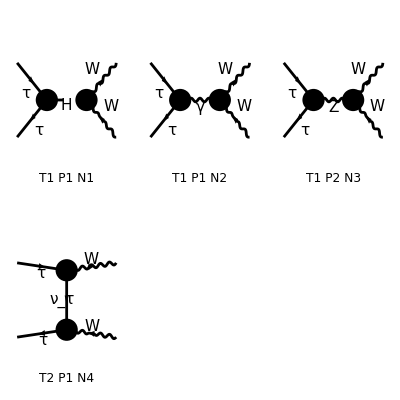

```mathematica
Process={F[2,{3}],-F[2,{3}]}-> {V[3],-V[3]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 1 Particles amplitude

in total: 4 Particles amplitudes

FeynAmpList(({F(2,{3}),-F(2,{3})}→{V(3),-V(3)})→(F(2,{3}) | p1 | ML | {-Charge,LeptonNumber}
-F(2,{3}) | p2 | ML | {Charge,-LeptonNumber})→(V(3) | k1 | MW | -Charge
-V(3) | k2 | MW | Charge),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],(ⅈ EL MW 1/((k1+k2)^2-MH2) g(Lor1,Lor2) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,ML).(-(ⅈ EL ML om_-)/(2 MW SW)-(ⅈ EL ML om_+)/(2 MW SW)).u(p1,ML))/SW),FeynAmp(GraphID(Topology==1,Generic==2,Particles==1,Number==2),Integral[],ⅈ EL 1/(k1+k2)^2 g(Lor3,Lor4) (g(Lor1,Lor2) (k1-k2)(Lor4)+g(Lor1,Lor4) (-2 (k1)-k2)(Lor2)+g(Lor2,Lor4) (k1+2 (k2))(Lor1)) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,ML).(ⅈ EL ga(Lor3).om_-+ⅈ EL ga(Lor3).om_+).u(p1,ML)),FeynAmp(GraphID(Topology==1,Generic==2,Particles==2,Number==3),Integral[],-1/SW ⅈ CW EL 1/((k1+k2)^2-MZ2) g(Lor3,Lor4) (g(Lor1,Lor2) (k1-k2)(Lor4)+g(Lor1,Lor4) (-2 (k1)-k2)(Lor2)+g(Lor2,Lor4) (k1+2 (k2))(Lor1)) Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,ML).((ⅈ EL (SW2-1/2) ga(Lor3).om_-)/(CW SW)+(ⅈ EL SW ga(Lor3).om_+)/CW).u(p1,ML)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==4),Integral[],1/(p2-k2)^2 Conjugate[ep](V(3),k1,Lor1) Conjugate[ep](V(3),k2,Lor2) v̄(p2,ML).(ⅈ EL ga(Lor2).om_-)/(√2 SW).gs(k2-p2).(ⅈ EL ga(Lor1).om_-)/(√2 SW).u(p1,ML)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 100 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

1/(4 MW2^2 SW2^2)Alfa2 π^2 (4 (Den(T,0))^2 ML2^4+32 MW2 (Den(T,0))^2 ML2^3-8 S (Den(T,0))^2 ML2^3-12 T (Den(T,0))^2 ML2^3-4 U (Den(T,0))^2 ML2^3+48 MW2 Den(S,MZ2) Den(T,0) ML2^3-8 S Den(S,MZ2) Den(T,0) ML2^3-48 MW2^2 (Den(S,MZ2))^2 ML2^2-4 S^2 (Den(S,MZ2))^2 ML2^2-128 MW2^2 SW2^2 (Den(S,MZ2))^2 ML2^2+32 S^2 SW2^2 (Den(S,MZ2))^2 ML2^2+128 MW2 S SW2^2 (Den(S,MZ2))^2 ML2^2+48 MW2 S (Den(S,MZ2))^2 ML2^2-192 MW2^2 SW2 (Den(S,MZ2))^2 ML2^2-16 S^2 SW2 (Den(S,MZ2))^2 ML2^2-64 MW2 S SW2 (Den(S,MZ2))^2 ML2^2+124 MW2^2 (Den(T,0))^2 ML2^2+12 T^2 (Den(T,0))^2 ML2^2-24 MW2 S (Den(T,0))^2 ML2^2-72 MW2 T (Den(T,0))^2 ML2^2+18 S T (Den(T,0))^2 ML2^2-24 MW2 U (Den(T,0))^2 ML2^2+2 S U (Den(T,0))^2 ML2^2+12 T U (Den(T,0))^2 ML2^2+272 MW2^2 Den(S,MZ2) Den(T,0) ML2^2-8 S^2 Den(S,MZ2) Den(T,0) ML2^2-24 MW2 S Den(S,MZ2) Den(T,0) ML2^2-416 MW2^2 SW2 Den(S,MZ2) Den(T,0) ML2^2+16 S^2 SW2 Den(S,MZ2) Den(T,0) ML2^2-16 MW2 S SW2 Den(S,MZ2) Den(T,0) ML2^2-88 MW2 T Den(S,MZ2) Den(T,0) ML2^2+12 S T Den(S,MZ2) Den(T,0) ML2^2+80 MW2 SW2 T Den(S,MZ2) Den(T,0) ML2^2-8 S SW2 T Den(S,MZ2) Den(T,0) ML2^2-8 MW2 U Den(S,MZ2) Den(T,0) ML2^2+4 S U Den(S,MZ2) Den(T,0) ML2^2-80 MW2 SW2 U Den(S,MZ2) Den(T,0) ML2^2+8 S SW2 U Den(S,MZ2) Den(T,0) ML2^2-2 (4 ML2-S) (12 MW2^2-4 S MW2+S^2) (Den(S,MH2))^2 ML2-256 MW2^3 (Den(S,MZ2))^2 ML2-6 S^3 (Den(S,MZ2))^2 ML2+24 MW2 S^2 (Den(S,MZ2))^2 ML2-2048 MW2^3 SW2^2 (Den(S,MZ2))^2 ML2-64 S^3 SW2^2 (Den(S,MZ2))^2 ML2+640 MW2 S^2 SW2^2 (Den(S,MZ2))^2 ML2-1536 MW2^2 S SW2^2 (Den(S,MZ2))^2 ML2-40 MW2^2 S (Den(S,MZ2))^2 ML2+1024 MW2^3 SW2 (Den(S,MZ2))^2 ML2+32 S^3 SW2 (Den(S,MZ2))^2 ML2-320 MW2 S^2 SW2 (Den(S,MZ2))^2 ML2+1024 MW2^2 S SW2 (Den(S,MZ2))^2 ML2+128 MW2^2 SW2^2 T (Den(S,MZ2))^2 ML2-32 S^2 SW2^2 T (Den(S,MZ2))^2 ML2-128 MW2 S SW2^2 T (Den(S,MZ2))^2 ML2-32 MW2 S T (Den(S,MZ2))^2 ML2+192 MW2^2 SW2 T (Den(S,MZ2))^2 ML2+16 S^2 SW2 T (Den(S,MZ2))^2 ML2+64 MW2 S SW2 T (Den(S,MZ2))^2 ML2+128 MW2^2 SW2^2 U (Den(S,MZ2))^2 ML2-32 S^2 SW2^2 U (Den(S,MZ2))^2 ML2-128 MW2 S SW2^2 U (Den(S,MZ2))^2 ML2-32 MW2 S U (Den(S,MZ2))^2 ML2+192 MW2^2 SW2 U (Den(S,MZ2))^2 ML2+16 S^2 SW2 U (Den(S,MZ2))^2 ML2+64 MW2 S SW2 U (Den(S,MZ2))^2 ML2+128 MW2^3 (Den(T,0))^2 ML2+S^3 (Den(T,0))^2 ML2-4 T^3 (Den(T,0))^2 ML2-8 MW2 S^2 (Den(T,0))^2 ML2+52 MW2 T^2 (Den(T,0))^2 ML2-12 S T^2 (Den(T,0))^2 ML2+4 MW2 U^2 (Den(T,0))^2 ML2-20 MW2^2 S (Den(T,0))^2 ML2-184 MW2^2 T (Den(T,0))^2 ML2-S^2 T (Den(T,0))^2 ML2+34 MW2 S T (Den(T,0))^2 ML2-56 MW2^2 U (Den(T,0))^2 ML2+S^2 U (Den(T,0))^2 ML2-12 T^2 U (Den(T,0))^2 ML2-2 MW2 S U (Den(T,0))^2 ML2+40 MW2 T U (Den(T,0))^2 ML2-4 S T U (Den(T,0))^2 ML2+112 MW2^3 Den(S,MZ2) Den(T,0) ML2+4 MW2 S^2 Den(S,MZ2) Den(T,0) ML2+60 MW2 T^2 Den(S,MZ2) Den(T,0) ML2-10 S T^2 Den(S,MZ2) Den(T,0) ML2-96 MW2 SW2 T^2 Den(S,MZ2) Den(T,0) ML2+16 S SW2 T^2 Den(S,MZ2) Den(T,0) ML2-20 MW2 U^2 Den(S,MZ2) Den(T,0) ML2-2 S U^2 Den(S,MZ2) Den(T,0) ML2+64 MW2 SW2 U^2 Den(S,MZ2) Den(T,0) ML2-96 MW2^2 S Den(S,MZ2) Den(T,0) ML2+4 S^3 SW2 Den(S,MZ2) Den(T,0) ML2-56 MW2 S^2 SW2 Den(S,MZ2) Den(T,0) ML2+288 MW2^2 S SW2 Den(S,MZ2) Den(T,0) ML2-184 MW2^2 T Den(S,MZ2) Den(T,0) ML2+6 S^2 T Den(S,MZ2) Den(T,0) ML2+352 MW2^2 SW2 T Den(S,MZ2) Den(T,0) ML2-12 S^2 SW2 T Den(S,MZ2) Den(T,0) ML2+72 MW2 S SW2 T Den(S,MZ2) Den(T,0) ML2-104 MW2^2 U Den(S,MZ2) Den(T,0) ML2+2 S^2 U Den(S,MZ2) Den(T,0) ML2+96 MW2^2 SW2 U Den(S,MZ2) Den(T,0) ML2-4 S^2 SW2 U Den(S,MZ2) Den(T,0) ML2-8 MW2 S SW2 U Den(S,MZ2) Den(T,0) ML2+8 MW2 T U Den(S,MZ2) Den(T,0) ML2+4 S T U Den(S,MZ2) Den(T,0) ML2+32 MW2 SW2 T U Den(S,MZ2) Den(T,0) ML2-16 S SW2 T U Den(S,MZ2) Den(T,0) ML2-2 Den(S,MH2) ((-4 (S-3 T+3 U) MW2^2+2 (2 S^2+(U-T) S+(T-U)^2) MW2+4 ML2 (S-2 MW2)^2+S ((T-U)^2-S^2)) Den(T,0)-2 (12 MW2^2-S^2) (4 SW2-1) (T-U) Den(S,MZ2)) ML2-32 SW2^2 (60 MW2^4+4 (S-8 (T+U)) MW2^3-(15 S^2+8 (T+U) S-4 (T^2-U T+U^2)) MW2^2+2 S (3 S^2+3 (T+U) S-T^2-U^2) MW2+ML2^2 (4 MW2^2-4 S MW2-S^2)-S^2 (S+T) (S+U)+ML2 (64 MW2^3+(48 S-4 (T+U)) MW2^2+4 S (-5 S+T+U) MW2+S^2 (2 S+T+U))) (Den(S,0))^2-304 MW2^4 (Den(S,MZ2))^2+4 S^4 (Den(S,MZ2))^2-24 MW2 S^3 (Den(S,MZ2))^2+76 MW2^2 S^2 (Den(S,MZ2))^2-1920 MW2^4 SW2^2 (Den(S,MZ2))^2+32 S^4 SW2^2 (Den(S,MZ2))^2-192 MW2 S^3 SW2^2 (Den(S,MZ2))^2+480 MW2^2 S^2 SW2^2 (Den(S,MZ2))^2-128 MW2^3 S SW2^2 (Den(S,MZ2))^2-128 MW2^2 SW2^2 T^2 (Den(S,MZ2))^2+64 MW2 S SW2^2 T^2 (Den(S,MZ2))^2+8 MW2 S T^2 (Den(S,MZ2))^2-32 MW2 S SW2 T^2 (Den(S,MZ2))^2-128 MW2^2 SW2^2 U^2 (Den(S,MZ2))^2+64 MW2 S SW2^2 U^2 (Den(S,MZ2))^2+8 MW2 S U^2 (Den(S,MZ2))^2-32 MW2 S SW2 U^2 (Den(S,MZ2))^2-16 MW2^3 S (Den(S,MZ2))^2+1216 MW2^4 SW2 (Den(S,MZ2))^2-16 S^4 SW2 (Den(S,MZ2))^2+96 MW2 S^3 SW2 (Den(S,MZ2))^2-304 MW2^2 S^2 SW2 (Den(S,MZ2))^2+64 MW2^3 S SW2 (Den(S,MZ2))^2+128 MW2^3 T (Den(S,MZ2))^2+4 S^3 T (Den(S,MZ2))^2-24 MW2 S^2 T (Den(S,MZ2))^2+1024 MW2^3 SW2^2 T (Den(S,MZ2))^2+32 S^3 SW2^2 T (Den(S,MZ2))^2-192 MW2 S^2 SW2^2 T (Den(S,MZ2))^2+256 MW2^2 S SW2^2 T (Den(S,MZ2))^2+64 MW2^2 S T (Den(S,MZ2))^2-512 MW2^3 SW2 T (Den(S,MZ2))^2-16 S^3 SW2 T (Den(S,MZ2))^2+96 MW2 S^2 SW2 T (Den(S,MZ2))^2-256 MW2^2 S SW2 T (Den(S,MZ2))^2+128 MW2^3 U (Den(S,MZ2))^2+4 S^3 U (Den(S,MZ2))^2-24 MW2 S^2 U (Den(S,MZ2))^2+1024 MW2^3 SW2^2 U (Den(S,MZ2))^2+32 S^3 SW2^2 U (Den(S,MZ2))^2-192 MW2 S^2 SW2^2 U (Den(S,MZ2))^2+256 MW2^2 S SW2^2 U (Den(S,MZ2))^2+64 MW2^2 S U (Den(S,MZ2))^2-512 MW2^3 SW2 U (Den(S,MZ2))^2-16 S^3 SW2 U (Den(S,MZ2))^2+96 MW2 S^2 SW2 U (Den(S,MZ2))^2-256 MW2^2 S SW2 U (Den(S,MZ2))^2+48 MW2^2 T U (Den(S,MZ2))^2+4 S^2 T U (Den(S,MZ2))^2+128 MW2^2 SW2^2 T U (Den(S,MZ2))^2+32 S^2 SW2^2 T U (Den(S,MZ2))^2-192 MW2^2 SW2 T U (Den(S,MZ2))^2-16 S^2 SW2 T U (Den(S,MZ2))^2+16 MW2^4 (Den(T,0))^2+4 MW2 S^3 (Den(T,0))^2-12 MW2 T^3 (Den(T,0))^2+2 S T^3 (Den(T,0))^2-20 MW2^2 S^2 (Den(T,0))^2+48 MW2^2 T^2 (Den(T,0))^2+S^2 T^2 (Den(T,0))^2-6 MW2 S T^2 (Den(T,0))^2+4 MW2^2 U^2 (Den(T,0))^2+4 MW2 S U^2 (Den(T,0))^2-4 MW2 T U^2 (Den(T,0))^2+8 MW2^3 S (Den(T,0))^2-72 MW2^3 T (Den(T,0))^2-S^3 T (Den(T,0))^2+28 MW2^2 S T (Den(T,0))^2-24 MW2^3 U (Den(T,0))^2+4 T^3 U (Den(T,0))^2+8 MW2 S^2 U (Den(T,0))^2-16 MW2 T^2 U (Den(T,0))^2+2 S T^2 U (Den(T,0))^2-16 MW2^2 S U (Den(T,0))^2+56 MW2^2 T U (Den(T,0))^2-S^2 T U (Den(T,0))^2-6 MW2 S T U (Den(T,0))^2-208 MW2^4 Den(S,MZ2) Den(T,0)+2 S^4 Den(S,MZ2) Den(T,0)-10 MW2 S^3 Den(S,MZ2) Den(T,0)-16 MW2 T^3 Den(S,MZ2) Den(T,0)+4 S T^3 Den(S,MZ2) Den(T,0)+32 MW2 SW2 T^3 Den(S,MZ2) Den(T,0)-8 S SW2 T^3 Den(S,MZ2) Den(T,0)+8 MW2 U^3 Den(S,MZ2) Den(T,0)-16 MW2 SW2 U^3 Den(S,MZ2) Den(T,0)+36 MW2^2 S^2 Den(S,MZ2) Den(T,0)+24 MW2^2 T^2 Den(S,MZ2) Den(T,0)+2 S^2 T^2 Den(S,MZ2) Den(T,0)-4 MW2 S T^2 Den(S,MZ2) Den(T,0)-48 MW2^2 SW2 T^2 Den(S,MZ2) Den(T,0)-4 S^2 SW2 T^2 Den(S,MZ2) Den(T,0)+8 MW2 S SW2 T^2 Den(S,MZ2) Den(T,0)-24 MW2^2 U^2 Den(S,MZ2) Den(T,0)+8 MW2 S U^2 Den(S,MZ2) Den(T,0)+48 MW2^2 SW2 U^2 Den(S,MZ2) Den(T,0)-16 MW2 S SW2 U^2 Den(S,MZ2) Den(T,0)+8 MW2 T U^2 Den(S,MZ2) Den(T,0)-16 MW2 SW2 T U^2 Den(S,MZ2) Den(T,0)-24 MW2^3 S Den(S,MZ2) Den(T,0)+416 MW2^4 SW2 Den(S,MZ2) Den(T,0)-4 S^4 SW2 Den(S,MZ2) Den(T,0)+20 MW2 S^3 SW2 Den(S,MZ2) Den(T,0)-72 MW2^2 S^2 SW2 Den(S,MZ2) Den(T,0)+48 MW2^3 S SW2 Den(S,MZ2) Den(T,0)+88 MW2^3 T Den(S,MZ2) Den(T,0)-14 MW2 S^2 T Den(S,MZ2) Den(T,0)+48 MW2^2 S T Den(S,MZ2) Den(T,0)-176 MW2^3 SW2 T Den(S,MZ2) Den(T,0)+28 MW2 S^2 SW2 T Den(S,MZ2) Den(T,0)-96 MW2^2 S SW2 T Den(S,MZ2) Den(T,0)+104 MW2^3 U Den(S,MZ2) Den(T,0)+2 S^3 U Den(S,MZ2) Den(T,0)-6 MW2 S^2 U Den(S,MZ2) Den(T,0)-4 S T^2 U Den(S,MZ2) Den(T,0)+8 S SW2 T^2 U Den(S,MZ2) Den(T,0)+16 MW2^2 S U Den(S,MZ2) Den(T,0)-208 MW2^3 SW2 U Den(S,MZ2) Den(T,0)-4 S^3 SW2 U Den(S,MZ2) Den(T,0)+12 MW2 S^2 SW2 U Den(S,MZ2) Den(T,0)-32 MW2^2 S SW2 U Den(S,MZ2) Den(T,0)+16 MW2^2 T U Den(S,MZ2) Den(T,0)-2 S^2 T U Den(S,MZ2) Den(T,0)+20 MW2 S T U Den(S,MZ2) Den(T,0)-32 MW2^2 SW2 T U Den(S,MZ2) Den(T,0)+4 S^2 SW2 T U Den(S,MZ2) Den(T,0)-40 MW2 S SW2 T U Den(S,MZ2) Den(T,0)+4 SW2 Den(S,0) (-4 ML2 (12 MW2^2-S^2) (T-U) Den(S,MH2)+4 (4 (60 SW2-19) MW2^4+4 (4 SW2-1) (S-8 (T+U)) MW2^3+((19-60 SW2) S^2-16 (2 SW2-1) (T+U) S+12 T U+16 SW2 (T^2-U T+U^2)) MW2^2+2 S (4 SW2-1) (3 S^2+3 (T+U) S-T^2-U^2) MW2+ML2^2 (4 (4 SW2+3) MW2^2+4 S (1-4 SW2) MW2+S^2 (1-4 SW2))-S^2 (4 SW2-1) (S+T) (S+U)+ML2 (64 (4 SW2-1) MW2^3+4 (16 S (3 SW2-1)-(4 SW2+3) (T+U)) MW2^2-4 S (4 SW2-1) (5 S-T-U) MW2+S^2 (4 SW2-1) (2 S+T+U))) Den(S,MZ2)+(-104 MW2^4+(-12 S+44 T+52 U) MW2^3+2 (9 S^2+4 (3 T+U) S+6 T^2-6 U^2+4 T U) MW2^2+(-5 S^3-(7 T+3 U) S^2-2 (T^2-5 U T-2 U^2) S+4 (-2 T^3+U^2 T+U^3)) MW2+S (S+T) (S^2+(U-T) S+2 T (T-U))+2 ML2^2 (52 MW2^2+2 (S-5 T+5 U) MW2+S (-2 S+T-U))-ML2 (8 (9 S+11 T+3 U) MW2^2-2 (7 S^2+(U-9 T) S+12 T^2-8 U^2-4 T U) MW2+S (S^2-(3 T+U) S+4 T (T-U)))) Den(T,0)))

```mathematica
resFCtataWW=square1/.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),ML2->MTA^2}//FullSimplify[#,S+T+U==2 MTA^2+2MW2]&
```

1/(64 MW2^2 sw^4)ee^4 ((4 MTA^8)/T^2+(4 (4 MW2 (2 MZ2-2 S-3 T)-MZ2 (2 S+3 T+U)+S (2 S+5 T+U)) MTA^6)/((MZ2-S) T^2)+2 (2 (-(8 (-13 MZ2+13 S+(4 sw^2+6) T) sw^2)/((MZ2-S)^2 T)+8/(MH2 T-S T)-68/(MZ2 T-S T)-24/(MH2-S)^2-12/(MZ2-S)^2+31/T^2) MW2^2+4 (-(2 S^2 sw^2)/((MZ2-S)^2 T)+S ((2 T (MZ2+(8 sw^2-4) T) sw^2+3 (MZ2-S) U)/((MZ2-S)^2 T^2)-4/(MH2 T-S T)+12/(MZ2 T-S T)+4/(MH2-S)^2+6/(MZ2-S)^2-3/T^2)+(T (10 U sw^2+(11-10 sw^2) T+U)-3 MZ2 (3 T+U))/((MZ2-S) T^2)) MW2+S^2 (-(8 (-2 T sw^2+MZ2-S+T) sw^2)/((MZ2-S)^2 T)+4/(MH2 T-S T)+4/(MZ2 T-S T)-4/(MH2-S)^2-2/(MZ2-S)^2)+(6 (T+U))/T+(S (T ((4 sw^2-6) T-9 S)-(S+(4 sw^2+2) T) U+MZ2 (9 T+U)))/((MZ2-S) T^2)) MTA^4+(-(64 S^3 sw^4)/(MZ2-S)^2-(32 S^2 T sw^4)/(MZ2-S)^2-(32 S^2 U sw^4)/(MZ2-S)^2+(32 S^3 sw^2)/(MZ2-S)^2+(12 S^2 sw^2)/(MZ2-S)+(16 S^2 T sw^2)/(MZ2-S)^2-(16 S T sw^2)/(MH2-S)+(16 S^2 T sw^2)/((MH2-S) (S-MZ2))+(16 S T sw^2)/(S-MZ2)+(16 S^2 U sw^2)/((MH2-S) (MZ2-S))+(16 S^2 U sw^2)/(MZ2-S)^2+(16 S U sw^2)/(MH2-S)+(16 S U sw^2)/(MZ2-S)+(4 S^2 U sw^2)/(MZ2 T-S T)-(4 S^3 sw^2)/(MZ2 T-S T)+(2 S^3)/(MH2-S)^2-(6 S^3)/(MZ2-S)^2+(2 S U^2)/(MH2 T-S T)+(2 S U^2)/(MZ2 T-S T)-12 S+(4 S^2 T)/((MH2-S) (MZ2-S))+(2 S T)/(MH2-S)+(10 S T)/(MZ2-S)-4 T+(16 MW2^3 (8 (MZ2-S)^2-16 (8 sw^4-4 sw^2+1) T^2+7 (S-MZ2) T))/((MZ2-S)^2 T^2)+(4 S U)/(S-MH2)+(4 S^2 U)/((MH2-S) (S-MZ2))+(4 S U)/(S-MZ2)-(4 S U)/T-(2 S^2 U)/(MZ2 T-S T)+(S^2 U)/T^2-12 U+4 MW2^2 ((48 (U-T) sw^2)/(S (S-MH2))+S (-(8 (9 MZ2-9 S+(48 sw^2-32) T) sw^2)/((MZ2-S)^2 T)-2/(MH2 T-S T)+24/(MZ2 T-S T)+6/(MH2-S)^2-10/(MZ2-S)^2-5/T^2)+2 ((16 (T+U) sw^4)/(MZ2-S)^2+(4 (11 T S^2+3 U S^2+12 T^2 S-11 (MH2+MZ2) T S-3 (MH2+MZ2) U S-6 (MH2+MZ2) T^2+11 MH2 MZ2 T+3 MH2 MZ2 U+6 (MZ2-MH2) T U) sw^2)/((MZ2-S)^2 (S-MH2) T)+(6 T)/((MH2-S) (S-MZ2))+(6 U)/((MH2-S) (MZ2-S))-(3 U)/(MH2 T-S T)+(13 U)/(MZ2 T-S T)-(7 U)/T^2+3/(MH2-S)+23/(MZ2-S)-23/T))+MW2 (((8 (7 MZ2-7 S+(80 sw^2-40) T) sw^2)/((MZ2-S)^2 T)+8/(MH2 T-S T)-4/(MZ2 T-S T)-8/(MH2-S)^2+24/(MZ2-S)^2-8/T^2) S^2+(-(128 (T+U) sw^4)/(MZ2-S)^2+(8 (S (9 T-U)+MZ2 (U-9 T)+8 T (T+U)) sw^2)/((MZ2-S)^2 T)-(32 T)/(MZ2-S)^2+(4 U)/(MH2 T-S T)-(32 U)/(MZ2-S)^2-(2 U)/T^2+4/(S-MH2)+34/T) S+(8 U)/(S-MH2)+(4 (-((24 (MH2-S) sw^2-15 MH2+MZ2+14 S) T^3)+2 (MH2-S) (4 T sw^2-5 MZ2+5 S+T) U T+((MH2-S) (S-MZ2)+(16 (MH2-S) sw^2-5 MH2-MZ2+6 S) T) U^2))/((MH2-S) (S-MZ2) T^2)+52)+(6 S^2)/(S-MZ2)-S^2/T+(2 S^3)/((S-MH2) T)+S^3/T^2) MTA^2+1/((MZ2-S)^2 S^2 T^2)(16 S^2 ((MZ2-S)^2-13 (2 sw^2-1) T (MZ2-S)+(-120 sw^4+76 sw^2-19) T^2) MW2^4+S (8 (S^2-((20 sw^2+9) T+3 U) S+4 sw^2 T (20 T sw^2+T-U)) MZ2^2-8 S (2 S^2-((34 sw^2+21) T+6 U) S+T ((26 sw^2+11) T+(13-34 sw^2) U)) MZ2+8 S (S^3-(2 (7 sw^2+6) T+3 U) S^2+T ((-96 sw^4+30 sw^2+9) T+(13-30 sw^2) U) S+16 (8 sw^4-4 sw^2+1) T^2 (T+U))) MW2^3+(-4 (5 S^4+((14 sw^2-7) T+4 U) S^3+(4 (66 sw^4-8 sw^2-3) T^2+2 (8 sw^2-7) U T-U^2) S^2+2 sw^2 T ((64 sw^2+5) T^2+(64 sw^2-6) U T+U^2) S+24 sw^4 T^2 (T-U)^2) MZ2^2+4 S (10 S^4+((46 sw^2-23) T+8 U) S^3+((92 sw^2-36) T^2+8 (5 sw^2-4) U T-2 U^2) S^2+T ((96 sw^2-6) T^2+(48 sw^2-4) U T+(6-8 sw^2) U^2) S+12 sw^2 T^2 (T-U)^2) MZ2+S^2 (-20 S^4-16 ((8 sw^2-4) T+U) S^3+(4 (384 sw^4-200 sw^2+43) T^2+(72-96 sw^2) U T+4 U^2) S^2+8 T ((96 sw^4-75 sw^2+11) T^2+(96 sw^4-62 sw^2+10) U T+(5 sw^2-3) U^2) S-16 T^2 (2 (T+U)^2 sw^4+3 (T+U)^2 sw^2-3 T U))) MW2^2+S (2 (2 S^4+4 (4 T sw^2+U) S^3+((96 sw^4-26 sw^2-3) T^2+(34 sw^2-3) U T+2 U^2) S^2+T ((64 sw^4-12 sw^2-6) T^2+(64 sw^4-8 sw^2-8) U T+(20 sw^2-2) U^2) S+2 sw^2 T (T-U)^2 ((8 sw^2-1) T+U)) MZ2^2-2 S (4 S^4+((42 sw^2-5) T+8 U) S^3+((10 sw^2-13) T^2+(74 sw^2-9) U T+4 U^2) S^2+T (2 (6 sw^2-7) T^2+(-4 sw^2-6) U T+32 sw^2 U^2) S+4 T (T-U) ((5 sw^2-2) T^2+(4 sw^2-2) U T+(sw^2-1) U^2)) MZ2+S^2 (4 S^4+2 ((26 sw^2-5) T+4 U) S^3+(-4 (96 sw^4-42 sw^2+11) T^2+(80 sw^2-12) U T+4 U^2) S^2+T (-8 (40 sw^4-18 sw^2+5) T^2-4 (80 sw^4-26 sw^2+5) U T+(24 sw^2+4) U^2) S+4 T (T+U) (2 T U (1-2 sw^2)^2+(8 sw^4+3 sw^2-2) T^2+(2-3 sw^2) U^2))) MW2+S^2 T (-((8 T (T-U)^2 sw^4-2 (T-U)^3 sw^2+S^3 (2 sw^2+1)-4 T^2 U+S^2 (6 U sw^2+(-8 sw^4+2 sw^2-1) T+U)-2 S ((sw^2+1) T^2+(2 sw^2+1) U T-3 sw^2 U^2)) MZ2^2)+2 S (S+T+U) (4 S^2 sw^2+2 U^2 sw^2-6 T U sw^2+(4 sw^2-2) T^2-S (4 T sw^2-4 U sw^2+T)) MZ2-S^2 (S+T+U) ((6 sw^2-1) S^2+(-24 sw^4+8 sw^2-4) T S+4 sw^2 U S+(-8 sw^4+10 sw^2-4) T^2+2 sw^2 U^2-4 (2 sw^4+sw^2) T U))))

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARtataWW=Get["resANATARtataWW.m"];
```

```mathematica
FullSimplify[resANATARtataWW- 4 resFCtataWW,{S+T+U==2MW2+2 MTA^2,cw^2+sw^2==1}]
```

0

## τ τ -> ZZ

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AtataZZ=GenerateAmplitude[{ta,tabar}->{Z,Z},OutputName->"tataZZ",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tataZZ.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tataZZ/tataZZ_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {ta, tabar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{ta(p1),tabar(p2)}→{Z(p3),Z(p4)}},Total→3,Name→tataZZ,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2+MZ^2-T),p2.p3→1/2 (MTA^2+MZ^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2+MZ^2-T),1/(p2.p3)→2/(MTA^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC53 GC70 𝕀_Spin3Spin1 Den(-p1-p2,MH) ε_Lor4(p3,MZ) ε_Lor4(p4,MZ) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA),DiagramID(2)→-1/4 ⅈ Den(p1-p3,MTA) ε_Lor2(p3,MZ) ε_Lor4(p4,MZ) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) ((GC35-GC15) (γ^Lor4 γ^5)_(iSpin1 Spin3)+(GC15+GC35) (γ^Lor4)_(iSpin1 Spin3)) ((GC35-GC15) (γ^Lor2 γ^5)_(iSpin2 Spin1)+(GC15+GC35) (γ^Lor2)_(iSpin2 Spin1)) (MTA 𝕀_iSpin1iSpin2+(γ·(p1-p3))_(iSpin1 iSpin2)),DiagramID(3)→-1/4 ⅈ Den(p1-p4,MTA) ε_Lor2(p3,MZ) ε_Lor4(p4,MZ) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) ((GC35-GC15) (γ^Lor2 γ^5)_(iSpin1 Spin3)+(GC15+GC35) (γ^Lor2)_(iSpin1 Spin3)) ((GC35-GC15) (γ^Lor4 γ^5)_(iSpin2 Spin1)+(GC15+GC35) (γ^Lor4)_(iSpin2 Spin1)) (MTA 𝕀_iSpin1iSpin2+(γ·(p1-p4))_(iSpin1 iSpin2))}|>

```mathematica
AtataZZC=GenerateAmplitudeConjugate[{ta,tabar}->{Z,Z},OutputName->"tataZZ",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tataZZ.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tataZZ/tataZZ_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {ta, tabar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{ta(p1),tabar(p2)}→{Z(p3),Z(p4)}},Total→3,Name→tataZZ,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2+MZ^2-T),p2.p3→1/2 (MTA^2+MZ^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2+MZ^2-T),1/(p2.p3)→2/(MTA^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC53 GC70 𝕀_SpinC1SpinC3 Den(-p1-p2,MH) (ε^†)_LorC4^(p3,MZ) (ε^†)_LorC4^(p4,MZ) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA),DiagramID(2)→1/4 ⅈ Den(p1-p3,MTA) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC4^(p4,MZ) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) ((GC15-GC35) (γ^5 γ^LorC4)_(iSpinC1 SpinC3)+(GC15+GC35) (γ^LorC4)_(iSpinC1 SpinC3)) ((GC15-GC35) (γ^5 γ^LorC2)_(iSpinC2 SpinC1)+(GC15+GC35) (γ^LorC2)_(iSpinC2 SpinC1)) (MTA 𝕀_iSpinC2iSpinC1+(γ·p1)_(iSpinC1 iSpinC2)-(γ·p3)_(iSpinC1 iSpinC2)),DiagramID(3)→1/4 ⅈ Den(p1-p4,MTA) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC4^(p4,MZ) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) ((GC15-GC35) (γ^5 γ^LorC2)_(iSpinC1 SpinC3)+(GC15+GC35) (γ^LorC2)_(iSpinC1 SpinC3)) ((GC15-GC35) (γ^5 γ^LorC4)_(iSpinC2 SpinC1)+(GC15+GC35) (γ^LorC4)_(iSpinC2 SpinC1)) (MTA 𝕀_iSpinC2iSpinC1+(γ·p1)_(iSpinC1 iSpinC2)-(γ·p4)_(iSpinC1 iSpinC2))}|>

```mathematica
AmpSQtataZZ=GenerateAmplitudeSquare[AtataZZ,AtataZZC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{ta(p1),tabar(p2)}→{Z(p3),Z(p4)}},Name→tataZZ,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2+MZ^2-T),p2.p3→1/2 (MTA^2+MZ^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2+MZ^2-T),1/(p2.p3)→2/(MTA^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→1/(16 cw^4 MZ^4 sw2^2)ee^4 (-2 MTA^2 (4 MTA^2-S) (4 MTA^4-4 (T+U) MTA^2+8 MZ^4+(T+U)^2) (Den(-p1-p2,MH))^2 (cw^2+sw2)^4-2 MTA^2 Den(-p1-p2,MH) (((8 MTA^6-2 (S+5 T+3 U) MTA^4+(-8 (T-U) MZ^2+5 T^2+U^2+3 S T+S U+2 T U) MTA^2-T (S+T-U) (T+U)+2 MZ^2 (T-U) (S+3 T+U)) cw^4+2 sw2 (8 MTA^6-2 (S+3 T+5 U) MTA^4+(32 MZ^4+8 (T-U) MZ^2-T^2+3 U^2+3 S T+S U+6 T U) MTA^2-8 MZ^4 S-T (S-T+U) (T+U)-2 MZ^2 (T-U) (S+3 T+U)) cw^2+sw2^2 (8 MTA^6-2 (S+9 T-U) MTA^4+(-64 MZ^4-40 (T-U) MZ^2+17 T^2-3 U^2+3 S T+S U-6 T U) MTA^2+16 MZ^4 S-T (S+5 T-5 U) (T+U)+10 MZ^2 (T-U) (S+3 T+U))) Den(p1-p3,MTA)+((8 MTA^6-2 (S+5 T+3 U) MTA^4+(-4 (T-U) MZ^2+5 T^2+U^2+3 S T+S U+2 T U) MTA^2-8 MZ^4 (T-U)+2 MZ^2 (S+2 T) (T-U)-T (S+T-U) (T+U)) cw^4+2 sw2 (8 MTA^6-2 (S+3 T+5 U) MTA^4+(32 MZ^4+4 (T-U) MZ^2-T^2+3 U^2-S T+5 S U+6 T U) MTA^2-2 MZ^2 (S+2 T) (T-U)-8 MZ^4 (S-T+U)+(T+U) (T^2+S T-U T-2 S U)) cw^2+sw2^2 (8 MTA^6-2 (S+9 T-U) MTA^4-(64 MZ^4+20 (T-U) MZ^2-17 T^2+3 U^2-11 S T+7 S U+6 T U) MTA^2+10 MZ^2 (S+2 T) (T-U)+8 MZ^4 (2 S-5 T+5 U)-(T+U) (5 T^2+5 S T-5 U T-4 S U))) Den(p3-p2,MTA)) (cw^2+sw2)^2+((3 MTA^8+(4 MZ^2-4 S-6 T-4 U) MTA^6+(-5 MZ^4-(5 S+T+5 U) MZ^2+S^2+4 T^2+U^2+8 S T+2 S U+7 T U) MTA^4+(-2 MZ^6+(7 S+3 T+7 U) MZ^4+(S^2+2 U S+(T-U)^2) MZ^2-T (2 S^2+5 T S+3 U S+T^2+U^2+4 T U)) MTA^2+T^2 (S+T) (S+U)+2 MZ^6 (S+T+U)-MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)+MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^8-4 sw2 (3 MTA^8-2 (MZ^2+2 S+3 T+2 U) MTA^6+(-5 MZ^4+(7 S-T+7 U) MZ^2+S^2+4 T^2+U^2+8 S T+2 S U+7 T U) MTA^4-(8 MZ^6-2 (5 S+6 T+5 U) MZ^4+2 (S^2+3 T S+2 U S-2 T^2+U^2+4 T U) MZ^2+T (2 S^2+5 T S+3 U S+T^2+U^2+4 T U)) MTA^2+T^2 (S+T) (S+U)+2 MZ^6 (S+T+U)-MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)+MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^6+2 sw2^2 (MTA^8-2 (16 MZ^2+2 S+3 T) MTA^6+(-87 MZ^4+(57 S+5 T+65 U) MZ^2+3 S^2+8 T^2-U^2+5 T U+2 S (6 T+U)) MTA^4-(34 MZ^6+(-35 S+13 T-35 U) MZ^4+(11 S^2+6 (6 T+5 U) S-17 T^2+19 U^2+42 T U) MZ^2+T (6 S^2+11 T S+5 U S+3 T^2-U^2+8 T U)) MTA^2+3 (2 (S+T+U) MZ^6-(2 S^2+4 (T+U) S+T^2+2 U^2+4 T U) MZ^4+T (-T^2+U T+2 U^2+S (T+2 U)) MZ^2+T^2 (S+T) (S+U))) cw^4+4 sw2^3 (5 MTA^8+(46 MZ^2-4 S-6 T-8 U) MTA^6+(77 MZ^4-(79 S+7 T+87 U) MZ^2-S^2+2 S (2 T+U)+3 U (3 T+U)) MTA^4+(36 MZ^6-2 (12 S-5 T+12 U) MZ^4+2 (8 S^2+21 T S+20 U S-9 T^2+12 U^2+22 T U) MZ^2+T (2 S^2+(T-U) S+T^2-3 U^2)) MTA^2-T^2 (S+T) (S+U)-2 MZ^6 (S+T+U)+MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)-MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^2+sw2^4 (35 MTA^8-2 (34 MZ^2+26 S+39 T+22 U) MTA^6+(-229 MZ^4+(155 S-T+171 U) MZ^2+17 S^2+60 T^2+9 U^2+112 S T+26 S U+87 T U) MTA^4-(138 MZ^6-(171 S+79 T+171 U) MZ^4+(35 S^2+120 T S+86 U S-69 T^2+51 U^2+154 T U) MZ^2+T (34 S^2+77 T S+43 U S+17 T^2+9 U^2+60 T U)) MTA^2+17 (2 (S+T+U) MZ^6-(2 S^2+4 (T+U) S+T^2+2 U^2+4 T U) MZ^4+T (-T^2+U T+2 U^2+S (T+2 U)) MZ^2+T^2 (S+T) (S+U)))) (Den(p1-p3,MTA))^2+((3 MTA^8-2 (2 S+3 T+2 U) MTA^6+(-5 MZ^4+(S-5 T+3 U) MZ^2+S^2+4 T^2+U^2+7 T U+5 S (T+U)) MTA^4+(6 MZ^6+(3 S-T-U) MZ^4+(-3 S^2+2 T S+5 T^2-3 U^2+2 T U) MZ^2-(S+T) (T^2+4 U T+U^2+S (T+U))) MTA^2+4 MZ^8+T (S+T)^2 U-2 MZ^6 (3 S+3 T+U)+MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (-S^2+2 (T+2 U) S+3 T^2-2 U^2+4 T U)) cw^8-4 sw2 (3 MTA^8+(6 MZ^2-4 S-6 T-4 U) MTA^6+(19 MZ^4-(5 S+11 T+3 U) MZ^2+S^2+4 T^2+U^2+7 T U+5 S (T+U)) MTA^4+(12 MZ^6-2 (6 S+8 T-U) MZ^4+2 T (4 S+4 T+U) MZ^2-(S+T) (T^2+4 U T+U^2+S (T+U))) MTA^2+4 MZ^8+T (S+T)^2 U-2 MZ^6 (3 S+3 T+U)+MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (-S^2+2 (T+2 U) S+3 T^2-2 U^2+4 T U)) cw^6+2 sw2^2 (MTA^8+(28 MZ^2-4 S-6 T) MTA^6-(87 MZ^4+(33 S+43 T+19 U) MZ^2-3 S^2-8 T^2+U^2-11 S T-3 S U-5 T U) MTA^4+(-82 MZ^6+(-13 S-25 T+11 U) MZ^4+(13 S^2+42 T S+29 T^2+5 U^2+6 T U) MZ^2-(S+T) (3 T^2+8 U T-U^2+3 S (T+U))) MTA^2+3 (4 MZ^8-2 (3 S+3 T+U) MZ^6+(-S^2+2 T S+4 U S+3 T^2-2 U^2+4 T U) MZ^4+(S+T) (S^2-U S-T^2+2 U^2-3 T U) MZ^2+T (S+T)^2 U)) cw^4+4 sw2^3 (5 MTA^8-2 (17 MZ^2+2 S+3 T+4 U) MTA^6+(53 MZ^4+(41 S+39 T+31 U) MZ^2-S^2+3 U^2-S T+7 S U+9 T U) MTA^4+(88 MZ^6+2 (17 S+19 T-8 U) MZ^4-2 (11 S^2+22 T S+11 T^2+7 U^2+T U) MZ^2+(S+T) (T^2-3 U^2+S (T+U))) MTA^2-4 MZ^8-T (S+T)^2 U+2 MZ^6 (3 S+3 T+U)-MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (S^2-2 (T+2 U) S-3 T^2+2 U^2-4 T U)) cw^2+sw2^4 (35 MTA^8+2 (52 MZ^2-26 S-39 T-22 U) MTA^6+(-37 MZ^4-(103 S+189 T+53 U) MZ^2+17 S^2+60 T^2+9 U^2+77 S T+61 S U+87 T U) MTA^4-(50 MZ^6+(113 S+181 T-35 U) MZ^4-(17 S^2+154 T S+137 T^2+U^2+34 T U) MZ^2+(S+T) (17 T^2+60 U T+9 U^2+17 S (T+U))) MTA^2+17 (4 MZ^8-2 (3 S+3 T+U) MZ^6+(-S^2+2 T S+4 U S+3 T^2-2 U^2+4 T U) MZ^4+(S+T) (S^2-U S-T^2+2 U^2-3 T U) MZ^2+T (S+T)^2 U))) (Den(p3-p2,MTA))^2-2 ((3 MTA^8-(4 MZ^2+S+3 T+U) MTA^6+(-25 MZ^4+(-3 S+7 T+5 U) MZ^2+T (S+T-3 U)) MTA^4+(-2 MZ^6+(23 S+13 T+7 U) MZ^4+(S^2-5 T^2-U^2-6 T U) MZ^2+T U (S+3 T+U)) MTA^2+2 MZ^6 T-T^2 (S+T) U+MZ^2 T (S+T) (-S+T+3 U)-MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^8+4 sw2 (5 MTA^8+(4 MZ^2-S-7 T-5 U) MTA^6+(13 MZ^4-2 (5 T+U) MZ^2+4 T^2+U^2+2 S T+S U+5 T U) MTA^4+(2 MZ^6-(17 S+14 T+6 U) MZ^4+(-S^2+2 T S+U S+7 T^2+5 T U) MZ^2-T (T^2+S T+3 U T+2 S U)) MTA^2-2 MZ^6 T+MZ^2 T (S+T) (S-T-3 U)+T^2 (S+T) U+MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^6+2 sw2^2 (9 MTA^8+(-12 MZ^2+S-5 T-7 U) MTA^6-(19 MZ^4+(-25 S-39 T+3 U) MZ^2+3 T^2-2 U^2+3 S T+2 S U+5 T U) MTA^4+(-6 MZ^6+(17 S+65 T+19 U) MZ^4+(3 S^2-24 T S-10 U S-31 T^2-U^2-4 T U) MZ^2+T (2 T^2+2 S T+9 U T+U^2+5 S U)) MTA^2+6 MZ^6 T-3 T^2 (S+T) U+3 MZ^2 T (S+T) (-S+T+3 U)-3 MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^4+4 sw2^3 (5 MTA^8+(4 MZ^2-5 S-11 T-U) MTA^6+(-43 MZ^4-2 (17 S+14 T-8 U) MZ^2+10 T^2-U^2+8 S T+3 S U+T U) MTA^4+(2 MZ^6+(35 S-40 T-4 U) MZ^4-(S^2-26 T S-11 U S-23 T^2+2 U^2+9 T U) MZ^2-T (3 T^2+3 S T+3 U T-2 U^2+4 S U)) MTA^2-2 MZ^6 T+MZ^2 T (S+T) (S-T-3 U)+T^2 (S+T) U+MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^2-sw2^4 (13 MTA^8+(68 MZ^2-7 S-37 T-23 U) MTA^6+(217 MZ^4-(41 S+179 T+25 U) MZ^2+35 T^2+4 U^2+19 S T+12 S U+59 T U) MTA^4+(34 MZ^6-(239 S+281 T+107 U) MZ^4+(-17 S^2+64 T S+28 U S+133 T^2+5 U^2+66 T U) MZ^2-T (12 T^2+12 S T+51 U T+5 U^2+29 S U)) MTA^2-17 (2 T MZ^6-(4 S^2+3 T S+4 U S+3 T^2+2 T U) MZ^4+T (S+T) (-S+T+3 U) MZ^2-T^2 (S+T) U))) Den(p1-p3,MTA) Den(p3-p2,MTA))|>

```mathematica
resANATARtataZZ=AmpSQtataZZ[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(p1-p3)->√T,(p3-p2)->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/(16 cw^4 MZ^4 sw^4)ee^4 (-(2 MTA^2 (4 MTA^2-S) (4 MTA^4-4 (T+U) MTA^2+8 MZ^4+(T+U)^2) (cw^2+sw^2)^4)/((S-MH^2)^2)-1/(S-MH^2)2 MTA^2 (1/(T-MTA^2)((8 MTA^6-2 (S+5 T+3 U) MTA^4+(-8 (T-U) MZ^2+5 T^2+U^2+3 S T+S U+2 T U) MTA^2-T (S+T-U) (T+U)+2 MZ^2 (T-U) (S+3 T+U)) cw^4+2 sw^2 (8 MTA^6-2 (S+3 T+5 U) MTA^4+(32 MZ^4+8 (T-U) MZ^2-T^2+3 U^2+3 S T+S U+6 T U) MTA^2-8 MZ^4 S-T (S-T+U) (T+U)-2 MZ^2 (T-U) (S+3 T+U)) cw^2+sw^4 (8 MTA^6-2 (S+9 T-U) MTA^4+(-64 MZ^4-40 (T-U) MZ^2+17 T^2-3 U^2+3 S T+S U-6 T U) MTA^2+16 MZ^4 S-T (S+5 T-5 U) (T+U)+10 MZ^2 (T-U) (S+3 T+U)))+1/(U-MTA^2)((8 MTA^6-2 (S+5 T+3 U) MTA^4+(-4 (T-U) MZ^2+5 T^2+U^2+3 S T+S U+2 T U) MTA^2-8 MZ^4 (T-U)+2 MZ^2 (S+2 T) (T-U)-T (S+T-U) (T+U)) cw^4+2 sw^2 (8 MTA^6-2 (S+3 T+5 U) MTA^4+(32 MZ^4+4 (T-U) MZ^2-T^2+3 U^2-S T+5 S U+6 T U) MTA^2-2 MZ^2 (S+2 T) (T-U)-8 MZ^4 (S-T+U)+(T+U) (T^2+S T-U T-2 S U)) cw^2+sw^4 (8 MTA^6-2 (S+9 T-U) MTA^4-(64 MZ^4+20 (T-U) MZ^2-17 T^2+3 U^2-11 S T+7 S U+6 T U) MTA^2+10 MZ^2 (S+2 T) (T-U)+8 MZ^4 (2 S-5 T+5 U)-(T+U) (5 T^2+5 S T-5 U T-4 S U)))) (cw^2+sw^2)^2-1/((T-MTA^2) (U-MTA^2))2 ((3 MTA^8-(4 MZ^2+S+3 T+U) MTA^6+(-25 MZ^4+(-3 S+7 T+5 U) MZ^2+T (S+T-3 U)) MTA^4+(-2 MZ^6+(23 S+13 T+7 U) MZ^4+(S^2-5 T^2-U^2-6 T U) MZ^2+T U (S+3 T+U)) MTA^2+2 MZ^6 T-T^2 (S+T) U+MZ^2 T (S+T) (-S+T+3 U)-MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^8+4 sw^2 (5 MTA^8+(4 MZ^2-S-7 T-5 U) MTA^6+(13 MZ^4-2 (5 T+U) MZ^2+4 T^2+U^2+2 S T+S U+5 T U) MTA^4+(2 MZ^6-(17 S+14 T+6 U) MZ^4+(-S^2+2 T S+U S+7 T^2+5 T U) MZ^2-T (T^2+S T+3 U T+2 S U)) MTA^2-2 MZ^6 T+MZ^2 T (S+T) (S-T-3 U)+T^2 (S+T) U+MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^6+2 sw^4 (9 MTA^8+(-12 MZ^2+S-5 T-7 U) MTA^6-(19 MZ^4+(-25 S-39 T+3 U) MZ^2+3 T^2-2 U^2+3 S T+2 S U+5 T U) MTA^4+(-6 MZ^6+(17 S+65 T+19 U) MZ^4+(3 S^2-24 T S-10 U S-31 T^2-U^2-4 T U) MZ^2+T (2 T^2+2 S T+9 U T+U^2+5 S U)) MTA^2+6 MZ^6 T-3 T^2 (S+T) U+3 MZ^2 T (S+T) (-S+T+3 U)-3 MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^4+4 sw^6 (5 MTA^8+(4 MZ^2-5 S-11 T-U) MTA^6+(-43 MZ^4-2 (17 S+14 T-8 U) MZ^2+10 T^2-U^2+8 S T+3 S U+T U) MTA^4+(2 MZ^6+(35 S-40 T-4 U) MZ^4-(S^2-26 T S-11 U S-23 T^2+2 U^2+9 T U) MZ^2-T (3 T^2+3 S T+3 U T-2 U^2+4 S U)) MTA^2-2 MZ^6 T+MZ^2 T (S+T) (S-T-3 U)+T^2 (S+T) U+MZ^4 (4 S^2+3 T S+4 U S+3 T^2+2 T U)) cw^2-sw^8 (13 MTA^8+(68 MZ^2-7 S-37 T-23 U) MTA^6+(217 MZ^4-(41 S+179 T+25 U) MZ^2+35 T^2+4 U^2+19 S T+12 S U+59 T U) MTA^4+(34 MZ^6-(239 S+281 T+107 U) MZ^4+(-17 S^2+64 T S+28 U S+133 T^2+5 U^2+66 T U) MZ^2-T (12 T^2+12 S T+51 U T+5 U^2+29 S U)) MTA^2-17 (2 T MZ^6-(4 S^2+3 T S+4 U S+3 T^2+2 T U) MZ^4+T (S+T) (-S+T+3 U) MZ^2-T^2 (S+T) U)))+1/((U-MTA^2)^2)((3 MTA^8-2 (2 S+3 T+2 U) MTA^6+(-5 MZ^4+(S-5 T+3 U) MZ^2+S^2+4 T^2+U^2+7 T U+5 S (T+U)) MTA^4+(6 MZ^6+(3 S-T-U) MZ^4+(-3 S^2+2 T S+5 T^2-3 U^2+2 T U) MZ^2-(S+T) (T^2+4 U T+U^2+S (T+U))) MTA^2+4 MZ^8+T (S+T)^2 U-2 MZ^6 (3 S+3 T+U)+MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (-S^2+2 (T+2 U) S+3 T^2-2 U^2+4 T U)) cw^8-4 sw^2 (3 MTA^8+(6 MZ^2-4 S-6 T-4 U) MTA^6+(19 MZ^4-(5 S+11 T+3 U) MZ^2+S^2+4 T^2+U^2+7 T U+5 S (T+U)) MTA^4+(12 MZ^6-2 (6 S+8 T-U) MZ^4+2 T (4 S+4 T+U) MZ^2-(S+T) (T^2+4 U T+U^2+S (T+U))) MTA^2+4 MZ^8+T (S+T)^2 U-2 MZ^6 (3 S+3 T+U)+MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (-S^2+2 (T+2 U) S+3 T^2-2 U^2+4 T U)) cw^6+2 sw^4 (MTA^8+(28 MZ^2-4 S-6 T) MTA^6-(87 MZ^4+(33 S+43 T+19 U) MZ^2-3 S^2-8 T^2+U^2-11 S T-3 S U-5 T U) MTA^4+(-82 MZ^6+(-13 S-25 T+11 U) MZ^4+(13 S^2+42 T S+29 T^2+5 U^2+6 T U) MZ^2-(S+T) (3 T^2+8 U T-U^2+3 S (T+U))) MTA^2+3 (4 MZ^8-2 (3 S+3 T+U) MZ^6+(-S^2+2 T S+4 U S+3 T^2-2 U^2+4 T U) MZ^4+(S+T) (S^2-U S-T^2+2 U^2-3 T U) MZ^2+T (S+T)^2 U)) cw^4+4 sw^6 (5 MTA^8-2 (17 MZ^2+2 S+3 T+4 U) MTA^6+(53 MZ^4+(41 S+39 T+31 U) MZ^2-S^2+3 U^2-S T+7 S U+9 T U) MTA^4+(88 MZ^6+2 (17 S+19 T-8 U) MZ^4-2 (11 S^2+22 T S+11 T^2+7 U^2+T U) MZ^2+(S+T) (T^2-3 U^2+S (T+U))) MTA^2-4 MZ^8-T (S+T)^2 U+2 MZ^6 (3 S+3 T+U)-MZ^2 (S+T) (S^2-U S-T^2+2 U^2-3 T U)+MZ^4 (S^2-2 (T+2 U) S-3 T^2+2 U^2-4 T U)) cw^2+sw^8 (35 MTA^8+2 (52 MZ^2-26 S-39 T-22 U) MTA^6+(-37 MZ^4-(103 S+189 T+53 U) MZ^2+17 S^2+60 T^2+9 U^2+77 S T+61 S U+87 T U) MTA^4-(50 MZ^6+(113 S+181 T-35 U) MZ^4-(17 S^2+154 T S+137 T^2+U^2+34 T U) MZ^2+(S+T) (17 T^2+60 U T+9 U^2+17 S (T+U))) MTA^2+17 (4 MZ^8-2 (3 S+3 T+U) MZ^6+(-S^2+2 T S+4 U S+3 T^2-2 U^2+4 T U) MZ^4+(S+T) (S^2-U S-T^2+2 U^2-3 T U) MZ^2+T (S+T)^2 U)))+1/((T-MTA^2)^2)((3 MTA^8+(4 MZ^2-4 S-6 T-4 U) MTA^6+(-5 MZ^4-(5 S+T+5 U) MZ^2+S^2+4 T^2+U^2+8 S T+2 S U+7 T U) MTA^4+(-2 MZ^6+(7 S+3 T+7 U) MZ^4+(S^2+2 U S+(T-U)^2) MZ^2-T (2 S^2+5 T S+3 U S+T^2+U^2+4 T U)) MTA^2+T^2 (S+T) (S+U)+2 MZ^6 (S+T+U)-MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)+MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^8-4 sw^2 (3 MTA^8-2 (MZ^2+2 S+3 T+2 U) MTA^6+(-5 MZ^4+(7 S-T+7 U) MZ^2+S^2+4 T^2+U^2+8 S T+2 S U+7 T U) MTA^4-(8 MZ^6-2 (5 S+6 T+5 U) MZ^4+2 (S^2+3 T S+2 U S-2 T^2+U^2+4 T U) MZ^2+T (2 S^2+5 T S+3 U S+T^2+U^2+4 T U)) MTA^2+T^2 (S+T) (S+U)+2 MZ^6 (S+T+U)-MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)+MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^6+2 sw^4 (MTA^8-2 (16 MZ^2+2 S+3 T) MTA^6+(-87 MZ^4+(57 S+5 T+65 U) MZ^2+3 S^2+8 T^2-U^2+5 T U+2 S (6 T+U)) MTA^4-(34 MZ^6+(-35 S+13 T-35 U) MZ^4+(11 S^2+6 (6 T+5 U) S-17 T^2+19 U^2+42 T U) MZ^2+T (6 S^2+11 T S+5 U S+3 T^2-U^2+8 T U)) MTA^2+3 (2 (S+T+U) MZ^6-(2 S^2+4 (T+U) S+T^2+2 U^2+4 T U) MZ^4+T (-T^2+U T+2 U^2+S (T+2 U)) MZ^2+T^2 (S+T) (S+U))) cw^4+4 sw^6 (5 MTA^8+(46 MZ^2-4 S-6 T-8 U) MTA^6+(77 MZ^4-(79 S+7 T+87 U) MZ^2-S^2+2 S (2 T+U)+3 U (3 T+U)) MTA^4+(36 MZ^6-2 (12 S-5 T+12 U) MZ^4+2 (8 S^2+21 T S+20 U S-9 T^2+12 U^2+22 T U) MZ^2+T (2 S^2+(T-U) S+T^2-3 U^2)) MTA^2-T^2 (S+T) (S+U)-2 MZ^6 (S+T+U)+MZ^4 (2 S^2+4 (T+U) S+T^2+2 U^2+4 T U)-MZ^2 T (-T^2+U T+2 U^2+S (T+2 U))) cw^2+sw^8 (35 MTA^8-2 (34 MZ^2+26 S+39 T+22 U) MTA^6+(-229 MZ^4+(155 S-T+171 U) MZ^2+17 S^2+60 T^2+9 U^2+112 S T+26 S U+87 T U) MTA^4-(138 MZ^6-(171 S+79 T+171 U) MZ^4+(35 S^2+120 T S+86 U S-69 T^2+51 U^2+154 T U) MZ^2+T (34 S^2+77 T S+43 U S+17 T^2+9 U^2+60 T U)) MTA^2+17 (2 (S+T+U) MZ^6-(2 S^2+4 (T+U) S+T^2+2 U^2+4 T U) MZ^4+T (-T^2+U T+2 U^2+S (T+2 U)) MZ^2+T^2 (S+T) (S+U)))))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARtataZZ.m",resANATARtataZZ];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 3 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 1 diagram

> Top. 2 aebf/cedf/ef.m, 1 diagram

> Top. 3 aebf/cfde/ef.m, 1 diagram

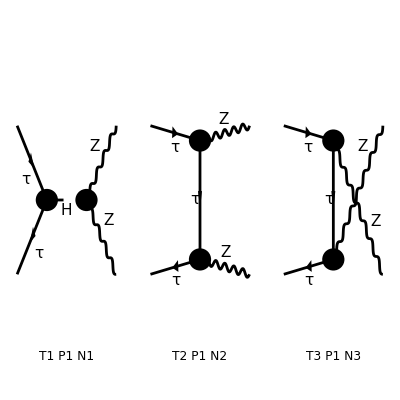

```mathematica
Process={F[2,{3}],-F[2,{3}]}-> {V[2],V[2]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

FeynAmpList(({F(2,{3}),-F(2,{3})}→{V(2),V(2)})→(F(2,{3}) | p1 | ML | {-Charge,LeptonNumber}
-F(2,{3}) | p2 | ML | {Charge,-LeptonNumber})→(V(2) | k1 | MZ | {}
V(2) | k2 | MZ | {}),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],(ⅈ EL MW 1/((k1+k2)^2-MH2) g(Lor1,Lor2) Conjugate[ep](V(2),k1,Lor1) Conjugate[ep](V(2),k2,Lor2) v̄(p2,ML).(-(ⅈ EL ML om_-)/(2 MW SW)-(ⅈ EL ML om_+)/(2 MW SW)).u(p1,ML))/(CW2 SW)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==2),Integral[],1/((p2-k2)^2-ML2) Conjugate[ep](V(2),k1,Lor1) Conjugate[ep](V(2),k2,Lor2) v̄(p2,ML).((ⅈ EL (SW2-1/2) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW ga(Lor2).om_+)/CW).(gs(k2-p2)+ML).((ⅈ EL (SW2-1/2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW ga(Lor1).om_+)/CW).u(p1,ML)),FeynAmp(GraphID(Topology==3,Generic==1,Particles==1,Number==3),Integral[],1/((p2-k1)^2-ML2) Conjugate[ep](V(2),k1,Lor1) Conjugate[ep](V(2),k2,Lor2) v̄(p2,ML).((ⅈ EL (SW2-1/2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW ga(Lor1).om_+)/CW).(gs(k1-p2)+ML).((ⅈ EL (SW2-1/2) ga(Lor2).om_-)/(CW SW)+(ⅈ EL SW ga(Lor2).om_+)/CW).u(p1,ML)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 144 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

1/(16 CW2^2 MZ2^2 SW2^2)Alfa2 π^2 (-8 ML2 (4 ML2-S) (12 MZ2^2-4 S MZ2+S^2) (Den(S,MH2))^2+4 ML2 ((S^3-(T-U) ((1-4 SW2)^2 T-U) S+4 ML2 (4 (16 SW2^2-8 SW2-1) MZ2^2+4 (S-SW2 (2 SW2-1) (T-U)) MZ2-S (S-2 SW2 (2 SW2-1) (T-U)))-4 MZ2^2 (S (16 SW2^2-8 SW2-1)+(32 SW2^2-16 SW2+3) (T-U))-2 MZ2 (2 S^2-(1-4 SW2)^2 (T-U) S+(T-U) (T-(1-4 SW2)^2 U))) Den(T,ML2)+(S^3-(T-U) (T-(1-4 SW2)^2 U) S+4 ML2 (4 (16 SW2^2-8 SW2-1) MZ2^2+4 (S+SW2 (2 SW2-1) (T-U)) MZ2-S (S+2 SW2 (2 SW2-1) (T-U)))-4 MZ2^2 (S (16 SW2^2-8 SW2-1)-(32 SW2^2-16 SW2+3) (T-U))-2 MZ2 (2 S^2+(1-4 SW2)^2 (T-U) S+(T-U) ((1-4 SW2)^2 T-U))) Den(U,ML2)) Den(S,MH2)+(4 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) ML2^4+4 (-2 S (16 SW2^4-16 SW2^3+20 SW2^2-8 SW2+1)+8 MZ2 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1)-(32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (3 T+U)) ML2^3+2 (2 (352 SW2^4-352 SW2^3+584 SW2^2-248 SW2+31) MZ2^2+4 (S (32 SW2^4-32 SW2^3-28 SW2^2+18 SW2-3)+(-352 SW2^4+352 SW2^3-244 SW2^2+78 SW2-9) T+(-32 SW2^4+32 SW2^3-44 SW2^2+18 SW2-3) U) MZ2+S (160 SW2^4-160 SW2^3+184 SW2^2-72 SW2+9) T+S (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) U+6 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) T (T+U)) ML2^2+(64 (16 SW2^4-16 SW2^3+30 SW2^2-13 SW2+2) MZ2^3-4 (S (96 SW2^4-96 SW2^3+104 SW2^2-40 SW2+5)+2 (608 SW2^4-608 SW2^3+472 SW2^2-160 SW2+23) T+2 (256 SW2^4-256 SW2^3+176 SW2^2-56 SW2+7) U) MZ2^2-2 (4 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) S^2+((-32 SW2^4+32 SW2^3-232 SW2^2+112 SW2-17) T+(32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) U) S-2 ((544 SW2^4-544 SW2^3+368 SW2^2-116 SW2+13) T^2+2 (96 SW2^4-96 SW2^3+92 SW2^2-34 SW2+5) U T+(32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) U^2)) MZ2+S^3 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1)-S^2 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (T-U)-4 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) T^2 (T+3 U)-4 S T ((64 SW2^4-64 SW2^3+64 SW2^2-24 SW2+3) T+(32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) U)) ML2+(32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (16 MZ2^4+8 (S-3 (3 T+U)) MZ2^3+4 (-5 S^2+7 T S-4 U S+12 T^2+U^2+14 T U) MZ2^2+2 (2 S^3+4 U S^2+(-3 T^2-3 U T+2 U^2) S-2 T (3 T^2+4 U T+U^2)) MZ2+T (-S^3+(T-U) S^2+2 T (T+U) S+4 T^2 U))) (Den(T,ML2))^2+(4 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) ML2^4+4 (-2 S (16 SW2^4-16 SW2^3+20 SW2^2-8 SW2+1)+8 MZ2 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1)-(32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (T+3 U)) ML2^3+2 (2 (352 SW2^4-352 SW2^3+584 SW2^2-248 SW2+31) MZ2^2+4 S (32 SW2^4-32 SW2^3-28 SW2^2+18 SW2-3) MZ2-8 ((64 SW2^4-64 SW2^3+58 SW2^2-21 SW2+3) T+(128 SW2^4-128 SW2^3+86 SW2^2-27 SW2+3) U) MZ2+3 S (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) T+S (96 SW2^4-96 SW2^3+136 SW2^2-56 SW2+7) U+6 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) U (T+U)) ML2^2+(64 (16 SW2^4-16 SW2^3+30 SW2^2-13 SW2+2) MZ2^3-4 (S (96 SW2^4-96 SW2^3+104 SW2^2-40 SW2+5)+2 (640 SW2^4-640 SW2^3+464 SW2^2-152 SW2+19) T+2 (224 SW2^4-224 SW2^3+184 SW2^2-64 SW2+11) U) MZ2^2-2 (4 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) S^2+((608 SW2^4-608 SW2^3+248 SW2^2-48 SW2+3) U-19 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) T) S-4 (3 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) T^2+2 (64 SW2^4-64 SW2^3+58 SW2^2-21 SW2+3) U T+(160 SW2^4-160 SW2^3+100 SW2^2-30 SW2+3) U^2)) MZ2+S^3 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1)-3 S^2 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (T-U)-4 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) U^2 (3 T+U)-2 S ((32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) T^2+4 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) U T+(32 SW2^4-32 SW2^3+56 SW2^2-24 SW2+3) U^2)) ML2+(32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (16 MZ2^4+8 (S-12 T) MZ2^3-4 (5 S^2-11 T S+8 U S-12 T^2+U^2-16 T U) MZ2^2+2 (2 S^3+(7 U-3 T) S^2+(-6 T^2-7 U T+9 U^2) S-2 (T+U)^3) MZ2+4 T U^3+S^3 (T-2 U)+2 S T U (T+U)+S^2 (T^2+U T-2 U^2))) (Den(U,ML2))^2-2 (4 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) ML2^4+4 (S (-32 SW2^4+32 SW2^3-56 SW2^2+24 SW2-3)+16 MZ2 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1)-2 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (T+U)) ML2^3+4 ((1248 SW2^4-1248 SW2^3+744 SW2^2-216 SW2+31) MZ2^2-(4 S (48 SW2^4-48 SW2^3+54 SW2^2-21 SW2+4)+(32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (23 T+17 U)) MZ2+S^2+4 S (16 SW2^4-16 SW2^3+20 SW2^2-8 SW2+1) T+S (32 SW2^4-32 SW2^3+56 SW2^2-24 SW2+3) U+(32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (T^2+4 U T+U^2)) ML2^2+(32 (64 SW2^4-64 SW2^3+52 SW2^2-18 SW2+3) MZ2^3-4 (S (480 SW2^4-480 SW2^3+88 SW2^2+16 SW2-1)+(736 SW2^4-736 SW2^3+616 SW2^2-216 SW2+30) T+2 (112 SW2^4-112 SW2^3+116 SW2^2-44 SW2+7) U) MZ2^2+2 (16 (8 SW2^4-8 SW2^3+SW2) S^2+4 ((112 SW2^4-112 SW2^3+102 SW2^2-37 SW2+5) T+(16 SW2^4-16 SW2^3+30 SW2^2-13 SW2+2) U) S+(416 SW2^4-416 SW2^3+352 SW2^2-124 SW2+15) T^2+(32 SW2^4-32 SW2^3+64 SW2^2-28 SW2+3) U^2+2 (800 SW2^4-800 SW2^3+560 SW2^2-180 SW2+23) T U) MZ2+S^3 (32 SW2^4-32 SW2^3+40 SW2^2-16 SW2+1)-2 S^2 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (T-U)-8 (32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) T U (T+U)-S ((160 SW2^4-160 SW2^3+136 SW2^2-48 SW2+5) T^2+2 (96 SW2^4-96 SW2^3+120 SW2^2-48 SW2+7) U T+(32 SW2^4-32 SW2^3+40 SW2^2-16 SW2+1) U^2)) ML2-(32 SW2^4-32 SW2^3+24 SW2^2-8 SW2+1) (32 MZ2^4+4 (2 S+T-9 U) MZ2^3+2 (2 S^2-6 T S+8 U S-7 T^2+9 U^2-16 T U) MZ2^2+(3 (T-U) S^2+(7 T^2+6 U T-5 U^2) S+2 (T^3+10 U T^2+7 U^2 T-2 U^3)) MZ2-4 T^2 U^2-S T (T+U)^2+S^3 U+S^2 (U^2-T^2))) Den(T,ML2) Den(U,ML2))

```mathematica
resFCtataZZ=square1//.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),ML2->MTA^2}
```

1/(256 cw^4 MZ2^2 sw^4)ee^4 (-(8 (4 MTA^2-S) (12 MZ2^2-4 S MZ2+S^2) MTA^2)/(S-MH2)^2+1/(S-MH2)4 (1/(U-MTA^2)(S^3-(T-U) (T-(1-4 sw^2)^2 U) S+4 MTA^2 (4 (16 sw^4-8 sw^2-1) MZ2^2+4 ((2 sw^2-1) (T-U) sw^2+S) MZ2-S (2 (2 sw^2-1) (T-U) sw^2+S))-4 MZ2^2 (S (16 sw^4-8 sw^2-1)-(32 sw^4-16 sw^2+3) (T-U))-2 MZ2 (2 S^2+(1-4 sw^2)^2 (T-U) S+(T-U) ((1-4 sw^2)^2 T-U)))+1/(T-MTA^2)(S^3-(T-U) ((1-4 sw^2)^2 T-U) S+4 MTA^2 (4 (16 sw^4-8 sw^2-1) MZ2^2+4 (S-sw^2 (2 sw^2-1) (T-U)) MZ2-S (S-2 sw^2 (2 sw^2-1) (T-U)))-4 MZ2^2 (S (16 sw^4-8 sw^2-1)+(32 sw^4-16 sw^2+3) (T-U))-2 MZ2 (2 S^2-(1-4 sw^2)^2 (T-U) S+(T-U) (T-(1-4 sw^2)^2 U)))) MTA^2+1/((T-MTA^2)^2)(4 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) MTA^8+4 (-2 S (16 sw^8-16 sw^6+20 sw^4-8 sw^2+1)+8 MZ2 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1)-(32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (3 T+U)) MTA^6+2 (2 (352 sw^8-352 sw^6+584 sw^4-248 sw^2+31) MZ2^2+4 (S (32 sw^8-32 sw^6-28 sw^4+18 sw^2-3)+(-352 sw^8+352 sw^6-244 sw^4+78 sw^2-9) T+(-32 sw^8+32 sw^6-44 sw^4+18 sw^2-3) U) MZ2+S (160 sw^8-160 sw^6+184 sw^4-72 sw^2+9) T+S (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) U+6 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) T (T+U)) MTA^4+(64 (16 sw^8-16 sw^6+30 sw^4-13 sw^2+2) MZ2^3-4 (S (96 sw^8-96 sw^6+104 sw^4-40 sw^2+5)+2 (608 sw^8-608 sw^6+472 sw^4-160 sw^2+23) T+2 (256 sw^8-256 sw^6+176 sw^4-56 sw^2+7) U) MZ2^2-2 (4 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) S^2+((-32 sw^8+32 sw^6-232 sw^4+112 sw^2-17) T+(32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) U) S-2 ((544 sw^8-544 sw^6+368 sw^4-116 sw^2+13) T^2+2 (96 sw^8-96 sw^6+92 sw^4-34 sw^2+5) U T+(32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) U^2)) MZ2+S^3 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1)-S^2 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (T-U)-4 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) T^2 (T+3 U)-4 S T ((64 sw^8-64 sw^6+64 sw^4-24 sw^2+3) T+(32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) U)) MTA^2+(32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (16 MZ2^4+8 (S-3 (3 T+U)) MZ2^3+4 (-5 S^2+7 T S-4 U S+12 T^2+U^2+14 T U) MZ2^2+2 (2 S^3+4 U S^2+(-3 T^2-3 U T+2 U^2) S-2 T (3 T^2+4 U T+U^2)) MZ2+T (-S^3+(T-U) S^2+2 T (T+U) S+4 T^2 U)))+1/((U-MTA^2)^2)(4 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) MTA^8+4 (-2 S (16 sw^8-16 sw^6+20 sw^4-8 sw^2+1)+8 MZ2 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1)-(32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (T+3 U)) MTA^6+2 (2 (352 sw^8-352 sw^6+584 sw^4-248 sw^2+31) MZ2^2+4 S (32 sw^8-32 sw^6-28 sw^4+18 sw^2-3) MZ2-8 ((64 sw^8-64 sw^6+58 sw^4-21 sw^2+3) T+(128 sw^8-128 sw^6+86 sw^4-27 sw^2+3) U) MZ2+3 S (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) T+S (96 sw^8-96 sw^6+136 sw^4-56 sw^2+7) U+6 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) U (T+U)) MTA^4+(64 (16 sw^8-16 sw^6+30 sw^4-13 sw^2+2) MZ2^3-4 (S (96 sw^8-96 sw^6+104 sw^4-40 sw^2+5)+2 (640 sw^8-640 sw^6+464 sw^4-152 sw^2+19) T+2 (224 sw^8-224 sw^6+184 sw^4-64 sw^2+11) U) MZ2^2-2 (4 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) S^2+((608 sw^8-608 sw^6+248 sw^4-48 sw^2+3) U-19 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) T) S-4 (3 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) T^2+2 (64 sw^8-64 sw^6+58 sw^4-21 sw^2+3) U T+(160 sw^8-160 sw^6+100 sw^4-30 sw^2+3) U^2)) MZ2+S^3 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1)-3 S^2 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (T-U)-4 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) U^2 (3 T+U)-2 S ((32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) T^2+4 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) U T+(32 sw^8-32 sw^6+56 sw^4-24 sw^2+3) U^2)) MTA^2+(32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (16 MZ2^4+8 (S-12 T) MZ2^3-4 (5 S^2-11 T S+8 U S-12 T^2+U^2-16 T U) MZ2^2+2 (2 S^3+(7 U-3 T) S^2+(-6 T^2-7 U T+9 U^2) S-2 (T+U)^3) MZ2+4 T U^3+S^3 (T-2 U)+2 S T U (T+U)+S^2 (T^2+U T-2 U^2)))-1/((T-MTA^2) (U-MTA^2))2 (4 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) MTA^8+4 (S (-32 sw^8+32 sw^6-56 sw^4+24 sw^2-3)+16 MZ2 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1)-2 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (T+U)) MTA^6+4 ((1248 sw^8-1248 sw^6+744 sw^4-216 sw^2+31) MZ2^2-(4 S (48 sw^8-48 sw^6+54 sw^4-21 sw^2+4)+(32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (23 T+17 U)) MZ2+S^2+4 S (16 sw^8-16 sw^6+20 sw^4-8 sw^2+1) T+S (32 sw^8-32 sw^6+56 sw^4-24 sw^2+3) U+(32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (T^2+4 U T+U^2)) MTA^4+(32 (64 sw^8-64 sw^6+52 sw^4-18 sw^2+3) MZ2^3-4 (S (480 sw^8-480 sw^6+88 sw^4+16 sw^2-1)+(736 sw^8-736 sw^6+616 sw^4-216 sw^2+30) T+2 (112 sw^8-112 sw^6+116 sw^4-44 sw^2+7) U) MZ2^2+2 (16 (8 sw^8-8 sw^6+sw^2) S^2+4 ((112 sw^8-112 sw^6+102 sw^4-37 sw^2+5) T+(16 sw^8-16 sw^6+30 sw^4-13 sw^2+2) U) S+(416 sw^8-416 sw^6+352 sw^4-124 sw^2+15) T^2+(32 sw^8-32 sw^6+64 sw^4-28 sw^2+3) U^2+2 (800 sw^8-800 sw^6+560 sw^4-180 sw^2+23) T U) MZ2+S^3 (32 sw^8-32 sw^6+40 sw^4-16 sw^2+1)-2 S^2 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (T-U)-8 (32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) T U (T+U)-S ((160 sw^8-160 sw^6+136 sw^4-48 sw^2+5) T^2+2 (96 sw^8-96 sw^6+120 sw^4-48 sw^2+7) U T+(32 sw^8-32 sw^6+40 sw^4-16 sw^2+1) U^2)) MTA^2-(32 sw^8-32 sw^6+24 sw^4-8 sw^2+1) (32 MZ2^4+4 (2 S+T-9 U) MZ2^3+2 (2 S^2-6 T S+8 U S-7 T^2+9 U^2-16 T U) MZ2^2+(3 (T-U) S^2+(7 T^2+6 U T-5 U^2) S+2 (T^3+10 U T^2+7 U^2 T-2 U^3)) MZ2-4 T^2 U^2-S T (T+U)^2+S^3 U+S^2 (U^2-T^2))))

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARtataZZ=Get["resANATARtataZZ.m"];
```

```mathematica
FullSimplify[resANATARtataZZ-4resFCtataZZ,{S+T+U==2MZ2+2 MTA^2,cw^2+sw^2==1}]
```

0

## τ τ -> ZA

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AtataZA=GenerateAmplitude[{ta,tabar}->{Z,A},OutputName->"tataZA",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tataZA.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tataZA/tataZA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {ta, tabar} -> {Z, A}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{ta(p1),tabar(p2)}→{Z(p3),A(p4)}},Total→2,Name→tataZA,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→0,p4.p4→0,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2+MZ^2-T),p2.p3→1/2 (MTA^2+MZ^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2+MZ^2-T),1/(p2.p3)→2/(MTA^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-1/2 ⅈ GC3 ε_Lor4(p4,0) Den(p1-p3,MTA) ε_Lor2(p3,MZ) (γ^Lor4)_(iSpin1 Spin3) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) ((GC35-GC15) (γ^Lor2 γ^5)_(iSpin2 Spin1)+(GC15+GC35) (γ^Lor2)_(iSpin2 Spin1)) (MTA 𝕀_iSpin1iSpin2+(γ·(p1-p3))_(iSpin1 iSpin2)),DiagramID(2)→-1/2 ⅈ GC3 ε_Lor4(p4,0) Den(p1-p4,MTA) ε_Lor2(p3,MZ) (γ^Lor4)_(iSpin2 Spin1) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) ((GC35-GC15) (γ^Lor2 γ^5)_(iSpin1 Spin3)+(GC15+GC35) (γ^Lor2)_(iSpin1 Spin3)) (MTA 𝕀_iSpin1iSpin2+(γ·(p1-p4))_(iSpin1 iSpin2))}|>

```mathematica
AtataZAC=GenerateAmplitudeConjugate[{ta,tabar}->{Z,A},OutputName->"tataZA",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tataZA.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tataZA/tataZA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {ta, tabar} -> {Z, A}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{ta(p1),tabar(p2)}→{Z(p3),A(p4)}},Total→2,Name→tataZA,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→0,p4.p4→0,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2+MZ^2-T),p2.p3→1/2 (MTA^2+MZ^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2+MZ^2-T),1/(p2.p3)→2/(MTA^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→1/2 ⅈ GC3 (ε^†)_LorC4^(p4,0) Den(p1-p3,MTA) (γ^LorC4)_(iSpinC1 SpinC3) (ε^†)_LorC2^(p3,MZ) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) ((GC15-GC35) (γ^5 γ^LorC2)_(iSpinC2 SpinC1)+(GC15+GC35) (γ^LorC2)_(iSpinC2 SpinC1)) (MTA 𝕀_iSpinC2iSpinC1+(γ·p1)_(iSpinC1 iSpinC2)-(γ·p3)_(iSpinC1 iSpinC2)),DiagramID(2)→1/2 ⅈ GC3 (ε^†)_LorC4^(p4,0) Den(p1-p4,MTA) (γ^LorC4)_(iSpinC2 SpinC1) (ε^†)_LorC2^(p3,MZ) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) ((GC15-GC35) (γ^5 γ^LorC2)_(iSpinC1 SpinC3)+(GC15+GC35) (γ^LorC2)_(iSpinC1 SpinC3)) (MTA 𝕀_iSpinC2iSpinC1+(γ·p1)_(iSpinC1 iSpinC2)-(γ·p4)_(iSpinC1 iSpinC2))}|>

```mathematica
AmpSQtataZA=GenerateAmplitudeSquare[AtataZA,AtataZAC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{ta(p1),tabar(p2)}→{Z(p3),A(p4)}},Name→tataZA,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→0,p4.p4→0,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2+MZ^2-T),p2.p3→1/2 (MTA^2+MZ^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2+MZ^2-T),1/(p2.p3)→2/(MTA^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→1/(2 cw^2 MZ^2 sw2)ee^4 (((2 MTA^6+(S-4 T) MTA^4-2 (MZ^4-(S+T) MZ^2+(S-T) T) MTA^2+2 MZ^6+S T^2+2 MZ^2 T U-2 MZ^4 (S+T+U)) cw^4-2 sw2 (2 MTA^6+(12 MZ^2+S-4 T) MTA^4+2 (5 MZ^4-(5 S+11 T+6 U) MZ^2+T (T-S)) MTA^2+2 MZ^6+S T^2+2 MZ^2 T U-2 MZ^4 (S+T+U)) cw^2+sw2^2 (10 MTA^6+(24 MZ^2+5 (S-4 T)) MTA^4+2 (7 MZ^4-(7 S+19 T+12 U) MZ^2+5 T (T-S)) MTA^2+5 (2 MZ^6-2 (S+T+U) MZ^4+2 T U MZ^2+S T^2))) (Den(p1-p3,MTA))^2+2 ((2 MTA^6+(10 MZ^2-S-2 (T+U)) MTA^4+(-2 MZ^4-(8 S+3 (T+U)) MZ^2+T^2+U^2+S (T+U)) MTA^2+S (2 MZ^2 (S+T+U)-T U)) cw^4+2 sw2 (6 MTA^6+(18 MZ^2+S-6 (T+U)) MTA^4+(-2 MZ^4+(T+U) MZ^2+T^2+U^2+4 T U-S (T+U)) MTA^2+S (T U-2 MZ^2 (S+T+U))) cw^2+sw2^2 (-6 MTA^6+(-6 MZ^2-5 S+6 (T+U)) MTA^4+(-2 MZ^4-(24 S+11 (T+U)) MZ^2+T^2+U^2-8 T U+5 S (T+U)) MTA^2+5 S (2 MZ^2 (S+T+U)-T U))) Den(p3-p2,MTA) Den(p1-p3,MTA)+((-((MZ^2-2 S-3 T+U) MTA^4)-(4 MZ^4-(3 T+5 U) MZ^2+T^2-U^2+S T+3 S U+4 T U) MTA^2+(MZ^2-S-T) (MZ^4+(T-S) MZ^2-U (T+U))) cw^4+2 sw2 ((37 MZ^2-2 S-3 T+U) MTA^4+(16 MZ^4-(12 S+15 T+5 U) MZ^2+T^2-U^2+S T+3 S U+4 T U) MTA^2-(MZ^2-S-T) (MZ^4+(T-S) MZ^2-U (T+U))) cw^2+sw2^2 ((-77 MZ^2+10 S+15 T-5 U) MTA^4+(-44 MZ^4+(24 S+39 T+25 U) MZ^2-5 (T^2+S T+4 U T-U^2+3 S U)) MTA^2+5 (MZ^2-S-T) (MZ^4+(T-S) MZ^2-U (T+U)))) (Den(p3-p2,MTA))^2)|>

```mathematica
resANATARtataZA=AmpSQtataZA[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(p1-p3)->√T,(p3-p2)->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/(2 cw^2 MZ^2 sw^2)ee^4 (1/((T-MTA^2)^2)((2 MTA^6+(S-4 T) MTA^4-2 (MZ^4-(S+T) MZ^2+(S-T) T) MTA^2+2 MZ^6+S T^2+2 MZ^2 T U-2 MZ^4 (S+T+U)) cw^4-2 sw^2 (2 MTA^6+(12 MZ^2+S-4 T) MTA^4+2 (5 MZ^4-(5 S+11 T+6 U) MZ^2+T (T-S)) MTA^2+2 MZ^6+S T^2+2 MZ^2 T U-2 MZ^4 (S+T+U)) cw^2+sw^4 (10 MTA^6+(24 MZ^2+5 (S-4 T)) MTA^4+2 (7 MZ^4-(7 S+19 T+12 U) MZ^2+5 T (T-S)) MTA^2+5 (2 MZ^6-2 (S+T+U) MZ^4+2 T U MZ^2+S T^2)))+1/((U-MTA^2)^2)((-((MZ^2-2 S-3 T+U) MTA^4)-(4 MZ^4-(3 T+5 U) MZ^2+T^2-U^2+S T+3 S U+4 T U) MTA^2+(MZ^2-S-T) (MZ^4+(T-S) MZ^2-U (T+U))) cw^4+2 sw^2 ((37 MZ^2-2 S-3 T+U) MTA^4+(16 MZ^4-(12 S+15 T+5 U) MZ^2+T^2-U^2+S T+3 S U+4 T U) MTA^2-(MZ^2-S-T) (MZ^4+(T-S) MZ^2-U (T+U))) cw^2+sw^4 ((-77 MZ^2+10 S+15 T-5 U) MTA^4+(-44 MZ^4+(24 S+39 T+25 U) MZ^2-5 (T^2+S T+4 U T-U^2+3 S U)) MTA^2+5 (MZ^2-S-T) (MZ^4+(T-S) MZ^2-U (T+U))))+1/((T-MTA^2) (U-MTA^2))2 ((2 MTA^6+(10 MZ^2-S-2 (T+U)) MTA^4+(-2 MZ^4-(8 S+3 (T+U)) MZ^2+T^2+U^2+S (T+U)) MTA^2+S (2 MZ^2 (S+T+U)-T U)) cw^4+2 sw^2 (6 MTA^6+(18 MZ^2+S-6 (T+U)) MTA^4+(-2 MZ^4+(T+U) MZ^2+T^2+U^2+4 T U-S (T+U)) MTA^2+S (T U-2 MZ^2 (S+T+U))) cw^2+sw^4 (-6 MTA^6+(-6 MZ^2-5 S+6 (T+U)) MTA^4+(-2 MZ^4-(24 S+11 (T+U)) MZ^2+T^2+U^2-8 T U+5 S (T+U)) MTA^2+5 S (2 MZ^2 (S+T+U)-T U))))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARtataZA.m",resANATARtataZA];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 1 diagram

> Top. 2 aebf/cfde/ef.m, 1 diagram

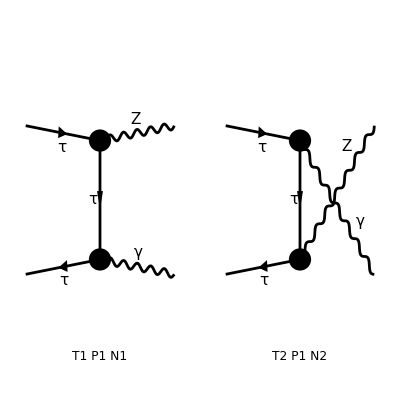

```mathematica
Process={F[2,{3}],-F[2,{3}]}-> {V[2],V[1]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1,GaugeTerms->False]//.Subexpr[]//.Abbr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

FeynAmpList(({F(2,{3}),-F(2,{3})}→{V(2),V(1)})→(F(2,{3}) | p1 | ML | {-Charge,LeptonNumber}
-F(2,{3}) | p2 | ML | {Charge,-LeptonNumber})→(V(2) | k1 | MZ | {}
V(1) | k2 | 0 | {}),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],1/((p2-k2)^2-ML2) Conjugate[ep](V(1),k2,Lor2) Conjugate[ep](V(2),k1,Lor1) v̄(p2,ML).(ⅈ EL ga(Lor2).om_-+ⅈ EL ga(Lor2).om_+).(gs(k2-p2)+ML).((ⅈ EL (SW2-1/2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW ga(Lor1).om_+)/CW).u(p1,ML)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==2),Integral[],1/((p2-k1)^2-ML2) Conjugate[ep](V(1),k2,Lor2) Conjugate[ep](V(2),k1,Lor1) v̄(p2,ML).((ⅈ EL (SW2-1/2) ga(Lor1).om_-)/(CW SW)+(ⅈ EL SW ga(Lor1).om_+)/CW).(gs(k1-p2)+ML).(ⅈ EL ga(Lor2).om_-+ⅈ EL ga(Lor2).om_+).u(p1,ML)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 144 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

1/(CW2 MZ2 SW2)π^2 Alfa2 (-2 Den(T,ML2) Den(U,ML2) (16 ML2^3 (4 SW2^2-2 SW2+1)+2 ML2^2 (3 MZ2 (56 SW2^2-28 SW2+3)-2 (24 SW2^2-12 SW2+5) T-8 (4 SW2^2-2 SW2+1) U)+ML2 (4 MZ2^2 (32 SW2^2-16 SW2+3)-MZ2 (S (216 SW2^2-108 SW2+7)+(8 SW2^2-4 SW2+1) (17 T+19 U))+S^2 (-8 SW2^2+4 SW2-5)+2 S (8 SW2^2-4 SW2+1) (T-U)+40 SW2^2 T^2+80 SW2^2 T U+8 SW2^2 U^2-20 SW2 T^2-40 SW2 T U-4 SW2 U^2+7 T^2+14 T U+3 U^2)-(8 SW2^2-4 SW2+1) (2 MZ2^3+MZ2^2 (4 S-T+U)-MZ2 (2 S^2+5 S T+6 S U+2 T^2+5 T U+3 U^2)-S^2 U+S (T^2-U^2)+T (T+U)^2))+(Den(T,ML2))^2 (8 ML2^3 (8 SW2^2-4 SW2+1)-2 ML2^2 (MZ2 (8 SW2^2-4 SW2-7)+(8 SW2^2-4 SW2+1) (9 T+U))+ML2 (4 MZ2^2 (1-4 SW2)^2+MZ2 (S (-24 SW2^2+12 SW2+1)-4 (4 (10 SW2^2-5 SW2+1) T+(1-4 SW2)^2 U))-(8 SW2^2-4 SW2+1) (3 S^2+S (U-T)-4 T (3 T+U)))+(8 SW2^2-4 SW2+1) (6 MZ2^3-2 MZ2^2 (2 S+5 T+3 U)+MZ2 (-3 S^2+5 S T-2 S U+6 T^2+8 T U)+(S^2+S T-2 T^2) (S+T+U)))+(Den(U,ML2))^2 (8 ML2^3 (8 SW2^2-4 SW2+1)-2 ML2^2 (MZ2 (8 SW2^2-4 SW2-7)+(8 SW2^2-4 SW2+1) (3 T+7 U))+ML2 (4 MZ2^2 (1-4 SW2)^2+MZ2 S (-24 SW2^2+12 SW2+1)-2 MZ2 ((88 SW2^2-44 SW2+9) T+(24 SW2^2-12 SW2+1) U)+(8 SW2^2-4 SW2+1) (S^2+3 S T-3 S U+2 T^2+8 T U+6 U^2))+(8 SW2^2-4 SW2+1) (6 MZ2^3-4 MZ2^2 (S+3 T+U)-MZ2 (S^2-5 S T+2 S U-6 T^2-10 T U+2 U^2)-S^3+S^2 (U-2 T)-S (T^2+T U-2 U^2)-2 T U (T+U))))

```mathematica
resFCtataZA=square1//.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),ML2->MTA^2}//FullSimplify[#,S+T+U==2 MTA^2+MZ2]&
```

1/(32 cw^2 MZ2 sw^2 (MTA^2-T)^2 (MTA^2-U)^2)ee^4 (MZ2^5 (8 sw^4-4 sw^2+12)+MZ2^4 (S (32 sw^4-16 sw^2-33)+(64 sw^4-32 sw^2-15) (T+U))+MZ2^3 (S^2 (-112 sw^4+56 sw^2+30)+S (-224 sw^4+112 sw^2+34) (T+U)+(-64 sw^4+32 sw^2+5) T^2+(-128 sw^4+64 sw^2+6) T U+(-64 sw^4+32 sw^2+5) U^2)+MZ2^2 (S^3 (96 sw^4-48 sw^2-8)+2 S^2 (128 sw^4-64 sw^2-11) (T+U)+S ((128 sw^4-64 sw^2-17) T^2+(256 sw^4-128 sw^2+2) T U+(128 sw^4-64 sw^2-17) U^2)-(T-U)^2 (T+U))+MZ2 (S^4 (-24 sw^4+12 sw^2-2)+S^3 (-96 sw^4+48 sw^2+2) (T+U)+S^2 ((-96 sw^4+48 sw^2+9) T^2+(-64 sw^4+32 sw^2-2) T U+(-96 sw^4+48 sw^2+9) U^2)-4 S (8 sw^4-4 sw^2-1) (T-U)^2 (T+U)-(8 sw^4-4 sw^2+1) (T-U)^4)+S^2 (S+T-U) (S-T+U) (S+T+U))

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARtataZA=Get["resANATARtataZA.m"];
```

```mathematica
FullSimplify[resANATARtataZA-4resFCtataZA,{S+T+U==2 MTA^2+MZ2,cw^2+sw^2==1}]
```

0

## τ τ -> AA

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AtataAA=GenerateAmplitude[{ta,tabar}->{A,A},OutputName->"tataAA",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tataAA.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tataAA/tataAA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {ta, tabar} -> {A, A}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{ta(p1),tabar(p2)}→{A(p3),A(p4)}},Total→2,Name→tataAA,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2-T),p2.p3→1/2 (MTA^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2-T),1/(p2.p3)→2/(MTA^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC3^2 ε_Lor2(p3,0) ε_Lor4(p4,0) Den(p1-p3,MTA) (γ^Lor4)_(iSpin1 Spin3) (γ^Lor2)_(iSpin2 Spin1) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) (MTA 𝕀_iSpin1iSpin2+(γ·(p1-p3))_(iSpin1 iSpin2)),DiagramID(2)→-ⅈ GC3^2 ε_Lor2(p3,0) ε_Lor4(p4,0) Den(p1-p4,MTA) (γ^Lor2)_(iSpin1 Spin3) (γ^Lor4)_(iSpin2 Spin1) (v̄)_Spin3(p2,MTA) u_Spin1(p1,MTA) (MTA 𝕀_iSpin1iSpin2+(γ·(p1-p4))_(iSpin1 iSpin2))}|>

```mathematica
AtataAAC=GenerateAmplitudeConjugate[{ta,tabar}->{A,A},OutputName->"tataAA",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_tataAA.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/tataAA/tataAA_0

Computing amplitudes...

A total of 2 diagrams have been generated for the process {ta, tabar} -> {A, A}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{ta(p1),tabar(p2)}→{A(p3),A(p4)}},Total→2,Name→tataAA,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2-T),p2.p3→1/2 (MTA^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2-T),1/(p2.p3)→2/(MTA^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC3^2 (ε^†)_LorC2^(p3,0) (ε^†)_LorC4^(p4,0) Den(p1-p3,MTA) (γ^LorC4)_(iSpinC1 SpinC3) (γ^LorC2)_(iSpinC2 SpinC1) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) (MTA 𝕀_iSpinC2iSpinC1+(γ·p1)_(iSpinC1 iSpinC2)-(γ·p3)_(iSpinC1 iSpinC2)),DiagramID(2)→ⅈ GC3^2 (ε^†)_LorC2^(p3,0) (ε^†)_LorC4^(p4,0) Den(p1-p4,MTA) (γ^LorC2)_(iSpinC1 SpinC3) (γ^LorC4)_(iSpinC2 SpinC1) ((ū)^†)_SpinC1(p1,MTA) (v^†)_SpinC3(p2,MTA) (MTA 𝕀_iSpinC2iSpinC1+(γ·p1)_(iSpinC1 iSpinC2)-(γ·p4)_(iSpinC1 iSpinC2))}|>

```mathematica
AmpSQtataAA=GenerateAmplitudeSquare[AtataAA,AtataAAC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{ta(p1),tabar(p2)}→{A(p3),A(p4)}},Name→tataAA,LoopOrder→0,Kinematics→{p1^2→MTA^2,p1.p1→MTA^2,1/(p1.p1)→1/MTA^2,p2^2→MTA^2,p2.p2→MTA^2,1/(p2.p2)→1/MTA^2,p3^2→0,p3.p3→0,p4^2→0,p4.p4→0,p1.p2→1/2 (S-2 MTA^2),p1.p3→1/2 (MTA^2-T),p2.p3→1/2 (MTA^2-U),1/(p1.p2)→2/(S-2 MTA^2),1/(p1.p3)→2/(MTA^2-T),1/(p2.p3)→2/(MTA^2-U),p4→p1+p2-p3},Amplitudes→8 ee^4 (-2 (2 MTA^4+MTA^2 (2 S+T+U)-S (S+T+U)) Den(p1-p3,MTA) Den(p3-p2,MTA)+(3 MTA^4-MTA^2 (2 S+5 T+3 U)+T U) (Den(p1-p3,MTA))^2+(-9 MTA^4+MTA^2 (2 S+3 T+U)+(S+T) (S+U)) (Den(p3-p2,MTA))^2)|>

```mathematica
resANATARtataAA=AmpSQtataAA[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(p1-p3)->√T,(p3-p2)->√U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

8 ee^4 (-(2 (2 MTA^4+MTA^2 (2 S+T+U)-S (S+T+U)))/((T-MTA^2) (U-MTA^2))+(-9 MTA^4+MTA^2 (2 S+3 T+U)+(S+T) (S+U))/((U-MTA^2)^2)+(3 MTA^4-MTA^2 (2 S+5 T+3 U)+T U)/((T-MTA^2)^2))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARtataAA.m",resANATARtataAA];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 1 diagram

> Top. 2 aebf/cfde/ef.m, 1 diagram

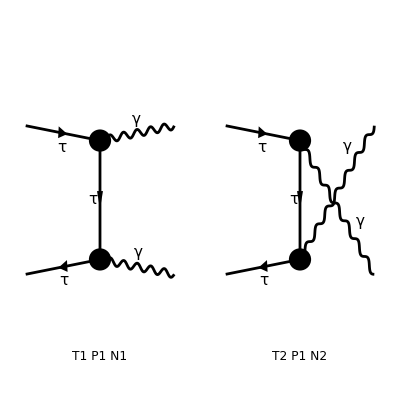

```mathematica
Process={F[2,{3}],-F[2,{3}]}-> {V[1],V[1]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[]
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1,GaugeTerms->False]//.Subexpr[]//.Abbr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

FeynAmpList(({F(2,{3}),-F(2,{3})}→{V(1),V(1)})→(F(2,{3}) | p1 | ML | {-Charge,LeptonNumber}
-F(2,{3}) | p2 | ML | {Charge,-LeptonNumber})→(V(1) | k1 | 0 | {}
V(1) | k2 | 0 | {}),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],1/((p2-k2)^2-ML2) Conjugate[ep](V(1),k1,Lor1) Conjugate[ep](V(1),k2,Lor2) v̄(p2,ML).(ⅈ EL ga(Lor2).om_-+ⅈ EL ga(Lor2).om_+).(gs(k2-p2)+ML).(ⅈ EL ga(Lor1).om_-+ⅈ EL ga(Lor1).om_+).u(p1,ML)),FeynAmp(GraphID(Topology==2,Generic==1,Particles==1,Number==2),Integral[],1/((p2-k1)^2-ML2) Conjugate[ep](V(1),k1,Lor1) Conjugate[ep](V(1),k2,Lor2) v̄(p2,ML).(ⅈ EL ga(Lor1).om_-+ⅈ EL ga(Lor1).om_+).(gs(k1-p2)+ML).(ⅈ EL ga(Lor2).om_-+ⅈ EL ga(Lor2).om_+).u(p1,ML)))

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

> 64 helicity matrix elements

preparing FORM code in /Users/avasquez/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

-16 π^2 Alfa2 (-2 Den(T,ML2) Den(U,ML2) (2 ML2^2+ML2 (3 S-9 T-7 U)+S T+2 T^2+3 T U+U^2)+(Den(U,ML2))^2 (4 ML2^2+ML2 (5 S+9 T-5 U)-2 S T+S U-2 T^2-T U+3 U^2)+(Den(T,ML2))^2 (4 ML2^2+ML2 (5 S+T+3 U)-2 S T+S U-T U+U^2))

```mathematica
resFCtataAA=square1//.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y),ML2->MTA^2}//FullSimplify[#,S+T+U==2 MTA^2]&
```

-(ee^4 (3 S^4+12 S^3 (T+U)+4 S^2 (3 T^2+2 T U+3 U^2)+4 S (T-U)^2 (T+U)+(T-U)^4))/(4 (MTA^2-T)^2 (MTA^2-U)^2)

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARtataAA=Get["resANATARtataAA.m"];
```

```mathematica
FullSimplify[resANATARtataAA-4resFCtataAA,{S+T+U==2 MTA^2,cw^2+sw^2==1}]
```

0

## W+ W- -> ZZ

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AWWZZ=GenerateAmplitude[{W,Wbar}->{Z,Z},OutputName->"WWZZ",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_WWZZ.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/WWZZ/WWZZ_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {W, Wbar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{W(p1),Wbar(p2)}→{Z(p3),Z(p4)}},Total→6,Name→WWZZ,LoopOrder→0,Kinematics→{p1^2→MW^2,p1.p1→MW^2,1/(p1.p1)→1/MW^2,p2^2→MW^2,p2.p2→MW^2,1/(p2.p2)→1/MW^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MW^2),p1.p3→1/2 (MW^2+MZ^2-T),p2.p3→1/2 (MW^2+MZ^2-U),1/(p1.p2)→2/(S-2 MW^2),1/(p1.p3)→2/(MW^2+MZ^2-T),1/(p2.p3)→2/(MW^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC21 ε_Lor3(p2,MW) (ε_Lor3(p4,MZ) ε_Lor2(p3,MZ) ε_Lor2(p1,MW)+ε_Lor4(p4,MZ) (ε_Lor3(p3,MZ) ε_Lor4(p1,MW)-2 ε_Lor4(p3,MZ) ε_Lor3(p1,MW))),DiagramID(2)→-ⅈ GC61 GC70 Den(-p1-p2,MH) ε_Lor4(p4,MZ) ε_Lor3(p2,MW) ε_Lor4(p3,MZ) ε_Lor3(p1,MW),DiagramID(3)→ⅈ GC57 GC58 Den(p1-p3,MW) ε_Lor3(p4,MZ) ε_Lor3(p2,MW) ε_Lor2(p3,MZ) ε_Lor2(p1,MW),DiagramID(4)→ⅈ GC27^2 Den(p1-p3,MW) (-2 ε_p3(p4,MZ) ε_iLor2(p2,MW) ε_p1(p3,MZ) ε_iLor2(p1,MW)-2 ε_iLor2(p4,MZ) ε_p1(p2,MW) ε_p1(p3,MZ) ε_iLor2(p1,MW)+2 ε_iLor2(p4,MZ) ε_p3(p2,MW) ε_p1(p3,MZ) ε_iLor2(p1,MW)-2 ε_iLor2(p4,MZ) ε_p4(p2,MW) ε_p1(p3,MZ) ε_iLor2(p1,MW)+ε_p3(p4,MZ) ε_iLor2(p2,MW) ε_p3(p3,MZ) ε_iLor2(p1,MW)+ε_iLor2(p4,MZ) ε_p1(p2,MW) ε_p3(p3,MZ) ε_iLor2(p1,MW)-ε_iLor2(p4,MZ) ε_p3(p2,MW) ε_p3(p3,MZ) ε_iLor2(p1,MW)+ε_iLor2(p4,MZ) ε_p4(p2,MW) ε_p3(p3,MZ) ε_iLor2(p1,MW)-(p1.p2+p1.p4+p2.p3+p3.p4) ε_Lor3(p4,MZ) ε_Lor3(p2,MW) ε_Lor2(p3,MZ) ε_Lor2(p1,MW)+2 ε_p3(p4,MZ) ε_p1(p2,MW) ε_Lor2(p3,MZ) ε_Lor2(p1,MW)+ε_p3(p4,MZ) ε_p4(p2,MW) ε_Lor2(p3,MZ) ε_Lor2(p1,MW)+ε_p3(p4,MZ) ε_iLor2(p2,MW) ε_iLor2(p3,MZ) ε_p1(p1,MW)+ε_iLor2(p4,MZ) ε_p1(p2,MW) ε_iLor2(p3,MZ) ε_p1(p1,MW)-ε_iLor2(p4,MZ) ε_p3(p2,MW) ε_iLor2(p3,MZ) ε_p1(p1,MW)+ε_iLor2(p4,MZ) ε_p4(p2,MW) ε_iLor2(p3,MZ) ε_p1(p1,MW)-ε_Lor3(p4,MZ) ε_Lor3(p2,MW) ε_p2(p3,MZ) ε_p1(p1,MW)-ε_Lor3(p4,MZ) ε_Lor3(p2,MW) ε_p4(p3,MZ) ε_p1(p1,MW)+2 ε_Lor3(p4,MZ) ε_Lor3(p2,MW) ε_p1(p3,MZ) ε_p2(p1,MW)-ε_Lor3(p4,MZ) ε_Lor3(p2,MW) ε_p3(p3,MZ) ε_p2(p1,MW)+ε_p1(p4,MZ) ((ε_p4(p2,MW)-2 ε_p3(p2,MW)) ε_Lor2(p3,MZ) ε_Lor2(p1,MW)+ε_iLor2(p2,MW) ((2 ε_p1(p3,MZ)-ε_p3(p3,MZ)) ε_iLor2(p1,MW)-ε_iLor2(p3,MZ) (ε_p1(p1,MW)-2 ε_p3(p1,MW))))+ε_p2(p4,MZ) ((ε_p1(p2,MW)+ε_p3(p2,MW)) ε_Lor2(p3,MZ) ε_Lor2(p1,MW)+ε_iLor2(p2,MW) ((ε_p3(p3,MZ)-2 ε_p1(p3,MZ)) ε_iLor2(p1,MW)+ε_iLor2(p3,MZ) (ε_p1(p1,MW)-2 ε_p3(p1,MW))))-2 ε_p3(p4,MZ) ε_iLor2(p2,MW) ε_iLor2(p3,MZ) ε_p3(p1,MW)-2 ε_iLor2(p4,MZ) ε_p1(p2,MW) ε_iLor2(p3,MZ) ε_p3(p1,MW)+2 ε_iLor2(p4,MZ) ε_p3(p2,MW) ε_iLor2(p3,MZ) ε_p3(p1,MW)-2 ε_iLor2(p4,MZ) ε_p4(p2,MW) ε_iLor2(p3,MZ) ε_p3(p1,MW)+2 ε_Lor3(p4,MZ) ε_Lor3(p2,MW) ε_p2(p3,MZ) ε_p3(p1,MW)+2 ε_Lor3(p4,MZ) ε_Lor3(p2,MW) ε_p4(p3,MZ) ε_p3(p1,MW)+ε_Lor3(p4,MZ) ε_Lor3(p2,MW) (2 ε_p1(p3,MZ)-ε_p3(p3,MZ)) ε_p4(p1,MW)),DiagramID(5)→ⅈ GC57 GC58 Den(p1-p4,MW) ε_Lor4(p4,MZ) ε_Lor3(p2,MW) ε_Lor3(p3,MZ) ε_Lor4(p1,MW),DiagramID(6)→-ⅈ GC27^2 Den(p1-p4,MW) ((p1.p2+p1.p3+p2.p4+p3.p4) ε_Lor4(p4,MZ) ε_Lor3(p2,MW) ε_Lor3(p3,MZ) ε_Lor4(p1,MW)-ε_Lor4(p4,MZ) ε_p3(p2,MW) ε_p1(p3,MZ) ε_Lor4(p1,MW)+2 ε_Lor4(p4,MZ) ε_p4(p2,MW) ε_p1(p3,MZ) ε_Lor4(p1,MW)-ε_Lor4(p4,MZ) ε_p1(p2,MW) ε_p2(p3,MZ) ε_Lor4(p1,MW)-ε_Lor4(p4,MZ) ε_p4(p2,MW) ε_p2(p3,MZ) ε_Lor4(p1,MW)-2 ε_Lor4(p4,MZ) ε_p1(p2,MW) ε_p4(p3,MZ) ε_Lor4(p1,MW)-ε_Lor4(p4,MZ) ε_p3(p2,MW) ε_p4(p3,MZ) ε_Lor4(p1,MW)-ε_iLor2(p4,MZ) ε_p1(p2,MW) ε_iLor2(p3,MZ) ε_p1(p1,MW)-ε_iLor2(p4,MZ) ε_p3(p2,MW) ε_iLor2(p3,MZ) ε_p1(p1,MW)+ε_iLor2(p4,MZ) ε_p4(p2,MW) ε_iLor2(p3,MZ) ε_p1(p1,MW)+ε_p2(p4,MZ) ε_Lor3(p2,MW) ε_Lor3(p3,MZ) ε_p1(p1,MW)+ε_p3(p4,MZ) ε_Lor3(p2,MW) ε_Lor3(p3,MZ) ε_p1(p1,MW)+ε_iLor2(p4,MZ) ε_iLor2(p2,MW) ε_p1(p3,MZ) ε_p1(p1,MW)-ε_iLor2(p4,MZ) ε_iLor2(p2,MW) ε_p2(p3,MZ) ε_p1(p1,MW)-ε_iLor2(p4,MZ) ε_iLor2(p2,MW) ε_p4(p3,MZ) ε_p1(p1,MW)+2 ε_p1(p4,MZ) (((ε_p1(p2,MW)+ε_p3(p2,MW)-ε_p4(p2,MW)) ε_iLor2(p3,MZ)+ε_iLor2(p2,MW) (-ε_p1(p3,MZ)+ε_p2(p3,MZ)+ε_p4(p3,MZ))) ε_iLor2(p1,MW)-ε_Lor3(p2,MW) ε_Lor3(p3,MZ) (ε_p2(p1,MW)+ε_p3(p1,MW)))+ε_p4(p4,MZ) (ε_Lor3(p2,MW) ε_Lor3(p3,MZ) (ε_p2(p1,MW)+ε_p3(p1,MW))-((ε_p1(p2,MW)+ε_p3(p2,MW)-ε_p4(p2,MW)) ε_iLor2(p3,MZ)+ε_iLor2(p2,MW) (-ε_p1(p3,MZ)+ε_p2(p3,MZ)+ε_p4(p3,MZ))) ε_iLor2(p1,MW))+2 (ε_iLor2(p4,MZ) ((ε_p1(p2,MW)+ε_p3(p2,MW)-ε_p4(p2,MW)) ε_iLor2(p3,MZ)+ε_iLor2(p2,MW) (-ε_p1(p3,MZ)+ε_p2(p3,MZ)+ε_p4(p3,MZ)))-(ε_p2(p4,MZ)+ε_p3(p4,MZ)) ε_Lor3(p2,MW) ε_Lor3(p3,MZ)) ε_p4(p1,MW))}|>

```mathematica
AWWZZC=GenerateAmplitudeConjugate[{W,Wbar}->{Z,Z},OutputName->"WWZZ",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_WWZZ.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/WWZZ/WWZZ_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {W, Wbar} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{W(p1),Wbar(p2)}→{Z(p3),Z(p4)}},Total→6,Name→WWZZ,LoopOrder→0,Kinematics→{p1^2→MW^2,p1.p1→MW^2,1/(p1.p1)→1/MW^2,p2^2→MW^2,p2.p2→MW^2,1/(p2.p2)→1/MW^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MW^2),p1.p3→1/2 (MW^2+MZ^2-T),p2.p3→1/2 (MW^2+MZ^2-U),1/(p1.p2)→2/(S-2 MW^2),1/(p1.p3)→2/(MW^2+MZ^2-T),1/(p2.p3)→2/(MW^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC21 (ε^†)_LorC3^(p2,MW) ((ε^†)_LorC3^(p4,MZ) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC2^(p1,MW)+(ε^†)_LorC4^(p4,MZ) ((ε^†)_LorC3^(p3,MZ) (ε^†)_LorC4^(p1,MW)-2 (ε^†)_LorC4^(p3,MZ) (ε^†)_LorC3^(p1,MW))),DiagramID(2)→ⅈ GC61 GC70 Den(-p1-p2,MH) (ε^†)_LorC4^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_LorC4^(p3,MZ) (ε^†)_LorC3^(p1,MW),DiagramID(3)→-ⅈ GC57 GC58 Den(p1-p3,MW) (ε^†)_LorC3^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC2^(p1,MW),DiagramID(4)→-ⅈ GC27^2 Den(p1-p3,MW) (-2 (ε^†)_p3^(p4,MZ) (ε^†)_iLorC2^(p2,MW) (ε^†)_p1^(p3,MZ) (ε^†)_iLorC2^(p1,MW)-2 (ε^†)_iLorC2^(p4,MZ) (ε^†)_p1^(p2,MW) (ε^†)_p1^(p3,MZ) (ε^†)_iLorC2^(p1,MW)+2 (ε^†)_iLorC2^(p4,MZ) (ε^†)_p3^(p2,MW) (ε^†)_p1^(p3,MZ) (ε^†)_iLorC2^(p1,MW)-2 (ε^†)_iLorC2^(p4,MZ) (ε^†)_p4^(p2,MW) (ε^†)_p1^(p3,MZ) (ε^†)_iLorC2^(p1,MW)+(ε^†)_p3^(p4,MZ) (ε^†)_iLorC2^(p2,MW) (ε^†)_p3^(p3,MZ) (ε^†)_iLorC2^(p1,MW)+(ε^†)_iLorC2^(p4,MZ) (ε^†)_p1^(p2,MW) (ε^†)_p3^(p3,MZ) (ε^†)_iLorC2^(p1,MW)-(ε^†)_iLorC2^(p4,MZ) (ε^†)_p3^(p2,MW) (ε^†)_p3^(p3,MZ) (ε^†)_iLorC2^(p1,MW)+(ε^†)_iLorC2^(p4,MZ) (ε^†)_p4^(p2,MW) (ε^†)_p3^(p3,MZ) (ε^†)_iLorC2^(p1,MW)-(p1.p2+p1.p4+p2.p3+p3.p4) (ε^†)_LorC3^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC2^(p1,MW)+2 (ε^†)_p3^(p4,MZ) (ε^†)_p1^(p2,MW) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC2^(p1,MW)+(ε^†)_p3^(p4,MZ) (ε^†)_p4^(p2,MW) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC2^(p1,MW)+(ε^†)_p3^(p4,MZ) (ε^†)_iLorC2^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p1^(p1,MW)+(ε^†)_iLorC2^(p4,MZ) (ε^†)_p1^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p1^(p1,MW)-(ε^†)_iLorC2^(p4,MZ) (ε^†)_p3^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p1^(p1,MW)+(ε^†)_iLorC2^(p4,MZ) (ε^†)_p4^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p1^(p1,MW)-(ε^†)_LorC3^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_p2^(p3,MZ) (ε^†)_p1^(p1,MW)-(ε^†)_LorC3^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_p4^(p3,MZ) (ε^†)_p1^(p1,MW)+2 (ε^†)_LorC3^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_p1^(p3,MZ) (ε^†)_p2^(p1,MW)-(ε^†)_LorC3^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_p3^(p3,MZ) (ε^†)_p2^(p1,MW)+(ε^†)_p1^(p4,MZ) (((ε^†)_p4^(p2,MW)-2 (ε^†)_p3^(p2,MW)) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC2^(p1,MW)+(ε^†)_iLorC2^(p2,MW) ((2 (ε^†)_p1^(p3,MZ)-(ε^†)_p3^(p3,MZ)) (ε^†)_iLorC2^(p1,MW)-(ε^†)_iLorC2^(p3,MZ) ((ε^†)_p1^(p1,MW)-2 (ε^†)_p3^(p1,MW))))+(ε^†)_p2^(p4,MZ) (((ε^†)_p1^(p2,MW)+(ε^†)_p3^(p2,MW)) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC2^(p1,MW)+(ε^†)_iLorC2^(p2,MW) (((ε^†)_p3^(p3,MZ)-2 (ε^†)_p1^(p3,MZ)) (ε^†)_iLorC2^(p1,MW)+(ε^†)_iLorC2^(p3,MZ) ((ε^†)_p1^(p1,MW)-2 (ε^†)_p3^(p1,MW))))-2 (ε^†)_p3^(p4,MZ) (ε^†)_iLorC2^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p3^(p1,MW)-2 (ε^†)_iLorC2^(p4,MZ) (ε^†)_p1^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p3^(p1,MW)+2 (ε^†)_iLorC2^(p4,MZ) (ε^†)_p3^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p3^(p1,MW)-2 (ε^†)_iLorC2^(p4,MZ) (ε^†)_p4^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p3^(p1,MW)+2 (ε^†)_LorC3^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_p2^(p3,MZ) (ε^†)_p3^(p1,MW)+2 (ε^†)_LorC3^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_p4^(p3,MZ) (ε^†)_p3^(p1,MW)+(ε^†)_LorC3^(p4,MZ) (ε^†)_LorC3^(p2,MW) (2 (ε^†)_p1^(p3,MZ)-(ε^†)_p3^(p3,MZ)) (ε^†)_p4^(p1,MW)),DiagramID(5)→-ⅈ GC57 GC58 Den(p1-p4,MW) (ε^†)_LorC4^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_LorC3^(p3,MZ) (ε^†)_LorC4^(p1,MW),DiagramID(6)→ⅈ GC27^2 Den(p1-p4,MW) ((p1.p2+p1.p3+p2.p4+p3.p4) (ε^†)_LorC4^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_LorC3^(p3,MZ) (ε^†)_LorC4^(p1,MW)-(ε^†)_LorC4^(p4,MZ) (ε^†)_p3^(p2,MW) (ε^†)_p1^(p3,MZ) (ε^†)_LorC4^(p1,MW)+2 (ε^†)_LorC4^(p4,MZ) (ε^†)_p4^(p2,MW) (ε^†)_p1^(p3,MZ) (ε^†)_LorC4^(p1,MW)-(ε^†)_LorC4^(p4,MZ) (ε^†)_p1^(p2,MW) (ε^†)_p2^(p3,MZ) (ε^†)_LorC4^(p1,MW)-(ε^†)_LorC4^(p4,MZ) (ε^†)_p4^(p2,MW) (ε^†)_p2^(p3,MZ) (ε^†)_LorC4^(p1,MW)-2 (ε^†)_LorC4^(p4,MZ) (ε^†)_p1^(p2,MW) (ε^†)_p4^(p3,MZ) (ε^†)_LorC4^(p1,MW)-(ε^†)_LorC4^(p4,MZ) (ε^†)_p3^(p2,MW) (ε^†)_p4^(p3,MZ) (ε^†)_LorC4^(p1,MW)-(ε^†)_iLorC2^(p4,MZ) (ε^†)_p1^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p1^(p1,MW)-(ε^†)_iLorC2^(p4,MZ) (ε^†)_p3^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p1^(p1,MW)+(ε^†)_iLorC2^(p4,MZ) (ε^†)_p4^(p2,MW) (ε^†)_iLorC2^(p3,MZ) (ε^†)_p1^(p1,MW)+(ε^†)_p2^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_LorC3^(p3,MZ) (ε^†)_p1^(p1,MW)+(ε^†)_p3^(p4,MZ) (ε^†)_LorC3^(p2,MW) (ε^†)_LorC3^(p3,MZ) (ε^†)_p1^(p1,MW)+(ε^†)_iLorC2^(p4,MZ) (ε^†)_iLorC2^(p2,MW) (ε^†)_p1^(p3,MZ) (ε^†)_p1^(p1,MW)-(ε^†)_iLorC2^(p4,MZ) (ε^†)_iLorC2^(p2,MW) (ε^†)_p2^(p3,MZ) (ε^†)_p1^(p1,MW)-(ε^†)_iLorC2^(p4,MZ) (ε^†)_iLorC2^(p2,MW) (ε^†)_p4^(p3,MZ) (ε^†)_p1^(p1,MW)+2 (ε^†)_p1^(p4,MZ) ((((ε^†)_p1^(p2,MW)+(ε^†)_p3^(p2,MW)-(ε^†)_p4^(p2,MW)) (ε^†)_iLorC2^(p3,MZ)+(ε^†)_iLorC2^(p2,MW) (-(ε^†)_p1^(p3,MZ)+(ε^†)_p2^(p3,MZ)+(ε^†)_p4^(p3,MZ))) (ε^†)_iLorC2^(p1,MW)-(ε^†)_LorC3^(p2,MW) (ε^†)_LorC3^(p3,MZ) ((ε^†)_p2^(p1,MW)+(ε^†)_p3^(p1,MW)))+(ε^†)_p4^(p4,MZ) ((ε^†)_LorC3^(p2,MW) (ε^†)_LorC3^(p3,MZ) ((ε^†)_p2^(p1,MW)+(ε^†)_p3^(p1,MW))-(((ε^†)_p1^(p2,MW)+(ε^†)_p3^(p2,MW)-(ε^†)_p4^(p2,MW)) (ε^†)_iLorC2^(p3,MZ)+(ε^†)_iLorC2^(p2,MW) (-(ε^†)_p1^(p3,MZ)+(ε^†)_p2^(p3,MZ)+(ε^†)_p4^(p3,MZ))) (ε^†)_iLorC2^(p1,MW))+2 ((ε^†)_iLorC2^(p4,MZ) (((ε^†)_p1^(p2,MW)+(ε^†)_p3^(p2,MW)-(ε^†)_p4^(p2,MW)) (ε^†)_iLorC2^(p3,MZ)+(ε^†)_iLorC2^(p2,MW) (-(ε^†)_p1^(p3,MZ)+(ε^†)_p2^(p3,MZ)+(ε^†)_p4^(p3,MZ)))-((ε^†)_p2^(p4,MZ)+(ε^†)_p3^(p4,MZ)) (ε^†)_LorC3^(p2,MW) (ε^†)_LorC3^(p3,MZ)) (ε^†)_p4^(p1,MW))}|>

```mathematica
AmpSQWWZZ=GenerateAmplitudeSquare[AWWZZ,AWWZZC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{W(p1),Wbar(p2)}→{Z(p3),Z(p4)}},Name→WWZZ,LoopOrder→0,Kinematics→{p1^2→MW^2,p1.p1→MW^2,1/(p1.p1)→1/MW^2,p2^2→MW^2,p2.p2→MW^2,1/(p2.p2)→1/MW^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MW^2),p1.p3→1/2 (MW^2+MZ^2-T),p2.p3→1/2 (MW^2+MZ^2-U),1/(p1.p2)→2/(S-2 MW^2),1/(p1.p3)→2/(MW^2+MZ^2-T),1/(p2.p3)→2/(MW^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→1/(256 cw^4 MW^4 MZ^4 sw2^4)((12 MW^4-4 S MW^2+S^2) (cw^2+sw2)^4 (4 MW^4-4 (T+U) MW^2+8 MZ^4+(T+U)^2) vev^4 (Den(-p1-p2,MH))^2 ee^8-2 sw2 (cw^2+sw2)^2 vev^2 Den(-p1-p2,MH) (-4 (40 MW^8-4 (24 MZ^2+S+7 (T+U)) MW^6+2 (20 MZ^4+(44 S+48 (T+U)) MZ^2+2 S^2+S (T+U)-2 (T^2+U^2)) MW^4-4 (12 MZ^6-3 (3 S+5 (T+U)) MZ^4+(9 S^2+13 (T+U) S+7 T^2+7 U^2+10 T U) MZ^2-T^3-U^3-2 T U^2-2 T^2 U-S T U+S^2 (T+U)) MW^2+S (8 MZ^6-10 (T+U) MZ^4+2 (2 S^2+3 (T+U) S+T^2+U^2+6 T U) MZ^2+(T+U) (S (T+U)-2 T U))) cw^4+(4 (8 MW^10+4 (32 MZ^2-3 S+6 T-11 U) MW^8+2 (64 MZ^4-2 (29 S+28 T+60 U) MZ^2-17 T^2+14 U^2+4 S T+9 S U+17 T U) MW^6+(-64 MZ^6-4 (24 S+U) MZ^4+2 (19 S^2+50 T S+60 U S+22 T^2+42 U^2+96 T U) MZ^2+6 T^3-4 U^3+5 S T^2-6 S U^2-22 T U^2+2 S^2 T-8 T^2 U-17 S T U) MW^4+(-72 MZ^8+4 (17 S+6 (T+2 U)) MZ^6+2 (2 S^2+(8 T+7 U) S+3 T (5 T+9 U)) MZ^4-2 (2 S^3+7 (2 T+U) S^2+(18 T^2+31 U T+11 U^2) S+11 T^3+4 U^3+15 T U^2+18 T^2 U) MZ^2+T (-((3 T+U) S^2)+(-3 T^2+4 U T+5 U^2) S+2 (T^3+2 U T^2+2 U^2 T+U^3))) MW^2+S (12 MZ^8-2 (5 S+2 T+4 U) MZ^6+(-9 T^2+6 S T-U T-4 U^2-2 S U) MZ^4+T (2 S^2+5 T S+3 U S+T^2+5 U^2+10 T U) MZ^2+T^2 (S-U) (T+U))) cw^4+ee^2 sw2 (-28 MW^8+(-48 MZ^2+14 S+34 (T+U)) MW^6-(76 MZ^4-4 (11 S+12 (T+U)) MZ^2+2 S^2+14 T^2+14 U^2+17 S T+13 S U+24 T U) MW^4+(-24 MZ^6+10 (5 S+3 (T+U)) MZ^4-2 (9 S^2+13 (T+U) S+7 T^2+7 U^2+10 T U) MZ^2+S^2 (3 T+U)+S (5 T^2+10 U T+3 U^2)+2 (T^3+2 U T^2+2 U^2 T+U^3)) MW^2+S (4 MZ^6-(8 S+5 (T+U)) MZ^4+(2 S^2+3 (T+U) S+T^2+U^2+6 T U) MZ^2-T (S+U) (T+U))) vev^2) Den(p1-p3,MW)+(4 (32 MW^10+4 (10 MZ^2-7 S-7 T-10 U) MW^8+2 (12 MZ^4+2 (4 S+7 (T-3 U)) MZ^2+3 S^2-7 T^2+2 U^2-2 S T+25 S U+19 T U) MW^6+(-104 MZ^6+4 (18 S+59 T+20 U) MZ^4+(-30 S^2-82 T S+26 U S-64 T^2+16 U^2+40 T U) MZ^2-2 S^3+14 T^3+4 U^3-2 T U^2+S^2 (T-13 U)+4 T^2 U+S (19 T^2-11 U T-14 U^2)) MW^4-(120 MZ^8-12 (16 S+11 T+9 U) MZ^6+2 (43 S^2+66 T S+53 U S+29 T^2+14 U^2+23 T U) MZ^4-2 (8 S^3+(16 T+3 U) S^2+(15 T^2+11 U T-4 U^2) S+5 T^3-2 U^3+3 T U^2+6 T^2 U) MZ^2-S^3 (T+3 U)+S^2 (2 T^2-3 U T-5 U^2)+2 T (T^3+2 U T^2+2 U^2 T+U^3)+S (5 T^3+6 U T^2+U^2 T+2 U^3)) MW^2-S (-20 MZ^8+2 (13 S+11 T+9 U) MZ^6-(10 S^2+11 T S+23 U S+3 T^2-2 U^2+21 T U) MZ^4+(2 S^3+3 (T+U) S^2+(2 T^2+5 U T-3 U^2) S+T (T^2+4 U T-U^2)) MZ^2+(S^2-T^2) U (T+U))) cw^4+ee^2 sw2 (-28 MW^8+(-48 MZ^2+14 S+34 (T+U)) MW^6-(76 MZ^4-4 (11 S+12 (T+U)) MZ^2+2 S^2+14 T^2+14 U^2+13 S T+17 S U+24 T U) MW^4+(-24 MZ^6+10 (5 S+3 (T+U)) MZ^4-2 (9 S^2+13 (T+U) S+7 T^2+7 U^2+10 T U) MZ^2+S^2 (T+3 U)+S (3 T^2+10 U T+5 U^2)+2 (T^3+2 U T^2+2 U^2 T+U^3)) MW^2+S (4 MZ^6-(8 S+5 (T+U)) MZ^4+(2 S^2+3 (T+U) S+T^2+U^2+6 T U) MZ^2-(S+T) U (T+U))) vev^2) Den(p3-p2,MW)) ee^6+sw2^2 (16 (20 MW^8-8 (32 MZ^2-3 S-2 (T+U)) MW^6+4 (34 MZ^4+(56 S+62 (T+U)) MZ^2+S^2-7 S (T+U)-3 (3 T^2+4 U T+3 U^2)) MW^4-4 (24 MZ^6-2 (15 S+16 (T+U)) MZ^4+2 (11 S^2+16 (T+U) S+8 T^2+8 U^2+12 T U) MZ^2-3 T^3-3 U^3-5 T U^2-5 T^2 U+S^2 (T+U)-2 S (T^2+3 U T+U^2)) MW^2+4 MZ^8+(S (T+U)-2 T U)^2+8 MZ^6 (2 S-T-U)-4 MZ^4 (3 S^2+5 (T+U) S-T^2-U^2-4 T U)+4 MZ^2 (3 S^3+4 (T+U) S^2+(T^2+6 U T+U^2) S-2 T U (T+U))) cw^8-8 (4 (28 MW^10-2 (8 MZ^2+6 S-2 T+19 U) MW^8+2 (16 MZ^4+(61 S+111 T-43 U) MZ^2-3 S^2-32 T^2-U^2-29 S T+18 S U+9 T U) MW^6+(-184 MZ^6+2 (185 S+259 T+71 U) MZ^4-4 (23 S^2+76 T S-9 U S+62 T^2-4 U^2-6 T U) MZ^2-2 S^3+40 T^3+8 U^3+6 T U^2+S^2 (15 T-U)+30 T^2 U+S (59 T^2+27 U T-4 U^2)) MW^4-(252 MZ^8-2 (183 S+165 T+95 U) MZ^6+2 (87 S^2+171 T S+64 U S+102 T^2+23 U^2+31 T U) MZ^4-2 (20 S^3+(46 T+8 U) S^2+(51 T^2+31 U T-13 U^2) S+23 T^3-4 U^3-4 T U^2+21 T^2 U) MZ^2-S^3 (T+3 U)+S^2 (6 T^2+5 U T-U^2)+2 T (3 T^3+6 U T^2+2 U^2 T+3 U^3)+S (13 T^3+22 U T^2+9 U^2 T+6 U^3)) MW^2+8 MZ^10+2 MZ^8 (9 S-9 T-8 U)-(S^2-T^2) U (S (T+U)-2 T U)-4 MZ^6 (10 S^2+2 (2 T+U) S-3 T^2-2 U^2-9 T U)+MZ^4 (22 S^3+3 (7 T+11 U) S^2-(T^2-7 U T+10 U^2) S-2 T (T^2+12 U T+9 U^2))-MZ^2 (6 S^4+(11 T+7 U) S^3+(6 T^2+9 U T-3 U^2) S^2+(T^3-9 T U^2) S-4 T^2 U (T+3 U))) cw^4+ee^2 sw2 (-30 MW^8-4 (8 MZ^2-4 S-9 (T+U)) MW^6+(28 MZ^4+4 (6 S+7 (T+U)) MZ^2-2 S^2-S (13 T+19 U)-2 (7 T^2+12 U T+7 U^2)) MW^4+(4 (6 S+T+U) MZ^4-2 (4 S^2+3 (T+3 U) S+2 (T+U)^2) MZ^2+S^2 (T+3 U)+S (3 T^2+8 U T+5 U^2)+2 (T^3+U T^2+U^2 T+U^3)) MW^2+2 MZ^8-4 MZ^6 (T+U)-(S+T) U (S (T+U)-2 T U)+MZ^2 (2 S^3+(3 T+U) S^2+(T^2-U^2) S-4 T U (T+U))+MZ^4 (-6 S^2+(U-T) S+2 (T^2+4 U T+U^2))) vev^2) Den(p3-p2,MW) cw^4+(-16 (22 MW^12+(12 MZ^2-49 S-109 T-33 U) MW^10+(1594 MZ^4+(615 S-701 T+391 U) MZ^2+28 S^2+127 T^2-4 U^2+192 T U+4 S (46 T+5 U)) MW^8+(1256 MZ^6-2 (347 S+1087 T+411 U) MZ^4-4 (60 S^2-7 T S+118 U S-130 T^2+54 U^2-105 T U) MZ^2-5 S^3-43 T^3+3 U^3-41 T U^2-231 T^2 U-3 S^2 (23 T+U)+S (-187 T^2-106 U T+5 U^2)) MW^6+(714 MZ^8-2 (491 S+439 T+379 U) MZ^6+(-108 S^2+4 (73 T+26 U) S+458 T^2-20 U^2+92 T U) MZ^4+(17 S^3+(103 U-7 T) S^2+(-337 T^2-182 U T+111 U^2) S-65 T^3+25 U^3-91 T U^2-445 T^2 U) MZ^2+T (10 S^3+(45 T+14 U) S^2+2 (25 T^2+53 U T+3 U^2) S+7 T^3+2 U^3+53 T U^2+74 T^2 U)) MW^4+(12 MZ^10+(-89 S+235 T+23 U) MZ^8+4 (26 S^2-35 T S+26 U S-26 T^2+4 U^2-85 T U) MZ^6+(25 S^3+(T+111 U) S^2+(-213 T^2-14 U T+103 U^2) S+3 T^3+17 U^3+69 T U^2-73 T^2 U) MZ^4+2 T (6 S^3+(21 T+10 U) S^2+2 (26 T^2+39 U T+5 U^2) S+9 T^3+6 U^3+17 T U^2+48 T^2 U) MZ^2-T^2 (5 S^3+(3 T+11 U) S^2+(-2 T^2+22 U T+11 U^2) S+4 T^3+5 U^3+7 T U^2+2 T^2 U)) MW^2-(MZ^2-T) (26 MZ^10-(47 S+17 T+47 U) MZ^8+(24 S^2+29 T S+44 U S-8 T^2+16 U^2+29 T U) MZ^6-(3 S^3+(11 T+5 U) S^2+(-28 T^2+18 U T-3 U^2) S+T^3-5 U^3+7 T U^2-16 T^2 U) MZ^4-T (5 S^3+(12 T+11 U) S^2+(2 T^2+28 U T+11 U^2) S+U (-2 T^2+8 U T+5 U^2)) MZ^2-T^3 (S-U)^2)) cw^8-8 ee^2 sw2 (10 MW^10+(6 MZ^2-12 S-11 T-14 U) MW^8+2 (-6 MZ^4+(-19 S+21 T-23 U) MZ^2+S^2+2 U^2+7 S T+3 S U+6 T U) MW^6+(-4 MZ^6-2 (9 S+12 T-49 U) MZ^4+2 (-8 T^2+4 S T-7 U T+11 U^2+11 S U) MZ^2+T (-3 S^2-4 U S+T^2-U^2+2 T U)) MW^4+2 (MZ^8+(7 S-5 T+3 U) MZ^6-(11 S+8 T) (S-T+U) MZ^4+T (-5 S+3 T-5 U) (S-U) MZ^2-T^2 (U^2+S (T+U))) MW^2-(MZ^2-T) (MZ^2-S-U) (2 MZ^6-(4 S+T+2 U) MZ^4-T (3 S+T-U) MZ^2+T^2 (U-S))) vev^2 cw^4+ee^4 sw2^2 (MW^4+2 (5 MZ^2-T) MW^2+(MZ^2-T)^2) (MW^4+2 (5 MZ^2-S-U) MW^2+(-MZ^2+S+U)^2) vev^4) (Den(p1-p3,MW))^2+(16 (38 MW^12-(548 MZ^2+47 S+39 T+63 U) MW^10+(-1510 MZ^4+(689 S+921 T+465 U) MZ^2+5 S^2-47 T^2+8 U^2-38 S T+104 S U+100 T U) MW^8-(120 MZ^6-2 (1467 S+1523 T+531 U) MZ^4+4 (162 S^2+368 T S-26 U S+210 T^2+45 U^2+38 T U) MZ^2-3 S^3-71 T^3-13 U^3+23 T U^2+13 T^2 U+S^2 (45 U-65 T)+S (-133 T^2+54 U T+27 U^2)) MW^6+(-614 MZ^8+(2694 S+2486 T+438 U) MZ^6-2 (719 S^2+2 (791 T+60 U) S+747 T^2+114 U^2+36 T U) MZ^4+(209 S^3+(691 T+29 U) S^2+(759 T^2+214 U T-85 U^2) S+277 T^3+7 U^3-49 T U^2+141 T^2 U) MZ^2+S^4+6 S^3 (U-2 T)+S^2 (-54 T^2-26 U T+23 U^2)-3 T (9 T^3+10 U T^2-5 U^2 T+6 U^3)-2 S (34 T^3+31 U T^2-17 U^2 T+9 U^3)) MW^4+(-356 MZ^10+(697 S+577 T+89 U) MZ^8-4 (196 S^2+324 T S-50 U S+132 T^2+3 U^2-66 T U) MZ^6+(269 S^3+(703 T+69 U) S^2+(603 T^2+86 U T-113 U^2) S+169 T^3-U^3-149 T U^2-27 T^2 U) MZ^4-2 (17 S^4+(68 T+22 U) S^3+(98 T^2+70 U T-25 U^2) S^2+2 (30 T^3+33 U T^2-15 U^2 T+7 U^3) S+T (13 T^3+18 U T^2-25 U^2 T+14 U^3)) MZ^2-(S+T) (2 U S^3+(-4 T^2-6 U T+5 U^2) S^2-(8 T^3+14 U T^2+2 U^2 T+5 U^3) S+T (-4 T^3-6 U T^2+U^2 T-5 U^3))) MW^2+(MZ^2-S-T) (38 MZ^10-(17 S+41 T+71 U) MZ^8+(-16 S^2-8 T S+49 U S+4 T^2+28 U^2+77 T U) MZ^6+(15 S^3+3 (7 T+4 U) S^2+(5 T^2+8 U T-27 U^2) S-T^3+5 U^3-31 T U^2-8 T^2 U) MZ^4-(4 S^4+(8 T+6 U) S^3+2 T (2 T+7 U) S^2+(5 U^3+6 T^2 U) S+T U (-2 T^2-4 U T+5 U^2)) MZ^2-(S-T)^2 (S+T) U^2)) cw^8-8 ee^2 sw2 (20 MW^10+(12 MZ^2-29 S-7 (5 T+4 U)) MW^8+2 (-12 MZ^4-2 (4 S+18 T-7 U) MZ^2+5 S^2+9 T^2+4 U^2+21 T U+7 S (2 T+3 U)) MW^6-(8 MZ^6-2 (19 S+33 T-6 U) MZ^4+2 (17 S^2-(10 T+U) S-27 T^2+6 U^2-T U) MZ^2+S^3+S^2 (5 T+16 U)+T (3 T^2+16 U T+7 U^2)+S (7 T^2+32 U T+13 U^2)) MW^4+2 (2 MZ^8+2 (10 S-4 T+U) MZ^6-(29 S^2+14 T S+13 U S-15 T^2-4 U^2+13 T U) MZ^4+(5 S^3+(5 T+2 U) S^2+(-5 T^2+4 U T+3 U^2) S+T (-5 T^2+2 U T+U^2)) MZ^2+(S+T) U (S^2+2 T S+3 U S+T^2-T U)) MW^2-(MZ^2-S-T) (MZ^2-U) (4 MZ^6-(11 S+5 T+4 U) MZ^4+(3 S^2+4 T S-U S+T^2+5 T U) MZ^2+(S^2-T^2) U)) vev^2 cw^4+ee^4 sw2^2 (MW^4+2 (5 MZ^2-S-T) MW^2+(-MZ^2+S+T)^2) (MW^4+2 (5 MZ^2-U) MW^2+(MZ^2-U)^2) vev^4) (Den(p3-p2,MW))^2-2 Den(p1-p3,MW) (4 (4 (24 MW^10+(252 MZ^2-34 S-8 T-86 U) MW^8+2 (156 MZ^4-(177 S+121 T+243 U) MZ^2+S^2-4 T^2+27 U^2+22 S T+23 S U+53 T U) MW^6-(64 MZ^6+2 (87 S-3 T+85 U) MZ^4-2 (75 S^2+4 (39 T+40 U) S+46 T^2+86 U^2+216 T U) MZ^2+8 T^3+8 U^3+58 T U^2-2 S^2 (T-2 U)+42 T^2 U+S (11 T^2+57 U T+14 U^2)) MW^4+(-144 MZ^8+(74 S+58 T+78 U) MZ^6+2 (27 S^2+64 T S+33 U S+18 T^2+U^2+77 T U) MZ^4-2 (8 S^3+(39 T+25 U) S^2+(47 T^2+81 U T+29 U^2) S+21 T^3+10 U^3+36 T U^2+41 T^2 U) MZ^2+T (6 T^3+8 U T^2+12 U^2 T+6 U^3+S^2 (3 U-5 T)+S (-T^2+18 U T+13 U^2))) MW^2+4 MZ^10+MZ^8 (8 S-6 T-8 U)+T^2 (S-U) (S (T+U)-2 T U)+MZ^6 (-6 S^2+12 T S+4 U (3 T+U))+MZ^2 T (6 S^3+11 (T+U) S^2+3 (T^2+8 U T+3 U^2) S-4 T^2 U)-MZ^4 (4 S^3+2 (2 T+5 U) S^2+(23 T^2+21 U T+8 U^2) S-2 T^3+6 T U^2)) cw^4+ee^2 sw2 (-30 MW^8-4 (8 MZ^2-4 S-9 (T+U)) MW^6+(28 MZ^4+4 (6 S+7 (T+U)) MZ^2-2 S^2-S (19 T+13 U)-2 (7 T^2+12 U T+7 U^2)) MW^4+(4 (6 S+T+U) MZ^4-2 (4 S^2+3 (3 T+U) S+2 (T+U)^2) MZ^2+S^2 (3 T+U)+S (5 T^2+8 U T+3 U^2)+2 (T^3+U T^2+U^2 T+U^3)) MW^2+2 MZ^8-4 MZ^6 (T+U)-T (S+U) (S (T+U)-2 T U)+MZ^2 (2 S^3+(T+3 U) S^2+(U^2-T^2) S-4 T U (T+U))+MZ^4 (-6 S^2+(T-U) S+2 (T^2+4 U T+U^2))) vev^2) cw^4+(16 (50 MW^12-(6 MZ^2+59 S+139 T+37 U) MW^10+(1108 MZ^4+(-362 S-382 T+268 U) MZ^2+10 S^2+117 T^2+6 U^2+111 S T+32 S U+74 T U) MW^8+(628 MZ^6-6 (163 S+277 T+59 U) MZ^4+(-24 S^2+456 T S+46 U S+290 T^2-64 U^2-50 T U) MZ^2-S^3-17 T^3-9 U^3+27 T U^2-53 T^2 U+S^2 (2 U-22 T)+S (-50 T^2-48 U T+8 U^2)) MW^6+(538 MZ^8-4 (78 S+241 T+4 U) MZ^6+2 (84 S^2+360 T S+34 U S+153 T^2-53 U^2-263 T U) MZ^4+(64 S^3+(36 U-24 T) S^2+(-58 T^2-56 U T+24 U^2) S+62 T^3-22 U^3+20 T U^2-60 T^2 U) MZ^2-13 T^4+2 U^4-2 T U^3-23 T^2 U^2+S^3 (4 T-U)+4 T^3 U+S^2 (14 T^2-U T-4 U^2)+S (-5 T^3+12 U T^2-22 U^2 T+U^3)) MW^4+(18 MZ^10+(-11 S+81 T+271 U) MZ^8-2 (40 S^2+34 T S+165 U S+35 T^2+90 U^2+263 T U) MZ^6+(11 S^3-8 (T-8 U) S^2+2 (28 T^2+118 U T+75 U^2) S+103 T^3+39 U^3+163 T U^2+131 T^2 U) MZ^4-(6 S^4+(25 T+19 U) S^3+2 (4 T^2-5 U T+6 U^2) S^2+(25 T^3+5 U T^2+21 U^2 T-13 U^3) S+32 T^4-8 U^4-22 T U^3+32 T^2 U^2+8 T^3 U) MZ^2+T (-3 T S^3-(2 T^2+U T-5 U^2) S^2+(3 T^3+7 U T^2+10 U^2 T+U^3) S+T (2 T^3+6 U T^2+3 U^2 T+U^3))) MW^2-32 MZ^12+T^2 (S^2-T^2) (S-U) U+MZ^10 (58 S+58 T+60 U)-MZ^8 (42 S^2+83 T S+88 U S+19 T^2+24 U^2+108 T U)+2 MZ^6 (7 S^3+(25 T+23 U) S^2+(10 T^2+54 U T+13 U^2) S-4 T^3-2 U^3+21 T U^2+17 T^2 U)+MZ^2 T (2 S^4+3 (T+U) S^3+(2 T^2-U T+U^2) S^2+(T^3-4 U T^2-5 U^2 T-4 U^3) S-2 T U (T^2+4 U T+2 U^2))-MZ^4 (4 S^4+(17 T+10 U) S^3+(8 T^2+47 U T+4 U^2) S^2+(-4 T^3+15 U T^2+21 U^2 T-4 U^3) S-T (T^3+16 U T^2-11 U^2 T+8 U^3))) cw^8-4 ee^2 sw2 (2 MW^10-(82 MZ^2+7 S+42 T-2 U) MW^8+2 (2 MZ^4+(-43 S+59 T+29 U) MZ^2-2 S^2+21 T^2+10 S T-3 S U+17 T U) MW^6+(76 MZ^6+(264 S+94 (T-U)) MZ^4+(8 S^2+88 U S-2 (39 T^2+10 U T+U^2)) MZ^2+S^3+S^2 (3 T+5 U)-2 T (5 T^2+9 U T+6 U^2)+S (-7 T^2-10 U T+9 U^2)) MW^4-(6 MZ^8+(26 S-50 T+34 U) MZ^6+(36 S^2+4 T S-74 U S+66 T^2-20 U^2-34 T U) MZ^4-2 (5 S^3+(3 T-7 U) S^2+(8 T^2-6 U T-9 U^2) S+9 T^3-2 U^3-10 T U^2+3 T^2 U) MZ^2+2 T^2 (T-2 U) U+S^3 (T+U)+S^2 (T^2+3 U^2)+S (2 U^3-4 T^2 U)) MW^2+6 MZ^10+S T (S+T) U (S-2 T+U)-MZ^8 (17 S+12 (T+U))+MZ^6 (8 S^2+4 (6 T+5 U) S+6 (T^2+4 U T+U^2))+MZ^2 (-2 S^4-3 (T+U) S^3+(T^2-U^2) S^2+2 T (T^2+4 U T+U^2) S+6 T^2 U^2)+MZ^4 (S^3-(9 T+7 U) S^2-(9 T^2+26 U T+3 U^2) S-12 T U (T+U))) vev^2 cw^4-ee^4 sw2^2 (25 MW^8+2 (22 MZ^2-5 (S+3 (T+U))) MW^6+(78 MZ^4-2 (21 S+23 (T+U)) MZ^2+S^2+13 T^2+13 U^2+20 T U+11 S (T+U)) MW^4+(28 MZ^6-2 (27 S+17 (T+U)) MZ^4+2 (9 S^2+13 (T+U) S+7 T^2+7 U^2+12 T U) MZ^2-S^2 (T+U)-S (3 T^2+8 U T+3 U^2)-2 (T^3+2 U T^2+2 U^2 T+U^3)) MW^2+MZ^8+T (S+T) U (S+U)-2 MZ^6 (3 S+T+U)+MZ^4 (9 S^2+7 (T+U) S+T^2+U^2+4 T U)-MZ^2 (2 S^3+3 (T+U) S^2+(T^2+8 U T+U^2) S+2 T U (T+U))) vev^4) Den(p3-p2,MW))) ee^4)|>

```mathematica
resANATARWWZZ=AmpSQWWZZ[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(-p1-p2)^2->S,-p1+p3->√T,p1-p3->√T,(p1-p3)^2->T,(p3-p2)^2->U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/(256 cw^4 MW^4 MZ^4 sw^8)((16 ee^4 MW^4 (12 MW^4-4 S MW^2+S^2) (cw^2+sw^2)^4 (4 MW^4-4 (T+U) MW^2+8 MZ^4+(T+U)^2) sw^4)/((S-MH^2)^2)-1/(S-MH^2)8 ee^4 MW^2 (cw^2+sw^2)^2 (-4 (40 MW^8-4 (24 MZ^2+S+7 (T+U)) MW^6+2 (20 MZ^4+(44 S+48 (T+U)) MZ^2+2 S^2+S (T+U)-2 (T^2+U^2)) MW^4-4 (12 MZ^6-3 (3 S+5 (T+U)) MZ^4+(9 S^2+13 (T+U) S+7 T^2+7 U^2+10 T U) MZ^2-T^3-U^3-2 T U^2-2 T^2 U-S T U+S^2 (T+U)) MW^2+S (8 MZ^6-10 (T+U) MZ^4+2 (2 S^2+3 (T+U) S+T^2+U^2+6 T U) MZ^2+(T+U) (S (T+U)-2 T U))) cw^4+1/(U-MW^2)(4 (32 MW^10+4 (10 MZ^2-7 S-7 T-10 U) MW^8+2 (12 MZ^4+2 (4 S+7 (T-3 U)) MZ^2+3 S^2-7 T^2+2 U^2-2 S T+25 S U+19 T U) MW^6+(-104 MZ^6+4 (18 S+59 T+20 U) MZ^4+(-30 S^2-82 T S+26 U S-64 T^2+16 U^2+40 T U) MZ^2-2 S^3+14 T^3+4 U^3-2 T U^2+S^2 (T-13 U)+4 T^2 U+S (19 T^2-11 U T-14 U^2)) MW^4-(120 MZ^8-12 (16 S+11 T+9 U) MZ^6+2 (43 S^2+66 T S+53 U S+29 T^2+14 U^2+23 T U) MZ^4-2 (8 S^3+(16 T+3 U) S^2+(15 T^2+11 U T-4 U^2) S+5 T^3-2 U^3+3 T U^2+6 T^2 U) MZ^2-S^3 (T+3 U)+S^2 (2 T^2-3 U T-5 U^2)+2 T (T^3+2 U T^2+2 U^2 T+U^3)+S (5 T^3+6 U T^2+U^2 T+2 U^3)) MW^2-S (-20 MZ^8+2 (13 S+11 T+9 U) MZ^6-(10 S^2+11 T S+23 U S+3 T^2-2 U^2+21 T U) MZ^4+(2 S^3+3 (T+U) S^2+(2 T^2+5 U T-3 U^2) S+T (T^2+4 U T-U^2)) MZ^2+(S^2-T^2) U (T+U))) cw^4+4 MW^2 sw^4 (-28 MW^8+(-48 MZ^2+14 S+34 (T+U)) MW^6-(76 MZ^4-4 (11 S+12 (T+U)) MZ^2+2 S^2+14 T^2+14 U^2+13 S T+17 S U+24 T U) MW^4+(-24 MZ^6+10 (5 S+3 (T+U)) MZ^4-2 (9 S^2+13 (T+U) S+7 T^2+7 U^2+10 T U) MZ^2+S^2 (T+3 U)+S (3 T^2+10 U T+5 U^2)+2 (T^3+2 U T^2+2 U^2 T+U^3)) MW^2+S (4 MZ^6-(8 S+5 (T+U)) MZ^4+(2 S^2+3 (T+U) S+T^2+U^2+6 T U) MZ^2-(S+T) U (T+U))))+1/(T-MW^2)(4 (8 MW^10+4 (32 MZ^2-3 S+6 T-11 U) MW^8+2 (64 MZ^4-2 (29 S+28 T+60 U) MZ^2-17 T^2+14 U^2+4 S T+9 S U+17 T U) MW^6+(-64 MZ^6-4 (24 S+U) MZ^4+2 (19 S^2+50 T S+60 U S+22 T^2+42 U^2+96 T U) MZ^2+6 T^3-4 U^3+5 S T^2-6 S U^2-22 T U^2+2 S^2 T-8 T^2 U-17 S T U) MW^4+(-72 MZ^8+4 (17 S+6 (T+2 U)) MZ^6+2 (2 S^2+(8 T+7 U) S+3 T (5 T+9 U)) MZ^4-2 (2 S^3+7 (2 T+U) S^2+(18 T^2+31 U T+11 U^2) S+11 T^3+4 U^3+15 T U^2+18 T^2 U) MZ^2+T (-((3 T+U) S^2)+(-3 T^2+4 U T+5 U^2) S+2 (T^3+2 U T^2+2 U^2 T+U^3))) MW^2+S (12 MZ^8-2 (5 S+2 T+4 U) MZ^6+(-9 T^2+6 S T-U T-4 U^2-2 S U) MZ^4+T (2 S^2+5 T S+3 U S+T^2+5 U^2+10 T U) MZ^2+T^2 (S-U) (T+U))) cw^4+4 MW^2 sw^4 (-28 MW^8+(-48 MZ^2+14 S+34 (T+U)) MW^6-(76 MZ^4-4 (11 S+12 (T+U)) MZ^2+2 S^2+14 T^2+14 U^2+17 S T+13 S U+24 T U) MW^4+(-24 MZ^6+10 (5 S+3 (T+U)) MZ^4-2 (9 S^2+13 (T+U) S+7 T^2+7 U^2+10 T U) MZ^2+S^2 (3 T+U)+S (5 T^2+10 U T+3 U^2)+2 (T^3+2 U T^2+2 U^2 T+U^3)) MW^2+S (4 MZ^6-(8 S+5 (T+U)) MZ^4+(2 S^2+3 (T+U) S+T^2+U^2+6 T U) MZ^2-T (S+U) (T+U))))) sw^4+ee^4 (16 (20 MW^8-8 (32 MZ^2-3 S-2 (T+U)) MW^6+4 (34 MZ^4+(56 S+62 (T+U)) MZ^2+S^2-7 S (T+U)-3 (3 T^2+4 U T+3 U^2)) MW^4-4 (24 MZ^6-2 (15 S+16 (T+U)) MZ^4+2 (11 S^2+16 (T+U) S+8 T^2+8 U^2+12 T U) MZ^2-3 T^3-3 U^3-5 T U^2-5 T^2 U+S^2 (T+U)-2 S (T^2+3 U T+U^2)) MW^2+4 MZ^8+(S (T+U)-2 T U)^2+8 MZ^6 (2 S-T-U)-4 MZ^4 (3 S^2+5 (T+U) S-T^2-U^2-4 T U)+4 MZ^2 (3 S^3+4 (T+U) S^2+(T^2+6 U T+U^2) S-2 T U (T+U))) cw^8-1/(U-MW^2)8 (4 (28 MW^10-2 (8 MZ^2+6 S-2 T+19 U) MW^8+2 (16 MZ^4+(61 S+111 T-43 U) MZ^2-3 S^2-32 T^2-U^2-29 S T+18 S U+9 T U) MW^6+(-184 MZ^6+2 (185 S+259 T+71 U) MZ^4-4 (23 S^2+76 T S-9 U S+62 T^2-4 U^2-6 T U) MZ^2-2 S^3+40 T^3+8 U^3+6 T U^2+S^2 (15 T-U)+30 T^2 U+S (59 T^2+27 U T-4 U^2)) MW^4-(252 MZ^8-2 (183 S+165 T+95 U) MZ^6+2 (87 S^2+171 T S+64 U S+102 T^2+23 U^2+31 T U) MZ^4-2 (20 S^3+(46 T+8 U) S^2+(51 T^2+31 U T-13 U^2) S+23 T^3-4 U^3-4 T U^2+21 T^2 U) MZ^2-S^3 (T+3 U)+S^2 (6 T^2+5 U T-U^2)+2 T (3 T^3+6 U T^2+2 U^2 T+3 U^3)+S (13 T^3+22 U T^2+9 U^2 T+6 U^3)) MW^2+8 MZ^10+2 MZ^8 (9 S-9 T-8 U)-(S^2-T^2) U (S (T+U)-2 T U)-4 MZ^6 (10 S^2+2 (2 T+U) S-3 T^2-2 U^2-9 T U)+MZ^4 (22 S^3+3 (7 T+11 U) S^2-(T^2-7 U T+10 U^2) S-2 T (T^2+12 U T+9 U^2))-MZ^2 (6 S^4+(11 T+7 U) S^3+(6 T^2+9 U T-3 U^2) S^2+(T^3-9 T U^2) S-4 T^2 U (T+3 U))) cw^4+4 MW^2 sw^4 (-30 MW^8-4 (8 MZ^2-4 S-9 (T+U)) MW^6+(28 MZ^4+4 (6 S+7 (T+U)) MZ^2-2 S^2-S (13 T+19 U)-2 (7 T^2+12 U T+7 U^2)) MW^4+(4 (6 S+T+U) MZ^4-2 (4 S^2+3 (T+3 U) S+2 (T+U)^2) MZ^2+S^2 (T+3 U)+S (3 T^2+8 U T+5 U^2)+2 (T^3+U T^2+U^2 T+U^3)) MW^2+2 MZ^8-4 MZ^6 (T+U)-(S+T) U (S (T+U)-2 T U)+MZ^2 (2 S^3+(3 T+U) S^2+(T^2-U^2) S-4 T U (T+U))+MZ^4 (-6 S^2+(U-T) S+2 (T^2+4 U T+U^2)))) cw^4+1/((T-MW^2)^2)(-16 (22 MW^12+(12 MZ^2-49 S-109 T-33 U) MW^10+(1594 MZ^4+(615 S-701 T+391 U) MZ^2+28 S^2+127 T^2-4 U^2+192 T U+4 S (46 T+5 U)) MW^8+(1256 MZ^6-2 (347 S+1087 T+411 U) MZ^4-4 (60 S^2-7 T S+118 U S-130 T^2+54 U^2-105 T U) MZ^2-5 S^3-43 T^3+3 U^3-41 T U^2-231 T^2 U-3 S^2 (23 T+U)+S (-187 T^2-106 U T+5 U^2)) MW^6+(714 MZ^8-2 (491 S+439 T+379 U) MZ^6+(-108 S^2+4 (73 T+26 U) S+458 T^2-20 U^2+92 T U) MZ^4+(17 S^3+(103 U-7 T) S^2+(-337 T^2-182 U T+111 U^2) S-65 T^3+25 U^3-91 T U^2-445 T^2 U) MZ^2+T (10 S^3+(45 T+14 U) S^2+2 (25 T^2+53 U T+3 U^2) S+7 T^3+2 U^3+53 T U^2+74 T^2 U)) MW^4+(12 MZ^10+(-89 S+235 T+23 U) MZ^8+4 (26 S^2-35 T S+26 U S-26 T^2+4 U^2-85 T U) MZ^6+(25 S^3+(T+111 U) S^2+(-213 T^2-14 U T+103 U^2) S+3 T^3+17 U^3+69 T U^2-73 T^2 U) MZ^4+2 T (6 S^3+(21 T+10 U) S^2+2 (26 T^2+39 U T+5 U^2) S+9 T^3+6 U^3+17 T U^2+48 T^2 U) MZ^2-T^2 (5 S^3+(3 T+11 U) S^2+(-2 T^2+22 U T+11 U^2) S+4 T^3+5 U^3+7 T U^2+2 T^2 U)) MW^2-(MZ^2-T) (26 MZ^10-(47 S+17 T+47 U) MZ^8+(24 S^2+29 T S+44 U S-8 T^2+16 U^2+29 T U) MZ^6-(3 S^3+(11 T+5 U) S^2+(-28 T^2+18 U T-3 U^2) S+T^3-5 U^3+7 T U^2-16 T^2 U) MZ^4-T (5 S^3+(12 T+11 U) S^2+(2 T^2+28 U T+11 U^2) S+U (-2 T^2+8 U T+5 U^2)) MZ^2-T^3 (S-U)^2)) cw^8-32 MW^2 sw^4 (10 MW^10+(6 MZ^2-12 S-11 T-14 U) MW^8+2 (-6 MZ^4+(-19 S+21 T-23 U) MZ^2+S^2+2 U^2+7 S T+3 S U+6 T U) MW^6+(-4 MZ^6-2 (9 S+12 T-49 U) MZ^4+2 (-8 T^2+4 S T-7 U T+11 U^2+11 S U) MZ^2+T (-3 S^2-4 U S+T^2-U^2+2 T U)) MW^4+2 (MZ^8+(7 S-5 T+3 U) MZ^6-(11 S+8 T) (S-T+U) MZ^4+T (-5 S+3 T-5 U) (S-U) MZ^2-T^2 (U^2+S (T+U))) MW^2-(MZ^2-T) (MZ^2-S-U) (2 MZ^6-(4 S+T+2 U) MZ^4-T (3 S+T-U) MZ^2+T^2 (U-S))) cw^4+16 MW^4 sw^8 (MW^4+2 (5 MZ^2-T) MW^2+(MZ^2-T)^2) (MW^4+2 (5 MZ^2-S-U) MW^2+(-MZ^2+S+U)^2))+1/((U-MW^2)^2)(16 (38 MW^12-(548 MZ^2+47 S+39 T+63 U) MW^10+(-1510 MZ^4+(689 S+921 T+465 U) MZ^2+5 S^2-47 T^2+8 U^2-38 S T+104 S U+100 T U) MW^8-(120 MZ^6-2 (1467 S+1523 T+531 U) MZ^4+4 (162 S^2+368 T S-26 U S+210 T^2+45 U^2+38 T U) MZ^2-3 S^3-71 T^3-13 U^3+23 T U^2+13 T^2 U+S^2 (45 U-65 T)+S (-133 T^2+54 U T+27 U^2)) MW^6+(-614 MZ^8+(2694 S+2486 T+438 U) MZ^6-2 (719 S^2+2 (791 T+60 U) S+747 T^2+114 U^2+36 T U) MZ^4+(209 S^3+(691 T+29 U) S^2+(759 T^2+214 U T-85 U^2) S+277 T^3+7 U^3-49 T U^2+141 T^2 U) MZ^2+S^4+6 S^3 (U-2 T)+S^2 (-54 T^2-26 U T+23 U^2)-3 T (9 T^3+10 U T^2-5 U^2 T+6 U^3)-2 S (34 T^3+31 U T^2-17 U^2 T+9 U^3)) MW^4+(-356 MZ^10+(697 S+577 T+89 U) MZ^8-4 (196 S^2+324 T S-50 U S+132 T^2+3 U^2-66 T U) MZ^6+(269 S^3+(703 T+69 U) S^2+(603 T^2+86 U T-113 U^2) S+169 T^3-U^3-149 T U^2-27 T^2 U) MZ^4-2 (17 S^4+(68 T+22 U) S^3+(98 T^2+70 U T-25 U^2) S^2+2 (30 T^3+33 U T^2-15 U^2 T+7 U^3) S+T (13 T^3+18 U T^2-25 U^2 T+14 U^3)) MZ^2-(S+T) (2 U S^3+(-4 T^2-6 U T+5 U^2) S^2-(8 T^3+14 U T^2+2 U^2 T+5 U^3) S+T (-4 T^3-6 U T^2+U^2 T-5 U^3))) MW^2+(MZ^2-S-T) (38 MZ^10-(17 S+41 T+71 U) MZ^8+(-16 S^2-8 T S+49 U S+4 T^2+28 U^2+77 T U) MZ^6+(15 S^3+3 (7 T+4 U) S^2+(5 T^2+8 U T-27 U^2) S-T^3+5 U^3-31 T U^2-8 T^2 U) MZ^4-(4 S^4+(8 T+6 U) S^3+2 T (2 T+7 U) S^2+(5 U^3+6 T^2 U) S+T U (-2 T^2-4 U T+5 U^2)) MZ^2-(S-T)^2 (S+T) U^2)) cw^8-32 MW^2 sw^4 (20 MW^10+(12 MZ^2-29 S-7 (5 T+4 U)) MW^8+2 (-12 MZ^4-2 (4 S+18 T-7 U) MZ^2+5 S^2+9 T^2+4 U^2+21 T U+7 S (2 T+3 U)) MW^6-(8 MZ^6-2 (19 S+33 T-6 U) MZ^4+2 (17 S^2-(10 T+U) S-27 T^2+6 U^2-T U) MZ^2+S^3+S^2 (5 T+16 U)+T (3 T^2+16 U T+7 U^2)+S (7 T^2+32 U T+13 U^2)) MW^4+2 (2 MZ^8+2 (10 S-4 T+U) MZ^6-(29 S^2+14 T S+13 U S-15 T^2-4 U^2+13 T U) MZ^4+(5 S^3+(5 T+2 U) S^2+(-5 T^2+4 U T+3 U^2) S+T (-5 T^2+2 U T+U^2)) MZ^2+(S+T) U (S^2+2 T S+3 U S+T^2-T U)) MW^2-(MZ^2-S-T) (MZ^2-U) (4 MZ^6-(11 S+5 T+4 U) MZ^4+(3 S^2+4 T S-U S+T^2+5 T U) MZ^2+(S^2-T^2) U)) cw^4+16 MW^4 sw^8 (MW^4+2 (5 MZ^2-S-T) MW^2+(-MZ^2+S+T)^2) (MW^4+2 (5 MZ^2-U) MW^2+(MZ^2-U)^2))-1/(T-MW^2)2 (4 (4 (24 MW^10+(252 MZ^2-34 S-8 T-86 U) MW^8+2 (156 MZ^4-(177 S+121 T+243 U) MZ^2+S^2-4 T^2+27 U^2+22 S T+23 S U+53 T U) MW^6-(64 MZ^6+2 (87 S-3 T+85 U) MZ^4-2 (75 S^2+4 (39 T+40 U) S+46 T^2+86 U^2+216 T U) MZ^2+8 T^3+8 U^3+58 T U^2-2 S^2 (T-2 U)+42 T^2 U+S (11 T^2+57 U T+14 U^2)) MW^4+(-144 MZ^8+(74 S+58 T+78 U) MZ^6+2 (27 S^2+64 T S+33 U S+18 T^2+U^2+77 T U) MZ^4-2 (8 S^3+(39 T+25 U) S^2+(47 T^2+81 U T+29 U^2) S+21 T^3+10 U^3+36 T U^2+41 T^2 U) MZ^2+T (6 T^3+8 U T^2+12 U^2 T+6 U^3+S^2 (3 U-5 T)+S (-T^2+18 U T+13 U^2))) MW^2+4 MZ^10+MZ^8 (8 S-6 T-8 U)+T^2 (S-U) (S (T+U)-2 T U)+MZ^6 (-6 S^2+12 T S+4 U (3 T+U))+MZ^2 T (6 S^3+11 (T+U) S^2+3 (T^2+8 U T+3 U^2) S-4 T^2 U)-MZ^4 (4 S^3+2 (2 T+5 U) S^2+(23 T^2+21 U T+8 U^2) S-2 T^3+6 T U^2)) cw^4+4 MW^2 sw^4 (-30 MW^8-4 (8 MZ^2-4 S-9 (T+U)) MW^6+(28 MZ^4+4 (6 S+7 (T+U)) MZ^2-2 S^2-S (19 T+13 U)-2 (7 T^2+12 U T+7 U^2)) MW^4+(4 (6 S+T+U) MZ^4-2 (4 S^2+3 (3 T+U) S+2 (T+U)^2) MZ^2+S^2 (3 T+U)+S (5 T^2+8 U T+3 U^2)+2 (T^3+U T^2+U^2 T+U^3)) MW^2+2 MZ^8-4 MZ^6 (T+U)-T (S+U) (S (T+U)-2 T U)+MZ^2 (2 S^3+(T+3 U) S^2+(U^2-T^2) S-4 T U (T+U))+MZ^4 (-6 S^2+(T-U) S+2 (T^2+4 U T+U^2)))) cw^4+1/(U-MW^2)(16 (50 MW^12-(6 MZ^2+59 S+139 T+37 U) MW^10+(1108 MZ^4+(-362 S-382 T+268 U) MZ^2+10 S^2+117 T^2+6 U^2+111 S T+32 S U+74 T U) MW^8+(628 MZ^6-6 (163 S+277 T+59 U) MZ^4+(-24 S^2+456 T S+46 U S+290 T^2-64 U^2-50 T U) MZ^2-S^3-17 T^3-9 U^3+27 T U^2-53 T^2 U+S^2 (2 U-22 T)+S (-50 T^2-48 U T+8 U^2)) MW^6+(538 MZ^8-4 (78 S+241 T+4 U) MZ^6+2 (84 S^2+360 T S+34 U S+153 T^2-53 U^2-263 T U) MZ^4+(64 S^3+(36 U-24 T) S^2+(-58 T^2-56 U T+24 U^2) S+62 T^3-22 U^3+20 T U^2-60 T^2 U) MZ^2-13 T^4+2 U^4-2 T U^3-23 T^2 U^2+S^3 (4 T-U)+4 T^3 U+S^2 (14 T^2-U T-4 U^2)+S (-5 T^3+12 U T^2-22 U^2 T+U^3)) MW^4+(18 MZ^10+(-11 S+81 T+271 U) MZ^8-2 (40 S^2+34 T S+165 U S+35 T^2+90 U^2+263 T U) MZ^6+(11 S^3-8 (T-8 U) S^2+2 (28 T^2+118 U T+75 U^2) S+103 T^3+39 U^3+163 T U^2+131 T^2 U) MZ^4-(6 S^4+(25 T+19 U) S^3+2 (4 T^2-5 U T+6 U^2) S^2+(25 T^3+5 U T^2+21 U^2 T-13 U^3) S+32 T^4-8 U^4-22 T U^3+32 T^2 U^2+8 T^3 U) MZ^2+T (-3 T S^3-(2 T^2+U T-5 U^2) S^2+(3 T^3+7 U T^2+10 U^2 T+U^3) S+T (2 T^3+6 U T^2+3 U^2 T+U^3))) MW^2-32 MZ^12+T^2 (S^2-T^2) (S-U) U+MZ^10 (58 S+58 T+60 U)-MZ^8 (42 S^2+83 T S+88 U S+19 T^2+24 U^2+108 T U)+2 MZ^6 (7 S^3+(25 T+23 U) S^2+(10 T^2+54 U T+13 U^2) S-4 T^3-2 U^3+21 T U^2+17 T^2 U)+MZ^2 T (2 S^4+3 (T+U) S^3+(2 T^2-U T+U^2) S^2+(T^3-4 U T^2-5 U^2 T-4 U^3) S-2 T U (T^2+4 U T+2 U^2))-MZ^4 (4 S^4+(17 T+10 U) S^3+(8 T^2+47 U T+4 U^2) S^2+(-4 T^3+15 U T^2+21 U^2 T-4 U^3) S-T (T^3+16 U T^2-11 U^2 T+8 U^3))) cw^8-16 MW^2 sw^4 (2 MW^10-(82 MZ^2+7 S+42 T-2 U) MW^8+2 (2 MZ^4+(-43 S+59 T+29 U) MZ^2-2 S^2+21 T^2+10 S T-3 S U+17 T U) MW^6+(76 MZ^6+(264 S+94 (T-U)) MZ^4+(8 S^2+88 U S-2 (39 T^2+10 U T+U^2)) MZ^2+S^3+S^2 (3 T+5 U)-2 T (5 T^2+9 U T+6 U^2)+S (-7 T^2-10 U T+9 U^2)) MW^4-(6 MZ^8+(26 S-50 T+34 U) MZ^6+(36 S^2+4 T S-74 U S+66 T^2-20 U^2-34 T U) MZ^4-2 (5 S^3+(3 T-7 U) S^2+(8 T^2-6 U T-9 U^2) S+9 T^3-2 U^3-10 T U^2+3 T^2 U) MZ^2+2 T^2 (T-2 U) U+S^3 (T+U)+S^2 (T^2+3 U^2)+S (2 U^3-4 T^2 U)) MW^2+6 MZ^10+S T (S+T) U (S-2 T+U)-MZ^8 (17 S+12 (T+U))+MZ^6 (8 S^2+4 (6 T+5 U) S+6 (T^2+4 U T+U^2))+MZ^2 (-2 S^4-3 (T+U) S^3+(T^2-U^2) S^2+2 T (T^2+4 U T+U^2) S+6 T^2 U^2)+MZ^4 (S^3-(9 T+7 U) S^2-(9 T^2+26 U T+3 U^2) S-12 T U (T+U))) cw^4-16 MW^4 sw^8 (25 MW^8+2 (22 MZ^2-5 (S+3 (T+U))) MW^6+(78 MZ^4-2 (21 S+23 (T+U)) MZ^2+S^2+13 T^2+13 U^2+20 T U+11 S (T+U)) MW^4+(28 MZ^6-2 (27 S+17 (T+U)) MZ^4+2 (9 S^2+13 (T+U) S+7 T^2+7 U^2+12 T U) MZ^2-S^2 (T+U)-S (3 T^2+8 U T+3 U^2)-2 (T^3+2 U T^2+2 U^2 T+U^3)) MW^2+MZ^8+T (S+T) U (S+U)-2 MZ^6 (3 S+T+U)+MZ^4 (9 S^2+7 (T+U) S+T^2+U^2+4 T U)-MZ^2 (2 S^3+3 (T+U) S^2+(T^2+8 U T+U^2) S+2 T U (T+U)))))) sw^4)

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARWWZZ.m",resANATARWWZZ];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

in total: 6 Particles insertions

> Top. 1 aebe/cede/0.m, 1 diagram

> Top. 2 aebe/cfdf/ef.m, 1 diagram

> Top. 3 aebf/cedf/ef.m, 2 diagrams

> Top. 4 aebf/cfde/ef.m, 2 diagrams

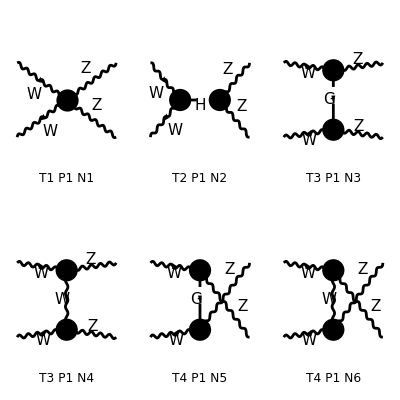

```mathematica
Process={V[3],-V[3]}-> {V[2],V[2]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 6 Particles amplitudes

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

1/(CW2^2 MW2^2 MZ2^2 SW2^2)Alfa2 π^2 (16 ((3 MW2^6+2 (15 MZ2-5 S-2 (2 T+U)) MW2^5+(45 MZ2^2-2 (47 S+22 T+16 U) MZ2+2 (2 S^2+(11 T+3 U) S+(2 T+U)^2)) MW2^4+2 (82 MZ2^3-2 (15 S-8 T+10 U) MZ2^2+(13 S^2+58 T S+16 U S+9 T^2+3 U^2+16 T U) MZ2-T (4 S^2+(7 T+5 U) S+2 (T^2+U T+U^2))) MW2^3+(45 MZ2^4-4 (S-22 T+16 U) MZ2^3+2 (3 S^2-8 T S+6 U S-25 T^2+3 U^2+12 T U) MZ2^2-2 T (14 S^2+7 (T+U) S+2 (T^2-2 U T+2 U^2)) MZ2+T^2 (4 S^2+2 (T+U) S+T^2+2 U^2)) MW2^2-2 (MZ2-T) (17 MZ2^4-(19 S+19 T+6 U) MZ2^3+(9 S^2+23 T S+8 U S+2 T^2-U^2+10 T U) MZ2^2+T (S^2-4 T S-9 U S+U^2-4 T U) MZ2+S T^2 U) MW2+MZ2 (MZ2-T)^2 (3 MZ2^3+2 (S-3 T) MZ2^2-2 S^2 MZ2+3 T^2 MZ2-2 S (T+U) MZ2+2 S T U)) (Den(T,MW2))^2+2 ((333 MZ2^2+4 S^2-2 S (T+U)+3 (T^2+4 U T+U^2)) MW2^4-4 MZ2^2 (112 S+41 (T+U)) MW2^3+4 MZ2^3 (129 MW2-84 S-25 (T+U)) MW2^2+46 MZ2 (MW2^4+MZ2^4) MW2-((4 S^3+4 (T+U) S^2-4 (T-U)^2 S+6 T U (T+U)) MW2^2-(S^4+2 (T+U) S^3-(T^2-6 U T+U^2) S^2-2 (T^3-2 U T^2-2 U^2 T+U^3) S+3 T^2 U^2) MW2+2 S T^2 U^2) MW2-2 MZ2 ((25 S+27 (T+U)) MW2^3+MZ2 (5 S^3+6 (T+U) S^2+(-3 T^2+16 U T-3 U^2) S-2 T^3-2 U^3+3 T U^2+3 T^2 U+MZ2^2 (S+27 (T+U)))) MW2+3 (MW2^6+MZ2^6)+MZ2^4 (205 MW2^2-2 S^2-4 S (T+U)+3 (T^2+4 U T+U^2))+MZ2^2 (S^4+(T+U) S^3-(T^2+U^2) S^2-(T+U)^3 S+3 T^2 U^2+MZ2 (-S^3+2 (T+U) S^2+3 (T+U)^2 S-6 T U (T+U)))+2 ((S-3 (T+U)) MW2^5+MZ2 (31 S^2+25 (T+U) S-2 (T^2-20 U T+U^2)) MW2^3+MZ2^2 (75 S^2+79 (T+U) S-15 T^2-15 U^2+52 T U) MW2^2+MZ2^3 (9 S^2+3 (T+U) S+2 (T^2+16 U T+U^2)) MW2+MZ2^5 (S-3 (T+U)))-MZ2 ((17 S^3+30 (T+U) S^2+(-3 T^2+70 U T-3 U^2) S-8 T^3-8 U^3+10 T U^2+10 T^2 U) MW2^2-((T+U) S^3+6 T U S^2-(T^3-7 U T^2-7 U^2 T+U^3) S+2 T U (-2 T^2+U T-2 U^2)) MW2+S T U (S^2-T^2-U^2))) Den(U,MW2) Den(T,MW2)+(3 MW2^6+2 (15 MZ2-5 S-2 (T+2 U)) MW2^5+(45 MZ2^2-2 (47 S+16 T+22 U) MZ2+2 (2 S^2+(3 T+11 U) S+(T+2 U)^2)) MW2^4+2 (82 MZ2^3-2 (15 S+10 T-8 U) MZ2^2+(13 S^2+16 T S+58 U S+3 T^2+9 U^2+16 T U) MZ2-U (4 S^2+(5 T+7 U) S+2 (T^2+U T+U^2))) MW2^3+(45 MZ2^4-4 (S+16 T-22 U) MZ2^3+2 (3 S^2+6 T S-8 U S+3 T^2-25 U^2+12 T U) MZ2^2-2 U (14 S^2+7 (T+U) S+2 (2 T^2-2 U T+U^2)) MZ2+U^2 (4 S^2+2 (T+U) S+2 T^2+U^2)) MW2^2-2 (MZ2-U) (17 MZ2^4-(19 S+6 T+19 U) MZ2^3+(9 S^2+8 T S+23 U S-T^2+2 U^2+10 T U) MZ2^2+U (S^2-9 T S-4 U S+T^2-4 T U) MZ2+S T U^2) MW2+MZ2 (MZ2-U)^2 (3 MZ2^3+2 (S-3 U) MZ2^2-2 S^2 MZ2+3 U^2 MZ2-2 S (T+U) MZ2+2 S T U)) (Den(U,MW2))^2) CW2^4+(8 Den(U,MW2) (2 ((S^3+2 T S^2-(S+T) U^2+T^2 (S-U)) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)-2 U^2 (S+U) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2)) MW2^2-((4 S^2-6 U S-T^2-U^2-4 T U) MW2^2+T^2 (2 S-U) U) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2) MW2-MZ2 (MW2 (13 S^2+8 T S-12 U S-4 T^2-16 U^2+8 T U) (2 CW2^2+MW2 Den(S,MH2))-MZ2 (16 S^2+8 T S+14 U S-5 T^2-21 U^2-24 T U) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)) MW2-2 MZ2 ((5 (S+T)+23 U) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2) MW2^2+((7 S+19 T+25 U) MW2^2+MZ2^2 (9 S-11 T-25 U)) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)+((T+U) S^2+T^2 S-U (2 T^2+U T+U^2)) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)+U^2 (7 S-5 T+U) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2)) MW2+S U (-2 MW2 T^2+MZ2 S (2 T-U)+MW2 U (S+2 U)) (2 CW2^2+MW2 Den(S,MH2))+(2 (6 MZ2-S) MW2^4-(92 MZ2^2-8 (S-T-2 U) MZ2+S (3 S-4 U)) MW2^3+2 (-70 MZ2^3+(26 S+20 (T+U)) MZ2^2+S (S^2+2 T S-U S+T^2-2 U^2)) MW2^2+MZ2^2 (-36 MZ2^2+8 (4 T+5 U) MZ2+15 S^2+4 S (2 T+U)-4 T (T+8 U)) MW2+MZ2^2 S (6 MZ2^2+(S-12 U) MZ2-2 (S^2+T S-3 U^2))) (2 CW2^2+MW2 Den(S,MH2))+(MW2^5+(45 MZ2-2 (2 S+T+U)) MW2^4+158 MZ2^2 MW2^3+MZ2 (86 MZ2^2-10 (3 S+5 T+7 U) MZ2-14 S^2+5 T^2+11 U^2-8 S T+24 S U+22 T U) MW2^2-31 MZ2^4 MW2+MZ2^2 (-3 MZ2^3+2 (S+2 T+4 U) MZ2^2+(2 S^2-4 U S-T^2-7 U^2-10 T U) MZ2-2 S^3+2 S U^2-2 S^2 (T+U)+2 U (T^2+4 U T+U^2))) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)+MZ2 (T U (U (T+2 U)-2 S^2) (CW2^2-((S-U) CW2^2+MW2 SW2^2) Den(T,MW2))-2 MW2 (2 U^3-2 T^2 U+S^2 (T+U)+S (T^2+5 U^2)) (2 CW2^2+MW2 Den(S,MH2)))-(-MW2^5+(4 U-29 MZ2) MW2^4-2 (7 MZ2^2+U (S+3 U)) MW2^3+2 MZ2 (13 MZ2^2+(S+T-5 U) MZ2-U (12 S+T+10 U)) MW2^2+(15 MZ2^4-10 (S+T+3 U) MZ2^3+2 U (-S+10 T+7 U) MZ2^2-U^3 (2 S+U)) MW2+MZ2 (MZ2-U)^2 (3 MZ2^2-2 (S+T+2 U) MZ2+U (2 T+U))) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2))+8 Den(T,MW2) (-4 T (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2) MW2^4+S ((4 T-3 S) MW2^2+2 (S^2-T S+2 U S-2 T^2+U^2) MW2+T (2 T^2+S T-2 U^2)) (2 CW2^2+MW2 Den(S,MH2)) MW2+MZ2^2 ((15 S^2+4 (T+2 U) S-4 U (8 T+U)) (2 CW2^2+MW2 Den(S,MH2))+2 T (S-7 T-10 U) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)) MW2-MZ2 (MW2 (13 S^2-12 T S-16 T^2-4 U^2+8 (S+T) U) (2 CW2^2+MW2 Den(S,MH2))-MZ2 (16 S^2+14 T S+8 U S-21 T^2-5 U^2-24 T U) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2)) MW2+(T (2 (S+3 T) MW2^2-4 T (S+T) MW2+T^2 (2 S+T)) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)-((4 S^2-6 T S-T^2-U^2-4 T U) MW2^2+(2 S-T) T U^2) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2)) MW2-MZ2 (MW2 (14 S^2+8 (U-3 T) S-11 T^2-5 U^2-22 T U) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2)+2 ((2 T^3+5 S T^2+(S-2 T) U^2+S^2 (T+U)) (2 CW2^2+MW2 Den(S,MH2))+((T+U) S^2+U^2 S-T (T^2+U T+2 U^2)) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2))) MW2+(2 (6 MZ2-S) MW2^4-4 MZ2 (23 MZ2-2 S+4 T+2 U) MW2^3+4 MZ2^2 (-35 MZ2+13 S+10 (T+U)) MW2^2+4 MZ2^3 (-9 MZ2+10 T+8 U) MW2+MZ2^3 S (6 MZ2+S-12 T)) (2 CW2^2+MW2 Den(S,MH2))+(MW2^5+29 MZ2 MW2^4+2 MZ2 (7 MZ2-5 S-23 T-5 U) MW2^3+(2 MZ2 T (12 S+10 T+U)-26 MZ2^3) MW2^2+(-15 MZ2^4+10 (S+3 T+U) MZ2^3-2 T^2 (7 S+T-5 U) MZ2) MW2+MZ2^4 (2 (S+5 T+U)-3 MZ2)) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)+(MW2^5+45 MZ2 MW2^4+2 MZ2 (79 MZ2-7 S-25 T-19 U) MW2^3+2 (43 MZ2^3-5 (3 S+7 T+5 U) MZ2^2+S^3+2 S^2 U-T U (T+U)+S (U^2-T^2)) MW2^2+MZ2^3 (-31 MZ2-18 S+50 T+22 U) MW2+MZ2 (-3 MZ2^4+2 (S+4 T+2 U) MZ2^3-2 (S^3+(T+U) S^2-T^2 S-T (T^2+4 U T+U^2)) MZ2-T U (T (2 T+U)-2 S^2))) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2)-2 ((2 S+T+U) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2) MW2^4+MZ2^2 ((S-5 T+U) MW2^2+MZ2 T (2 S+6 T+3 U)) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2))-MZ2 (-((2 S^2-4 T S-7 T^2-U^2-10 T U) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2) MZ2^2)+S (S T (T-2 U)+2 MZ2 (S^2+U S-3 T^2)) (2 CW2^2+MW2 Den(S,MH2))+T^2 (T (T+2 U)-2 MZ2 (S+3 (T+U))) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)))) CW2^2+(12 MW2^2-4 S MW2+S^2) (12 MZ2^2-4 S MZ2+S^2) (2 CW2^2+MW2 Den(S,MH2))^2-T (-T^3+4 MZ2 T^2-2 (14 MW2 MZ2+3 (MW2^2+MZ2^2)) T+4 (MW2^3+11 MZ2 (MW2+MZ2) MW2+MZ2^3)) (CW2^2-((S-U) CW2^2+MW2 SW2^2) Den(T,MW2))^2+U^4 (CW2^2-((S-T) CW2^2+MW2 SW2^2) Den(U,MW2))^2-2 U (2 (MW2+MZ2) U^2-(14 MW2 MZ2+3 (MW2^2+MZ2^2)) U+2 (MW2^3+11 MZ2 (MW2+MZ2) MW2+MZ2^3)) (CW2^2-((S-T) CW2^2+MW2 SW2^2) Den(U,MW2))^2+2 S^2 T^2 (2 CW2^2+MW2 Den(S,MH2)) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)+2 (((2 CW2^2+MW2 Den(S,MH2)) S^2+T^2 (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)) U^2+(MW2^4+102 MZ2^2 MW2^2+36 MZ2 (MW2^2+MZ2^2) MW2+MZ2^4-2 (MW2+MZ2) (T U (2 S+T+U)+MW2 MZ2 (14 S+19 (T+U)))) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2)+(MW2^2+10 MZ2 MW2+MZ2^2)^2 ((CW2^2-((S-U) CW2^2+MW2 SW2^2) Den(T,MW2))^2+(CW2^2-((S-T) CW2^2+MW2 SW2^2) Den(U,MW2))^2)-4 MW2 (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2) ((((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2) T^3+MW2^2 (2 S+T+U) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2))-2 (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2) (2 (MW2+MZ2) (S T (S+T+2 U)+MW2 MZ2 (17 S+20 T+16 U)) (2 CW2^2+MW2 Den(S,MH2))+(2 (2 S+T+U) MZ2^3-2 MW2 (5 T^2+12 U T+5 U^2+4 S (T+U)) MZ2-(MW2^2+MZ2^2) (T^2+U^2+4 (S+T) (S+U))) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2))-2 (2 CW2^2+MW2 Den(S,MH2)) (2 (MW2+MZ2) (S U (S+2 T+U)+MW2 MZ2 (17 S+16 T+20 U)) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2)-2 (3 (6 MZ2-S) MW2^3+52 MZ2^2 MW2^2+18 MZ2^3 MW2-3 MZ2^3 S) (-2 CW2^2+((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)+((S-T) CW2^2+MW2 SW2^2) Den(U,MW2))-(MW2^2+MZ2^2) (S (5 S+8 T+4 U) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)+S (5 S+4 T+8 U) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2))-2 MW2 MZ2 ((S^2+4 (2 T+U) S+6 T^2+4 U^2+8 T U) (((S-U) CW2^2+MW2 SW2^2) Den(T,MW2)-CW2^2)+(S^2+6 U^2+4 T (S+T)+8 (S+T) U) (((S-T) CW2^2+MW2 SW2^2) Den(U,MW2)-CW2^2))))

```mathematica
resFCWWZZ=square1/.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y)}
```

1/(16 cw^4 MW2^2 MZ2^2 sw^4)ee^4 (16 (1/(U-MW2)^2(3 MW2^6+2 (15 MZ2-5 S-2 (T+2 U)) MW2^5+(45 MZ2^2-2 (47 S+16 T+22 U) MZ2+2 (2 S^2+(3 T+11 U) S+(T+2 U)^2)) MW2^4+2 (82 MZ2^3-2 (15 S+10 T-8 U) MZ2^2+(13 S^2+16 T S+58 U S+3 T^2+9 U^2+16 T U) MZ2-U (4 S^2+(5 T+7 U) S+2 (T^2+U T+U^2))) MW2^3+(45 MZ2^4-4 (S+16 T-22 U) MZ2^3+2 (3 S^2+6 T S-8 U S+3 T^2-25 U^2+12 T U) MZ2^2-2 U (14 S^2+7 (T+U) S+2 (2 T^2-2 U T+U^2)) MZ2+U^2 (4 S^2+2 (T+U) S+2 T^2+U^2)) MW2^2-2 (MZ2-U) (17 MZ2^4-(19 S+6 T+19 U) MZ2^3+(9 S^2+8 T S+23 U S-T^2+2 U^2+10 T U) MZ2^2+U (S^2-9 T S-4 U S+T^2-4 T U) MZ2+S T U^2) MW2+MZ2 (MZ2-U)^2 (3 MZ2^3+2 (S-3 U) MZ2^2-2 S^2 MZ2+3 U^2 MZ2-2 S (T+U) MZ2+2 S T U))+1/(T-MW2)^2(3 MW2^6+2 (15 MZ2-5 S-2 (2 T+U)) MW2^5+(45 MZ2^2-2 (47 S+22 T+16 U) MZ2+2 (2 S^2+(11 T+3 U) S+(2 T+U)^2)) MW2^4+2 (82 MZ2^3-2 (15 S-8 T+10 U) MZ2^2+(13 S^2+58 T S+16 U S+9 T^2+3 U^2+16 T U) MZ2-T (4 S^2+(7 T+5 U) S+2 (T^2+U T+U^2))) MW2^3+(45 MZ2^4-4 (S-22 T+16 U) MZ2^3+2 (3 S^2-8 T S+6 U S-25 T^2+3 U^2+12 T U) MZ2^2-2 T (14 S^2+7 (T+U) S+2 (T^2-2 U T+2 U^2)) MZ2+T^2 (4 S^2+2 (T+U) S+T^2+2 U^2)) MW2^2-2 (MZ2-T) (17 MZ2^4-(19 S+19 T+6 U) MZ2^3+(9 S^2+23 T S+8 U S+2 T^2-U^2+10 T U) MZ2^2+T (S^2-4 T S-9 U S+U^2-4 T U) MZ2+S T^2 U) MW2+MZ2 (MZ2-T)^2 (3 MZ2^3+2 (S-3 T) MZ2^2-2 S^2 MZ2+3 T^2 MZ2-2 S (T+U) MZ2+2 S T U))+1/((T-MW2) (U-MW2))2 ((333 MZ2^2+4 S^2-2 S (T+U)+3 (T^2+4 U T+U^2)) MW2^4-4 MZ2^2 (112 S+41 (T+U)) MW2^3+4 MZ2^3 (129 MW2-84 S-25 (T+U)) MW2^2+46 MZ2 (MW2^4+MZ2^4) MW2-((4 S^3+4 (T+U) S^2-4 (T-U)^2 S+6 T U (T+U)) MW2^2-(S^4+2 (T+U) S^3-(T^2-6 U T+U^2) S^2-2 (T^3-2 U T^2-2 U^2 T+U^3) S+3 T^2 U^2) MW2+2 S T^2 U^2) MW2-2 MZ2 ((25 S+27 (T+U)) MW2^3+MZ2 (5 S^3+6 (T+U) S^2+(-3 T^2+16 U T-3 U^2) S-2 T^3-2 U^3+3 T U^2+3 T^2 U+MZ2^2 (S+27 (T+U)))) MW2+3 (MW2^6+MZ2^6)+MZ2^4 (205 MW2^2-2 S^2-4 S (T+U)+3 (T^2+4 U T+U^2))+MZ2^2 (S^4+(T+U) S^3-(T^2+U^2) S^2-(T+U)^3 S+3 T^2 U^2+MZ2 (-S^3+2 (T+U) S^2+3 (T+U)^2 S-6 T U (T+U)))+2 ((S-3 (T+U)) MW2^5+MZ2 (31 S^2+25 (T+U) S-2 (T^2-20 U T+U^2)) MW2^3+MZ2^2 (75 S^2+79 (T+U) S-15 T^2-15 U^2+52 T U) MW2^2+MZ2^3 (9 S^2+3 (T+U) S+2 (T^2+16 U T+U^2)) MW2+MZ2^5 (S-3 (T+U)))-MZ2 ((17 S^3+30 (T+U) S^2+(-3 T^2+70 U T-3 U^2) S-8 T^3-8 U^3+10 T U^2+10 T^2 U) MW2^2-((T+U) S^3+6 T U S^2-(T^3-7 U T^2-7 U^2 T+U^3) S+2 T U (-2 T^2+U T-2 U^2)) MW2+S T U (S^2-T^2-U^2)))) cw^8+(1/(U-MW2)8 (2 ((((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) (S^3+2 T S^2-(S+T) U^2+T^2 (S-U))-2 U^2 (S+U) (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4)) MW2^2-MZ2 (MW2 (2 cw^4+MW2/(S-MH2)) (13 S^2+8 T S-12 U S-4 T^2-16 U^2+8 T U)-MZ2 (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) (16 S^2+8 T S+14 U S-5 T^2-21 U^2-24 T U)) MW2-(((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) ((4 S^2-6 U S-T^2-U^2-4 T U) MW2^2+T^2 (2 S-U) U) MW2-2 MZ2 ((5 (S+T)+23 U) (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) MW2^2+U^2 (7 S-5 T+U) (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4)+(((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) ((7 S+19 T+25 U) MW2^2+MZ2^2 (9 S-11 T-25 U))+(((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) ((T+U) S^2+T^2 S-U (2 T^2+U T+U^2))) MW2+S (2 cw^4+MW2/(S-MH2)) U (-2 MW2 T^2+MZ2 S (2 T-U)+MW2 U (S+2 U))-(((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) (-MW2^5+(4 U-29 MZ2) MW2^4-2 (7 MZ2^2+U (S+3 U)) MW2^3+2 MZ2 (13 MZ2^2+(S+T-5 U) MZ2-U (12 S+T+10 U)) MW2^2+(15 MZ2^4-10 (S+T+3 U) MZ2^3+2 U (-S+10 T+7 U) MZ2^2-U^3 (2 S+U)) MW2+MZ2 (MZ2-U)^2 (3 MZ2^2-2 (S+T+2 U) MZ2+U (2 T+U)))+(((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) (MW2^5+(45 MZ2-2 (2 S+T+U)) MW2^4+158 MZ2^2 MW2^3+MZ2 (86 MZ2^2-10 (3 S+5 T+7 U) MZ2-14 S^2+5 T^2+11 U^2-8 S T+24 S U+22 T U) MW2^2-31 MZ2^4 MW2+MZ2^2 (-3 MZ2^3+2 (S+2 T+4 U) MZ2^2+(2 S^2-4 U S-T^2-7 U^2-10 T U) MZ2-2 S^3+2 S U^2-2 S^2 (T+U)+2 U (T^2+4 U T+U^2)))+MZ2 (T (cw^4-((S-U) cw^4+MW2 sw^4)/(T-MW2)) U (U (T+2 U)-2 S^2)-2 MW2 (2 cw^4+MW2/(S-MH2)) (2 U^3-2 T^2 U+S^2 (T+U)+S (T^2+5 U^2)))+(2 cw^4+MW2/(S-MH2)) (2 (6 MZ2-S) MW2^4-(92 MZ2^2-8 (S-T-2 U) MZ2+S (3 S-4 U)) MW2^3+2 (-70 MZ2^3+(26 S+20 (T+U)) MZ2^2+S (S^2+2 T S-U S+T^2-2 U^2)) MW2^2+MZ2^2 (-36 MZ2^2+8 (4 T+5 U) MZ2+15 S^2+4 S (2 T+U)-4 T (T+8 U)) MW2+MZ2^2 S (6 MZ2^2+(S-12 U) MZ2-2 (S^2+T S-3 U^2))))+1/(T-MW2)8 (-4 T (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) MW2^4+S (2 cw^4+MW2/(S-MH2)) ((4 T-3 S) MW2^2+2 (S^2-T S+2 U S-2 T^2+U^2) MW2+T (2 T^2+S T-2 U^2)) MW2-MZ2 (MW2 (2 cw^4+MW2/(S-MH2)) (13 S^2-12 T S-16 T^2-4 U^2+8 (S+T) U)-MZ2 (16 S^2+14 T S+8 U S-21 T^2-5 U^2-24 T U) (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4)) MW2+MZ2^2 (2 T (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) (S-7 T-10 U)+(2 cw^4+MW2/(S-MH2)) (15 S^2+4 (T+2 U) S-4 U (8 T+U))) MW2+(T (2 (S+3 T) MW2^2-4 T (S+T) MW2+T^2 (2 S+T)) (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4)-(((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) ((4 S^2-6 T S-T^2-U^2-4 T U) MW2^2+(2 S-T) T U^2)) MW2-MZ2 (MW2 (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) (14 S^2+8 (U-3 T) S-11 T^2-5 U^2-22 T U)+2 ((2 cw^4+MW2/(S-MH2)) (2 T^3+5 S T^2+(S-2 T) U^2+S^2 (T+U))+(((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) ((T+U) S^2+U^2 S-T (T^2+U T+2 U^2)))) MW2+(2 cw^4+MW2/(S-MH2)) (2 (6 MZ2-S) MW2^4-4 MZ2 (23 MZ2-2 S+4 T+2 U) MW2^3+4 MZ2^2 (-35 MZ2+13 S+10 (T+U)) MW2^2+4 MZ2^3 (-9 MZ2+10 T+8 U) MW2+MZ2^3 S (6 MZ2+S-12 T))+(((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) (MW2^5+29 MZ2 MW2^4+2 MZ2 (7 MZ2-5 S-23 T-5 U) MW2^3+(2 MZ2 T (12 S+10 T+U)-26 MZ2^3) MW2^2+(-15 MZ2^4+10 (S+3 T+U) MZ2^3-2 T^2 (7 S+T-5 U) MZ2) MW2+MZ2^4 (2 (S+5 T+U)-3 MZ2))-2 ((2 S+T+U) (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) MW2^4+MZ2^2 (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) ((S-5 T+U) MW2^2+MZ2 T (2 S+6 T+3 U)))-MZ2 (-((2 S^2-4 T S-7 T^2-U^2-10 T U) (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) MZ2^2)+S (2 cw^4+MW2/(S-MH2)) (S T (T-2 U)+2 MZ2 (S^2+U S-3 T^2))+T^2 (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) (T (T+2 U)-2 MZ2 (S+3 (T+U))))+(((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) (MW2^5+45 MZ2 MW2^4+2 MZ2 (79 MZ2-7 S-25 T-19 U) MW2^3+2 (43 MZ2^3-5 (3 S+7 T+5 U) MZ2^2+S^3+2 S^2 U-T U (T+U)+S (U^2-T^2)) MW2^2+MZ2^3 (-31 MZ2-18 S+50 T+22 U) MW2+MZ2 (-3 MZ2^4+2 (S+4 T+2 U) MZ2^3-2 (S^3+(T+U) S^2-T^2 S-T (T^2+4 U T+U^2)) MZ2-T U (T (2 T+U)-2 S^2))))) cw^4+(12 MW2^2-4 S MW2+S^2) (12 MZ2^2-4 S MZ2+S^2) (2 cw^4+MW2/(S-MH2))^2-T (-T^3+4 MZ2 T^2-2 (14 MW2 MZ2+3 (MW2^2+MZ2^2)) T+4 (MW2^3+11 MZ2 (MW2+MZ2) MW2+MZ2^3)) (cw^4-((S-U) cw^4+MW2 sw^4)/(T-MW2))^2+U^4 (cw^4-((S-T) cw^4+MW2 sw^4)/(U-MW2))^2-2 U (2 (MW2+MZ2) U^2-(14 MW2 MZ2+3 (MW2^2+MZ2^2)) U+2 (MW2^3+11 MZ2 (MW2+MZ2) MW2+MZ2^3)) (cw^4-((S-T) cw^4+MW2 sw^4)/(U-MW2))^2+2 S^2 (2 cw^4+MW2/(S-MH2)) T^2 (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4)+(MW2^2+10 MZ2 MW2+MZ2^2)^2 ((cw^4-((S-U) cw^4+MW2 sw^4)/(T-MW2))^2+(cw^4-((S-T) cw^4+MW2 sw^4)/(U-MW2))^2)-4 MW2 (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) ((((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) T^3+MW2^2 (2 S+T+U) (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4))-2 (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) (2 (MW2+MZ2) (2 cw^4+MW2/(S-MH2)) (S T (S+T+2 U)+MW2 MZ2 (17 S+20 T+16 U))+(((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) (2 (2 S+T+U) MZ2^3-2 MW2 (5 T^2+12 U T+5 U^2+4 S (T+U)) MZ2-(MW2^2+MZ2^2) (T^2+U^2+4 (S+T) (S+U))))-2 (2 cw^4+MW2/(S-MH2)) (-2 (3 (6 MZ2-S) MW2^3+52 MZ2^2 MW2^2+18 MZ2^3 MW2-3 MZ2^3 S) (-2 cw^4+((S-U) cw^4+MW2 sw^4)/(T-MW2)+((S-T) cw^4+MW2 sw^4)/(U-MW2))+2 (MW2+MZ2) (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) (S U (S+2 T+U)+MW2 MZ2 (17 S+16 T+20 U))-(MW2^2+MZ2^2) (S (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) (5 S+8 T+4 U)+S (5 S+4 T+8 U) (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4))-2 MW2 MZ2 ((S^2+6 U^2+4 T (S+T)+8 (S+T) U) (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4)+(((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) (S^2+4 (2 T+U) S+6 T^2+4 U^2+8 T U)))+2 (((S-T) cw^4+MW2 sw^4)/(U-MW2)-cw^4) (((2 cw^4+MW2/(S-MH2)) S^2+T^2 (((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4)) U^2+(((S-U) cw^4+MW2 sw^4)/(T-MW2)-cw^4) (MW2^4+102 MZ2^2 MW2^2+36 MZ2 (MW2^2+MZ2^2) MW2+MZ2^4-2 (MW2+MZ2) (T U (2 S+T+U)+MW2 MZ2 (14 S+19 (T+U))))))

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARWWZZ=Get["resANATARWWZZ.m"];
```

```mathematica
FullSimplify[resANATARWWZZ-resFCWWZZ,{(S+T+U)==(2MW2+2MZ2),cw^2+sw^2==1}]
```

0

## ZZ -> ZZ

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AZZZZ=GenerateAmplitude[{Z,Z}->{Z,Z},OutputName->"ZZZZ",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ZZZZ.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/ZZZZ/ZZZZ_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {Z, Z} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{Z(p1),Z(p2)}→{Z(p3),Z(p4)}},Total→3,Name→ZZZZ,LoopOrder→0,Kinematics→{p1^2→MZ^2,p1.p1→MZ^2,1/(p1.p1)→1/MZ^2,p2^2→MZ^2,p2.p2→MZ^2,1/(p2.p2)→1/MZ^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MZ^2),p1.p3→1/2 (2 MZ^2-T),p2.p3→1/2 (2 MZ^2-U),1/(p1.p2)→2/(S-2 MZ^2),1/(p1.p3)→2/(2 MZ^2-T),1/(p2.p3)→2/(2 MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC70^2 Den(-p1-p2,MH) ε_Lor3(p1,MZ) ε_Lor3(p2,MZ) ε_Lor4(p3,MZ) ε_Lor4(p4,MZ),DiagramID(2)→-ⅈ GC70^2 Den(p3-p1,MH) ε_Lor2(p1,MZ) ε_Lor2(p3,MZ) ε_Lor4(p2,MZ) ε_Lor4(p4,MZ),DiagramID(3)→-ⅈ GC70^2 Den(p4-p1,MH) ε_Lor3(p2,MZ) ε_Lor3(p3,MZ) ε_Lor4(p1,MZ) ε_Lor4(p4,MZ)}|>

```mathematica
AZZZZC=GenerateAmplitudeConjugate[{Z,Z}->{Z,Z},OutputName->"ZZZZ",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_ZZZZ.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/ZZZZ/ZZZZ_0

Computing amplitudes...

A total of 3 diagrams have been generated for the process {Z, Z} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{Z(p1),Z(p2)}→{Z(p3),Z(p4)}},Total→3,Name→ZZZZ,LoopOrder→0,Kinematics→{p1^2→MZ^2,p1.p1→MZ^2,1/(p1.p1)→1/MZ^2,p2^2→MZ^2,p2.p2→MZ^2,1/(p2.p2)→1/MZ^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MZ^2),p1.p3→1/2 (2 MZ^2-T),p2.p3→1/2 (2 MZ^2-U),1/(p1.p2)→2/(S-2 MZ^2),1/(p1.p3)→2/(2 MZ^2-T),1/(p2.p3)→2/(2 MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC70^2 Den(-p1-p2,MH) (ε^†)_LorC3^(p1,MZ) (ε^†)_LorC3^(p2,MZ) (ε^†)_LorC4^(p3,MZ) (ε^†)_LorC4^(p4,MZ),DiagramID(2)→ⅈ GC70^2 Den(p3-p1,MH) (ε^†)_LorC2^(p1,MZ) (ε^†)_LorC2^(p3,MZ) (ε^†)_LorC4^(p2,MZ) (ε^†)_LorC4^(p4,MZ),DiagramID(3)→ⅈ GC70^2 Den(p4-p1,MH) (ε^†)_LorC3^(p2,MZ) (ε^†)_LorC3^(p3,MZ) (ε^†)_LorC4^(p1,MZ) (ε^†)_LorC4^(p4,MZ)}|>

```mathematica
AmpSQZZZZ=GenerateAmplitudeSquare[AZZZZ,AZZZZC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{Z(p1),Z(p2)}→{Z(p3),Z(p4)}},Name→ZZZZ,LoopOrder→0,Kinematics→{p1^2→MZ^2,p1.p1→MZ^2,1/(p1.p1)→1/MZ^2,p2^2→MZ^2,p2.p2→MZ^2,1/(p2.p2)→1/MZ^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MZ^2),p1.p3→1/2 (2 MZ^2-T),p2.p3→1/2 (2 MZ^2-U),1/(p1.p2)→2/(S-2 MZ^2),1/(p1.p3)→2/(2 MZ^2-T),1/(p2.p3)→2/(2 MZ^2-U),p4→p1+p2-p3},Amplitudes→1/(256 cw^8 MZ^8 sw2^4)ee^8 vev^4 (cw^2+sw2)^8 ((12 MZ^4-4 MZ^2 S+S^2) (12 MZ^4-4 MZ^2 (T+U)+(T+U)^2) (Den(-p1-p2,MH))^2+(12 MZ^4-4 MZ^2 T+T^2) (12 MZ^4-4 MZ^2 (S+U)+(S+U)^2) (Den(p3-p1,MH))^2+(12 MZ^4-4 MZ^2 U+U^2) (12 MZ^4-4 MZ^2 (S+T)+(S+T)^2) (Den(p2-p3,MH))^2+2 (176 MZ^8-112 MZ^6 (S+T+U)+4 MZ^4 (7 S^2+11 S (T+U)+7 T^2+12 T U+7 U^2)-2 MZ^2 (S^3+2 S^2 (T+U)+2 S (T^2+4 T U+U^2)+(T+U)^3)+T U (S+T) (S+U)) Den(p3-p1,MH) Den(p2-p3,MH)+2 Den(-p1-p2,MH) ((176 MZ^8-112 MZ^6 (S+T+U)+4 MZ^4 (7 S^2+12 S T+11 S U+7 T^2+11 T U+7 U^2)-2 MZ^2 (S^3+S^2 (3 T+2 U)+S (3 T^2+8 T U+2 U^2)+T^3+2 T^2 U+2 T U^2+U^3)+S T (S+U) (T+U)) Den(p3-p1,MH)+(176 MZ^8-112 MZ^6 (S+T+U)+4 MZ^4 (7 S^2+11 S T+12 S U+7 T^2+11 T U+7 U^2)-2 MZ^2 (S^3+S^2 (2 T+3 U)+S (2 T^2+8 T U+3 U^2)+T^3+2 T^2 U+2 T U^2+U^3)+S U (S+T) (T+U)) Den(p2-p3,MH)))|>

```mathematica
resANATARZZZZ=AmpSQZZZZ[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(-p1-p2)^2->S,-p1+p3->√T,p1-p3->√T,(p1-p3)^2->T,(p3-p2)^2->U,(p2-p3)^2->U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/(16 cw^8 MZ^8 sw^4)ee^4 MW^4 (cw^2+sw^2)^8 (((12 MZ^4-4 MZ^2 S+S^2) (12 MZ^4-4 MZ^2 (T+U)+(T+U)^2))/((S-MH^2)^2)+((12 MZ^4-4 MZ^2 T+T^2) (12 MZ^4-4 MZ^2 (S+U)+(S+U)^2))/((T-MH^2)^2)+((12 MZ^4-4 MZ^2 U+U^2) (12 MZ^4-4 MZ^2 (S+T)+(S+T)^2))/((U-MH^2)^2)+(2 (176 MZ^8-112 MZ^6 (S+T+U)+4 MZ^4 (7 S^2+11 S (T+U)+7 T^2+12 T U+7 U^2)-2 MZ^2 (S^3+2 S^2 (T+U)+2 S (T^2+4 T U+U^2)+(T+U)^3)+T U (S+T) (S+U)))/((T-MH^2) (U-MH^2))+1/(S-MH^2)2 ((176 MZ^8-112 MZ^6 (S+T+U)+4 MZ^4 (7 S^2+12 S T+11 S U+7 T^2+11 T U+7 U^2)-2 MZ^2 (S^3+S^2 (3 T+2 U)+S (3 T^2+8 T U+2 U^2)+T^3+2 T^2 U+2 T U^2+U^3)+S T (S+U) (T+U))/(T-MH^2)+(176 MZ^8-112 MZ^6 (S+T+U)+4 MZ^4 (7 S^2+11 S T+12 S U+7 T^2+11 T U+7 U^2)-2 MZ^2 (S^3+S^2 (2 T+3 U)+S (2 T^2+8 T U+3 U^2)+T^3+2 T^2 U+2 T U^2+U^3)+S U (S+T) (T+U))/(U-MH^2)))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARZZZZ.m",resANATARZZZZ];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 3 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 1 diagram

> Top. 2 aebf/cedf/ef.m, 1 diagram

> Top. 3 aebf/cfde/ef.m, 1 diagram

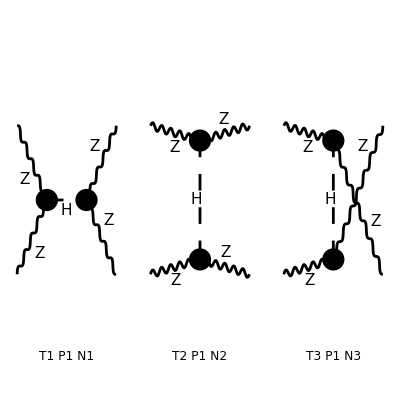

```mathematica
Process={V[2],V[2]}-> {V[2],V[2]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

1/(CW2^4 MZ2^4 SW2^2)π^2 Alfa2 MW2^2 ((12 MZ2^2-4 MZ2 S+S^2)^2 (Den(S,MH2))^2+(12 MZ2^2-4 MZ2 T+T^2)^2 (Den(T,MH2))^2+(12 MZ2^2-4 MZ2 U+U^2)^2 (Den(U,MH2))^2+2 Den(S,MH2) (Den(T,MH2) (-16 MZ2^4+16 MZ2^3 U+4 MZ2^2 (S^2+4 S T+T^2)-4 MZ2 S T (S+T+2 U)+S^2 T^2)+Den(U,MH2) (-16 MZ2^4+16 MZ2^3 T+4 MZ2^2 (S^2+4 S U+U^2)-4 MZ2 S U (S+2 T+U)+S^2 U^2))+2 Den(T,MH2) Den(U,MH2) (-16 MZ2^4+16 MZ2^3 S+4 MZ2^2 (T^2+4 T U+U^2)-4 MZ2 T U (2 S+T+U)+T^2 U^2))

```mathematica
resFCZZZZ=square1/.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y)}//FullSimplify[#,S+T+U==4MZ2]&
```

1/(16 cw^8 MZ2^4 sw^4)ee^4 MW2^2 (((12 MZ2^2-4 MZ2 S+S^2)^2)/(MH2-S)^2+(8 MZ2^2 (4 MZ2 (S-MZ2)+T^2)+2 U^2 (T-2 MZ2)^2-2 T U (S-U) (S+T+U))/((MH2-T) (MH2-U))+((12 MZ2^2-4 MZ2 T+T^2)^2)/(MH2-T)^2+((12 MZ2^2-4 MZ2 U+U^2)^2)/(MH2-U)^2+(2 ((4 MZ2^2 (4 MZ2 (MZ2-T)-S^2)-U^2 (S-2 MZ2)^2+S U (T-U) (S+T+U))/(MH2-U)+(-16 MZ2^4+16 MZ2^3 U+4 MZ2^2 (S^2+4 S T+T^2)-4 MZ2 S T (S+T+2 U)+S^2 T^2)/(T-MH2)))/(S-MH2))

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARZZZZ=Get["resANATARZZZZ.m"];
```

```mathematica
FullSimplify[resANATARZZZZ-resFCZZZZ,{(S+T+U)==(4MZ2),cw^2+sw^2==1}]
```

0

## HH-> ZZ

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AHHZZ=GenerateAmplitude[{H,H}->{Z,Z},OutputName->"HHZZ",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_HHZZ.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/HHZZ/HHZZ_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {H, H} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{H(p1),H(p2)}→{Z(p3),Z(p4)}},Total→6,Name→HHZZ,LoopOrder→0,Kinematics→{p1^2→MH^2,p1.p1→MH^2,1/(p1.p1)→1/MH^2,p2^2→MH^2,p2.p2→MH^2,1/(p2.p2)→1/MH^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MH^2),p1.p3→1/2 (MH^2+MZ^2-T),p2.p3→1/2 (MH^2+MZ^2-U),1/(p1.p2)→2/(S-2 MH^2),1/(p1.p3)→2/(MH^2+MZ^2-T),1/(p2.p3)→2/(MH^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC37 ε_Lor4(p3,MZ) ε_Lor4(p4,MZ),DiagramID(2)→-ⅈ GC46 GC70 Den(-p1-p2,MH) ε_Lor4(p3,MZ) ε_Lor4(p4,MZ),DiagramID(3)→-ⅈ GC17^2 Den(p3-p1,MZ) (2 ε_p1(p3,MZ)-ε_p3(p3,MZ)) (ε_p1(p4,MZ)-ε_p2(p4,MZ)-ε_p3(p4,MZ)),DiagramID(4)→ⅈ GC70^2 Den(p3-p1,MZ) ε_iLor2(p3,MZ) ε_iLor2(p4,MZ),DiagramID(5)→-ⅈ GC17^2 Den(p4-p1,MZ) (2 ε_p1(p4,MZ)-ε_p4(p4,MZ)) (ε_p1(p3,MZ)-ε_p2(p3,MZ)-ε_p4(p3,MZ)),DiagramID(6)→ⅈ GC70^2 Den(p4-p1,MZ) ε_iLor2(p3,MZ) ε_iLor2(p4,MZ)}|>

```mathematica
AHHZZC=GenerateAmplitudeConjugate[{H,H}->{Z,Z},OutputName->"HHZZ",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_HHZZ.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/HHZZ/HHZZ_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {H, H} -> {Z, Z}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{H(p1),H(p2)}→{Z(p3),Z(p4)}},Total→6,Name→HHZZ,LoopOrder→0,Kinematics→{p1^2→MH^2,p1.p1→MH^2,1/(p1.p1)→1/MH^2,p2^2→MH^2,p2.p2→MH^2,1/(p2.p2)→1/MH^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MH^2),p1.p3→1/2 (MH^2+MZ^2-T),p2.p3→1/2 (MH^2+MZ^2-U),1/(p1.p2)→2/(S-2 MH^2),1/(p1.p3)→2/(MH^2+MZ^2-T),1/(p2.p3)→2/(MH^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC37 (ε^†)_LorC4^(p3,MZ) (ε^†)_LorC4^(p4,MZ),DiagramID(2)→ⅈ GC46 GC70 Den(-p1-p2,MH) (ε^†)_LorC4^(p3,MZ) (ε^†)_LorC4^(p4,MZ),DiagramID(3)→ⅈ GC17^2 Den(p3-p1,MZ) (2 (ε^†)_p1^(p3,MZ)-(ε^†)_p3^(p3,MZ)) ((ε^†)_p1^(p4,MZ)-(ε^†)_p2^(p4,MZ)-(ε^†)_p3^(p4,MZ)),DiagramID(4)→-ⅈ GC70^2 Den(p3-p1,MZ) (ε^†)_iLorC2^(p3,MZ) (ε^†)_iLorC2^(p4,MZ),DiagramID(5)→ⅈ GC17^2 Den(p4-p1,MZ) (2 (ε^†)_p1^(p4,MZ)-(ε^†)_p4^(p4,MZ)) ((ε^†)_p1^(p3,MZ)-(ε^†)_p2^(p3,MZ)-(ε^†)_p4^(p3,MZ)),DiagramID(6)→-ⅈ GC70^2 Den(p4-p1,MZ) (ε^†)_iLorC2^(p3,MZ) (ε^†)_iLorC2^(p4,MZ)}|>

```mathematica
AmpSQHHZZ=GenerateAmplitudeSquare[AHHZZ,AHHZZC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{H(p1),H(p2)}→{Z(p3),Z(p4)}},Name→HHZZ,LoopOrder→0,Kinematics→{p1^2→MH^2,p1.p1→MH^2,1/(p1.p1)→1/MH^2,p2^2→MH^2,p2.p2→MH^2,1/(p2.p2)→1/MH^2,p3^2→MZ^2,p3.p3→MZ^2,1/(p3.p3)→1/MZ^2,p4^2→MZ^2,p4.p4→MZ^2,1/(p4.p4)→1/MZ^2,p1.p2→1/2 (S-2 MH^2),p1.p3→1/2 (MH^2+MZ^2-T),p2.p3→1/2 (MH^2+MZ^2-U),1/(p1.p2)→2/(S-2 MH^2),1/(p1.p3)→2/(MH^2+MZ^2-T),1/(p2.p3)→2/(MH^2+MZ^2-U),p4→p1+p2-p3},Amplitudes→1/(64 cw^8 MZ^4 sw2^4)ee^4 (cw^2+sw2)^4 (4 ee^4 MH^4 vev^4 (Den(p3-p1,MZ))^2 cw^8+8 ee^4 MZ^4 vev^4 (Den(p3-p1,MZ))^2 cw^8+ee^4 T^2 vev^4 (Den(p3-p1,MZ))^2 cw^8+ee^4 U^2 vev^4 (Den(p3-p1,MZ))^2 cw^8-4 ee^4 MH^2 T vev^4 (Den(p3-p1,MZ))^2 cw^8-4 ee^4 MH^2 U vev^4 (Den(p3-p1,MZ))^2 cw^8+2 ee^4 T U vev^4 (Den(p3-p1,MZ))^2 cw^8+4 ee^4 sw2 T^2 vev^4 (Den(p3-p1,MZ))^2 cw^6+4 ee^4 sw2 U^2 vev^4 (Den(p3-p1,MZ))^2 cw^6+16 ee^4 MH^4 sw2 vev^4 (Den(p3-p1,MZ))^2 cw^6+32 ee^4 MZ^4 sw2 vev^4 (Den(p3-p1,MZ))^2 cw^6-16 ee^4 MH^2 sw2 T vev^4 (Den(p3-p1,MZ))^2 cw^6-16 ee^4 MH^2 sw2 U vev^4 (Den(p3-p1,MZ))^2 cw^6+8 ee^4 sw2 T U vev^4 (Den(p3-p1,MZ))^2 cw^6-4 ee^2 sw2 T^3 vev^2 (Den(p3-p1,MZ))^2 cw^6+16 ee^2 MH^2 sw2 T^2 vev^2 (Den(p3-p1,MZ))^2 cw^6+16 ee^2 MZ^2 sw2 T^2 vev^2 (Den(p3-p1,MZ))^2 cw^6+8 ee^2 MH^6 sw2 vev^2 (Den(p3-p1,MZ))^2 cw^6-24 ee^2 MH^2 MZ^4 sw2 vev^2 (Den(p3-p1,MZ))^2 cw^6+16 ee^2 MH^4 MZ^2 sw2 vev^2 (Den(p3-p1,MZ))^2 cw^6+8 ee^2 MZ^4 S sw2 vev^2 (Den(p3-p1,MZ))^2 cw^6-8 ee^2 MH^2 MZ^2 S sw2 vev^2 (Den(p3-p1,MZ))^2 cw^6-20 ee^2 MH^4 sw2 T vev^2 (Den(p3-p1,MZ))^2 cw^6-12 ee^2 MZ^4 sw2 T vev^2 (Den(p3-p1,MZ))^2 cw^6-32 ee^2 MH^2 MZ^2 sw2 T vev^2 (Den(p3-p1,MZ))^2 cw^6+8 ee^2 MZ^2 S sw2 T vev^2 (Den(p3-p1,MZ))^2 cw^6-4 ee^2 sw2 T^2 U vev^2 (Den(p3-p1,MZ))^2 cw^6-4 ee^2 MH^4 sw2 U vev^2 (Den(p3-p1,MZ))^2 cw^6+4 ee^2 MZ^4 sw2 U vev^2 (Den(p3-p1,MZ))^2 cw^6+8 ee^2 MH^2 sw2 T U vev^2 (Den(p3-p1,MZ))^2 cw^6+4 ee^2 sw2 T^2 vev^2 Den(p3-p1,MZ) cw^6+4 ee^2 sw2 U^2 vev^2 Den(p3-p1,MZ) cw^6+16 ee^2 MH^4 sw2 vev^2 Den(p3-p1,MZ) cw^6+32 ee^2 MZ^4 sw2 vev^2 Den(p3-p1,MZ) cw^6-16 ee^2 MH^2 sw2 T vev^2 Den(p3-p1,MZ) cw^6-16 ee^2 MH^2 sw2 U vev^2 Den(p3-p1,MZ) cw^6+8 ee^2 sw2 T U vev^2 Den(p3-p1,MZ) cw^6+16 MH^4 sw2^2 cw^4+32 MZ^4 sw2^2 cw^4+4 sw2^2 T^2 cw^4+4 sw2^2 U^2 cw^4+36 MH^4 sw2^2 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) (Den(-p1-p2,MH))^2 cw^4+4 sw2^2 T^4 (Den(p3-p1,MZ))^2 cw^4+24 ee^4 MH^4 sw2^2 vev^4 (Den(p3-p1,MZ))^2 cw^4+48 ee^4 MZ^4 sw2^2 vev^4 (Den(p3-p1,MZ))^2 cw^4+6 ee^4 sw2^2 T^2 vev^4 (Den(p3-p1,MZ))^2 cw^4+6 ee^4 sw2^2 U^2 vev^4 (Den(p3-p1,MZ))^2 cw^4-24 ee^4 MH^2 sw2^2 T vev^4 (Den(p3-p1,MZ))^2 cw^4-24 ee^4 MH^2 sw2^2 U vev^4 (Den(p3-p1,MZ))^2 cw^4+12 ee^4 sw2^2 T U vev^4 (Den(p3-p1,MZ))^2 cw^4-16 MH^2 sw2^2 T^3 (Den(p3-p1,MZ))^2 cw^4-12 MZ^2 sw2^2 T^3 (Den(p3-p1,MZ))^2 cw^4+4 MH^8 sw2^2 (Den(p3-p1,MZ))^2 cw^4-4 MZ^8 sw2^2 (Den(p3-p1,MZ))^2 cw^4-8 MH^2 MZ^6 sw2^2 (Den(p3-p1,MZ))^2 cw^4+32 MH^4 MZ^4 sw2^2 (Den(p3-p1,MZ))^2 cw^4-24 MH^6 MZ^2 sw2^2 (Den(p3-p1,MZ))^2 cw^4+4 MZ^6 S sw2^2 (Den(p3-p1,MZ))^2 cw^4-8 MH^2 MZ^4 S sw2^2 (Den(p3-p1,MZ))^2 cw^4+4 MH^4 MZ^2 S sw2^2 (Den(p3-p1,MZ))^2 cw^4+24 MH^4 sw2^2 T^2 (Den(p3-p1,MZ))^2 cw^4+8 MZ^4 sw2^2 T^2 (Den(p3-p1,MZ))^2 cw^4+4 MZ^2 S sw2^2 T^2 (Den(p3-p1,MZ))^2 cw^4-8 ee^2 sw2^2 T^3 vev^2 (Den(p3-p1,MZ))^2 cw^4+16 ee^2 MH^6 sw2^2 vev^2 (Den(p3-p1,MZ))^2 cw^4-48 ee^2 MH^2 MZ^4 sw2^2 vev^2 (Den(p3-p1,MZ))^2 cw^4+32 ee^2 MH^4 MZ^2 sw2^2 vev^2 (Den(p3-p1,MZ))^2 cw^4+16 ee^2 MZ^4 S sw2^2 vev^2 (Den(p3-p1,MZ))^2 cw^4-16 ee^2 MH^2 MZ^2 S sw2^2 vev^2 (Den(p3-p1,MZ))^2 cw^4+32 ee^2 MH^2 sw2^2 T^2 vev^2 (Den(p3-p1,MZ))^2 cw^4+32 ee^2 MZ^2 sw2^2 T^2 vev^2 (Den(p3-p1,MZ))^2 cw^4-40 ee^2 MH^4 sw2^2 T vev^2 (Den(p3-p1,MZ))^2 cw^4-24 ee^2 MZ^4 sw2^2 T vev^2 (Den(p3-p1,MZ))^2 cw^4-64 ee^2 MH^2 MZ^2 sw2^2 T vev^2 (Den(p3-p1,MZ))^2 cw^4+16 ee^2 MZ^2 S sw2^2 T vev^2 (Den(p3-p1,MZ))^2 cw^4-8 ee^2 MH^4 sw2^2 U vev^2 (Den(p3-p1,MZ))^2 cw^4+8 ee^2 MZ^4 sw2^2 U vev^2 (Den(p3-p1,MZ))^2 cw^4-8 ee^2 sw2^2 T^2 U vev^2 (Den(p3-p1,MZ))^2 cw^4+16 ee^2 MH^2 sw2^2 T U vev^2 (Den(p3-p1,MZ))^2 cw^4-16 MH^6 sw2^2 T (Den(p3-p1,MZ))^2 cw^4+4 MZ^6 sw2^2 T (Den(p3-p1,MZ))^2 cw^4+40 MH^2 MZ^4 sw2^2 T (Den(p3-p1,MZ))^2 cw^4+36 MH^4 MZ^2 sw2^2 T (Den(p3-p1,MZ))^2 cw^4-8 MZ^4 S sw2^2 T (Den(p3-p1,MZ))^2 cw^4-8 MH^2 MZ^2 S sw2^2 T (Den(p3-p1,MZ))^2 cw^4+4 MZ^6 sw2^2 U (Den(p3-p1,MZ))^2 cw^4-8 MH^2 MZ^4 sw2^2 U (Den(p3-p1,MZ))^2 cw^4+4 MH^4 MZ^2 sw2^2 U (Den(p3-p1,MZ))^2 cw^4+4 MZ^2 sw2^2 T^2 U (Den(p3-p1,MZ))^2 cw^4-8 MZ^4 sw2^2 T U (Den(p3-p1,MZ))^2 cw^4-8 MH^2 MZ^2 sw2^2 T U (Den(p3-p1,MZ))^2 cw^4-16 MH^2 sw2^2 T cw^4-16 MH^2 sw2^2 U cw^4+8 sw2^2 T U cw^4-8 sw2^2 T^3 Den(p3-p1,MZ) cw^4+16 MH^6 sw2^2 Den(p3-p1,MZ) cw^4-48 MH^2 MZ^4 sw2^2 Den(p3-p1,MZ) cw^4+32 MH^4 MZ^2 sw2^2 Den(p3-p1,MZ) cw^4+16 MZ^4 S sw2^2 Den(p3-p1,MZ) cw^4-16 MH^2 MZ^2 S sw2^2 Den(p3-p1,MZ) cw^4+32 MH^2 sw2^2 T^2 Den(p3-p1,MZ) cw^4+32 MZ^2 sw2^2 T^2 Den(p3-p1,MZ) cw^4+32 ee^2 MH^4 sw2^2 vev^2 Den(p3-p1,MZ) cw^4+64 ee^2 MZ^4 sw2^2 vev^2 Den(p3-p1,MZ) cw^4+8 ee^2 sw2^2 T^2 vev^2 Den(p3-p1,MZ) cw^4+8 ee^2 sw2^2 U^2 vev^2 Den(p3-p1,MZ) cw^4-32 ee^2 MH^2 sw2^2 T vev^2 Den(p3-p1,MZ) cw^4-32 ee^2 MH^2 sw2^2 U vev^2 Den(p3-p1,MZ) cw^4+16 ee^2 sw2^2 T U vev^2 Den(p3-p1,MZ) cw^4-40 MH^4 sw2^2 T Den(p3-p1,MZ) cw^4-24 MZ^4 sw2^2 T Den(p3-p1,MZ) cw^4-64 MH^2 MZ^2 sw2^2 T Den(p3-p1,MZ) cw^4+16 MZ^2 S sw2^2 T Den(p3-p1,MZ) cw^4-8 MH^4 sw2^2 U Den(p3-p1,MZ) cw^4+8 MZ^4 sw2^2 U Den(p3-p1,MZ) cw^4-8 sw2^2 T^2 U Den(p3-p1,MZ) cw^4+16 MH^2 sw2^2 T U Den(p3-p1,MZ) cw^4+16 ee^4 MH^4 sw2^3 vev^4 (Den(p3-p1,MZ))^2 cw^2+32 ee^4 MZ^4 sw2^3 vev^4 (Den(p3-p1,MZ))^2 cw^2+4 ee^4 sw2^3 T^2 vev^4 (Den(p3-p1,MZ))^2 cw^2+4 ee^4 sw2^3 U^2 vev^4 (Den(p3-p1,MZ))^2 cw^2-16 ee^4 MH^2 sw2^3 T vev^4 (Den(p3-p1,MZ))^2 cw^2-16 ee^4 MH^2 sw2^3 U vev^4 (Den(p3-p1,MZ))^2 cw^2+8 ee^4 sw2^3 T U vev^4 (Den(p3-p1,MZ))^2 cw^2+8 ee^2 MH^6 sw2^3 vev^2 (Den(p3-p1,MZ))^2 cw^2-24 ee^2 MH^2 MZ^4 sw2^3 vev^2 (Den(p3-p1,MZ))^2 cw^2+16 ee^2 MH^4 MZ^2 sw2^3 vev^2 (Den(p3-p1,MZ))^2 cw^2+8 ee^2 MZ^4 S sw2^3 vev^2 (Den(p3-p1,MZ))^2 cw^2-8 ee^2 MH^2 MZ^2 S sw2^3 vev^2 (Den(p3-p1,MZ))^2 cw^2-4 ee^2 sw2^3 T^3 vev^2 (Den(p3-p1,MZ))^2 cw^2+16 ee^2 MH^2 sw2^3 T^2 vev^2 (Den(p3-p1,MZ))^2 cw^2+16 ee^2 MZ^2 sw2^3 T^2 vev^2 (Den(p3-p1,MZ))^2 cw^2-20 ee^2 MH^4 sw2^3 T vev^2 (Den(p3-p1,MZ))^2 cw^2-12 ee^2 MZ^4 sw2^3 T vev^2 (Den(p3-p1,MZ))^2 cw^2-32 ee^2 MH^2 MZ^2 sw2^3 T vev^2 (Den(p3-p1,MZ))^2 cw^2+8 ee^2 MZ^2 S sw2^3 T vev^2 (Den(p3-p1,MZ))^2 cw^2-4 ee^2 MH^4 sw2^3 U vev^2 (Den(p3-p1,MZ))^2 cw^2+4 ee^2 MZ^4 sw2^3 U vev^2 (Den(p3-p1,MZ))^2 cw^2-4 ee^2 sw2^3 T^2 U vev^2 (Den(p3-p1,MZ))^2 cw^2+8 ee^2 MH^2 sw2^3 T U vev^2 (Den(p3-p1,MZ))^2 cw^2+16 ee^2 MH^4 sw2^3 vev^2 Den(p3-p1,MZ) cw^2+32 ee^2 MZ^4 sw2^3 vev^2 Den(p3-p1,MZ) cw^2+4 ee^2 sw2^3 T^2 vev^2 Den(p3-p1,MZ) cw^2+4 ee^2 sw2^3 U^2 vev^2 Den(p3-p1,MZ) cw^2-16 ee^2 MH^2 sw2^3 T vev^2 Den(p3-p1,MZ) cw^2-16 ee^2 MH^2 sw2^3 U vev^2 Den(p3-p1,MZ) cw^2+8 ee^2 sw2^3 T U vev^2 Den(p3-p1,MZ) cw^2+12 MH^2 sw2 Den(-p1-p2,MH) (2 sw2 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) cw^2+(ee^2 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) vev^2 cw^4-2 sw2 (2 MH^6+(4 MZ^2-4 ee^2 vev^2-2 S-3 T-3 U) MH^4+(10 MZ^4-2 (T+3 U) MZ^2+T^2+U^2+4 ee^2 T vev^2+4 ee^2 U vev^2+S T+3 S U+4 T U) MH^2+MZ^2 (-T^2-S T+4 U T+U^2+S U)+MZ^4 (-8 ee^2 vev^2-2 S+T-3 U)-(T+U) (ee^2 T vev^2+ee^2 U vev^2+S U+T U)) cw^2+ee^2 sw2^2 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) vev^2) Den(p2-p3,MZ)+(ee^2 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) vev^2 cw^4+2 sw2 (2 MH^6+(4 MZ^2+4 ee^2 vev^2-5 T-U) MH^4-2 (3 MZ^4+(S+4 T) MZ^2-2 T^2+2 ee^2 T vev^2+2 ee^2 U vev^2-T U) MH^2+2 MZ^2 T (S+2 T)+MZ^4 (8 ee^2 vev^2+2 S-3 T+U)-(T+U) (T^2-ee^2 vev^2 T-ee^2 U vev^2)) cw^2+ee^2 sw2^2 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) vev^2) Den(p3-p1,MZ)) cw^2+(ee^4 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) vev^4 cw^8+4 ee^2 sw2 vev^2 (-2 MH^6+(-4 MZ^2+4 ee^2 vev^2+2 S+3 T+3 U) MH^4-(10 MZ^4-2 (T+3 U) MZ^2+T^2+U^2+4 ee^2 T vev^2+4 ee^2 U vev^2+S T+3 S U+4 T U) MH^2+MZ^2 (T^2+S T-4 U T-U^2-S U)+MZ^4 (8 ee^2 vev^2+2 S-T+3 U)+(T+U) (ee^2 T vev^2+ee^2 U vev^2+S U+T U)) cw^6+2 sw2^2 (2 MH^8-4 (3 MZ^2+2 ee^2 vev^2+S+T+U) MH^6+2 (8 MZ^4+(-8 ee^2 vev^2+7 S+7 T+3 U) MZ^2+6 ee^4 vev^4+S^2+T^2+U^2+6 ee^2 T vev^2+6 ee^2 U vev^2+4 T U+2 S (2 ee^2 vev^2+T+2 U)) MH^4-4 (MZ^6-2 (-5 ee^2 vev^2+2 S+2 T) MZ^4+(3 S^2+6 T S-3 U S+3 T^2+U^2-2 ee^2 T vev^2-6 ee^2 U vev^2-3 T U) MZ^2+3 ee^4 T vev^4+3 ee^4 U vev^4+T U^2+ee^2 T^2 vev^2+ee^2 U^2 vev^2+4 ee^2 T U vev^2+S^2 U+T^2 U+S (U^2+3 ee^2 vev^2 U+2 T U+ee^2 T vev^2)) MH^2-2 MZ^8+3 ee^4 T^2 vev^4+3 ee^4 U^2 vev^4+6 ee^4 T U vev^4+2 S^2 U^2+2 T^2 U^2+4 S T U^2+4 ee^2 S U^2 vev^2+4 ee^2 T U^2 vev^2+4 ee^2 T^2 U vev^2+4 ee^2 S T U vev^2+MZ^6 (6 S+6 T-2 U)+2 MZ^4 (12 ee^4 vev^4+6 ee^2 U vev^2-3 S^2-3 T^2+U^2+2 T (U-ee^2 vev^2)+2 S (2 ee^2 vev^2-3 T+U))+2 MZ^2 (S^3+(3 T-U) S^2+(3 T^2-2 (U-ee^2 vev^2) T-2 U (ee^2 vev^2+U)) S+T^3-2 ee^2 U^2 vev^2-T^2 (U-2 ee^2 vev^2)-2 T U (4 ee^2 vev^2+U))) cw^4+4 ee^2 sw2^3 vev^2 (-2 MH^6+(-4 MZ^2+4 ee^2 vev^2+2 S+3 T+3 U) MH^4-(10 MZ^4-2 (T+3 U) MZ^2+T^2+U^2+4 ee^2 T vev^2+4 ee^2 U vev^2+S T+3 S U+4 T U) MH^2+MZ^2 (T^2+S T-4 U T-U^2-S U)+MZ^4 (8 ee^2 vev^2+2 S-T+3 U)+(T+U) (ee^2 T vev^2+ee^2 U vev^2+S U+T U)) cw^2+ee^4 sw2^4 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) vev^4) (Den(p2-p3,MZ))^2+4 ee^4 MH^4 sw2^4 vev^4 (Den(p3-p1,MZ))^2+8 ee^4 MZ^4 sw2^4 vev^4 (Den(p3-p1,MZ))^2+ee^4 sw2^4 T^2 vev^4 (Den(p3-p1,MZ))^2+ee^4 sw2^4 U^2 vev^4 (Den(p3-p1,MZ))^2-4 ee^4 MH^2 sw2^4 T vev^4 (Den(p3-p1,MZ))^2-4 ee^4 MH^2 sw2^4 U vev^4 (Den(p3-p1,MZ))^2+2 ee^4 sw2^4 T U vev^4 (Den(p3-p1,MZ))^2+2 Den(p2-p3,MZ) (2 sw2 (ee^2 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) vev^2 cw^4-2 sw2 (2 MH^6+(4 MZ^2-4 ee^2 vev^2-2 S-3 T-3 U) MH^4+(10 MZ^4-2 (T+3 U) MZ^2+T^2+U^2+4 ee^2 T vev^2+4 ee^2 U vev^2+S T+3 S U+4 T U) MH^2+MZ^2 (-T^2-S T+4 U T+U^2+S U)+MZ^4 (-8 ee^2 vev^2-2 S+T-3 U)-(T+U) (ee^2 T vev^2+ee^2 U vev^2+S U+T U)) cw^2+ee^2 sw2^2 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) vev^2) cw^2+(ee^4 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) vev^4 cw^8+2 ee^2 sw2 vev^2 (2 (4 ee^2 vev^2+S-T+U) MH^4-(16 MZ^4+2 (S+3 T-3 U) MZ^2-3 T^2+U^2+8 ee^2 T vev^2+8 ee^2 U vev^2+S T+3 S U+2 T U) MH^2+MZ^2 (5 T^2+3 S T-4 U T-U^2-S U)+4 MZ^4 (4 ee^2 vev^2+S-T+U)-(T+U) (T^2-(2 ee^2 vev^2+U) T-U (2 ee^2 vev^2+S))) cw^6-2 sw2^2 (2 MH^8+(8 MZ^2-2 (S+3 T+U)) MH^6-2 (10 MZ^4+(7 S+13 T-U) MZ^2+6 ee^4 vev^4-3 T^2-2 ee^2 T vev^2+2 ee^2 U vev^2-3 T U-S (-2 ee^2 vev^2+2 T+U)) MH^4+2 (4 MZ^6+(16 ee^2 vev^2+9 S-13 T+U) MZ^4+2 (S^2+ee^2 vev^2 S+5 T S+5 T^2+3 ee^2 T vev^2-3 ee^2 U vev^2+T U) MZ^2+6 ee^4 T vev^4+6 ee^4 U vev^4-T^3-3 ee^2 T^2 vev^2+ee^2 U^2 vev^2+2 ee^2 T U vev^2-3 T^2 U+S (-T^2+ee^2 vev^2 T-2 U T+3 ee^2 U vev^2)) MH^2+2 MZ^8-3 ee^4 T^2 vev^4-3 ee^4 U^2 vev^4-6 ee^4 T U vev^4+2 ee^2 T^3 vev^2-2 ee^2 S U^2 vev^2-2 ee^2 T U^2 vev^2-2 ee^2 S T U vev^2+2 T^3 U+2 S T^2 U-2 MZ^6 (S+3 T+U)-2 MZ^4 (12 ee^4 vev^4-4 ee^2 T vev^2+4 ee^2 U vev^2+2 S^2-3 T^2-3 T U+S (4 ee^2 vev^2-4 T+U))-2 MZ^2 (T^3+(5 ee^2 vev^2+3 U) T^2+2 S^2 T-4 ee^2 U vev^2 T-ee^2 U^2 vev^2+S (3 T^2+3 ee^2 vev^2 T-ee^2 U vev^2))) cw^4+2 ee^2 sw2^3 vev^2 (2 (4 ee^2 vev^2+S-T+U) MH^4-(16 MZ^4+2 (S+3 T-3 U) MZ^2-3 T^2+U^2+8 ee^2 T vev^2+8 ee^2 U vev^2+S T+3 S U+2 T U) MH^2+MZ^2 (5 T^2+3 S T-4 U T-U^2-S U)+4 MZ^4 (4 ee^2 vev^2+S-T+U)-(T+U) (T^2-(2 ee^2 vev^2+U) T-U (2 ee^2 vev^2+S))) cw^2+ee^4 sw2^4 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) vev^4) Den(p3-p1,MZ)))|>

```mathematica
resANATARHHZZ=AmpSQHHZZ[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(-p1-p2)^2->S,-p1+p3->√T,p1-p3->√T,(p1-p3)^2->T,(p3-p2)^2->U,(p2-p3)^2->U,SW2->sw^2,CW2->cw^2,sw2->sw^2}//Simplify
```

1/(32 cw^8 MZ^4 sw^4)ee^4 (cw^2+sw^2)^4 ((8 MW^4 T^2 cw^8)/((MZ^2-T)^2)+(8 MW^4 U^2 cw^8)/((MZ^2-T)^2)-(32 MH^2 MW^4 T cw^8)/((MZ^2-T)^2)+(16 MW^4 T U cw^8)/((MZ^2-T)^2)-(32 MH^2 MW^4 U cw^8)/((MZ^2-T)^2)+(32 MH^4 MW^4 cw^8)/((MZ^2-T)^2)+(64 MW^4 MZ^4 cw^8)/((MZ^2-T)^2)-(8 MW^2 T^3 cw^6)/((MZ^2-T)^2)+(32 MH^2 MW^2 T^2 cw^6)/((MZ^2-T)^2)+(32 MW^2 MZ^2 T^2 cw^6)/((MZ^2-T)^2)+(32 MW^4 sw^2 T^2 cw^6)/((MZ^2-T)^2)+(8 MW^2 U^2 cw^6)/(T-MZ^2)+(32 MW^4 sw^2 U^2 cw^6)/((MZ^2-T)^2)+(32 MH^2 MW^2 T cw^6)/(MZ^2-T)-(24 MW^2 MZ^4 T cw^6)/((MZ^2-T)^2)-(40 MH^4 MW^2 T cw^6)/((MZ^2-T)^2)-(64 MH^2 MW^2 MZ^2 T cw^6)/((MZ^2-T)^2)-(128 MH^2 MW^4 sw^2 T cw^6)/((MZ^2-T)^2)+(16 MW^2 MZ^2 S T cw^6)/((MZ^2-T)^2)-(8 MW^2 T^2 U cw^6)/((MZ^2-T)^2)+(16 MH^2 MW^2 T U cw^6)/((MZ^2-T)^2)+(64 MW^4 sw^2 T U cw^6)/((MZ^2-T)^2)+(32 MH^2 MW^2 U cw^6)/(MZ^2-T)+(16 MW^2 T U cw^6)/(T-MZ^2)+(8 MW^2 MZ^4 U cw^6)/((MZ^2-T)^2)-(8 MH^4 MW^2 U cw^6)/((MZ^2-T)^2)-(128 MH^2 MW^4 sw^2 U cw^6)/((MZ^2-T)^2)+(64 MW^2 MZ^4 cw^6)/(T-MZ^2)+(32 MH^4 MW^2 cw^6)/(T-MZ^2)+(8 MW^2 T^2 cw^6)/(T-MZ^2)-(48 MH^2 MW^2 MZ^4 cw^6)/((MZ^2-T)^2)+(16 MH^6 MW^2 cw^6)/((MZ^2-T)^2)+(32 MH^4 MW^2 MZ^2 cw^6)/((MZ^2-T)^2)+(128 MH^4 MW^4 sw^2 cw^6)/((MZ^2-T)^2)+(256 MW^4 MZ^4 sw^2 cw^6)/((MZ^2-T)^2)+(16 MW^2 MZ^4 S cw^6)/((MZ^2-T)^2)-(16 MH^2 MW^2 MZ^2 S cw^6)/((MZ^2-T)^2)+8 MH^4 cw^4+16 MZ^4 cw^4+(2 T^4 cw^4)/((MZ^2-T)^2)+(4 T^3 cw^4)/(MZ^2-T)-(8 MH^2 T^3 cw^4)/((MZ^2-T)^2)-(6 MZ^2 T^3 cw^4)/((MZ^2-T)^2)-(16 MW^2 sw^2 T^3 cw^4)/((MZ^2-T)^2)+(12 MH^4 T^2 cw^4)/((MZ^2-T)^2)+(4 MZ^4 T^2 cw^4)/((MZ^2-T)^2)+(48 MW^4 sw^4 T^2 cw^4)/((MZ^2-T)^2)+(64 MH^2 MW^2 sw^2 T^2 cw^4)/((MZ^2-T)^2)+(64 MW^2 MZ^2 sw^2 T^2 cw^4)/((MZ^2-T)^2)+(2 MZ^2 S T^2 cw^4)/((MZ^2-T)^2)+2 T^2 cw^4+(16 MW^2 sw^2 U^2 cw^4)/(T-MZ^2)+(48 MW^4 sw^4 U^2 cw^4)/((MZ^2-T)^2)+2 U^2 cw^4-8 MH^2 T cw^4+(20 MH^4 T cw^4)/(MZ^2-T)+(12 MZ^4 T cw^4)/(MZ^2-T)+(32 MH^2 MZ^2 T cw^4)/(MZ^2-T)+(64 MH^2 MW^2 sw^2 T cw^4)/(MZ^2-T)-(8 MH^6 T cw^4)/((MZ^2-T)^2)+(2 MZ^6 T cw^4)/((MZ^2-T)^2)+(20 MH^2 MZ^4 T cw^4)/((MZ^2-T)^2)-(192 MH^2 MW^4 sw^4 T cw^4)/((MZ^2-T)^2)+(18 MH^4 MZ^2 T cw^4)/((MZ^2-T)^2)-(48 MW^2 MZ^4 sw^2 T cw^4)/((MZ^2-T)^2)-(80 MH^4 MW^2 sw^2 T cw^4)/((MZ^2-T)^2)-(128 MH^2 MW^2 MZ^2 sw^2 T cw^4)/((MZ^2-T)^2)+(32 MW^2 MZ^2 S sw^2 T cw^4)/((MZ^2-T)^2)-(4 MZ^4 S T cw^4)/((MZ^2-T)^2)-(4 MH^2 MZ^2 S T cw^4)/((MZ^2-T)^2)-8 MH^2 U cw^4+(4 T^2 U cw^4)/(MZ^2-T)+(2 MZ^2 T^2 U cw^4)/((MZ^2-T)^2)-(16 MW^2 sw^2 T^2 U cw^4)/((MZ^2-T)^2)-(4 MZ^4 T U cw^4)/((MZ^2-T)^2)+(96 MW^4 sw^4 T U cw^4)/((MZ^2-T)^2)-(4 MH^2 MZ^2 T U cw^4)/((MZ^2-T)^2)+(32 MH^2 MW^2 sw^2 T U cw^4)/((MZ^2-T)^2)+4 T U cw^4+(4 MH^4 U cw^4)/(MZ^2-T)+(64 MH^2 MW^2 sw^2 U cw^4)/(MZ^2-T)+(4 MZ^4 U cw^4)/(T-MZ^2)+(8 MH^2 T U cw^4)/(T-MZ^2)+(32 MW^2 sw^2 T U cw^4)/(T-MZ^2)+(2 MZ^6 U cw^4)/((MZ^2-T)^2)-(4 MH^2 MZ^4 U cw^4)/((MZ^2-T)^2)-(192 MH^2 MW^4 sw^4 U cw^4)/((MZ^2-T)^2)+(2 MH^4 MZ^2 U cw^4)/((MZ^2-T)^2)+(16 MW^2 MZ^4 sw^2 U cw^4)/((MZ^2-T)^2)-(16 MH^4 MW^2 sw^2 U cw^4)/((MZ^2-T)^2)+(18 MH^4 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) cw^4)/((MH^2-S)^2)+(24 MH^2 MZ^4 cw^4)/(MZ^2-T)+(8 MH^2 MZ^2 S cw^4)/(MZ^2-T)+(8 MH^6 cw^4)/(T-MZ^2)+(16 MH^4 MZ^2 cw^4)/(T-MZ^2)+(128 MW^2 MZ^4 sw^2 cw^4)/(T-MZ^2)+(64 MH^4 MW^2 sw^2 cw^4)/(T-MZ^2)+(16 MH^2 T^2 cw^4)/(T-MZ^2)+(16 MZ^2 T^2 cw^4)/(T-MZ^2)+(16 MW^2 sw^2 T^2 cw^4)/(T-MZ^2)+(8 MZ^4 S cw^4)/(T-MZ^2)+(8 MZ^2 S T cw^4)/(T-MZ^2)+(2 MH^8 cw^4)/((MZ^2-T)^2)-(2 MZ^8 cw^4)/((MZ^2-T)^2)-(4 MH^2 MZ^6 cw^4)/((MZ^2-T)^2)+(16 MH^4 MZ^4 cw^4)/((MZ^2-T)^2)+(192 MH^4 MW^4 sw^4 cw^4)/((MZ^2-T)^2)+(384 MW^4 MZ^4 sw^4 cw^4)/((MZ^2-T)^2)-(12 MH^6 MZ^2 cw^4)/((MZ^2-T)^2)-(96 MH^2 MW^2 MZ^4 sw^2 cw^4)/((MZ^2-T)^2)+(32 MH^6 MW^2 sw^2 cw^4)/((MZ^2-T)^2)+(64 MH^4 MW^2 MZ^2 sw^2 cw^4)/((MZ^2-T)^2)+(32 MW^2 MZ^4 S sw^2 cw^4)/((MZ^2-T)^2)-(32 MH^2 MW^2 MZ^2 S sw^2 cw^4)/((MZ^2-T)^2)+(2 MZ^6 S cw^4)/((MZ^2-T)^2)-(4 MH^2 MZ^4 S cw^4)/((MZ^2-T)^2)+(2 MH^4 MZ^2 S cw^4)/((MZ^2-T)^2)-(8 MW^2 sw^4 T^3 cw^2)/((MZ^2-T)^2)+(32 MW^4 sw^6 T^2 cw^2)/((MZ^2-T)^2)+(32 MH^2 MW^2 sw^4 T^2 cw^2)/((MZ^2-T)^2)+(32 MW^2 MZ^2 sw^4 T^2 cw^2)/((MZ^2-T)^2)+(8 MW^2 sw^4 U^2 cw^2)/(T-MZ^2)+(32 MW^4 sw^6 U^2 cw^2)/((MZ^2-T)^2)+(32 MH^2 MW^2 sw^4 T cw^2)/(MZ^2-T)-(128 MH^2 MW^4 sw^6 T cw^2)/((MZ^2-T)^2)-(24 MW^2 MZ^4 sw^4 T cw^2)/((MZ^2-T)^2)-(40 MH^4 MW^2 sw^4 T cw^2)/((MZ^2-T)^2)-(64 MH^2 MW^2 MZ^2 sw^4 T cw^2)/((MZ^2-T)^2)+(16 MW^2 MZ^2 S sw^4 T cw^2)/((MZ^2-T)^2)-(8 MW^2 sw^4 T^2 U cw^2)/((MZ^2-T)^2)+(64 MW^4 sw^6 T U cw^2)/((MZ^2-T)^2)+(16 MH^2 MW^2 sw^4 T U cw^2)/((MZ^2-T)^2)+(32 MH^2 MW^2 sw^4 U cw^2)/(MZ^2-T)+(16 MW^2 sw^4 T U cw^2)/(T-MZ^2)-(128 MH^2 MW^4 sw^6 U cw^2)/((MZ^2-T)^2)+(8 MW^2 MZ^4 sw^4 U cw^2)/((MZ^2-T)^2)-(8 MH^4 MW^2 sw^4 U cw^2)/((MZ^2-T)^2)+1/(S-MH^2)12 MH^2 ((4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) cw^2+1/(T-MZ^2)(2 MW^2 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) cw^4+(2 MH^6+(4 MZ^2+16 MW^2 sw^2-5 T-U) MH^4-2 (3 MZ^4+(S+4 T) MZ^2+8 MW^2 sw^2 (T+U)-T (2 T+U)) MH^2+2 MZ^2 T (S+2 T)+MZ^4 (32 MW^2 sw^2+2 S-3 T+U)-(T+U) (T^2-4 MW^2 sw^2 (T+U))) cw^2+2 MW^2 sw^4 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2))+1/(U-MZ^2)(2 MW^2 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) cw^4-(2 MH^6+(4 MZ^2-16 MW^2 sw^2-2 S-3 T-3 U) MH^4+(10 MZ^4-2 (T+3 U) MZ^2+T^2+U^2+16 MW^2 sw^2 T+S T+16 MW^2 sw^2 U+3 S U+4 T U) MH^2+MZ^4 (-32 MW^2 sw^2-2 S+T-3 U)+MZ^2 (-T^2+4 U T+U^2+S (U-T))-(T+U) (4 MW^2 (T+U) sw^2+(S+T) U)) cw^2+2 MW^2 sw^4 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2))) cw^2+(64 MW^2 MZ^4 sw^4 cw^2)/(T-MZ^2)+(32 MH^4 MW^2 sw^4 cw^2)/(T-MZ^2)+(8 MW^2 sw^4 T^2 cw^2)/(T-MZ^2)+(128 MH^4 MW^4 sw^6 cw^2)/((MZ^2-T)^2)+(256 MW^4 MZ^4 sw^6 cw^2)/((MZ^2-T)^2)-(48 MH^2 MW^2 MZ^4 sw^4 cw^2)/((MZ^2-T)^2)+(16 MH^6 MW^2 sw^4 cw^2)/((MZ^2-T)^2)+(32 MH^4 MW^2 MZ^2 sw^4 cw^2)/((MZ^2-T)^2)+(16 MW^2 MZ^4 S sw^4 cw^2)/((MZ^2-T)^2)-(16 MH^2 MW^2 MZ^2 S sw^4 cw^2)/((MZ^2-T)^2)+(8 MW^4 sw^8 T^2)/((MZ^2-T)^2)+(8 MW^4 sw^8 U^2)/((MZ^2-T)^2)-(32 MH^2 MW^4 sw^8 T)/((MZ^2-T)^2)+(16 MW^4 sw^8 T U)/((MZ^2-T)^2)-(32 MH^2 MW^4 sw^8 U)/((MZ^2-T)^2)+1/((MZ^2-T) (MZ^2-U))4 (4 MW^4 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) cw^8+2 MW^2 (-8 MZ^6+4 (16 MW^2 sw^2+S+T+U) MZ^4+(4 T^2+3 S T-6 U T-2 U^2-S U) MZ^2+2 MH^4 (-2 MZ^2+16 MW^2 sw^2+S+T+U)-MH^2 (16 MZ^4+2 (S+T-5 U) MZ^2+T^2+U^2+32 MW^2 sw^2 T+S T+32 MW^2 sw^2 U+3 S U+6 T U)+(T+U) (8 MW^2 (T+U) sw^2+(S+2 T) U)) cw^6+(-MH^8+(-2 MZ^2+S+T+U) MH^6+(14 MZ^4+(-16 MW^2 sw^2+5 S+6 T-4 U) MZ^2+96 MW^4 sw^4-S U+8 MW^2 sw^2 (S+T+U)) MH^4+(6 MZ^6+(-64 MW^2 sw^2-9 S+T-7 U) MZ^4+(-2 S^2+(-8 MW^2 sw^2-9 T+3 U) S-7 T^2+U^2-8 MW^2 sw^2 (T-5 U)+8 T U) MZ^2-96 MW^4 sw^4 (T+U)-T U (S+T+U)-4 MW^2 sw^2 (T^2+6 U T+U^2+S (T+3 U))) MH^2-MZ^8+24 MW^4 sw^4 T^2+24 MW^4 sw^4 U^2+4 MW^2 S sw^2 U^2+T^2 U^2+8 MW^2 sw^2 T U^2+S T U^2+8 MW^2 sw^2 T^2 U+48 MW^4 sw^4 T U+4 MW^2 S sw^2 T U-MZ^6 (32 MW^2 sw^2+S-4 T+2 U)+MZ^4 (192 MW^4 sw^4+16 MW^2 (T+U) sw^2+2 S^2-5 T^2+U^2+4 T U+S (16 MW^2 sw^2-3 T+2 U))+MZ^2 (2 T S^2+(4 MW^2 (3 T-U) sw^2+4 T^2-U^2-2 T U) S+8 MW^2 sw^2 (2 T^2-3 U T-U^2)+2 T (T^2-U T-U^2))) cw^4+2 MW^2 sw^4 (-8 MZ^6+4 (16 MW^2 sw^2+S+T+U) MZ^4+(4 T^2+3 S T-6 U T-2 U^2-S U) MZ^2+2 MH^4 (-2 MZ^2+16 MW^2 sw^2+S+T+U)-MH^2 (16 MZ^4+2 (S+T-5 U) MZ^2+T^2+U^2+32 MW^2 sw^2 T+S T+32 MW^2 sw^2 U+3 S U+6 T U)+(T+U) (8 MW^2 (T+U) sw^2+(S+2 T) U)) cw^2+4 MW^4 sw^8 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2))+1/((MZ^2-U)^2)(8 MW^4 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2) cw^8+8 MW^2 (-2 MH^6+(-4 MZ^2+16 MW^2 sw^2+2 S+3 T+3 U) MH^4-(10 MZ^4-2 (T+3 U) MZ^2+T^2+U^2+16 MW^2 sw^2 T+S T+16 MW^2 sw^2 U+3 S U+4 T U) MH^2+MZ^4 (32 MW^2 sw^2+2 S-T+3 U)+MZ^2 (T^2-4 U T-U^2+S (T-U))+(T+U) (4 MW^2 (T+U) sw^2+(S+T) U)) cw^6+(2 MH^8-4 (3 MZ^2+8 MW^2 sw^2+S+T+U) MH^6+2 (8 MZ^4+(-32 MW^2 sw^2+7 S+7 T+3 U) MZ^2+96 MW^4 sw^4+S^2+T^2+U^2+24 MW^2 sw^2 T+24 MW^2 sw^2 U+4 T U+2 S (8 MW^2 sw^2+T+2 U)) MH^4-4 (MZ^6-4 (-10 MW^2 sw^2+S+T) MZ^4+(3 S^2+(6 T-3 U) S+3 T^2+U^2-3 T U-8 MW^2 sw^2 (T+3 U)) MZ^2+48 MW^4 sw^4 (T+U)+(S+T) U (S+T+U)+4 MW^2 sw^2 (T^2+4 U T+U^2+S (T+3 U))) MH^2-2 MZ^8+48 MW^4 sw^4 T^2+48 MW^4 sw^4 U^2+2 S^2 U^2+16 MW^2 S sw^2 U^2+2 T^2 U^2+16 MW^2 sw^2 T U^2+4 S T U^2+MZ^6 (6 S+6 T-2 U)+16 MW^2 sw^2 T^2 U+96 MW^4 sw^4 T U+16 MW^2 S sw^2 T U+2 MZ^4 (192 MW^4 sw^4-8 MW^2 (T-3 U) sw^2-3 S^2-3 T^2+U^2+2 T U+2 S (8 MW^2 sw^2-3 T+U))+2 MZ^2 (S^3+(3 T-U) S^2+(8 MW^2 (T-U) sw^2+3 T^2-2 U^2-2 T U) S+T (T^2-U T-2 U^2)+8 MW^2 sw^2 (T^2-4 U T-U^2))) cw^4+8 MW^2 sw^4 (-2 MH^6+(-4 MZ^2+16 MW^2 sw^2+2 S+3 T+3 U) MH^4-(10 MZ^4-2 (T+3 U) MZ^2+T^2+U^2+16 MW^2 sw^2 T+S T+16 MW^2 sw^2 U+3 S U+4 T U) MH^2+MZ^4 (32 MW^2 sw^2+2 S-T+3 U)+MZ^2 (T^2-4 U T-U^2+S (T-U))+(T+U) (4 MW^2 (T+U) sw^2+(S+T) U)) cw^2+8 MW^4 sw^8 (4 MH^4-4 (T+U) MH^2+8 MZ^4+(T+U)^2))+(32 MH^4 MW^4 sw^8)/((MZ^2-T)^2)+(64 MW^4 MZ^4 sw^8)/((MZ^2-T)^2))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARHHZZ.m",resANATARHHZZ];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

in total: 6 Particles insertions

> Top. 1 aebe/cede/0.m, 1 diagram

> Top. 2 aebe/cfdf/ef.m, 1 diagram

> Top. 3 aebf/cedf/ef.m, 2 diagrams

> Top. 4 aebf/cfde/ef.m, 2 diagrams

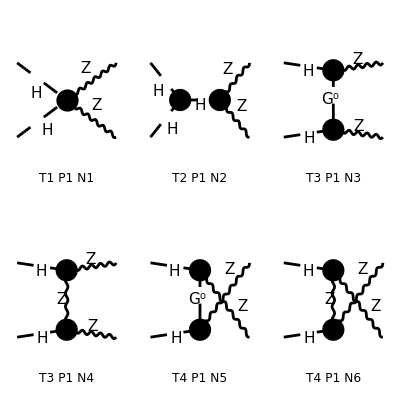

```mathematica
Process={S[1],S[1]}-> {V[2],V[2]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 6 Particles amplitudes

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

1/(CW2^4 MZ2^2 SW2^2)π^2 Alfa2 (CW2^2 (MH2^2-2 MH2 (MZ2+T)+(MZ2-T)^2)^2 (Den(T,MZ2))^2+CW2^2 (MH2^2-2 MH2 (MZ2+U)+(MZ2-U)^2)^2 (Den(U,MZ2))^2-CW2 Den(T,MZ2) (12 MZ2 (MH2^2+MZ2^2)+4 MH2 MZ2 (10 MZ2-S-2 (2 T+U))-2 S (MH2-T)^2-2 MZ2^2 (5 S+8 T+4 U)+4 MZ2 T (S+T+2 U)) (3 CW2 MH2 Den(S,MH2)+2 MW2 (Den(T,MZ2)+Den(U,MZ2))+CW2)+CW2 Den(U,MZ2) (2 CW2 Den(T,MZ2) (MH2^2+MH2 (6 MZ2-T-U)+MZ2^2-MZ2 (2 S+T+U)+T U)^2-(12 MZ2 (MH2^2+MZ2^2)+4 MH2 MZ2 (10 MZ2-S-2 (T+2 U))-2 S (MH2-U)^2-2 MZ2^2 (5 S+4 T+8 U)+4 MZ2 U (S+2 T+U)) (3 CW2 MH2 Den(S,MH2)+2 MW2 (Den(T,MZ2)+Den(U,MZ2))+CW2))+(12 MZ2^2-4 MZ2 S+S^2) (3 CW2 MH2 Den(S,MH2)+2 MW2 (Den(T,MZ2)+Den(U,MZ2))+CW2)^2)

```mathematica
resFCHHZZ=square1/.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y)}//FullSimplify[#,S+T+U==2MZ2+2MH2]&
```

1/(16 cw^8 MZ2^2 sw^4)ee^4 ((cw^4 (MH2^2-2 MH2 (MZ2+T)+(MZ2-T)^2)^2)/(MZ2-T)^2+(cw^4 (MH2^2-2 MH2 (MZ2+U)+(MZ2-U)^2)^2)/(MZ2-U)^2+1/(U-MZ2)cw^2 (-(12 MZ2 (MH2^2+MZ2^2)+4 MH2 MZ2 (10 MZ2-S-2 (T+2 U))-2 S (MH2-U)^2-2 MZ2^2 (5 S+4 T+8 U)+4 MZ2 U (S+2 T+U)) (cw^2 ((3 MH2)/(S-MH2)+1)+2 MW2 (1/(T-MZ2)+1/(U-MZ2)))-(cw^2 (-2 U (4 MZ2+T)+(T-4 MZ2)^2-S^2+U^2)^2)/(8 (MZ2-T)))-(cw^2 (12 MZ2 (MH2^2+MZ2^2)+4 MH2 MZ2 (10 MZ2-S-2 (2 T+U))-2 S (MH2-T)^2-2 MZ2^2 (5 S+8 T+4 U)+4 MZ2 T (S+T+2 U)) (cw^2 ((3 MH2)/(S-MH2)+1)+2 MW2 (1/(T-MZ2)+1/(U-MZ2))))/(T-MZ2)+(12 MZ2^2-4 MZ2 S+S^2) (cw^2 ((3 MH2)/(S-MH2)+1)+2 MW2 (1/(T-MZ2)+1/(U-MZ2)))^2)

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARHHZZ=Get["resANATARHHZZ.m"];
```

```mathematica
FullSimplify[resANATARHHZZ-resFCHHZZ,{T+U==2MZ2+2MH2-S,cw^2+sw^2==1}]
```

0

## HH-> WW

## ANATAR

```mathematica
Quit[];
```

#### Load ANATAR

```mathematica
$QGrafPath="/Users/avasquez/Documents/FeynRules/qgraf-3.6.6";
SetEnvironment[{"PATH"->"/opt/homebrew/bin:/opt/homebrew/sbin:/usr/local/bin:/System/Cryptexes/App/usr/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/homebrew/include:/opt/homebrew/Cellar/gmp/6.2.1_1/include/:/usr/local/homebrew/Cellar/kira/2.3/bin//","FERMATPATH"->"/Users/avasquez/Math_Pack/Loops/ferm64/fer64"}]
(* Path to FORM Kira & Fermat *)
```

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath]
<<Anatar`
```

/Users/avasquez/Documents/Anatar/ANATAR

- ANATAR -

Version: 1.0.2, (13 Nov 2025)

Authors: C. Duhr, P. Mukherjee, A. Vasquez

Please cite

https://github.com/ANATAR-hep/ANATAR

```mathematica
LoadModel["sm"]
```

The folder for the model sm was found.

All the required files were found.

Model sm is correctly loaded.

The fields content can be found in the list AN$Fields.

#### Process

```mathematica
AHHWW=GenerateAmplitude[{H,H}->{W,Wbar},OutputName->"HHWW",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_HHWW.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/HHWW/HHWW_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {H, H} -> {W, Wbar}

Amplitudes were obtained succesfully and are written in the file Amp_0.log

Done!

<|Process→{{H(p1),H(p2)}→{W(p3),Wbar(p4)}},Total→6,Name→HHWW,LoopOrder→0,Kinematics→{p1^2→MH^2,p1.p1→MH^2,1/(p1.p1)→1/MH^2,p2^2→MH^2,p2.p2→MH^2,1/(p2.p2)→1/MH^2,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→1/2 (S-2 MH^2),p1.p3→1/2 (MH^2+MW^2-T),p2.p3→1/2 (MH^2+MW^2-U),1/(p1.p2)→2/(S-2 MH^2),1/(p1.p3)→2/(MH^2+MW^2-T),1/(p2.p3)→2/(MH^2+MW^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→ⅈ GC19 ε_Lor4(p3,MW) ε_Lor4(p4,MW),DiagramID(2)→-ⅈ GC46 GC61 Den(-p1-p2,MH) ε_Lor4(p3,MW) ε_Lor4(p4,MW),DiagramID(3)→-ⅈ GC24^2 Den(p3-p1,MW) (2 ε_p1(p3,MW)-ε_p3(p3,MW)) (ε_p1(p4,MW)-ε_p2(p4,MW)-ε_p3(p4,MW)),DiagramID(4)→ⅈ GC61^2 Den(p3-p1,MW) ε_iLor2(p3,MW) ε_iLor2(p4,MW),DiagramID(5)→-ⅈ GC24^2 Den(p1-p4,MW) (2 ε_p1(p4,MW)-ε_p4(p4,MW)) (ε_p1(p3,MW)-ε_p2(p3,MW)-ε_p4(p3,MW)),DiagramID(6)→ⅈ GC61^2 Den(p1-p4,MW) ε_iLor2(p3,MW) ε_iLor2(p4,MW)}|>

```mathematica
AHHWWC=GenerateAmplitudeConjugate[{H,H}->{W,Wbar},OutputName->"HHWW",Dimension->4]//AmplitudesFullSimplify
```

Starting diagrams computation at tree-level in model sm

Writing control file for QGraf under the name cardQG_HHWW.dat

Running QGraf...

Diagrams written in the file /Users/avasquez/Documents/Anatar/ANATAR/Outputs/HHWW/HHWW_0

Computing amplitudes...

A total of 6 diagrams have been generated for the process {H, H} -> {W, Wbar}

Amplitudes were obtained succesfully and are written in the file AmpC_0.log

Done!

<|Process→{{H(p1),H(p2)}→{W(p3),Wbar(p4)}},Total→6,Name→HHWW,LoopOrder→0,Kinematics→{p1^2→MH^2,p1.p1→MH^2,1/(p1.p1)→1/MH^2,p2^2→MH^2,p2.p2→MH^2,1/(p2.p2)→1/MH^2,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→1/2 (S-2 MH^2),p1.p3→1/2 (MH^2+MW^2-T),p2.p3→1/2 (MH^2+MW^2-U),1/(p1.p2)→2/(S-2 MH^2),1/(p1.p3)→2/(MH^2+MW^2-T),1/(p2.p3)→2/(MH^2+MW^2-U),p4→p1+p2-p3},Amplitudes→{DiagramID(1)→-ⅈ GC19 (ε^†)_LorC4^(p3,MW) (ε^†)_LorC4^(p4,MW),DiagramID(2)→ⅈ GC46 GC61 Den(-p1-p2,MH) (ε^†)_LorC4^(p3,MW) (ε^†)_LorC4^(p4,MW),DiagramID(3)→ⅈ GC24^2 Den(p3-p1,MW) (2 (ε^†)_p1^(p3,MW)-(ε^†)_p3^(p3,MW)) ((ε^†)_p1^(p4,MW)-(ε^†)_p2^(p4,MW)-(ε^†)_p3^(p4,MW)),DiagramID(4)→-ⅈ GC61^2 Den(p3-p1,MW) (ε^†)_iLorC2^(p3,MW) (ε^†)_iLorC2^(p4,MW),DiagramID(5)→ⅈ GC24^2 Den(p1-p4,MW) (2 (ε^†)_p1^(p4,MW)-(ε^†)_p4^(p4,MW)) ((ε^†)_p1^(p3,MW)-(ε^†)_p2^(p3,MW)-(ε^†)_p4^(p3,MW)),DiagramID(6)→-ⅈ GC61^2 Den(p1-p4,MW) (ε^†)_iLorC2^(p3,MW) (ε^†)_iLorC2^(p4,MW)}|>

```mathematica
AmpSQHHWW=GenerateAmplitudeSquare[AHHWW,AHHWWC,Dimension->4]//AmplitudesSimplify
```

Amplitude Square were obtained succesfully and written in AmpSq_00.log

<|Process→{{H(p1),H(p2)}→{W(p3),Wbar(p4)}},Name→HHWW,LoopOrder→0,Kinematics→{p1^2→MH^2,p1.p1→MH^2,1/(p1.p1)→1/MH^2,p2^2→MH^2,p2.p2→MH^2,1/(p2.p2)→1/MH^2,p3^2→MW^2,p3.p3→MW^2,1/(p3.p3)→1/MW^2,p4^2→MW^2,p4.p4→MW^2,1/(p4.p4)→1/MW^2,p1.p2→1/2 (S-2 MH^2),p1.p3→1/2 (MH^2+MW^2-T),p2.p3→1/2 (MH^2+MW^2-U),1/(p1.p2)→2/(S-2 MH^2),1/(p1.p3)→2/(MH^2+MW^2-T),1/(p2.p3)→2/(MH^2+MW^2-U),p4→p1+p2-p3},Amplitudes→1/(64 MW^4 sw2^4)ee^4 (4 sw2^2 (Den(p3-p2,MW))^2 MH^8-24 MW^2 sw2^2 (Den(p3-p2,MW))^2 MH^6-8 S sw2^2 (Den(p3-p2,MW))^2 MH^6-8 ee^2 sw2 vev^2 (Den(p3-p2,MW))^2 MH^6-8 sw2^2 T (Den(p3-p2,MW))^2 MH^6-8 sw2^2 U (Den(p3-p2,MW))^2 MH^6-16 sw2^2 Den(p3-p2,MW) MH^6+16 sw2^2 MH^4+36 sw2^2 (4 MH^4-4 (T+U) MH^2+8 MW^4+(T+U)^2) (Den(-p1-p2,MH))^2 MH^4+4 ee^4 vev^4 (Den(p3-p2,MW))^2 MH^4+32 MW^4 sw2^2 (Den(p3-p2,MW))^2 MH^4+4 S^2 sw2^2 (Den(p3-p2,MW))^2 MH^4+28 MW^2 S sw2^2 (Den(p3-p2,MW))^2 MH^4+4 sw2^2 T^2 (Den(p3-p2,MW))^2 MH^4+4 sw2^2 U^2 (Den(p3-p2,MW))^2 MH^4-16 ee^2 MW^2 sw2 vev^2 (Den(p3-p2,MW))^2 MH^4+8 ee^2 S sw2 vev^2 (Den(p3-p2,MW))^2 MH^4+12 ee^2 sw2 T vev^2 (Den(p3-p2,MW))^2 MH^4+12 ee^2 sw2 U vev^2 (Den(p3-p2,MW))^2 MH^4+28 MW^2 sw2^2 T (Den(p3-p2,MW))^2 MH^4+8 S sw2^2 T (Den(p3-p2,MW))^2 MH^4+12 MW^2 sw2^2 U (Den(p3-p2,MW))^2 MH^4+16 S sw2^2 U (Den(p3-p2,MW))^2 MH^4+16 sw2^2 T U (Den(p3-p2,MW))^2 MH^4-32 MW^2 sw2^2 Den(p3-p2,MW) MH^4+16 S sw2^2 Den(p3-p2,MW) MH^4+16 ee^2 sw2 vev^2 Den(p3-p2,MW) MH^4+24 sw2^2 T Den(p3-p2,MW) MH^4+24 sw2^2 U Den(p3-p2,MW) MH^4-4 ee^4 T vev^4 (Den(p3-p2,MW))^2 MH^2-4 ee^4 U vev^4 (Den(p3-p2,MW))^2 MH^2-8 MW^6 sw2^2 (Den(p3-p2,MW))^2 MH^2-24 MW^2 S^2 sw2^2 (Den(p3-p2,MW))^2 MH^2+32 MW^4 S sw2^2 (Den(p3-p2,MW))^2 MH^2-24 MW^2 sw2^2 T^2 (Den(p3-p2,MW))^2 MH^2-8 MW^2 sw2^2 U^2 (Den(p3-p2,MW))^2 MH^2-8 S sw2^2 U^2 (Den(p3-p2,MW))^2 MH^2-8 sw2^2 T U^2 (Den(p3-p2,MW))^2 MH^2-4 ee^2 sw2 T^2 vev^2 (Den(p3-p2,MW))^2 MH^2-4 ee^2 sw2 U^2 vev^2 (Den(p3-p2,MW))^2 MH^2-40 ee^2 MW^4 sw2 vev^2 (Den(p3-p2,MW))^2 MH^2+8 ee^2 MW^2 sw2 T vev^2 (Den(p3-p2,MW))^2 MH^2-4 ee^2 S sw2 T vev^2 (Den(p3-p2,MW))^2 MH^2+24 ee^2 MW^2 sw2 U vev^2 (Den(p3-p2,MW))^2 MH^2-12 ee^2 S sw2 U vev^2 (Den(p3-p2,MW))^2 MH^2-16 ee^2 sw2 T U vev^2 (Den(p3-p2,MW))^2 MH^2+32 MW^4 sw2^2 T (Den(p3-p2,MW))^2 MH^2-48 MW^2 S sw2^2 T (Den(p3-p2,MW))^2 MH^2-8 S^2 sw2^2 U (Den(p3-p2,MW))^2 MH^2+24 MW^2 S sw2^2 U (Den(p3-p2,MW))^2 MH^2-8 sw2^2 T^2 U (Den(p3-p2,MW))^2 MH^2+24 MW^2 sw2^2 T U (Den(p3-p2,MW))^2 MH^2-16 S sw2^2 T U (Den(p3-p2,MW))^2 MH^2-16 sw2^2 T MH^2-16 sw2^2 U MH^2-80 MW^4 sw2^2 Den(p3-p2,MW) MH^2-8 sw2^2 T^2 Den(p3-p2,MW) MH^2-8 sw2^2 U^2 Den(p3-p2,MW) MH^2-16 ee^2 sw2 T vev^2 Den(p3-p2,MW) MH^2-16 ee^2 sw2 U vev^2 Den(p3-p2,MW) MH^2+16 MW^2 sw2^2 T Den(p3-p2,MW) MH^2-8 S sw2^2 T Den(p3-p2,MW) MH^2+48 MW^2 sw2^2 U Den(p3-p2,MW) MH^2-24 S sw2^2 U Den(p3-p2,MW) MH^2-32 sw2^2 T U Den(p3-p2,MW) MH^2+12 sw2 Den(-p1-p2,MH) (2 sw2 (4 MH^4-4 (T+U) MH^2+8 MW^4+(T+U)^2)+(4 sw2 MH^6+2 (4 sw2 MW^2+2 ee^2 vev^2-sw2 (5 T+U)) MH^4-4 (3 sw2 MW^4+sw2 (S+4 T) MW^2+ee^2 (T+U) vev^2-sw2 T (2 T+U)) MH^2+4 MW^2 sw2 T (S+2 T)+2 MW^4 (4 ee^2 vev^2+2 S sw2+sw2 (U-3 T))-(T+U) (2 sw2 T^2-ee^2 (T+U) vev^2)) Den(p3-p1,MW)+(-4 sw2 MH^6+(-8 sw2 MW^2+4 ee^2 vev^2+4 S sw2+6 sw2 T+6 sw2 U) MH^4-2 (10 sw2 MW^4-2 sw2 (T+3 U) MW^2+sw2 T^2+sw2 U^2+2 ee^2 T vev^2+2 ee^2 U vev^2+4 sw2 T U+S sw2 (T+3 U)) MH^2+2 MW^2 sw2 (T^2-4 U T-U^2+S (T-U))+MW^4 (8 ee^2 vev^2+4 S sw2-2 sw2 T+6 sw2 U)+(T+U) (ee^2 (T+U) vev^2+2 S sw2 U+2 sw2 T U)) Den(p3-p2,MW)) MH^2+32 MW^4 sw2^2+4 sw2^2 T^2+4 sw2^2 U^2+(4 sw2^2 MH^8-8 sw2 (3 sw2 MW^2-ee^2 vev^2+2 sw2 T) MH^6+4 (8 sw2^2 MW^4+sw2 (4 ee^2 vev^2+S sw2+9 sw2 T+sw2 U) MW^2+ee^4 vev^4+6 sw2^2 T^2-ee^2 sw2 (5 T+U) vev^2) MH^4-4 (2 sw2^2 MW^6+2 sw2 (3 ee^2 vev^2+S sw2-5 sw2 T+sw2 U) MW^4+2 sw2 (ee^2 S vev^2+4 ee^2 T vev^2+S sw2 T+sw2 T U) MW^2+(2 sw2 T-ee^2 vev^2) (2 sw2 T^2-ee^2 (T+U) vev^2)) MH^2-4 MW^8 sw2^2+(ee^2 (T+U) vev^2-2 sw2 T^2)^2+4 MW^6 sw2^2 (S+T+U)+4 MW^4 (2 ee^4 vev^4+ee^2 sw2 (U-3 T) vev^2+2 sw2^2 T (T-U)+2 S sw2 (ee^2 vev^2-sw2 T))+4 MW^2 sw2 T (4 ee^2 T vev^2+sw2 T (U-3 T)+S (2 ee^2 vev^2+sw2 T))) (Den(p3-p1,MW))^2+8 ee^4 MW^4 vev^4 (Den(p3-p2,MW))^2+ee^4 T^2 vev^4 (Den(p3-p2,MW))^2+ee^4 U^2 vev^4 (Den(p3-p2,MW))^2+2 ee^4 T U vev^4 (Den(p3-p2,MW))^2+4 MW^2 sw2^2 T^3 (Den(p3-p2,MW))^2-4 MW^8 sw2^2 (Den(p3-p2,MW))^2+4 MW^2 S^3 sw2^2 (Den(p3-p2,MW))^2-12 MW^4 S^2 sw2^2 (Den(p3-p2,MW))^2+12 MW^6 S sw2^2 (Den(p3-p2,MW))^2-12 MW^4 sw2^2 T^2 (Den(p3-p2,MW))^2+12 MW^2 S sw2^2 T^2 (Den(p3-p2,MW))^2+4 MW^4 sw2^2 U^2 (Den(p3-p2,MW))^2+4 S^2 sw2^2 U^2 (Den(p3-p2,MW))^2-8 MW^2 S sw2^2 U^2 (Den(p3-p2,MW))^2+4 sw2^2 T^2 U^2 (Den(p3-p2,MW))^2-8 MW^2 sw2^2 T U^2 (Den(p3-p2,MW))^2+8 S sw2^2 T U^2 (Den(p3-p2,MW))^2+4 ee^2 MW^2 sw2 T^2 vev^2 (Den(p3-p2,MW))^2-4 ee^2 MW^2 sw2 U^2 vev^2 (Den(p3-p2,MW))^2+4 ee^2 S sw2 U^2 vev^2 (Den(p3-p2,MW))^2+4 ee^2 sw2 T U^2 vev^2 (Den(p3-p2,MW))^2+8 ee^2 MW^4 S sw2 vev^2 (Den(p3-p2,MW))^2-4 ee^2 MW^4 sw2 T vev^2 (Den(p3-p2,MW))^2+4 ee^2 MW^2 S sw2 T vev^2 (Den(p3-p2,MW))^2+4 ee^2 sw2 T^2 U vev^2 (Den(p3-p2,MW))^2+12 ee^2 MW^4 sw2 U vev^2 (Den(p3-p2,MW))^2-4 ee^2 MW^2 S sw2 U vev^2 (Den(p3-p2,MW))^2-16 ee^2 MW^2 sw2 T U vev^2 (Den(p3-p2,MW))^2+4 ee^2 S sw2 T U vev^2 (Den(p3-p2,MW))^2+12 MW^6 sw2^2 T (Den(p3-p2,MW))^2+12 MW^2 S^2 sw2^2 T (Den(p3-p2,MW))^2-24 MW^4 S sw2^2 T (Den(p3-p2,MW))^2-4 MW^6 sw2^2 U (Den(p3-p2,MW))^2-4 MW^2 S^2 sw2^2 U (Den(p3-p2,MW))^2+8 MW^4 S sw2^2 U (Den(p3-p2,MW))^2-4 MW^2 sw2^2 T^2 U (Den(p3-p2,MW))^2+8 MW^4 sw2^2 T U (Den(p3-p2,MW))^2-8 MW^2 S sw2^2 T U (Den(p3-p2,MW))^2+8 sw2^2 T U+16 MW^4 S sw2^2 Den(p3-p2,MW)+8 MW^2 sw2^2 T^2 Den(p3-p2,MW)-8 MW^2 sw2^2 U^2 Den(p3-p2,MW)+8 S sw2^2 U^2 Den(p3-p2,MW)+8 sw2^2 T U^2 Den(p3-p2,MW)+4 ee^2 sw2 T^2 vev^2 Den(p3-p2,MW)+4 ee^2 sw2 U^2 vev^2 Den(p3-p2,MW)+32 ee^2 MW^4 sw2 vev^2 Den(p3-p2,MW)+8 ee^2 sw2 T U vev^2 Den(p3-p2,MW)-8 MW^4 sw2^2 T Den(p3-p2,MW)+8 MW^2 S sw2^2 T Den(p3-p2,MW)+24 MW^4 sw2^2 U Den(p3-p2,MW)-8 MW^2 S sw2^2 U Den(p3-p2,MW)+8 sw2^2 T^2 U Den(p3-p2,MW)-32 MW^2 sw2^2 T U Den(p3-p2,MW)+8 S sw2^2 T U Den(p3-p2,MW)-2 Den(p3-p1,MW) ((4 sw2^2 MH^8+4 sw2^2 (4 MW^2-S-3 T-U) MH^6-4 (10 sw2^2 MW^4+sw2^2 (7 S+13 T-U) MW^2+ee^4 vev^4-3 sw2^2 T^2-ee^2 sw2 T vev^2+ee^2 sw2 U vev^2-3 sw2^2 T U+S sw2 (ee^2 vev^2-sw2 (2 T+U))) MH^4+2 (8 sw2^2 MW^6+2 sw2 (8 ee^2 vev^2+9 S sw2+sw2 (U-13 T)) MW^4+2 sw2 (2 sw2 S^2+(ee^2 vev^2+10 sw2 T) S+3 ee^2 (T-U) vev^2+2 sw2 T (5 T+U)) MW^2+2 ee^4 T vev^4+2 ee^4 U vev^4-2 sw2^2 T^3-3 ee^2 sw2 T^2 vev^2+ee^2 sw2 U^2 vev^2+2 ee^2 sw2 T U vev^2-6 sw2^2 T^2 U+S sw2 (ee^2 (T+3 U) vev^2-2 sw2 T (T+2 U))) MH^2+4 MW^8 sw2^2-4 MW^6 sw2^2 (S+3 T+U)+(2 sw2 T^2-ee^2 (T+U) vev^2) (ee^2 (T+U) vev^2+2 S sw2 U+2 sw2 T U)-2 MW^2 sw2 (4 sw2 T S^2+6 sw2 T^2 S+ee^2 (3 T-U) vev^2 S+ee^2 (5 T^2-4 U T-U^2) vev^2+2 sw2 T^2 (T+3 U))-4 MW^4 (2 ee^4 vev^4+2 ee^2 sw2 (U-T) vev^2+2 S^2 sw2^2-3 sw2^2 T (T+U)+S sw2 (2 ee^2 vev^2+sw2 (U-4 T)))) Den(p3-p2,MW)-2 sw2 (4 sw2 MH^6+2 (4 sw2 MW^2+2 ee^2 vev^2-sw2 (5 T+U)) MH^4-4 (3 sw2 MW^4+sw2 (S+4 T) MW^2+ee^2 (T+U) vev^2-sw2 T (2 T+U)) MH^2+4 MW^2 sw2 T (S+2 T)+2 MW^4 (4 ee^2 vev^2+2 S sw2+sw2 (U-3 T))-(T+U) (2 sw2 T^2-ee^2 (T+U) vev^2))))|>

```mathematica
resANATARHHWW=AmpSQHHWW[Amplitudes]//.{vev->2MW sw/ee,Den[x_,y_]:>1/(x^2-y^2),-p1-p2->√S,(-p1-p2)^2->S,-p1+p3->√T,p1-p3->√T,(p1-p3)^2->T,(p3-p2)^2->U,(p2-p3)^2->U,SW2->sw^2,CW2->cw^2,sw2->sw^2}
```

1/(64 MW^4 sw^8)ee^4 ((4 sw^4 MH^8)/((U-MW^2)^2)-(16 sw^4 MH^6)/(U-MW^2)-(56 MW^2 sw^4 MH^6)/((U-MW^2)^2)-(8 S sw^4 MH^6)/((U-MW^2)^2)-(8 sw^4 T MH^6)/((U-MW^2)^2)-(8 sw^4 U MH^6)/((U-MW^2)^2)+16 sw^4 MH^4+(36 sw^4 (4 MH^4-4 (T+U) MH^2+8 MW^4+(T+U)^2) MH^4)/((S-MH^2)^2)+(32 MW^2 sw^4 MH^4)/(U-MW^2)+(16 S sw^4 MH^4)/(U-MW^2)+(24 sw^4 T MH^4)/(U-MW^2)+(24 sw^4 U MH^4)/(U-MW^2)+(32 MW^4 sw^4 MH^4)/((U-MW^2)^2)+(4 S^2 sw^4 MH^4)/((U-MW^2)^2)+(60 MW^2 S sw^4 MH^4)/((U-MW^2)^2)+(4 sw^4 T^2 MH^4)/((U-MW^2)^2)+(4 sw^4 U^2 MH^4)/((U-MW^2)^2)+(76 MW^2 sw^4 T MH^4)/((U-MW^2)^2)+(8 S sw^4 T MH^4)/((U-MW^2)^2)+(60 MW^2 sw^4 U MH^4)/((U-MW^2)^2)+(16 S sw^4 U MH^4)/((U-MW^2)^2)+(16 sw^4 T U MH^4)/((U-MW^2)^2)-16 sw^4 T MH^2-16 sw^4 U MH^2+1/(S-MH^2)12 sw^2 (2 (4 MH^4-4 (T+U) MH^2+8 MW^4+(T+U)^2) sw^2+1/(T-MW^2)(4 sw^2 MH^6+2 (12 MW^2 sw^2-sw^2 (5 T+U)) MH^4-4 (3 sw^2 MW^4+sw^2 (S+4 T) MW^2+4 sw^2 (T+U) MW^2-sw^2 T (2 T+U)) MH^2+4 MW^2 sw^2 T (S+2 T)+2 MW^4 (16 MW^2 sw^2+2 S sw^2+(U-3 T) sw^2)-(T+U) (2 sw^2 T^2-4 MW^2 sw^2 (T+U)))+1/(U-MW^2)(-4 sw^2 MH^6+(8 MW^2 sw^2+4 S sw^2+6 T sw^2+6 U sw^2) MH^4-2 (10 sw^2 MW^4+8 sw^2 T MW^2+8 sw^2 U MW^2-2 sw^2 (T+3 U) MW^2+sw^2 T^2+sw^2 U^2+4 sw^2 T U+S sw^2 (T+3 U)) MH^2+MW^4 (32 MW^2 sw^2+4 S sw^2-2 T sw^2+6 U sw^2)+2 MW^2 sw^2 (T^2-4 U T-U^2+S (T-U))+(T+U) (2 S U sw^2+2 T U sw^2+4 MW^2 (T+U) sw^2))) MH^2-(80 MW^4 sw^4 MH^2)/(U-MW^2)-(8 sw^4 T^2 MH^2)/(U-MW^2)-(8 sw^4 U^2 MH^2)/(U-MW^2)-(48 MW^2 sw^4 T MH^2)/(U-MW^2)-(8 S sw^4 T MH^2)/(U-MW^2)-(16 MW^2 sw^4 U MH^2)/(U-MW^2)-(24 S sw^4 U MH^2)/(U-MW^2)-(32 sw^4 T U MH^2)/(U-MW^2)-(168 MW^6 sw^4 MH^2)/((U-MW^2)^2)-(24 MW^2 S^2 sw^4 MH^2)/((U-MW^2)^2)+(32 MW^4 S sw^4 MH^2)/((U-MW^2)^2)-(40 MW^2 sw^4 T^2 MH^2)/((U-MW^2)^2)-(24 MW^2 sw^4 U^2 MH^2)/((U-MW^2)^2)-(8 S sw^4 U^2 MH^2)/((U-MW^2)^2)-(8 sw^4 T U^2 MH^2)/((U-MW^2)^2)-(64 MW^2 S sw^4 T MH^2)/((U-MW^2)^2)+(32 MW^4 sw^4 U MH^2)/((U-MW^2)^2)-(8 S^2 sw^4 U MH^2)/((U-MW^2)^2)-(24 MW^2 S sw^4 U MH^2)/((U-MW^2)^2)-(8 sw^4 T^2 U MH^2)/((U-MW^2)^2)-(40 MW^2 sw^4 T U MH^2)/((U-MW^2)^2)-(16 S sw^4 T U MH^2)/((U-MW^2)^2)+32 MW^4 sw^4+4 sw^4 T^2+4 sw^4 U^2+8 sw^4 T U+1/((T-MW^2)^2)(4 sw^4 MH^8-8 sw^2 (2 sw^2 T-MW^2 sw^2) MH^6+4 (24 MW^4 sw^4+6 T^2 sw^4-4 MW^2 (5 T+U) sw^4+MW^2 (16 MW^2 sw^2+S sw^2+9 T sw^2+U sw^2) sw^2) MH^4-4 (2 sw^4 MW^6+2 sw^2 (12 MW^2 sw^2+S sw^2-5 T sw^2+U sw^2) MW^4+2 sw^2 (4 MW^2 S sw^2+16 MW^2 T sw^2+S T sw^2+T U sw^2) MW^2+(2 sw^2 T-4 MW^2 sw^2) (2 sw^2 T^2-4 MW^2 sw^2 (T+U))) MH^2-4 MW^8 sw^4+(4 MW^2 sw^2 (T+U)-2 sw^2 T^2)^2+4 MW^6 sw^4 (S+T+U)+4 MW^4 (32 MW^4 sw^4+2 T (T-U) sw^4+4 MW^2 (U-3 T) sw^4+2 S (4 MW^2 sw^2-sw^2 T) sw^2)+4 MW^2 sw^2 T (16 MW^2 T sw^2+T (U-3 T) sw^2+S (8 MW^2 sw^2+T sw^2)))-1/(T-MW^2)2 (1/(U-MW^2)(4 sw^4 MH^8+4 sw^4 (4 MW^2-S-3 T-U) MH^6-4 (26 MW^4 sw^4-3 T^2 sw^4-4 MW^2 T sw^4+MW^2 (7 S+13 T-U) sw^4+4 MW^2 U sw^4-3 T U sw^4+S (4 MW^2 sw^2-sw^2 (2 T+U)) sw^2) MH^4+2 (8 sw^4 MW^6+32 sw^4 T MW^4+32 sw^4 U MW^4+2 sw^2 (32 MW^2 sw^2+9 S sw^2+(U-13 T) sw^2) MW^4-12 sw^4 T^2 MW^2+4 sw^4 U^2 MW^2+8 sw^4 T U MW^2+2 sw^2 (2 S^2 sw^2+12 MW^2 (T-U) sw^2+2 T (5 T+U) sw^2+S (4 MW^2 sw^2+10 T sw^2)) MW^2-2 sw^4 T^3-6 sw^4 T^2 U+S sw^2 (4 MW^2 sw^2 (T+3 U)-2 sw^2 T (T+2 U))) MH^2+4 MW^8 sw^4-4 MW^6 sw^4 (S+3 T+U)+(2 sw^2 T^2-4 MW^2 sw^2 (T+U)) (2 S U sw^2+2 T U sw^2+4 MW^2 (T+U) sw^2)-2 MW^2 sw^2 (6 S T^2 sw^2+4 S^2 T sw^2+4 MW^2 S (3 T-U) sw^2+2 T^2 (T+3 U) sw^2+4 MW^2 (5 T^2-4 U T-U^2) sw^2)-4 MW^4 (32 MW^4 sw^4+2 S^2 sw^4+8 MW^2 (U-T) sw^4-3 T (T+U) sw^4+S (8 MW^2 sw^2+(U-4 T) sw^2) sw^2))-2 sw^2 (4 sw^2 MH^6+2 (12 MW^2 sw^2-sw^2 (5 T+U)) MH^4-4 (3 sw^2 MW^4+sw^2 (S+4 T) MW^2+4 sw^2 (T+U) MW^2-sw^2 T (2 T+U)) MH^2+4 MW^2 sw^2 T (S+2 T)+2 MW^4 (16 MW^2 sw^2+2 S sw^2+(U-3 T) sw^2)-(T+U) (2 sw^2 T^2-4 MW^2 sw^2 (T+U))))+(128 MW^6 sw^4)/(U-MW^2)+(16 MW^4 S sw^4)/(U-MW^2)+(24 MW^2 sw^4 T^2)/(U-MW^2)+(8 MW^2 sw^4 U^2)/(U-MW^2)+(8 S sw^4 U^2)/(U-MW^2)+(8 sw^4 T U^2)/(U-MW^2)-(8 MW^4 sw^4 T)/(U-MW^2)+(8 MW^2 S sw^4 T)/(U-MW^2)+(24 MW^4 sw^4 U)/(U-MW^2)-(8 MW^2 S sw^4 U)/(U-MW^2)+(8 sw^4 T^2 U)/(U-MW^2)+(8 S sw^4 T U)/(U-MW^2)+(124 MW^8 sw^4)/((U-MW^2)^2)+(4 MW^2 S^3 sw^4)/((U-MW^2)^2)-(12 MW^4 S^2 sw^4)/((U-MW^2)^2)+(44 MW^6 S sw^4)/((U-MW^2)^2)+(4 MW^2 sw^4 T^3)/((U-MW^2)^2)+(20 MW^4 sw^4 T^2)/((U-MW^2)^2)+(12 MW^2 S sw^4 T^2)/((U-MW^2)^2)+(4 MW^4 sw^4 U^2)/((U-MW^2)^2)+(4 S^2 sw^4 U^2)/((U-MW^2)^2)+(8 MW^2 S sw^4 U^2)/((U-MW^2)^2)+(4 sw^4 T^2 U^2)/((U-MW^2)^2)+(8 MW^2 sw^4 T U^2)/((U-MW^2)^2)+(8 S sw^4 T U^2)/((U-MW^2)^2)-(4 MW^6 sw^4 T)/((U-MW^2)^2)+(12 MW^2 S^2 sw^4 T)/((U-MW^2)^2)-(8 MW^4 S sw^4 T)/((U-MW^2)^2)+(44 MW^6 sw^4 U)/((U-MW^2)^2)-(4 MW^2 S^2 sw^4 U)/((U-MW^2)^2)-(8 MW^4 S sw^4 U)/((U-MW^2)^2)+(12 MW^2 sw^4 T^2 U)/((U-MW^2)^2)-(24 MW^4 sw^4 T U)/((U-MW^2)^2)+(8 MW^2 S sw^4 T U)/((U-MW^2)^2))

```mathematica
SetDirectory[$AnatarPath];
Save["resANATARHHWW.m",resANATARHHWW];
```

## FormCalc

```mathematica
Quit[];
```

#### Load FormCalc

```mathematica
MacPath="/Users/avasquez/Math_Pack/";
MacPath2="/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/";
<<"/Users/avasquez/Dropbox/Mathematica/FeynArts-3.10/FeynArts.m"
Get[MacPath<>"FormCalc-9.10/FormCalc.m"]
```

FeynArts 3.10 (3 Sep 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

#### Process

loading generic model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/avasquez/Library/CloudStorage/Dropbox/Mathematica/FeynArts-3.10/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

in total: 6 Particles insertions

> Top. 1 aebe/cede/0.m, 1 diagram

> Top. 2 aebe/cfdf/ef.m, 1 diagram

> Top. 3 aebf/cedf/ef.m, 2 diagrams

> Top. 4 aebf/cfde/ef.m, 2 diagrams

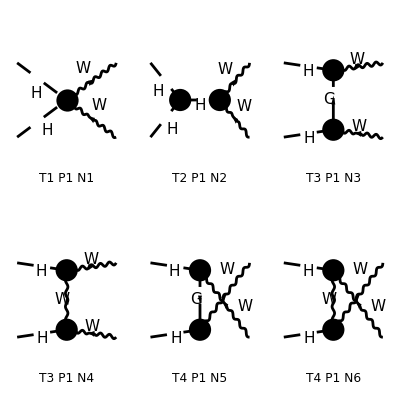

```mathematica
Process={S[1],S[1]}-> {V[3],-V[3]};
top=CreateTopologies[0,2-> 2];
AA=InsertFields[top,Process,InsertionLevel-> {Particles}];
Paint[AA,SheetHeader->False,ImageSize->400];
```

```mathematica
Amp0=CreateFeynAmp[AA]//.Subexpr[];
res1=CalcFeynAmp[Amp0,FermionChains-> Chiral];
_Hel=0;
square1=(PolarizationSum[res1,res1]//.Subexpr[])//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 6 Particles amplitudes

preparing FORM code in /Users/avasquez/fc-amp-1.frm

running FORM...

ok

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/avasquez/fc-pol-2.frm

running FORM...

ok

1/(MW2^2 SW2^2)π^2 Alfa2 (-Den(T,MW2) (12 MW2 (MH2^2+MW2^2)+4 MH2 MW2 (10 MW2-S-2 (2 T+U))-2 S (MH2-T)^2-2 MW2^2 (5 S+8 T+4 U)+4 MW2 T (S+T+2 U)) (3 MH2 Den(S,MH2)+2 MW2 (Den(T,MW2)+Den(U,MW2))+1)+Den(U,MW2) (2 Den(T,MW2) (MH2^2+MH2 (6 MW2-T-U)+MW2^2-MW2 (2 S+T+U)+T U)^2-(12 MW2 (MH2^2+MW2^2)+4 MH2 MW2 (10 MW2-S-2 (T+2 U))-2 S (MH2-U)^2-2 MW2^2 (5 S+4 T+8 U)+4 MW2 U (S+2 T+U)) (3 MH2 Den(S,MH2)+2 MW2 (Den(T,MW2)+Den(U,MW2))+1))+(MH2^2-2 MH2 (MW2+T)+(MW2-T)^2)^2 (Den(T,MW2))^2+(MH2^2-2 MH2 (MW2+U)+(MW2-U)^2)^2 (Den(U,MW2))^2+(12 MW2^2-4 MW2 S+S^2) (3 MH2 Den(S,MH2)+2 MW2 (Den(T,MW2)+Den(U,MW2))+1)^2)

```mathematica
resFCHHWW=square1/.{Alfa2->(ee^2/(4π))^2,SW2->sw^2,CW2->cw^2,Den[x_,y_]:>1/(x-y)}//FullSimplify[#,S+T+U==2MW2+2MH2]&
```

1/(16 MW2^2 sw^4)ee^4 (-1/(U-MW2)(((3 MH2)/(S-MH2)+2 MW2 (1/(T-MW2)+1/(U-MW2))+1) (12 MW2 (MH2^2+MW2^2)+4 MH2 MW2 (10 MW2-S-2 (T+2 U))-2 S (MH2-U)^2-2 MW2^2 (5 S+4 T+8 U)+4 MW2 U (S+2 T+U))+((-2 U (4 MW2+T)+(T-4 MW2)^2-S^2+U^2)^2)/(8 (MW2-T)))-(((3 MH2)/(S-MH2)+2 MW2 (1/(T-MW2)+1/(U-MW2))+1) (12 MW2 (MH2^2+MW2^2)+4 MH2 MW2 (10 MW2-S-2 (2 T+U))-2 S (MH2-T)^2-2 MW2^2 (5 S+8 T+4 U)+4 MW2 T (S+T+2 U)))/(T-MW2)+((MH2^2-2 MH2 (MW2+T)+(MW2-T)^2)^2)/(MW2-T)^2+((MH2^2-2 MH2 (MW2+U)+(MW2-U)^2)^2)/(MW2-U)^2+(12 MW2^2-4 MW2 S+S^2) ((3 MH2)/(S-MH2)+2 MW2 (1/(T-MW2)+1/(U-MW2))+1)^2)

## Comparison

```mathematica
$AnatarPath="/Users/avasquez/Documents/Anatar/ANATAR";
SetDirectory[$AnatarPath];
resANATARHHWW=Get["resANATARHHWW.m"];
```

```mathematica
FullSimplify[resANATARHHWW-resFCHHWW,{T+U==2MW2+2MH2-S,cw^2+sw^2==1}]
```

0